```mathematica
(*Compute the repo root from the notebook location*)
repoRoot=ParentDirectory@NotebookDirectory[];
repoAppDir=FileNameJoin[{repoRoot,"mma"}];

If[!MemberQ[$Path,repoAppDir],AppendTo[$Path,repoAppDir];];

ClearAll["LocalF1`*"];
<<LocalF1`;
```

## Nodal Curve Parametrization

```mathematica
F1=MirrorCurveLocalF1[x,y,m,u]
```

-1/u+m/x+x+1/(x y)+y

```mathematica
m1=WeierstrassChangeOfVariables[{x,y}->{X,Y},m,u]
```

{x→(-9+36 u^2 (m+3 u)+6 X+√2 Y)/(6 u (-3+12 m u^2+2 X)),y→(36 u^2)/(3-12 m u^2-2 X)}

```mathematica
m2=WeierstrassChangeOfVariablesInverse[{X,Y}->{x,y},m,u]
```

{X→3/2-(6 u^2 (3+m y))/y,Y→-(54 √2 u^2 (-1+u (2 x+y)))/y}

```mathematica
Simplify[{x,y}/.m1/.m2]
```

{x,y}

```mathematica
Simplify[{X,Y}/.m2/.m1]
```

{X,Y}

```mathematica
Simplify[F1/.m1]
Numerator[%]
Simplify@Flatten[{Coefficient[%, {Y^2, X^4, X^3, X^2, X}], (%/.{X->0,Y->0}), -%/.Y->0}]//TableForm
```

(-27-5832 u^6+1728 m^3 u^6+432 m^2 u^4 (-3+X)+27 X-4 X^3-324 u^3 (-3+2 X)-108 m u^2 (-3+36 u^3+2 X)+Y^2)/(3 u (-3+12 m u^2+2 X) (-9+36 m u^2+108 u^3+6 X+√2 Y))

-27-5832 u^6+1728 m^3 u^6+432 m^2 u^4 (-3+X)+27 X-4 X^3-324 u^3 (-3+2 X)-108 m u^2 (-3+36 u^3+2 X)+Y^2

1
0
-4
0
27 (1-8 m u^2-24 u^3+16 m^2 u^4)
27 (-1+12 m u^2+36 u^3-48 m^2 u^4-144 m u^5-216 u^6+64 m^3 u^6)
5832 u^6-1728 m^3 u^6-432 m^2 u^4 (-3+X)+(3-2 X)^2 (3+X)+324 u^3 (-3+2 X)+108 m u^2 (-3+36 u^3+2 X)

```mathematica
{MirrorCurveg2[m,u],MirrorCurveg3[m,u],MirrorCurvef3[X,m,u]}//TableForm
```

27 (1-8 m u^2-24 u^3+16 m^2 u^4)
27 (-1+12 m u^2+36 u^3-48 m^2 u^4-144 m u^5-216 u^6+64 m^3 u^6)
5832 u^6-1728 m^3 u^6-432 m^2 u^4 (-3+X)+(3-2 X)^2 (3+X)+324 u^3 (-3+2 X)+108 m u^2 (-3+36 u^3+2 X)

```mathematica
Simplify[1/(544195584 u^8)Discriminant[MirrorCurvef3[X,m,u], X]]
MirrorCurveDelta[m,u]
```

m+u-8 m^2 u^2-36 m u^3-27 u^4+16 m^3 u^4

m+u-8 m^2 u^2-36 m u^3-27 u^4+16 m^3 u^4

```mathematica
ClearAll[uvals];
uvals[m_]:=SortBy[Solve[delt[m,u]==0,u], Abs[u/.#]&];
```

```mathematica
(* for m=0, possible values of u *)
Solve[MirrorCurveDelta[0,u]==0,u]
```

{{u→0},{u→1/3},{u→-1/3 (-1)^(1/3)},{u→1/3 (-1)^(2/3)}}

```mathematica
(* for m=1, possible values of u *)
Solve[MirrorCurveDelta[1.,u]==0,u]
```

{{u→-3.02572},{u→-0.255099-0.221553 ⅈ},{u→-0.255099+0.221553 ⅈ},{u→0.263185}}

```mathematica
4(X-X0)^2(X+2X0)//Expand
Y^2-%/.{X->t^2-2X0, Y->2t(t^2-3X0)}//Simplify
```

4 X^3-12 X X0^2+8 X0^3

0

```mathematica
p1 = {X->t^2-2X0, Y->2t(t^2-3X0)};
p1 = p1/.{t->t/Sqrt[2]}//Simplify
Y^2-4(X-X0)^2(X+2X0)/.p1//Simplify
```

{X→1/2 (t^2-4 X0),Y→(t (t^2-6 X0))/(√2)}

0

```mathematica
First@Solve[Simplify[-12 X0^2/(8 X0^3)]==(-G2/-G3), X0]
```

{X0→-(3 G3)/(2 G2)}

```mathematica
-(3 MirrorCurveg3[m,u])/(2 MirrorCurveg2[m,u])//FullSimplify
```

(3+12 u^2 (-3 m-9 u+12 m^2 u^2+36 m u^3+2 (27-8 m^3) u^4))/(2+16 u^2 (-3 u+m (-1+2 m u^2)))

```mathematica
First@Solve[Simplify[-12 X0^2/(8 X0^3)]==(-MirrorCurveg2[m,u]/-MirrorCurveg3[m,u]), X0]
X0sol = FullSimplify[%, MirrorCurveDelta[m,u]==0]//Together
```

{X0→-(3 (-1+12 m u^2+36 u^3-48 m^2 u^4-144 m u^5-216 u^6+64 m^3 u^6))/(2 (1-8 m u^2-24 u^3+16 m^2 u^4))}

{X0→(3 (1-8 m u^2-32 u^3+16 m^2 u^4+108 u^6))/(2 (1-8 m u^2-24 u^3+16 m^2 u^4))}

```mathematica
X0tot1={X0->-3/4+t1^2/4+3 m u^2};
```

```mathematica
{x, y}/.m1/.p1
pxy = %/.X0tot1//Simplify
```

{(-9+36 u^2 (m+3 u)+t (t^2-6 X0)+3 (t^2-4 X0))/(6 u (-3+t^2+12 m u^2-4 X0)),(36 u^2)/(3-t^2-12 m u^2+4 X0)}

{(9 t+6 t^2+2 t^3-6 t1^2-3 t t1^2-36 m t u^2+216 u^3)/(12 t^2 u-12 t1^2 u),-(36 u^2)/(t^2-t1^2)}

```mathematica
sol = FullSimplify[Solve[{(X0/.X0tot1)==(X0/.X0sol), delt[m,u]==0}, {m, u}]];
```

```mathematica
sol[[2]]
```

{m→(3 (1+t1) (3+t1)^(1/3))/(2 2^(1/3) t1^(4/3)),u→(t1^(2/3) (3+t1)^(1/3))/(3 2^(1/3))}

```mathematica
9 t+6 t^2+2 t^3-6 t1^2-3 t t1^2-36 m t u^2+216 u^3
FullSimplify[%/.sol[[2]]]
pxy1 = pxy/.{9 t+6 t^2+2 t^3-6 t1^2-3 t t1^2-36 m t u^2+216 u^3->%}//Simplify
```

9 t+6 t^2+2 t^3-6 t1^2-3 t t1^2-36 m t u^2+216 u^3

2 (t-t1)^2 (3+t+2 t1)

{((t-t1) (3+t+2 t1))/(6 (t+t1) u),-(36 u^2)/(t^2-t1^2)}

```mathematica
FullSimplify[X0sol/.sol[[2]]]
```

{X0→1/2 t1 (2+t1)}

```mathematica
-2+Sqrt[1+12m u^2]/.sol[[2]]//Simplify//PowerExpand
```

t1

```mathematica
t1s = 3(4m u^2+18u^3-1)/(1+12m u^2);
t1s/.sol[[2]]//Simplify
```

t1

```mathematica
X0s = (-3+12m u^2)/2-t1s//Simplify
```

(3 (1-16 m u^2-36 u^3+48 m^2 u^4))/(2+24 m u^2)

```mathematica
t/.Solve[X0==(X/.p1), t]
Solve[z==(t-%[[2]])/(t-%[[1]]), t]//Simplify
pxy2 = Together[pxy1/.First[%]]
```

{-√6 √X0,√6 √X0}

{{t→-(√6 √X0 (1+z))/(-1+z)}}

{-((-3-2 t1-√6 √X0+3 z+2 t1 z-√6 √X0 z) (-t1+√6 √X0+t1 z+√6 √X0 z))/(6 u (-1+z) (-t1-√6 √X0+t1 z-√6 √X0 z)),(36 u^2 (-1+z)^2)/(t1^2-6 X0-2 t1^2 z-12 X0 z+t1^2 z^2-6 X0 z^2)}

```mathematica
pxy2/.{X0->1/2t1^2+t1}
```

{-(((-3-2 t1-√6 √(t1+t1^2/2)+3 z+2 t1 z-√6 √(t1+t1^2/2) z) (-t1+√6 √(t1+t1^2/2)+t1 z+√6 √(t1+t1^2/2) z))/(6 u (-1+z) (-t1-√6 √(t1+t1^2/2)+t1 z-√6 √(t1+t1^2/2) z))),(36 u^2 (-1+z)^2)/(t1^2-6 (t1+t1^2/2)-2 t1^2 z-12 (t1+t1^2/2) z+t1^2 z^2-6 (t1+t1^2/2) z^2)}

```mathematica
Limit[pxy2, z->Infinity]/.sol[[2]]/.{X0->1/2t1^2+t1}//FullSimplify
```

{1/(2^(2/3) (t1/(3+t1))^(2/3)),-2^(1/3) (t1/(3+t1))^(1/3)}

```mathematica
Limit[pxy2, z->Infinity]//FullSimplify
%/.{X0->1/2t1^2+t1}//FullSimplify
%/.{t1->-2+Sqrt[1+12m u^2]}//Simplify
```

{-(3 t1+2 t1^2+3 √6 √X0+√6 t1 √X0-6 X0)/(6 t1 u-6 √6 u √X0),(36 u^2)/(t1^2-6 X0)}

{(3+t1)/(6 u),-(18 u^2)/(3 t1+t1^2)}

{(1+√(1+12 m u^2))/(6 u),(18 u^2)/(1-12 m u^2+√(1+12 m u^2))}

```mathematica
{dvec,avec} = RationalData[pxy2[[1]], z]
{evec, bvec} = RationalData[Factor[pxy2[[2]]/.{X0->x0sqrt^2},Extension->{Sqrt[6]}], z]/.{x0sqrt->Sqrt[X0]}
```

{{1,1,-1,-1},{(3+2 t1+√6 √X0)/(3+2 t1-√6 √X0),(t1-√6 √X0)/(t1+√6 √X0),1,(t1+√6 √X0)/(t1-√6 √X0)}}

{{2,-1,-1},{1,(t1+√6 √X0)/(t1-√6 √X0),(t1-√6 √X0)/(t1+√6 √X0)}}

```mathematica
(3+2 t1+√6 √X0)/(3+2 t1-√6 √X0)((t1-√6 √X0)/(t1+√6 √X0))^2
%/.{X0->1/2t1^2+t1}//Simplify
```

((t1-√6 √X0)^2 (3+2 t1+√6 √X0))/((3+2 t1-√6 √X0) (t1+√6 √X0)^2)

1

#### Can we write α β in terms of b

```mathematica
bTot1={b->(t1-√6 √X0)/(t1+√6 √X0)};
```

```mathematica
(t1-√6 √X0)/(t1+√6 √X0)/.{X0->t1^2/2+t1}//FullSimplify
%/.{√(t1 (2+t1))->sq}
t1 (2+t1)-sq^2/.First@Solve[b==%, sq]//Expand//FullSimplify
Solve[%==0, t1]
```

(-3-2 t1+√3 √(t1 (2+t1)))/(3+t1)

(-3+√3 sq-2 t1)/(3+t1)

-1/3 (3+t1) (3 (1+b)^2+t1+b (4+b) t1)

{{t1→-3},{t1→-(3 (1+2 b+b^2))/(1+4 b+b^2)}}

```mathematica
{(3+t1)/(6 u),-(18 u^2)/(3 t1+t1^2)}/.sol2[[1]]//Simplify
Assuming[b>1, Simplify[%/.{t1->-(3 (1+2 b+b^2))/(1+4 b+b^2)}]]
```

{(-1/2)^(2/3)/(t1/(3+t1))^(2/3),-(-1)^(2/3) 2^(1/3) (t1/(3+t1))^(1/3)}

{1/(2+1/b+b)^(2/3),(2+1/b+b)^(1/3)}

```mathematica
(-3-2 t1+√3 √(t1 (2+t1)))/(3+t1)/.{t1->-2+Sqrt[1+12m u^2]}
FullSimplify[%, MirrorCurveDelta[m,u]==0]
```

(-3-2 (-2+√(1+12 m u^2))+√3 √(√(1+12 m u^2) (-2+√(1+12 m u^2))))/(1+√(1+12 m u^2))

(1-2 √(1+12 m u^2)+√(3+36 m u^2-6 √(1+12 m u^2)))/(1+√(1+12 m u^2))

## Kerr Doran: Imaginary part of period

```mathematica
{dvec,avec}={{1,1,-1,-1},{1/b^2,b,1,1/b}};
{evec,bvec}={{2,-1,-1},{1,1/b,b}};
```

```mathematica
A=1/2/Pi Sum[If[avec[[j]]===bvec[[k]], 0,dvec[[j]]evec[[k]] BW[avec[[j]]/bvec[[k]]]],{j,Length[dvec]},{k,Length[evec]}]//Simplify
```

-(BW[1/b^3]-3 BW[1/b^2]+2 BW[1/b]-3 BW[b]+BW[b^2])/(2 π)

```mathematica
BWRules = {{BW[z_]:>BW[1-1/z]}, {BW[z_]:>BW[1/(1-z)]}, {BW[z_]:>-BW[1/z]}, {BW[z_]:>-BW[1-z]}, {BW[z_]:>-BW[-z/(1-z)]}};
BWFiveTerm[x_,y_] := BW[x] + BW[y] + BW[(1-x)/(1-x y)] + BW[1-x y] + BW[(1-y)/(1-x y)];
BWEval={BW[x_]:>Im[PolyLog[2, x]]+Arg[1-x]Log[Abs[x]]};
```

```mathematica
Cases[A, BW[__], Infinity]
```

{BW[1/b^3],BW[1/b^2],BW[1/b],BW[b],BW[b^2]}

```mathematica
BW[1/b^n]/.BWRules
```

{BW[1-b^n],BW[1/(1-b^-n)],-BW[b^n],-BW[1-b^-n],-BW[-b^-n/(1-b^-n)]}

```mathematica
A1 = A/.{BW[1/b]->-BW[b],BW[1/b^2]->-BW[b^2], BW[1/b^3]->-BW[b^3]}//Simplify
```

(5 BW[b]-4 BW[b^2]+BW[b^3])/(2 π)

## Kerr Doran: Full period

```mathematica
{dvec,avec}={{1,1,-1,-1},{1/b^2,b,1,1/b}};
{evec,bvec}={{2,-1,-1},{1,1/b,b}};
{Xat0,wat0} = {1/(2+1/b+b)^(2/3),(2+1/b+b)^(1/3)};
XatInf=Xat0;
```

```mathematica
b0 = 1/2/Pi Sum[If[avec[[j]]===bvec[[k]], 0, dvec[[j]]evec[[k]] (Li2[avec[[j]]/bvec[[k]]]+(Log[avec[[j]]]-Log[bvec[[k]]])Log[1-avec[[j]]/bvec[[k]]])],{j,Length[dvec]},{k,Length[evec]}]//Simplify;

b1 = -1/2/Pi Log[wat0](Log[Xat0]-Log[XatInf])//Simplify;

b2 = 1/2/Pi Log[wat0]Sum[dvec[[j]]Log[avec[[j]]], {j, Length[dvec]}]//Simplify;

b3 = -1/2/Pi Log[XatInf]Sum[evec[[k]]Log[bvec[[k]]], {k, Length[evec]}]//Simplify;

B = b0 + b1 + b2 + b3//Simplify
```

1/(6 π)(3 (Log[1/b]+Log[b]) Log[1/(2+1/b+b)^(2/3)]+(Log[1/b^2]-Log[1/b]+Log[b]) Log[2+1/b+b]-3 (Li2[1/b^3]-Li2[1/b^2]-Li2[b]+Li2[b^2]-2 (Li2[1/b^2]+Log[1-1/b^2] Log[1/b^2])+Log[1-b] Log[1/b]+(Log[1/b^2]-Log[1/b]) Log[(-1+b)/b]+2 (Li2[1/b]+Log[1/b] Log[(-1+b)/b])+Log[1-1/b^3] (Log[1/b^2]-Log[b])-Log[1-1/b^2] (Log[1/b]-Log[b])+Log[(-1+b)/b] Log[b]-2 (Li2[b]+Log[1-b] Log[b])-(Log[1/b]-Log[b]) Log[1-b^2]))

```mathematica
Li2Rules = {{Li2[z_]:>-Li2[1/z]-Pi^2/6-1/2 Log[-1/z]^2}, {Li2[z_]:>-Li2[1-z]+Pi^2/6-Log[z]Log[1-z]}};
```

```mathematica
Li2FiveTerm[x_, y_] = Simplify[L[x]+L[y]+L[1-x y]+L[(1-x)/(1-x y)]+L[(1-y)/(1-x y)]-3Pi^2/6/.{L[z_]:>Li2[z]+1/2Log[z]Log[1-z]}];
```

```mathematica
Li2Eval = {Li2[z_]:>PolyLog[2, z]};
```

```mathematica
Cases[B,Li2[_],Infinity]//DeleteDuplicates
```

{Li2[1/b^3],Li2[1/b^2],Li2[b],Li2[b^2],Li2[1/b]}

```mathematica
Li2[1/b^3]/.Li2Rules//Simplify
```

{1/6 (-π^2-6 Li2[b^3]-3 Log[-b^3]^2),1/6 (π^2-6 Li2[1-1/b^3]-6 Log[1-1/b^3] Log[1/b^3])}

```mathematica
Li2[1/b^2]/.Li2Rules//Simplify
```

{1/6 (-π^2-6 Li2[b^2]-3 Log[-b^2]^2),1/6 (π^2-6 Li2[1-1/b^2]-6 Log[1-1/b^2] Log[1/b^2])}

```mathematica
Li2[1/b]/.Li2Rules//Simplify
```

{1/6 (-π^2-6 Li2[b]-3 Log[-b]^2),1/6 (π^2-6 Li2[(-1+b)/b]-6 Log[1/b] Log[(-1+b)/b])}

```mathematica
rules={
Li2[1/b^3]->1/6 (-π^2-6 Li2[b^3]-3 Log[-b^3]^2),
Li2[1/b^2]->1/6 (-π^2-6 Li2[b^2]-3 Log[-b^2]^2),
Li2[1/b]->1/6 (-π^2-6 Li2[b]-3 Log[-b]^2)
};
temp = B/.rules/.{Li2[_]:>0}//Simplify
```

1/(12 π)(-6 Log[1-b] Log[1/b]-6 Log[1/b^2] Log[(-1+b)/b]-6 Log[1/b] Log[(-1+b)/b]+6 Log[-b]^2-6 Log[1-1/b^3] (Log[1/b^2]-Log[b])+6 Log[1-1/b^2] (2 Log[1/b^2]+Log[1/b]-Log[b])+12 Log[1-b] Log[b]-6 Log[(-1+b)/b] Log[b]-9 Log[-b^2]^2+3 Log[-b^3]^2+6 Log[1/b] Log[1/(2+1/b+b)^(2/3)]+6 Log[b] Log[1/(2+1/b+b)^(2/3)]+2 Log[1/b^2] Log[2+1/b+b]-2 Log[1/b] Log[2+1/b+b]+2 Log[b] Log[2+1/b+b]+6 Log[1/b] Log[1-b^2]-6 Log[b] Log[1-b^2])

```mathematica
-1+b^3//Factor
```

(-1+b) (1+b+b^2)

```mathematica
12Pi temp/2/3//Expand
%/.{Log[x_/y_]:>Log[x]-Log[y]}/.{Log[x_*y_]:>Log[x]+Log[y]}/.{Log[b^n_]:>n Log[b]}
Map[Together, %, Infinity]/.{Log[x_/y_]:>Log[x]-Log[y]}/.{Log[x_*y_]:>Log[x]+Log[y]}/.{Log[b^n_]:>n Log[b]}
%/.{Log[1-b^2]->Log[1-b]+Log[1+b], Log[-1+b^2]->Log[b-1]+Log[1+b],Log[-1+b^3]->Log[b-1]+Log[1+b+b^2]}//ExpandAll//Simplify
temp2 = %/.{-2 ⅈ π+2 Log[1-b]-2 Log[-1+b]->-4 ⅈ π}
```

-Log[1-1/b^3] Log[1/b^2]+2 Log[1-1/b^2] Log[1/b^2]+Log[1-1/b^2] Log[1/b]-Log[1-b] Log[1/b]-Log[1/b^2] Log[(-1+b)/b]-Log[1/b] Log[(-1+b)/b]+Log[-b]^2+Log[1-1/b^3] Log[b]-Log[1-1/b^2] Log[b]+2 Log[1-b] Log[b]-Log[(-1+b)/b] Log[b]-3/2 Log[-b^2]^2+1/2 Log[-b^3]^2+Log[1/b] Log[1/(2+1/b+b)^(2/3)]+Log[b] Log[1/(2+1/b+b)^(2/3)]+1/3 Log[1/b^2] Log[2+1/b+b]-1/3 Log[1/b] Log[2+1/b+b]+1/3 Log[b] Log[2+1/b+b]+Log[1/b] Log[1-b^2]-Log[b] Log[1-b^2]

3 Log[1-1/b^3] Log[b]-6 Log[1-1/b^2] Log[b]+3 Log[1-b] Log[b]+2 (Log[-1+b]-Log[b]) Log[b]+(ⅈ π+Log[b])^2-3/2 (ⅈ π+2 Log[b])^2+1/2 (ⅈ π+3 Log[b])^2-2 Log[b] Log[1-b^2]

-(π-ⅈ Log[b])^2+3/2 (π-2 ⅈ Log[b])^2-1/2 (π-3 ⅈ Log[b])^2+3 Log[1-b] Log[b]+2 (Log[-1+b]-Log[b]) Log[b]-2 Log[b] Log[1-b^2]-6 Log[b] (-2 Log[b]+Log[-1+b^2])+3 Log[b] (-3 Log[b]+Log[-1+b^3])

1/2 Log[b] (-2 ⅈ π+2 Log[1-b]-2 Log[-1+b]+Log[b]-16 Log[1+b]+6 Log[1+b+b^2])

1/2 Log[b] (-4 ⅈ π+Log[b]-16 Log[1+b]+6 Log[1+b+b^2])

```mathematica
FullSimplify[-2 ⅈ π+2 Log[1-b]-2 Log[-1+b], Im[b]>0]
```

-4 ⅈ π

```mathematica
Together[(B/.rules)-temp]+temp2/2/Pi
%/.{b->-0.7251497610490148665275651524636838940601276942612714222276`38.51933138562852+0.6885911878978387285805195905580644422553067984717644767418`38.67353511270891 ⅈ}/.Li2Eval
```

(5 Li2[b]-4 Li2[b^2]+Li2[b^3])/(2 π)+(Log[b] (-4 ⅈ π+Log[b]-16 Log[1+b]+6 Log[1+b+b^2]))/(4 π)

6.047239614429887673081434793311933591+1.157322100746665312432350757333190625 ⅈ

```mathematica
(5 Li2[b]-4 Li2[b^2]+Li2[b^3])/(2 π)+(Log[b] (+5I Pi+Log[b]-16 Log[1+b]+6 Log[1+b+b^2]))/(4π)
%/.{b->-0.7251497610490148665275651524636838940601276942612714222276`38.51933138562852+0.6885911878978387285805195905580644422553067984717644767418`38.67353511270891 ⅈ}/.Li2Eval
```

(5 Li2[b]-4 Li2[b^2]+Li2[b^3])/(2 π)+(Log[b] (5 ⅈ π+Log[b]-16 Log[1+b]+6 Log[1+b+b^2]))/(4 π)

0.687631197635847659612645389468778082+1.157322100746665312432350757333190625 ⅈ

## From first principles

```mathematica
fanGen={{0,0},{1,0},{-1,-1},{-1,0},{0,1}};
```

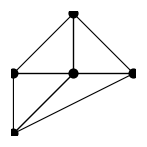

```mathematica
Graphics[{EdgeForm[Black],FaceForm[],Polygon@Take[fanGen,-4], Line/@Thread[{Take[fanGen,-4], First[fanGen]}, List, 1], PointSize[.05],Point@fanGen}]
```

```mathematica
fanV = ArrayPad[fanGen, {{0,0}, {0,1}}, 1]
```

{{0,0,1},{1,0,1},{-1,-1,1},{-1,0,1},{0,1,1}}

```mathematica
Solve[Thread[fanVᵀ.Array[a,5]==0], Array[a,5], Integers]
fanQ = Array[a,5]/.First[%]/.{{C[1]->-2,C[2]->1},{C[1]->-1,C[2]->0}}
fanVQ = Join[fanVᵀ, %]ᵀ;
fanVQ//MatrixForm
```

{{a[1]→ConditionalExpression[C[1], (C[1]|C[2])∈ℤ],a[2]→ConditionalExpression[C[2], (C[1]|C[2])∈ℤ],a[3]→ConditionalExpression[-C[1]-2 C[2], (C[1]|C[2])∈ℤ],a[4]→ConditionalExpression[C[1]+3 C[2], (C[1]|C[2])∈ℤ],a[5]→ConditionalExpression[-C[1]-2 C[2], (C[1]|C[2])∈ℤ]}}

{{-2,1,0,1,0},{-1,0,1,-1,1}}

(0 | 0 | 1 | -2 | -1
1 | 0 | 1 | 1 | 0
-1 | -1 | 1 | 0 | 1
-1 | 0 | 1 | 1 | -1
0 | 1 | 1 | 0 | 1)

```mathematica
CSMDef = Thread[Array[z,Length[fanQ]]->Table[Product[a[i]^fanQ[[A, i]], {i,1,5}], {A, 1, Length[fanQ]}]]
```

{z[1]→(a[2] a[4])/a[1]^2,z[2]→(a[3] a[5])/(a[1] a[4])}

```mathematica
H[X_,Y_]=Sum[a[i]X^fanVQ[[i,1]]Y^fanVQ[[i,2]], {i,Length[fanVQ]}]
```

a[1]+X a[2]+a[3]/(X Y)+a[4]/X+Y a[5]

```mathematica
H[X,Y]/a[1]/.{X->xc X, Y->yc Y}//Expand
H1[X_,Y_]=%/.{xc->a[1]/a[2], yc->a[1]/a[5]}/.{(a[2] a[4])/a[1]^2->z[1],(a[3] a[5])/(a[1] a[4])->z[2]}/.{(a[2] a[3] a[5])/a[1]^3->z[1]z[2]}
```

1+(X xc a[2])/a[1]+a[3]/(X xc Y yc a[1])+a[4]/(X xc a[1])+(Y yc a[5])/a[1]

1+X+Y+z[1]/X+(z[1] z[2])/(X Y)

```mathematica
-1/u H1[X,Y]/.{z[1]->m u^2,z[2]->-u/m}
Expand[%/.{X->-u x,Y->-u y}]
```

-(1+(m u^2)/X+X-u^3/(X Y)+Y)/u

-1/u+m/x+x+1/(x y)+y

```mathematica
MirrorCurve[x,y,m,u]
```

-1/u+m/x+x+1/(x y)+y

## Periods from gamma soln

```mathematica
Gamma/@(fanQᵀ.{n1+r1,n2+r2}+1)
expr1 = z1^(n1+r1) z2^(n2+r2)/Times@@%
expr2 = %/.{Gamma[1-n2-2 (n1+r1)-r2]->Pi (n2+2 (n1+r1)+r2)/Sin[Pi (n2+2 (n1+r1)+r2)]/Gamma[1+n2+2 (n1+r1)+r2]}
```

{Gamma[1-n2-2 (n1+r1)-r2],Gamma[1+n1+r1],Gamma[1+n2+r2],Gamma[1+n1-n2+r1-r2],Gamma[1+n2+r2]}

(z1^(n1+r1) z2^(n2+r2))/(Gamma[1+n1+r1] Gamma[1+n1-n2+r1-r2] Gamma[1-n2-2 (n1+r1)-r2] Gamma[1+n2+r2]^2)

(z1^(n1+r1) z2^(n2+r2) Gamma[1+n2+2 (n1+r1)+r2] Sin[π (n2+2 (n1+r1)+r2)])/(π (n2+2 (n1+r1)+r2) Gamma[1+n1+r1] Gamma[1+n1-n2+r1-r2] Gamma[1+n2+r2]^2)

```mathematica
Simplify[D[expr1, r1]/.{r1->0,r2->0}]
Limit[%, {n1,n2}->{0,0}]
```

(z1^n1 z2^n2 (Log[z1]-PolyGamma[0,1+n1]+2 PolyGamma[0,1-2 n1-n2]-PolyGamma[0,1+n1-n2]))/(Gamma[1+n1] Gamma[1-2 n1-n2] Gamma[1+n1-n2] Gamma[1+n2]^2)

Log[z1]

```mathematica
Simplify[D[expr2, r1]/.{r1->0,r2->0}]
Limit[%, {n1->0,n2->0}]
```

(z1^n1 z2^n2 Gamma[1+2 n1+n2] (4 n1 π Cos[(2 n1+n2) π]+2 n2 π Cos[(2 n1+n2) π]-2 Sin[(2 n1+n2) π]+2 n1 Log[z1] Sin[(2 n1+n2) π]+n2 Log[z1] Sin[(2 n1+n2) π]-(2 n1+n2) PolyGamma[0,1+n1] Sin[(2 n1+n2) π]-(2 n1+n2) PolyGamma[0,1+n1-n2] Sin[(2 n1+n2) π]+4 n1 PolyGamma[0,1+2 n1+n2] Sin[(2 n1+n2) π]+2 n2 PolyGamma[0,1+2 n1+n2] Sin[(2 n1+n2) π]))/((2 n1+n2)^2 π Gamma[1+n1] Gamma[1+n1-n2] Gamma[1+n2]^2)

Log[z1]

```mathematica
Simplify[D[expr1, r1]/.{r1->0,r2->0}]
Assuming[{nn1<nn2,(nn1|nn2)∈NonNegativeIntegers}, Simplify[Limit[%, {n1,n2}->{nn1,nn2}]]]
```

(z1^n1 z2^n2 (Log[z1]-PolyGamma[0,1+n1]+2 PolyGamma[0,1-2 n1-n2]-PolyGamma[0,1+n1-n2]))/(Gamma[1+n1] Gamma[1-2 n1-n2] Gamma[1+n1-n2] Gamma[1+n2]^2)

0

```mathematica
Simplify[D[expr1, r1]/.{r1->0,r2->0}]
Assuming[{nn1>=nn2,(nn1|nn2)∈NonNegativeIntegers}, Simplify[Limit[%, {n1,n2}->{nn1,nn2}]]]/.{nn1->n1,nn2->n2}
```

(z1^n1 z2^n2 (Log[z1]-PolyGamma[0,1+n1]+2 PolyGamma[0,1-2 n1-n2]-PolyGamma[0,1+n1-n2]))/(Gamma[1+n1] Gamma[1-2 n1-n2] Gamma[1+n1-n2] Gamma[1+n2]^2)

ConditionalExpression[(z1^n1 z2^n2 (Log[z1]-PolyGamma[0,1+n1]+2 PolyGamma[0,1-2 n1-n2]-PolyGamma[0,1+n1-n2]))/(Gamma[1+n1] Gamma[1-2 n1-n2] Gamma[1+n1-n2] Gamma[1+n2]^2), 2 n1+n2<1]

```mathematica
Simplify[D[expr2, r1]/.{r1->0,r2->0}]
Assuming[{nn1>=nn2,(nn1|nn2)∈NonNegativeIntegers}, Simplify[Limit[%, {n1,n2}->{nn1,nn2}]]]/.{nn1->n1,nn2->n2}
```

(z1^n1 z2^n2 Gamma[1+2 n1+n2] (4 n1 π Cos[(2 n1+n2) π]+2 n2 π Cos[(2 n1+n2) π]-2 Sin[(2 n1+n2) π]+2 n1 Log[z1] Sin[(2 n1+n2) π]+n2 Log[z1] Sin[(2 n1+n2) π]-(2 n1+n2) PolyGamma[0,1+n1] Sin[(2 n1+n2) π]-(2 n1+n2) PolyGamma[0,1+n1-n2] Sin[(2 n1+n2) π]+4 n1 PolyGamma[0,1+2 n1+n2] Sin[(2 n1+n2) π]+2 n2 PolyGamma[0,1+2 n1+n2] Sin[(2 n1+n2) π]))/((2 n1+n2)^2 π Gamma[1+n1] Gamma[1+n1-n2] Gamma[1+n2]^2)

(2 z1^n1 (-z2)^n2 Gamma[1+2 n1+n2])/((2 n1+n2) Gamma[1+n1] Gamma[1+n1-n2] Gamma[1+n2]^2)

```mathematica
vpi1[z1_,z2_,0,0]:=Log[z1];
vpi1[z1_,z2_,n1_Integer,n2_Integer]:=0/;n1<n2;
vpi1[z1_,z2_,n1_Integer,n2_Integer]:=(2 z1^n1 (-z2)^n2 Gamma[1+2 n1+n2])/((2 n1+n2) Gamma[1+n1] Gamma[1+n1-n2] Gamma[1+n2]^2)/;n1>=n2;
```

#### t2?

```mathematica
Simplify[D[expr1, r2]/.{r1->0,r2->0}]
Limit[%, {n1,n2}->{0,0}]
```

(z1^n1 z2^n2 (Log[z2]+PolyGamma[0,1-2 n1-n2]+PolyGamma[0,1+n1-n2]-2 PolyGamma[0,1+n2]))/(Gamma[1+n1] Gamma[1-2 n1-n2] Gamma[1+n1-n2] Gamma[1+n2]^2)

Log[z2]

```mathematica
Simplify[D[expr2, r2]/.{r1->0,r2->0}]
Limit[%, {n1->0,n2->0}]
```

(z1^n1 z2^n2 Gamma[1+2 n1+n2] (2 n1 π Cos[(2 n1+n2) π]+n2 π Cos[(2 n1+n2) π]-Sin[(2 n1+n2) π]+2 n1 Log[z2] Sin[(2 n1+n2) π]+n2 Log[z2] Sin[(2 n1+n2) π]+(2 n1+n2) PolyGamma[0,1+n1-n2] Sin[(2 n1+n2) π]-2 (2 n1+n2) PolyGamma[0,1+n2] Sin[(2 n1+n2) π]+2 n1 PolyGamma[0,1+2 n1+n2] Sin[(2 n1+n2) π]+n2 PolyGamma[0,1+2 n1+n2] Sin[(2 n1+n2) π]))/((2 n1+n2)^2 π Gamma[1+n1] Gamma[1+n1-n2] Gamma[1+n2]^2)

Log[z2]

```mathematica
Simplify[D[expr1, r2]/.{r1->0,r2->0}]
Assuming[{nn1<nn2,(nn1|nn2)∈NonNegativeIntegers}, Simplify[Limit[%, {n1,n2}->{nn1,nn2}]]]
```

(z1^n1 z2^n2 (Log[z2]+PolyGamma[0,1-2 n1-n2]+PolyGamma[0,1+n1-n2]-2 PolyGamma[0,1+n2]))/(Gamma[1+n1] Gamma[1-2 n1-n2] Gamma[1+n1-n2] Gamma[1+n2]^2)

0

```mathematica
Simplify[D[expr2, r2]/.{r1->0,r2->0}]
Assuming[{nn1>=nn2,(nn1|nn2)∈NonNegativeIntegers}, Simplify[Limit[%, {n1,n2}->{nn1,nn2}]]]/.{nn1->n1,nn2->n2}
```

(z1^n1 z2^n2 Gamma[1+2 n1+n2] (2 n1 π Cos[(2 n1+n2) π]+n2 π Cos[(2 n1+n2) π]-Sin[(2 n1+n2) π]+2 n1 Log[z2] Sin[(2 n1+n2) π]+n2 Log[z2] Sin[(2 n1+n2) π]+(2 n1+n2) PolyGamma[0,1+n1-n2] Sin[(2 n1+n2) π]-2 (2 n1+n2) PolyGamma[0,1+n2] Sin[(2 n1+n2) π]+2 n1 PolyGamma[0,1+2 n1+n2] Sin[(2 n1+n2) π]+n2 PolyGamma[0,1+2 n1+n2] Sin[(2 n1+n2) π]))/((2 n1+n2)^2 π Gamma[1+n1] Gamma[1+n1-n2] Gamma[1+n2]^2)

(z1^n1 (-z2)^n2 Gamma[1+2 n1+n2])/((2 n1+n2) Gamma[1+n1] Gamma[1+n1-n2] Gamma[1+n2]^2)

```mathematica
vpi2[z1_,z2_,0,0]:=Log[z2];
vpi2[z1_,z2_,n1_Integer,n2_Integer]:=0/;n1<n2;
vpi2[z1_,z2_,n1_Integer,n2_Integer]:=(z1^n1 (-z2)^n2 Gamma[1+2 n1+n2])/((2 n1+n2) Gamma[1+n1] Gamma[1+n1-n2] Gamma[1+n2]^2)/;n1>=n2;
```

#### continue

```mathematica
Table[vpi1[z1,z2,n1,n2], {n1,0,3},{n2,0,3}];
Total[%, Infinity]
```

2 z1+3 z1^2+(20 z1^3)/3-4 z1 z2-24 z1^2 z2-120 z1^3 z2+30 z1^2 z2^2+420 z1^3 z2^2-(1120 z1^3 z2^3)/3+Log[z1]

```mathematica
Table[vpi2[z1,z2,n1,n2], {n1,0,3},{n2,0,3}];
Total[%, Infinity]
```

z1+(3 z1^2)/2+(10 z1^3)/3-2 z1 z2-12 z1^2 z2-60 z1^3 z2+15 z1^2 z2^2+210 z1^3 z2^2-(560 z1^3 z2^3)/3+Log[z2]

```mathematica
Table[vpi1[z1,z2,n1,n2]-2vpi2[z1,z2,n1,n2], {n1,0,3},{n2,0,3}];
Total[%, Infinity]
```

Log[z1]-2 Log[z2]

```mathematica
Simplify[D[expr1, {r1,2}]/.{r1->0,r2->0}]
FullSimplify[Limit[%, {n1,n2}->{0,0}]]
```

(z1^n1 z2^n2 (Log[z1]^2+PolyGamma[0,1+n1]^2+4 PolyGamma[0,1-2 n1-n2]^2+4 PolyGamma[0,1-2 n1-n2] (Log[z1]-PolyGamma[0,1+n1-n2])-2 PolyGamma[0,1+n1] (Log[z1]+2 PolyGamma[0,1-2 n1-n2]-PolyGamma[0,1+n1-n2])-2 Log[z1] PolyGamma[0,1+n1-n2]+PolyGamma[0,1+n1-n2]^2-PolyGamma[1,1+n1]-4 PolyGamma[1,1-2 n1-n2]-PolyGamma[1,1+n1-n2]))/(Gamma[1+n1] Gamma[1-2 n1-n2] Gamma[1+n1-n2] Gamma[1+n2]^2)

-π^2+Log[z1]^2

```mathematica
Simplify[D[expr1, {r1,2}]/.{r1->0,r2->0}]
Assuming[{nn1<nn2,(nn1|nn2)∈NonNegativeIntegers}, Simplify[Limit[%, {n1,n2}->{nn1,nn2}]]]
```

(z1^n1 z2^n2 (Log[z1]^2+PolyGamma[0,1+n1]^2+4 PolyGamma[0,1-2 n1-n2]^2+4 PolyGamma[0,1-2 n1-n2] (Log[z1]-PolyGamma[0,1+n1-n2])-2 PolyGamma[0,1+n1] (Log[z1]+2 PolyGamma[0,1-2 n1-n2]-PolyGamma[0,1+n1-n2])-2 Log[z1] PolyGamma[0,1+n1-n2]+PolyGamma[0,1+n1-n2]^2-PolyGamma[1,1+n1]-4 PolyGamma[1,1-2 n1-n2]-PolyGamma[1,1+n1-n2]))/(Gamma[1+n1] Gamma[1-2 n1-n2] Gamma[1+n1-n2] Gamma[1+n2]^2)

$Aborted

```mathematica
Simplify[D[expr1, {r1,2}]/.{r1->0,r2->0}]
Assuming[{nn1>=nn2,2nn1+nn2>=1,(nn1|nn2)∈NonNegativeIntegers}, Simplify[Limit[%, {n1,n2}->{nn1,nn2}]]]/.{nn1->n1,nn2->n2}
```

(z1^n1 z2^n2 (Log[z1]^2+PolyGamma[0,1+n1]^2+4 PolyGamma[0,1-2 n1-n2]^2+4 PolyGamma[0,1-2 n1-n2] (Log[z1]-PolyGamma[0,1+n1-n2])-2 PolyGamma[0,1+n1] (Log[z1]+2 PolyGamma[0,1-2 n1-n2]-PolyGamma[0,1+n1-n2])-2 Log[z1] PolyGamma[0,1+n1-n2]+PolyGamma[0,1+n1-n2]^2-PolyGamma[1,1+n1]-4 PolyGamma[1,1-2 n1-n2]-PolyGamma[1,1+n1-n2]))/(Gamma[1+n1] Gamma[1-2 n1-n2] Gamma[1+n1-n2] Gamma[1+n2]^2)

-((4 z1^n1 (-z2)^n2 (-1+2 n1+n2)! (2 EulerGamma-2 HarmonicNumber[-1+2 n1+n2]-Log[z1]+PolyGamma[0,1+n1]+PolyGamma[0,1+n1-n2]))/(Gamma[1+n1] Gamma[1+n1-n2] Gamma[1+n2]^2))

```mathematica
Simplify[D[expr2, {r1,2}]/.{r1->0,r2->0}]
Assuming[{nn1>=nn2,2nn1+nn2<1,(nn1|nn2)∈NonNegativeIntegers}, FullSimplify[Limit[%, {n1,n2}->{nn1,nn2}]]]/.{nn1->n1,nn2->n2}
```

(z1^n1 z2^n2 Gamma[1+2 n1+n2] ((8-4 (2 n1+n2) Log[z1]+(2 n1+n2)^2 Log[z1]^2+2 (2 n1+n2) (2-(2 n1+n2) Log[z1]) PolyGamma[0,1+n1]+(2 n1+n2)^2 (PolyGamma[0,1+n1]^2-PolyGamma[1,1+n1])) Sin[(2 n1+n2) π]+2 (2 n1+n2) (-2+(2 n1+n2) Log[z1]-(2 n1+n2) PolyGamma[0,1+n1]) (2 π Cos[(2 n1+n2) π]-PolyGamma[0,1+n1-n2] Sin[(2 n1+n2) π]+2 PolyGamma[0,1+2 n1+n2] Sin[(2 n1+n2) π])-(2 n1+n2)^2 (-8 π Cos[(2 n1+n2) π] PolyGamma[0,1+2 n1+n2]-PolyGamma[0,1+n1-n2]^2 Sin[(2 n1+n2) π]-4 PolyGamma[0,1+2 n1+n2]^2 Sin[(2 n1+n2) π]+(4 π^2+PolyGamma[1,1+n1-n2]-4 PolyGamma[1,1+2 n1+n2]) Sin[(2 n1+n2) π]+4 PolyGamma[0,1+n1-n2] (π Cos[(2 n1+n2) π]+PolyGamma[0,1+2 n1+n2] Sin[(2 n1+n2) π]))))/((2 n1+n2)^3 π Gamma[1+n1] Gamma[1+n1-n2] Gamma[1+n2]^2)

```mathematica
expr3 = FullSimplify[D[expr1, {r1,2}]/.{r1->0,r2->0}]
```

(z1^n1 z2^n2 ((HarmonicNumber[n1]-2 HarmonicNumber[-2 n1-n2]+HarmonicNumber[n1-n2]-Log[z1])^2-PolyGamma[1,1+n1]-4 PolyGamma[1,1-2 n1-n2]-PolyGamma[1,1+n1-n2]))/(Gamma[1+n1] Gamma[1-2 n1-n2] Gamma[1+n1-n2] Gamma[1+n2]^2)

```mathematica
expr4 = D[expr2, {r1,2}]/.{r1->0,r2->0};
```

```mathematica
Limit[expr4,{n1->0,n2->0}]//FullSimplify
```

-π^2+Log[z1]^2

```mathematica
Table[Simplify[Limit[expr3,{n1->N1,n2->N2}]], {N1,0,3},{N2,0,3}]//MatrixForm
```

(-π^2+Log[z1]^2 | -4 z2 | -z2^2 | -(4 z2^3)/9
4 z1 Log[z1] | -8 z1 z2 (2+Log[z1]) | 6 z1 z2^2 | (8 z1 z2^3)/3
2 z1^2 (2+3 Log[z1]) | -16 z1^2 z2 (5+3 Log[z1]) | 4 z1^2 z2^2 (46+15 Log[z1]) | -40 z1^2 z2^3
4/3 z1^3 (9+10 Log[z1]) | -8 z1^3 z2 (47+30 Log[z1]) | 8 z1^3 z2^2 (247+105 Log[z1]) | -16/9 z1^3 z2^3 (1513+420 Log[z1]))

### Picard Fuchs

```mathematica
PF1[f_,z1_,z2_]:=z1 D[z1 D[f, z1]-z2 D[f, z2], z1]-z1 (2z1 D[f + 2 z1 D[f, z1] + z2 D[f, z2], z1]+z2 D[f + 2 z1 D[f, z1] +  z2 D[f, z2], z2]);
```

```mathematica
PF2[f_,z1_,z2_]:=z2 D[z2 D[f, z2], z2]-z2 (z2 D[2 z1 D[f, z1] + z2 D[f, z2], z2]-z1 D[2 z1 D[f, z1] + z2 D[f, z2], z1]);
```

```mathematica
PF1[z1^2+z2^2,z1,z2]
```

4 z1^2-z1 (20 z1^2+10 z2^2)

```mathematica
Series[Sum[vpi1[z1,z2,n1,n2], {n1,0,10},{n2,0,10}], {z1,0,10},{z2,0,10}];
Simplify[z2 D[%, z2]];
PF1[%,z1,z2]//Simplify
```

O[z1]^11

```mathematica
PF2[z1 D[f[(z1 z2)^(-1/3),(z1/z2^2)^(1/3)],z1],z1,z2]/.{z1->lam/ut^2, z2->1/ut/lam}//PowerExpand//FullSimplify
```

1/27 (4 lam f^(0,1)[ut,lam]+12 lam^2 f^(0,2)[ut,lam]+4 lam^3 f^(0,3)[ut,lam]-ut f^(1,0)[ut,lam]-3 lam ut f^(1,1)[ut,lam]-9 lam f^(1,2)[ut,lam]-3 ut^2 f^(2,0)[ut,lam]+9 ut f^(2,1)[ut,lam]-3 lam ut^2 f^(2,1)[ut,lam]-ut^3 f^(3,0)[ut,lam])

```mathematica
PF1[z2 D[f[(z1 z2)^(-1/3),(z1/z2^2)^(1/3)],z2],z1,z2]/.{z1->lam/ut^2, z2->1/ut/lam}//PowerExpand//FullSimplify
```

1/9 lam (-2 f^(0,1)[ut,lam]-6 lam f^(0,2)[ut,lam]-2 lam^2 f^(0,3)[ut,lam]+2 ut f^(1,1)[ut,lam]+lam ut f^(1,2)[ut,lam]+6 f^(2,0)[ut,lam]+6 lam f^(2,1)[ut,lam]+ut^2 f^(2,1)[ut,lam]+3 ut f^(3,0)[ut,lam])

```mathematica
9 PF2[f[(z1 z2)^(-1/3),(z1/z2^2)^(1/3)],z1,z2]/.{z1->lam/ut^2, z2->1/ut/lam}//PowerExpand//FullSimplify
%//Expand
```

ut f^(1,0)[ut,lam]-9 f^(1,1)[ut,lam]+4 lam (f^(0,1)[ut,lam]+lam f^(0,2)[ut,lam]+ut f^(1,1)[ut,lam])+ut^2 f^(2,0)[ut,lam]

4 lam f^(0,1)[ut,lam]+4 lam^2 f^(0,2)[ut,lam]+ut f^(1,0)[ut,lam]-9 f^(1,1)[ut,lam]+4 lam ut f^(1,1)[ut,lam]+ut^2 f^(2,0)[ut,lam]

## Numerical checks

```mathematica
(* varpi2 with Richardson *)
varpi2[u_,lam_]:=With[{Nn=1024, d=15}, Module[{terms,sums}, 
terms=Table[Sum[If[Mod[n-2l, 3]==0, (n-1)!/Factorial[(n-2l)/3]^2/Factorial[l]/Factorial[(n+l)/3] lam^l, 0], {l,0,n}]u^n, {n, 2, Nn}];
sums=-Log[u]-Accumulate[terms];
Table[Sum[sums[[n+k]](n+k)^d(-1)^(k+d)/k!/(d-k)!, {k, 0, d}], {n, 1, Length[sums]-d}]
]];
```

```mathematica
(* varpi3 with Richardson *)
varpi3[z_,lam_]:=With[{Nn=200, d=5}, Module[{terms,sums}, 
terms=Table[Sum[(2n)!/n/Factorial[n-l]^2/Factorial[l]^2(HarmonicNumber[n-l]+HarmonicNumber[l]-2HarmonicNumber[2n]+1/n) lam^l, {l,0,n}]z^n, {n, 1, Nn}];
sums=-Log[z]^2+(2Log[z]+Log[lam])Last[varpi2[z,lam]]-2Accumulate[terms];
Table[Sum[sums[[n+k]](n+k)^d(-1)^(k+d)/k!/(d-k)!, {k, 0, d}], {n, 1, Length[sums]-d}]
]];
```

```mathematica
u0 = First@SortBy[u/.Solve[m+u-8 m^2 u^2-36 m u^3-27 u^4+16 m^3 u^4==0/.{m->2}, u, WorkingPrecision->300], Abs]
```

0.227203634857985759161254765346706290384224015255178461093477420691304642267091217742189796411130923115944638285781096295310110730752078711791964944775615339522431160058805630903139642604728284338325494815447595924727522181455304313717828188321139203654575906882416423394662141575571995897076683668046

```mathematica
target=1.1573221007466653124323507573331906
```

1.157322100746665312432350757333191

```mathematica
1.271036692098228453117342
```

```mathematica
Last@varpi2[u0, N[2,300]]
```

1.271036692098228453117342128887728881141326216177305025262608167072939021033408471101716154596023394884084687961317683553858664268272421469174377605909422062516151427111375217763095564157298455233666971842732642885922422955025994501096701002268498533211126023272

```mathematica
m+u-8 m^2 u^2-36 m u^3-27 u^4+16 m^3 u^4/.{u->-1/u, m->lam}//Simplify//Together
```

(-27+16 lam^3+36 lam u-8 lam^2 u^2-u^3+lam u^4)/u^4

```mathematica
1728g2^3/(g2^3-27g3^2)//FullSimplify
eqn = %-j//Simplify//Together//Numerator//Simplify
```

((1+8 u^2 (-3 u+m (-1+2 m u^2)))^3)/(u^8 (m+u-8 m^2 u^2-36 m u^3+(-27+16 m^3) u^4))

1-72 u^3+1728 u^6-(13824+j) u^9-6144 m^5 u^10+27 j u^12+4096 m^6 u^12-768 m^4 u^8 (-5+24 u^3)-16 m^3 u^6 (80-1152 u^3+j u^6)+8 m^2 u^4 (30-864 u^3+(3456+j) u^6)+m u^2 (-24+1152 u^3-(13824+j) u^6+36 j u^9)

```mathematica
Discriminant[eqn, u]//FullSimplify
```

(-1728+j)^6 j^8 (27+256 m^3)^3 (-387420489-1024 m^3 (4782969+128 m^3 (98415+128 m^3 (756-j+256 m^3))))

```mathematica
Expand[(-387420489-1024 m^3 (4782969+128 m^3 (98415+128 m^3 (756-j+256 m^3))))]+((27+256m^3)(243+256m^3)^3-2^24j m^9)//Simplify
```

0

```mathematica
A1/.{b->}/.BWEval
```

1/(2 π)(Im[PolyLog[2,b^3]]+5 (Im[PolyLog[2,b]]+Arg[1-b] Log[Abs[b]])-4 (Im[PolyLog[2,b^2]]+Arg[1-b^2] Log[Abs[b]^2])+Arg[1-b^3] Log[Abs[b]^3])

```mathematica
uvals[N[1,30]]
```

{{u→0.26318526921874357906535706028},{u→-0.2550986687263150511885485324-0.2215528143588283005513899855 ⅈ},{u→-0.2550986687263150511885485324+0.2215528143588283005513899855 ⅈ},{u→-3.025715204493386203960987268}}

```mathematica
With[{m=N[1,30]},{m,u/.uvals[m][[1]]}]
{Solve[(m/.sol[[4]])==%[[1]], t1],Solve[(u/.sol[[4]])==%[[2]], t1]}
```

{1.,0.26318526921874357906535706028}

$Aborted

```mathematica
sol[[4]]
```

{m→(3 (-1/2)^(1/3) (-1+t1) (-((-3+t1) t1^2))^(1/3))/(2 t1^2),u→-1/3 (-1/2)^(1/3) (-((-3+t1) t1^2))^(1/3)}

```mathematica
sol[[2]]
```

{m→(3 (1+t1) (3+t1)^(1/3))/(2 2^(1/3) t1^(4/3)),u→(t1^(2/3) (3+t1)^(1/3))/(3 2^(1/3))}

```mathematica
b/.bTot1/.{}
```

(t1-√6 √X0)/(t1+√6 √X0)

```mathematica
delt[m,u]
```

m+u-8 m^2 u^2-36 m u^3-27 u^4+16 m^3 u^4

```mathematica
X0sol
```

{X0→(3 (1-8 m u^2-32 u^3+16 m^2 u^4+108 u^6))/(2 (1-8 m u^2-24 u^3+16 m^2 u^4))}

```mathematica
Solve[-3+t^2+12 m u^2-4 X0==0, t]
```

{{t→-√(3-12 m u^2+4 X0)},{t→√(3-12 m u^2+4 X0)}}

```mathematica
FullSimplify@Together[3-12 m u^2+4 X0/.X0sol]
FullSimplify[%, delt[m,u]==0]
```

(3 (3-28 m u^2-88 u^3+80 m^2 u^4+96 m u^5+8 (27-8 m^3) u^6))/(1+8 u^2 (-3 u+m (-1+2 m u^2)))

(9+36 u^2 (-2 m-7 u+4 m^2 u^2-4 m u^3+9 u^4))/(1+8 u^2 (-3 u+m (-1+2 m u^2)))

```mathematica
delt[m,u]
```

m+u-8 m^2 u^2-36 m u^3-27 u^4+16 m^3 u^4

```mathematica
t1sq=(9+36 u^2 (-2 m-7 u+4 m^2 u^2-4 m u^3+9 u^4))/(1+8 u^2 (-3 u+m (-1+2 m u^2)));
```

```mathematica
sol2 = Assuming[t1>0, Simplify@Solve[{(9+36 u^2 (-2 m-7 u+4 m^2 u^2-4 m u^3+9 u^4))/(1+8 u^2 (-3 u+m (-1+2 m u^2)))==t1^2, m+u-8 m^2 u^2-36 m u^3-27 u^4+16 m^3 u^4==0}, {m,u}]]
```

{{m→-(3 (-3-t1)^(1/3) (1+t1))/(2 2^(1/3) t1^(4/3)),u→-1/3 (-1/2)^(1/3) t1^(2/3) (3+t1)^(1/3)},{m→(3 (1+t1) (3+t1)^(1/3))/(2 2^(1/3) t1^(4/3)),u→((t1^2 (3+t1))^(1/3))/(3 2^(1/3))},{m→(3 (-1)^(2/3) (1+t1) (3+t1)^(1/3))/(2 2^(1/3) t1^(4/3)),u→((-t1)^(2/3) (3+t1)^(1/3))/(3 2^(1/3))},{m→(3 (-1/2)^(1/3) (3-t1)^(1/3) (-1+t1))/(2 t1^(4/3)),u→-1/3 (-1/2)^(1/3) (-((-3+t1) t1^2))^(1/3)},{m→-(3 (3-t1)^(1/3) (-1+t1))/(2 2^(1/3) t1^(4/3)),u→((-((-3+t1) t1^2))^(1/3))/(3 2^(1/3))},{m→-(3 (-1)^(2/3) (3-t1)^(1/3) (-1+t1))/(2 2^(1/3) t1^(4/3)),u→((-1)^(2/3) (-((-3+t1) t1^2))^(1/3))/(3 2^(1/3))}}

```mathematica
NSolve[(m/.sol2[[1]])==1,t1]
```

{{t1→-0.775755-0.553985 ⅈ},{t1→-0.775755+0.553985 ⅈ},{t1→-0.646782}}

```mathematica
NSolve[(m/.sol2[[2]])==1,t1]
```

{{t1→-12.529}}

```mathematica
NSolve[(m/.sol2[[3]])==1,t1]
```

{{t1→-0.775755+0.553985 ⅈ}}

```mathematica
NSolve[(m/.#)==1,t1]&/@sol2
Flatten[t1/.%]//DeleteDuplicates
```

{{{t1→-0.775755-0.553985 ⅈ},{t1→-0.775755+0.553985 ⅈ},{t1→-0.646782}},{{t1→-12.529}},{{t1→-0.775755+0.553985 ⅈ}},{{t1→0.775755-0.553985 ⅈ}},{{t1→0.646782}},{{t1→12.529},{t1→0.775755+0.553985 ⅈ}}}

{-0.775755-0.553985 ⅈ,-0.775755+0.553985 ⅈ,-0.646782,-12.529,-0.775755+0.553985 ⅈ,0.775755-0.553985 ⅈ,0.646782,12.529,0.775755+0.553985 ⅈ}

```mathematica
With[{m=N[1,20]},-2+Sqrt[1+12m Echo[First[(u/.uvals[m])]]^2]]
```

0.2631852692187435791

-0.6467824154242931072

```mathematica
First[sol2]/.{t1->-0.64678241542429310724842125241159423282`19.373077221607886}
```

{m→1.+0. ⅈ,u→0.2631852692187435791+0. ⅈ}

```mathematica
FullSimplify[delt[m,u]/.sol2[[1]],-3<t1<0]
```

0

```mathematica
FullSimplify[t1sq/.sol2[[1]],-3<t1<0]
```

t1^2

```mathematica
FullSimplify[X0/.X0sol/.sol2[[1]],-3<t1<0]//Expand
```

t1+t1^2/2

```mathematica
FullSimplify[b/.bTot1/.{X0->t1+t1^2/2}, -3<t1<0]
Solve[%==b,t1]
m/.sol2[[1]]/.First[%]//FullSimplify
```

(-3-2 t1+√3 √(t1 (2+t1)))/(3+t1)

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

{{t1→-(3 (1+2 b+b^2))/(1+4 b+b^2)}}

-((1+b+b^2) (-b/(1+b (4+b)))^(1/3))/((1+b)^2 (-1+(2 b)/(1+b (4+b)))^(1/3))

```mathematica
FunctionRange[{(-3-2 t1+√3 √(t1 (2+t1)))/(3+t1), -3<t1<0},t1,b, Reals]
```

b≥1

```mathematica
FunctionRange[{1/2t1^2+t1, -3<t1<0},t1,X0]
```

-1/2≤X0<3/2

```mathematica
Limit[pxy2, z->0]/.{X0->1/2t1^2+t1}/.sol2[[1]]
FullSimplify[%, -3<t1<0]
```

{((-1/2)^(2/3) (-3-2 t1-√6 √(t1+t1^2/2)) (-t1+√6 √(t1+t1^2/2)))/(t1^(2/3) (3+t1)^(1/3) (-t1-√6 √(t1+t1^2/2))),(2 (-1)^(2/3) 2^(1/3) t1^(4/3) (3+t1)^(2/3))/(t1^2-6 (t1+t1^2/2))}

{(-1/2)^(2/3)/(t1/(3+t1))^(2/3),2^(1/3) (-t1/(3+t1))^(1/3)}

```mathematica
m/.sol2[[1]]
```

-(3 (-3-t1)^(1/3) (1+t1))/(2 2^(1/3) t1^(4/3))

```mathematica
FunctionRange[{-1/3 (-1/2)^(1/3) t1^(2/3) (3+t1)^(1/3), -3<t1<0}, t1, x]
```

False

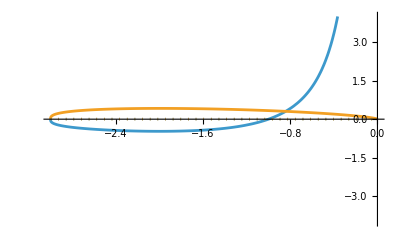

```mathematica
ReImPlot[{-(3 (-3-t1)^(1/3) (1+t1))/(2 2^(1/3) t1^(4/3)),-1/3 (-1/2)^(1/3) t1^(2/3) (3+t1)^(1/3)}, {t1,-3,0},
PlotRange->{Automatic, {-4, 4}}
]
```

```mathematica
-(3 (-3-t1)^(1/3) (1+t1))/(2 2^(1/3) t1^(4/3))/.{t1->-2}//N
```

-0.47247

```mathematica
tudata = Table[{-2+Sqrt[1+12 m (u/.First[uvals[m]])^2], u/.First[uvals[m]]}, {m, -3/(4 2^(2/3)), 10, .01}];
```

```mathematica
tudatareal = Select[tudata, FreeQ[#,Complex]&];
```

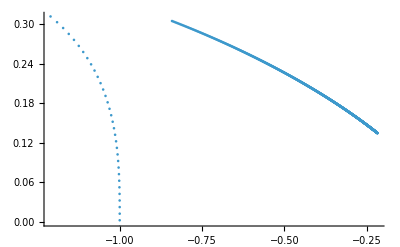

```mathematica
ListPlot[tudatareal]
```

```mathematica
bTot1
```

{b→(t1-√6 √X0)/(t1+√6 √X0)}

```mathematica
First[u/.uvals[1.]]//N
{Sqrt[t1sq],-2+Sqrt[1+12m u^2], 3(4m u^2+18u^3-1)/(12m u^2+1)}/.{m->1,u->%}
t1^2/2+t1/.{t1->Last[%]}
```

0.263185

{0.646782,-0.646782,-0.646782}

-0.437619

```mathematica
First[u/.uvals[1.]]//N
X0/.X0tot1/.{m->1,u->%}/.{t1->-0.6467824154242932}
```

0.263185

-0.437619

```mathematica
With[{m=N[2,40]}, Block[{u0,t1,X0,b},
u0=First@SortBy[ut/.NSolve[delt[m,ut]==0, ut], Abs];
Print["u = ", u0];
t1=-2+Sqrt[1+12m u0^2];
X0=t1^2/2+t1;
b=(t1-√6 √X0)/(t1+√6 √X0);
Print["b = ", b];
b
]];
A1/.{b->%}/.BWEval
```

u = 0.227203634857985759161254765346706290384

b = -0.79822170716314772598004515101171238668+0.60236376568776946837965610457745714968 ⅈ

1.13841093952205567492550624228156048

```mathematica
With[{m=N[1,40]}, Block[{u0,t1,X0,b},
u0=First@SortBy[ut/.NSolve[delt[m,ut]==0, ut], Abs];
Print["u = ", u0];
t1=-2+Sqrt[1+12m u0^2];
X0=t1^2/2+t1;
b=(t1-√6 √X0)/(t1+√6 √X0);
Print["b = ", b];
b
]]
B/.{b->%}/.Li2Eval
```

u = 0.263185269218743579065357060278145251897

b = -0.72514976104901486652756515246368389406+0.68859118789783872858051959055806444226 ⅈ

-0.72514976104901486652756515246368389406+0.68859118789783872858051959055806444226 ⅈ

0.523598775598298873077107230546583814+1.15732210074666531243235075733319062 ⅈ

```mathematica
N[Pi/6,40]
```

0.5235987755982988730771072305465838140329

```mathematica
With[{m=N[1,40]}, Block[{u0,t1,X0,b},
u0=First@SortBy[ut/.NSolve[delt[m,ut]==0, ut], Abs];
Print["u = ", u0];
t1=-2+Sqrt[1+12m u0^2];
X0=t1^2/2+t1;
b=(t1-√6 √X0)/(t1+√6 √X0);
Print["b = ", b];
Chop@Limit[pxy2/.u->u0, z->0]
]]
```

u = 0.263185269218743579065357060278145251897

b = -0.72514976104901486652756515246368389406+0.68859118789783872858051959055806444226 ⅈ

{1.4902161200999536481163868423786267429,0.81917251339616443969957118834242704035}

```mathematica
With[{m=N[1,40]}, Block[{u0,t1,X0,b},
u0=First@SortBy[ut/.NSolve[delt[m,ut]==0, ut], Abs];
Print["u = ", u0];
t1=-2+Sqrt[1+12m u0^2];
X0=t1^2/2+t1;
b=(t1-√6 √X0)/(t1+√6 √X0);
Print["b = ", b];
b
]];
{{1/(2+1/b+b)^(2/3),(2+1/b+b)^(1/3)}}/.{b->%}
```

u = 0.263185269218743579065357060278145251897

b = -0.72514976104901486652756515246368389406+0.68859118789783872858051959055806444226 ⅈ

{{1.490216120099953648116386842378626743+0. ⅈ,0.81917251339616443969957118834242704035+0. ⅈ}}

## Further Numerical checks

```mathematica
mvals=RandomComplex[{-20-20I,20+20I}, 10^5];
```

```mathematica
(*uv = u/.First[uvals[#]]&/@mvals;*)
```

```mathematica
TakeSmallest[{1,2,3}, 1]
```

{1}

```mathematica
RandomComplex[{-20-20I,20+20I}, 1]//AbsoluteTiming
```

{0.00002,{-3.81769-1.71869 ⅈ}}

```mathematica
(First@SortBy[u/.NSolve[delt[#,u]==0,u], Abs])&/@mvals;
```

$Aborted

```mathematica
t1vals=MapThread[-2+Sqrt[1+12#1 #2^2]&, {mvals,uv}];
```

```mathematica
(*ComplexListPlot[mvals]*)
```

```mathematica
(*ComplexListPlot[uv]*)
```

```mathematica
(*ComplexListPlot[t1vals]*)
```

```mathematica
sol100 = Simplify[Solve[delt[m,u]==0,u]];
```

```mathematica
ParametricPlot[ReIm[u/.sol100/.m->N[1,50]Exp[I th]], {th, -Pi,Pi},
PlotPoints->200,
MaxRecursion->5
]
```

```mathematica
mvals=KroneckerProduct[N[Range[2,10,1],50],Exp[I RandomReal[{-Pi,Pi}, 100]]];
```

```mathematica
mvals=N[1,50]Exp[I RandomReal[{-Pi,Pi}, 4000]];
```

```mathematica
uv=Map[u/.NSolve[delt[#,u]==0,u]&, mvals,{-1}];
umin=Table[First@SortBy[u, Abs], {u, uv}];
```

```mathematica
uv//Dimensions
```

{4000,4}

```mathematica
ComplexListPlot[Flatten[mvals],
PlotRange->{{-4,4},{-4,4}},
Epilog->{PointSize[.02],Point[{{3/(8 2^(2/3)),(3 √3)/(8 2^(2/3))},{-3/2^(2/3),(3 √3)/2^(2/3)},{3 2^(1/3),0},{-3/2^(2/3),-(3 √3)/2^(2/3)},{-3/(4 2^(2/3)),0},{3/(8 2^(2/3)),-(3 √3)/(8 2^(2/3))}}]}
]
```

```mathematica
ComplexListPlot[umin]
```

```mathematica
ComplexListPlot[{Flatten[uv],umin},
PlotRange->{{-4,4},{-4,4}},
PlotStyle->{Automatic, Directive[PointSize[.01]]},
Epilog->{Black,PointSize[.01],Point[{{-1/(3 2^(2/3)),-1/(2^(2/3) √3)},{1/(6 2^(2/3)),-1/(2 2^(2/3) √3)},{-1/(3 2^(2/3)),0},{1/(6 2^(2/3)),1/(2 2^(2/3) √3)},{2^(1/3)/3,0},{-1/(3 2^(2/3)),1/(2^(2/3) √3)}}]}
]
```

```mathematica
NSolve[delt[1,u]==0,u]
```

{{u→-3.02572},{u→-0.255099-0.221553 ⅈ},{u→-0.255099+0.221553 ⅈ},{u→0.263185}}

```mathematica
thGrid=Range[-Pi,Pi,.02];
rGrid=Range[0.1,10,.07];
mvals=Flatten@KroneckerProduct[rGrid,Exp[I thGrid]];
uv=Map[u/.NSolve[delt[#,u]==0,u]&, mvals,{-1}];
umin=Table[First@SortBy[u, Abs], {u, uv}];
t1vals=MapThread[-2+Sqrt[1+12#1 #2^2]&, {mvals,umin}];
```

```mathematica
ComplexListPlot[mvals,PlotRange->Full]
```

```mathematica
ComplexListPlot[umin]
```

```mathematica
ComplexListPlot[t1vals
]
```

```mathematica
ComplexListPlot[umin,
PlotRange->Full
]
```

## Check Marcos

```mathematica
MirrorCurve[x,y,m,u]//Expand
```

-1/u+m/x+x+1/(x y)+y

```mathematica
1+X+Y+z[1]/X+(z[1] z[2])/(X Y)/.{z[1]->m/ut^2,z[2]->1/m/ut};
ut^3*%//Expand
```

ut^3+(m ut)/X+ut^3 X+1/(X Y)+ut^3 Y

```mathematica
1+X+Y+z[1]/X+(z[1] z[2])/(X Y)
%/.{z[1]->m u^2,z[2]->u/m}
%/u^3//Expand
```

1+X+Y+z[1]/X+(z[1] z[2])/(X Y)

1+(m u^2)/X+X+u^3/(X Y)+Y

1/u^3+m/(u X)+X/u^3+1/(X Y)+Y/u^3

```mathematica
(x^2 y + x y^2 + x y + z1 y + z2 x^2)/(x y)//Expand
```

1+x+y+z1/x+(x z2)/y

```mathematica
(1+X+Y+z[1]/X+(z[1] z[2])/(X Y))X Y//Expand
```

X Y+X^2 Y+X Y^2+Y z[1]+z[1] z[2]

## Picard Fuchs equations

#### Baby case: local P2

```mathematica
fanGen={{0,0},{1,0},{0,1},{-1,-1}};
```

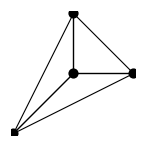

```mathematica
Graphics[{EdgeForm[Black],FaceForm[],Polygon@Take[fanGen,-Length[fanGen]+1], Line/@Thread[{Take[fanGen,-4], First[fanGen]}, List, 1], PointSize[.05],Point@fanGen}]
```

```mathematica
fanV = ArrayPad[fanGen, {{0,0}, {0,1}}, 1]
```

{{0,0,1},{1,0,1},{0,1,1},{-1,-1,1}}

```mathematica
Solve[Thread[fanVᵀ.Array[a,Length[fanGen]]==0], Array[a,Length[fanGen]], Integers]
fanQ = Array[a,Length[fanGen]]/.First[%]/.{{C[1]->-1}}
fanVQ = Join[fanVᵀ, %]ᵀ;
fanVQ//MatrixForm
```

{{a[1]→ConditionalExpression[3 C[1], C[1]∈ℤ],a[2]→ConditionalExpression[-C[1], C[1]∈ℤ],a[3]→ConditionalExpression[-C[1], C[1]∈ℤ],a[4]→ConditionalExpression[-C[1], C[1]∈ℤ]}}

{{-3,1,1,1}}

(0 | 0 | 1 | -3
1 | 0 | 1 | 1
0 | 1 | 1 | 1
-1 | -1 | 1 | 1)

```mathematica
CSMDef = Thread[Array[z,Length[fanQ]]->Table[Product[a[i]^fanQ[[A, i]], {i,Length[fanGen]}], {A, 1, Length[fanQ]}]]
```

{z[1]→(a[2] a[3] a[4])/a[1]^3}

```mathematica
H[X_,Y_]=Sum[a[i]X^fanVQ[[i,1]]Y^fanVQ[[i,2]], {i,Length[fanVQ]}]
```

a[1]+X a[2]+Y a[3]+a[4]/(X Y)

```mathematica
H[X,Y]/a[1]/.{X->xc X, Y->yc Y}//Expand
H1[X_,Y_]=%/.{xc->a[1]/a[2], yc->a[1]/a[3]}/.{(a[2] a[3] a[4])/a[1]^3->z}
```

1+(X xc a[2])/a[1]+(Y yc a[3])/a[1]+a[4]/(X xc Y yc a[1])

1+X+Y+z/(X Y)

## LV Scattering Diagram

```mathematica
ZLV[{r,dF,dB,ch2},T,m]
```

-ch2+dF m+(m^2 r)/2+2 dF T-m r T-4 r T^2+dB (-m+T)

```mathematica
(* Re(e^{-i psi} Z) *)
Simplify@ComplexExpand[1/4/r Re[Exp[-I psi]ZLV[{r,dF,dB,ch2},s+I t,m1+I m2]]]
Simplify[Series[%/.{s->l s,t->l t},{l,0,5}]]
A1=Normal[%]/.{l->1}
```

1/(8 r)((-2 ch2-2 dB m1+2 dF m1+m1^2 r-m2^2 r+2 dB s+4 dF s-2 m1 r s-8 r s^2+2 m2 r t+8 r t^2) Cos[psi]+2 (m1 r (m2-t)+dB (-m2+t)+dF (m2+2 t)-r s (m2+8 t)) Sin[psi])

((-2 ch2-2 dB m1+2 dF m1+m1^2 r-m2^2 r) Cos[psi]+2 m2 (-dB+dF+m1 r) Sin[psi])/(8 r)+(((dB s+2 dF s-m1 r s+m2 r t) Cos[psi]+(-m2 r s+(dB+2 dF-m1 r) t) Sin[psi]) l)/(4 r)+((-s^2+t^2) Cos[psi]-2 s t Sin[psi]) l^2+O[l]^6

(-s^2+t^2) Cos[psi]-2 s t Sin[psi]+((-2 ch2-2 dB m1+2 dF m1+m1^2 r-m2^2 r) Cos[psi]+2 m2 (-dB+dF+m1 r) Sin[psi])/(8 r)+((dB s+2 dF s-m1 r s+m2 r t) Cos[psi]+(-m2 r s+(dB+2 dF-m1 r) t) Sin[psi])/(4 r)

```mathematica
(* Im(e^{-i psi} Z) *)
Simplify@ComplexExpand[Im[Exp[-I psi]ZLV[{r,dF,dB,ch2},s+I t,m1+I m2]]]
Simplify[%/.First@Solve[A1==0,s]]/.{m2->0,psi->0}
%/.{r->-1,dF->0,dB->0,ch2->0}
```

(m1 r (m2-t)+dB (-m2+t)+dF (m2+2 t)-r s (m2+8 t)) Cos[psi]+1/2 (2 ch2-2 dF m1-m1^2 r+m2^2 r+2 dB (m1-s)-4 dF s+2 m1 r s+8 r s^2-2 m2 r t-8 r t^2) Sin[psi]

(t √(2 dB^2+4 dB dF+8 dF^2-16 ch2 r-18 dB m1 r+24 dF m1 r+9 m1^2 r^2+2 dB (2 dF-9 m1 r)+r (-16 ch2+9 m1^2 r)+128 r^2 t^2))/(√2)

(t √(18 m1^2+128 t^2))/(√2)

```mathematica
Q = Simplify[1/2D[A1,{{s,t},2}]]
b = Simplify[1/2D[A1,{{s,t}}]/.{s->0,t->0}]
```

{{-Cos[psi],-Sin[psi]},{-Sin[psi],Cos[psi]}}

{((dB+2 dF-m1 r) Cos[psi]-m2 r Sin[psi])/(8 r),(m2 r Cos[psi]+(dB+2 dF-m1 r) Sin[psi])/(8 r)}

```mathematica
{s0,t0}=Simplify[Inverse[Q].(-b)]
```

{(dB+2 dF-m1 r)/(8 r),-m2/8}

```mathematica
FullSimplify[s0+I t0/.{m1->Re[m],m2->Im[m]}]
```

(dB+2 dF-m r)/(8 r)

```mathematica
F = Simplify[A1-{s,t}.Q.{s,t}-2b.{s,t}]
F==(A1/.{s->0,t->0})
```

((-2 ch2-2 dB m1+2 dF m1+m1^2 r-m2^2 r) Cos[psi]+2 m2 (-dB+dF+m1 r) Sin[psi])/(8 r)

True

```mathematica
R=RotationMatrix[-psi/2]
```

{{Cos[psi/2],Sin[psi/2]},{-Sin[psi/2],Cos[psi/2]}}

```mathematica
dd = Simplify[R.Q.Inverse[R]]
```

{{-1,0},{0,1}}

```mathematica
FullSimplify[R.{s-s0,t-t0}]
FullSimplify[%[[1]]+I %[[2]]/.{m1->Re[m],m2->Im[m]}]
Expand[%/ⅇ^(-(ⅈ psi)/2)]
```

{(m1/8-(dB+2 dF)/(8 r)+s) Cos[psi/2]+(m2/8+t) Sin[psi/2],(r (m2+8 t) Cos[psi/2]+(dB+2 dF-r (m1+8 s)) Sin[psi/2])/(8 r)}

-(ⅇ^(-(ⅈ psi)/2) (dB+2 dF-r (m+8 s+8 ⅈ t)))/(8 r)

m/8-dB/(8 r)-dF/(4 r)+s+ⅈ t

```mathematica
sol=Simplify[Solve[Thread[{sp,tp}==R.{s-s0,t-t0}], {s,t}]]
```

{{s→(dB+2 dF-m1 r+8 r sp Cos[psi/2]-8 r tp Sin[psi/2])/(8 r),t→-m2/8+tp Cos[psi/2]+sp Sin[psi/2]}}

```mathematica
Simplify[(A1/.First[sol])-(-sp^2+tp^2)]
Coefficient[%,Cos[psi]]
```

((dB^2+4 dF^2+12 dF m1 r+2 dB (2 dF-9 m1 r)+r (-16 ch2+9 m1^2 r-9 m2^2 r)) Cos[psi]+6 m2 r (-3 dB+2 dF+3 m1 r) Sin[psi])/(64 r^2)

(dB^2+4 dF^2+12 dF m1 r+2 dB (2 dF-9 m1 r)+r (-16 ch2+9 m1^2 r-9 m2^2 r))/(64 r^2)

```mathematica
(dB^2+4 dF^2+12 dF m1 r+2 dB (2 dF-9 m1 r)+r (-16 ch2+9 m1^2 r))/(64 r^2)/.{r->1,dF->0,dB->0,ch2->0}
```

(9 m1^2)/64

Redo equation

```mathematica
Simplify@ComplexExpand@ReIm[Exp[-I psi/2](s+I t-(s0+I t0))]
Simplify[%[[1]]^2-%[[2]]^2]
Simplify[%/.First@Solve[A1==0,t]]
FullSimplify[Coefficient[%,Sin[psi]]]
```

{((-dB-2 dF+m1 r+8 r s) Cos[psi/2]+r (m2+8 t) Sin[psi/2])/(8 r),(r (m2+8 t) Cos[psi/2]+(dB+2 dF-r (m1+8 s)) Sin[psi/2])/(8 r)}

(-(r (m2+8 t) Cos[psi/2]+(dB+2 dF-r (m1+8 s)) Sin[psi/2])^2+((-dB-2 dF+m1 r+8 r s) Cos[psi/2]+r (m2+8 t) Sin[psi/2])^2)/(64 r^2)

((dB^2+4 dF^2+12 dF m1 r+2 dB (2 dF-9 m1 r)+r (-16 ch2+9 m1^2 r-9 m2^2 r)) Cos[psi]+6 m2 r (-3 dB+2 dF+3 m1 r) Sin[psi])/(64 r^2)

(3 m2 (-3 dB+2 dF+3 m1 r))/(32 r)

```mathematica
M = 1/2Simplify@D[Expand[U^2 A/.{s->S/U,t->T/U}],{{S,T,U},2}]
```

{{-Cos[psi],-Sin[psi],((dB+2 dF-m1 r) Cos[psi]-m2 r Sin[psi])/(8 r)},{-Sin[psi],Cos[psi],(m2 r Cos[psi]+(dB+2 dF-m1 r) Sin[psi])/(8 r)},{((dB+2 dF-m1 r) Cos[psi]-m2 r Sin[psi])/(8 r),(m2 r Cos[psi]+(dB+2 dF-m1 r) Sin[psi])/(8 r),((-2 ch2-2 dB m1+2 dF m1+m1^2 r-m2^2 r) Cos[psi]+2 m2 (-dB+dF+m1 r) Sin[psi])/(8 r)}}

```mathematica
FullSimplify[Det[M]]//Expand
FullSimplify[%-Expand[-Cos[psi]/4 BogomolovDiscriminant[{r,dF,dB,ch2}]]/.{m2->0}]
```

-9/64 m1^2 Cos[psi]+9/64 m2^2 Cos[psi]-(dB^2 Cos[psi])/(64 r^2)-(dB dF Cos[psi])/(16 r^2)-(dF^2 Cos[psi])/(16 r^2)+(ch2 Cos[psi])/(4 r)+(9 dB m1 Cos[psi])/(32 r)-(3 dF m1 Cos[psi])/(16 r)-9/32 m1 m2 Sin[psi]+(9 dB m2 Sin[psi])/(32 r)-(3 dF m2 Sin[psi])/(16 r)

-((-3 dB+2 dF+3 m1 r)^2 Cos[psi])/(64 r^2)

```mathematica
Eigenvalues[Q]
```

{-1,1}

```mathematica
{s0,t0}=Simplify[Inverse[Q].(-b)]
```

{(dB+2 dF-m1 r)/(8 r),-m2/8}

```mathematica
Fp = Simplify[A/.{s->s0+s1,t->t0+t1}]
```

1/(64 r^2)((dB^2+4 dF^2+12 dF m1 r+2 dB (2 dF-9 m1 r)+r (-16 ch2+r (9 m1^2-9 m2^2-64 s1^2+64 t1^2))) Cos[psi]+2 r (-9 dB m2+6 dF m2+9 m1 m2 r-64 r s1 t1) Sin[psi])

```mathematica
(Fp/.{s1->0,t1->0})-Simplify[(A/.{s->0,t->0})-bᵀ.Inverse[Q].b]//Simplify
```

0

```mathematica
ClearAll[Rays];
Rays[{r_,dF_,dB_,ch2_},t_,psi_,m_:0]:=(ch2+(dB-dF) Re[m]-(dB+2 dF) t Tan[psi]+(dB-dF) Im[m] Tan[psi])/(dB+2 dF)/;r==0;
Rays[{r_,dF_,dB_,ch2_},t_,psi_,m_:0]:=-1/(8 r)(-dB-2 dF+r Re[m]+r (8 t+Im[m]) Tan[psi]+Sec[psi] √(Cos[psi]^2 ((dB+2 dF)^2+9 r^2 (-Im[m]+Re[m]) (Im[m]+Re[m])-2 r (8 ch2+(9 dB-6 dF) Re[m])+r^2 (8 t+Im[m])^2 Sec[psi]^2+6 r Im[m] (-3 dB+2 dF+3 r Re[m]) Tan[psi])));
```

```mathematica
Wall[{r_,dF_,dB_,ch2_},{rr_,ddF_,ddB_,cch2_},{s_,t_},m_:0]:=(cch2 (dB+2 dF-m r)-ch2 (ddB+2 ddF-m rr)+1/2 m (-6 dB ddF+6 ddB dF-ddB m r+4 ddF m r+(dB-4 dF) m rr)+8 (-((cch2+(ddB-ddF) m) r)+(ch2+(dB-dF) m) rr) s+4 (ddB r+2 ddF r-(dB+2 dF) rr) (s^2+t^2))/(4 (ddB r+2 ddF r-dB rr-2 dF rr));
```

```mathematica
WallRadius[{r_,dF_,dB_,ch2_},{rr_,ddF_,ddB_,cch2_},m_:0]:=(r (2 (ddB+2 ddF) (ch2 ddB+2 ch2 ddF-cch2 (dB+2 dF)+3 dB ddF m-3 ddB dF m)+(2 cch2+3 ddB m) (4 cch2+3 (ddB-2 ddF) m) r)+2 ((dB+2 dF) (-ch2 (ddB+2 ddF)+cch2 (dB+2 dF)-3 dB ddF m+3 ddB dF m)+(-8 cch2 ch2+3 (-3 cch2 dB-3 ch2 ddB+2 ch2 ddF+2 cch2 dF) m+9 (dB (-ddB+ddF)+ddB dF) m^2) r) rr+(2 ch2+3 dB m) (4 ch2+3 (dB-2 dF) m) rr^2)/(8 (ddB r+2 ddF r-(dB+2 dF) rr)^2);
```

```mathematica
WallCircle[{r_,dF_,dB_,ch2_},{rr_,ddF_,ddB_,cch2_},m_:0]:=Module[{R},
R=WallRadius[{r,dF,dB,ch2},{rr,ddF,ddB,cch2},m];
If[R>0,Circle[{(cch2 r+ddB m r-ddF m r-ch2 rr-dB m rr+dF m rr)/(ddB r+2 ddF r-dB rr-2 dF rr),0},Sqrt[R],{0,Pi}],{}]];
```

164

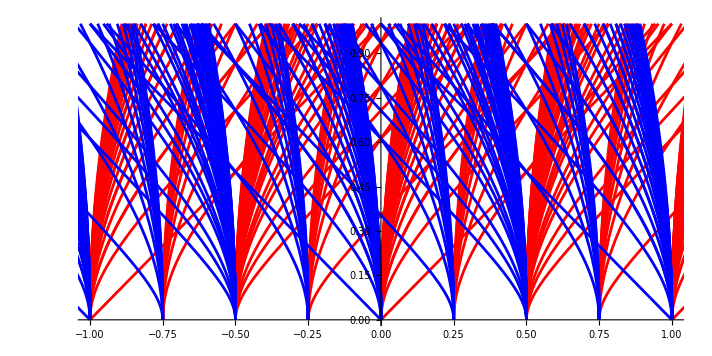

```mathematica
plt = With[{m=1/10,psi=0},Module[{charges1, rays},
rays = Table[
Tooltip[
Style[
{Rays[c/.repCh,t,psi,m], t},
If[First[c/.repCh]>0, Blue, Red]
], c],
 {c, charges}];
ParametricPlot[rays, {t,0,1},
PlotRange->{{-1,1},{0,1}}
]]]
```

```mathematica
{m/4,(m+1)/4,(1-m)/2,(m+2)/4,(m+3)/4,1-m/2}
```

```mathematica
<|1/40->{Ch[1,2],-Ch[0,0]},11/40->{Ch[1,1],-Ch[0,-1]},9/20->{Ch[2,1],-Ch[1,1]},21/40->{Ch[2,2],-Ch[1,0]},31/40->{Ch[3,3],-Ch[2,1]},19/20->{Ch[3,2],-Ch[2,2]}|>
```

```mathematica
With[{m=-1/10, psi=0},
charges = Flatten@Table[s Ch[p,q],{p,-6,6},{q,-6,6},{s,{-1,1}}];
charges = Select[charges,-.2<=Rays[#/.repCh,0,0,m]<=1.2&];
A =KeySort[GroupBy[charges,Rays[#/.repCh,0,0,m]&]];
casc = Function[s, SortBy[N@Rays[#/.repCh,1,0,m]&][s][[{1,-1}]]]/@A;

rays = Table[
Tooltip[
Style[
{Rays[c/.repCh,t,psi,m], t},
If[First[c/.repCh]>0, Blue, Red]
], c],
 {c, charges}];
(*rays1 = Table[
Tooltip[
Style[
{Rays[c/.repCh,t,psi,m], t},
Directive[Thickness[.004], Brown]
], c],
 {c, helixCharges}];*)
plt = ParametricPlot[rays, {t,0,1},
PlotRange->{{-.2,1.2},{0,.5}}];
(*plt1=ParametricPlot[rays1, {t,0,1},
PlotRange->{{-1,1},{0,1}}];*)
]
```

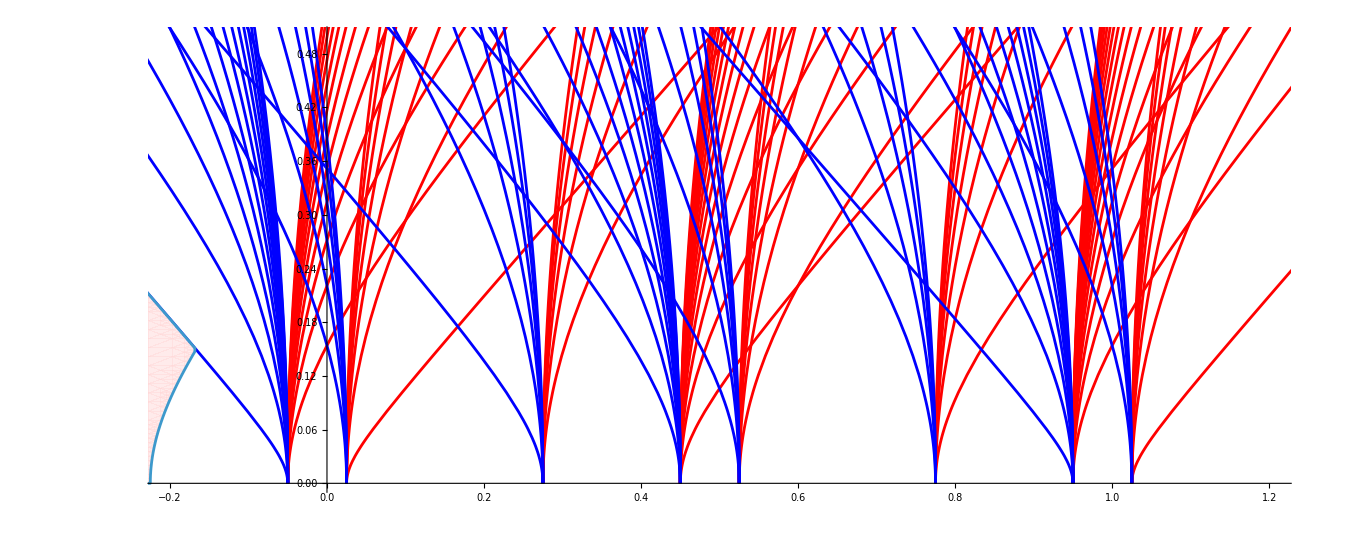

```mathematica
Show[plt,GrF1Q]
```

```mathematica
(*(*m=1/10*)
SFBridgeland = {{1,1},{2,2},{3,2},{4,3}};
SFArcaraI = {{2,1},{3,2},{4,2}};
SFArcaraII={{1,1},{2,2},{3,2},{4,3}};*)
```

```mathematica
quiverdomains={Table[QuiverDomain[SpectralFlow[#,spec]&/@CollBridgeland, 0, -1/10][[1]], {spec, SFBridgeland}],Table[QuiverDomain[SpectralFlow[#,spec]&/@CollArcaraI, 0, -1/10, "Style"->LightGreen][[1]], {spec, SFArcaraI}],
Table[QuiverDomain[SpectralFlow[#,spec]&/@CollArcaraII, 0, -1/10, "Style"->LightRed][[1]], {spec, SFArcaraII}]};
```

```mathematica
SFBridgeland
SFArcaraI
SFArcaraII
```

{{0,0},{1,1},{2,1},{3,2}}

{{1,0},{2,1},{3,1},{4,2}}

{{1,1},{2,1},{3,2}}

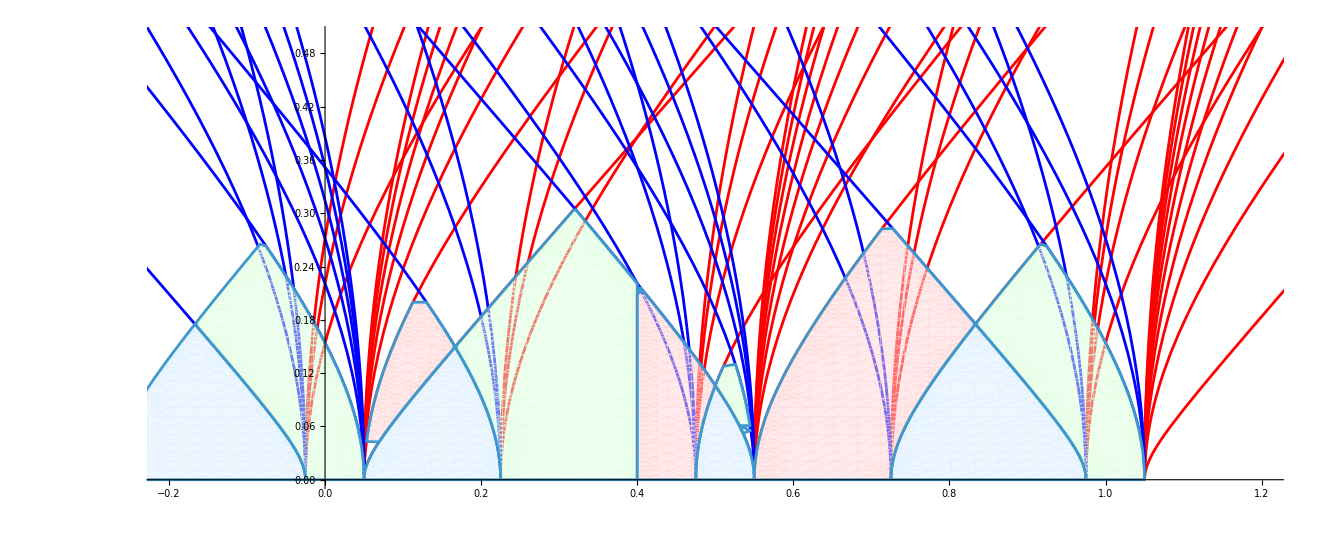

```mathematica
Show[plt,
quiverdomains
]
```

```mathematica
{k,k+1}.{Ch[0,0],-Ch[1,0]}/.repCh
BogomolovDiscriminant[%]
```

{-1,-1-k,0,0}

0

```mathematica
{k+1,k}.{Ch[0,0],-Ch[1,0]}/.repCh
BogomolovDiscriminant[%]
```

{1,-k,0,0}

0

```mathematica
{m,n}.{Ch[3,2],-Ch[2,1]}/.repCh
Simplify@BogomolovDiscriminant[%]
```

{m-n,3 m-2 n,2 m-n,4 m-(3 n)/2}

(m n)/(2 (m-n)^2)

```mathematica
DSZ[Ch[1,1],Ch[3,2]]/.repCh
```

5

```mathematica
SpectralFlow[#,{2,1}]&/@CollArcaraII
```

{{1,2,1,3/2},{0,0,-1,-1/2},{1,0,0,0},{-1,-1,0,0}}

```mathematica
Rays[{0,0,-1,-1/2},t,0,m]
```

1/2+Re[m]

```mathematica
-Ch[1,0]+Ch[1,1]/.repCh
```

{0,0,1,1/2}

```mathematica
{Ch[-2,1],Ch[-1,0],Ch[0,0],Ch[1,-1],Ch[1,0],Ch[2,-1]}/.{Ch[p_,q_]:>{1,p,q,ch2}}
ToFB/@%
```

{{1,-2,1,ch2},{1,-1,0,ch2},{1,0,0,ch2},{1,1,-1,ch2},{1,1,0,ch2},{1,2,-1,ch2}}

{{1,-2,-1,ch2},{1,-1,-1,ch2},{1,0,0,ch2},{1,1,0,ch2},{1,1,1,ch2},{1,2,1,ch2}}

```mathematica
Rays[{0,0,-1,-1/2},t,0,1/10]
```

3/5

```mathematica
Rays[Ch[2,2]/.repCh,0,0,1/10]
```

21/40

```mathematica
FullSimplify[ComplexExpand[Re[ZLV[{r,dF,dB,ch2},s,m]]]]
```

-ch2+dB (-m+s)+1/2 (m+2 s) (2 dF+m r-4 r s)

```mathematica
-ch2+dB (-m+s)+1/2 (m+2 s) (2 dF+m r-4 r s)/.{r->gam[[1]],dF->gam[[2]],dB->gam[[3]],ch2->gam[[4]]}
```

Part::partd: Part specification gam⟦1⟧ is longer than depth of object.

Part::partd: Part specification gam⟦2⟧ is longer than depth of object.

Part::partd: Part specification gam⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

1/2 (m+2 s) (m gam⟦1⟧-4 s gam⟦1⟧+2 gam⟦2⟧)+(-m+s) gam⟦3⟧-gam⟦4⟧

```mathematica
QuiverValid[Coll_,m_,s_]:=And@@((1/2 (m+2 s) (m #⟦1⟧-4 s #⟦1⟧+2 #⟦2⟧)+(-m+s) #⟦3⟧-#⟦4⟧<=0)&/@Coll);
```

```mathematica
CollBridgeland={{1,0,0,0},{-1,1,0,0},{-1,0,1,1/2},{1,-1,-1,1/2}}
```

{{1,0,0,0},{-1,1,0,0},{-1,0,1,1/2},{1,-1,-1,1/2}}

```mathematica
CollBridgeland
```

{{1,0,0,0},{-1,1,0,0},{-1,0,1,1/2},{1,-1,-1,1/2}}

```mathematica
options = Flatten[Table[{mF,mB},{mF,-10,10},{mB,-10,10}],1];
SFBridgeland = Select[options, Function[{mFmB}, UnsameQ[False,Reduce[0<=s<=1&&QuiverValid[SpectralFlow[#,{mFmB[[1]],mFmB[[2]]}]&/@CollBridgeland,-1/10,s],s]]]]
```

{{0,0},{1,1},{2,1},{3,2}}

```mathematica
options = Flatten[Table[{mF,mB},{mF,-10,10},{mB,-10,10}],1];
SFArcaraI = Select[options, Function[{mFmB}, UnsameQ[False,Reduce[0<=s<=1&&QuiverValid[SpectralFlow[#,{mFmB[[1]],mFmB[[2]]}]&/@CollArcaraI,-1/10,s],s]]]]
```

{{1,0},{2,1},{3,1},{4,2}}

```mathematica
options = Flatten[Table[{mF,mB},{mF,-10,10},{mB,-10,10}],1];
SFArcaraII = Select[options, Function[{mFmB}, UnsameQ[False,Reduce[0<=s<=1&&QuiverValid[SpectralFlow[#,{mFmB[[1]],mFmB[[2]]}]&/@CollArcaraII,-1/10,s],s]]]]
```

{{1,1},{2,1},{3,2}}

```mathematica
Reduce[QuiverValid[CollBridgeland,1/10,s],s]
```

-49/40<s<-21/20

```mathematica
Select[]
```

```mathematica
FindInstance[QuiverValid[CollBridgeland,1/10,s],s]
```

{{s→-73/64}}

```mathematica
SpectralFlow[#,{0,0}]&/@CollArcaraII
InitialPosition[#,1/10]&/@%
```

{{1,0,0,0},{0,0,-1,1/2},{1,-2,-1,3/2},{-1,1,1,-1/2}}

Power::infy: Infinite expression 1/0 encountered.

{-1/20,ComplexInfinity,-29/40,-9/40}

```mathematica
CollArcara1 = {{1,0,0,0}, {1,1,-1,0},{1,1,0,1/2},{2,1,0,-1/2}};
CollArcara1=(ToFB/@%)
```

{{1,0,0,0},{1,1,0,0},{1,1,1,1/2},{2,1,1,-1/2}}

```mathematica
CollArcara2 = {{1,0,0,0}, {1,0,1,-1/2},{1,1,0,1/2},{2,1,0,-1/2}};
CollArcara2=(ToFB/@%)
```

{{1,0,0,0},{1,0,1,-1/2},{1,1,1,1/2},{2,1,1,-1/2}}

```mathematica
BogomolovDiscriminant/@CollArcara2
```

{0,0,0,3/8}

```mathematica
ToHC/@(Coll/.repCh)
```

{{1,0,0,0},{1,1,-1,0},{1,1,0,1/2},{1,2,-1,3/2}}

```mathematica
QuiverDomain[]
```

```mathematica
DSZ@@{Ch[0,0],-Ch[-1,0]}/.repCh
```

2

```mathematica
{2,1}.{Ch[0,0],-Ch[-1,0]}/.repCh
```

{1,1,0,0}

```mathematica
DSZ@@#&/@Values[casc]/.repCh
```

{4,4,2,4,4,2}

```mathematica
(* spectral flow *)
ZLV[SpectralFlow[{r,dF,dB,ch2},{mF,mB}],T+mF/3,m+mB-(2 mF)/3]-ZLV[{r,dF,dB,ch2},T,m]//Simplify
```

0

```mathematica
Assuming[m∈Reals, Expand@Simplify@Rays[SpectralFlow[Ch[p,q]/.repCh,{3k,2k}],0,0,m]]
```

k-m/8+p/4-1/8 √((3 m+2 p-3 q)^2)+q/8

```mathematica
Expand@Assuming[(3 m-3 mB+2 mF)>0, Simplify[Rays[Ch[mF,mB]/.repCh, 0,0,m]/.{Re[m]->m,Im[m]->0}]]
```

-m/2+mB/2

```mathematica
Expand@Assuming[(3 m-3 mB+2 mF)<0, Simplify[Rays[Ch[mF,mB]/.repCh, 0,0,m]/.{Re[m]->m,Im[m]->0}]]
```

m/4-mB/4+mF/2

```mathematica
Expand[1/8D[ZLV[{-1,0,0,0},T,m], T]]
```

m/8+T

```mathematica
ToHC/@CollDArcaraI
```

{{1,0,0,0},{1,0,1,-1/2},{1,1,0,1/2},{2,1,0,-1/2}}

```mathematica
ToHC/@CollDArcaraII
```

{{1,0,0,0},{1,1,-1,0},{1,1,0,1/2},{2,1,0,-1/2}}

```mathematica
ToHC/@CollDBridgeland/.repCh
```

{{1,0,0,0},{1,1,-1,0},{1,1,0,1/2},{1,2,-1,3/2}}

```mathematica
ToFB/@{{1,0,0,0},{1,1,-1,0},{1,1,0,1/2},{1,2,-1,3/2}}
```

{{1,0,0,0},{1,1,0,0},{1,1,1,1/2},{1,2,1,3/2}}

```mathematica
ExtFromStrong[{{1,0,0,0},{1,1,0,0},{1,1,1,1/2},{1,2,1,3/2}}]
ToHC/@%
```

{{1,0,0,0},{-1,1,0,0},{-1,0,1,1/2},{1,-1,-1,1/2}}

{{1,0,0,0},{-1,1,-1,0},{-1,0,1,1/2},{1,-1,0,1/2}}

```mathematica
ToHC/@CollDArcaraI
```

{{1,0,0,0},{1,0,1,-1/2},{1,1,0,1/2},{2,1,0,-1/2}}

```mathematica
ToHC/@CollDArcaraII
```

{{1,0,0,0},{1,1,-1,0},{1,1,0,1/2},{2,1,0,-1/2}}

```mathematica
CollDBridgeland={{1,0}}
```

```mathematica
ToHC/@CollDBridgeland
```

{{1,-3,1,4},{1,-2,0,2},{1,-2,1,3/2},{1,-1,0,1/2}}

```mathematica
CollBridgeland = ExtFromStrong[CollDBridgeland/.repCh]
```

{{1,-3,-2,4},{-1,4,2,-6},{-1,3,3,-9/2},{1,-4,-3,15/2}}

```mathematica
CollDBridgeland/.repCh
```

{{1,-3,-2,4},{1,-2,-2,2},{1,-2,-1,3/2},{1,-1,-1,1/2}}

```mathematica
GrF1Q=With[{m=1/10},Show[
QuiverDomain[Table[SpectralFlow[CollArcaraII[[i]],{0,0}],{i,4}],0,m,"Style"->LightRed][[1]],
QuiverDomain[Table[SpectralFlow[CollBridgeland[[i]],{0,0}],{i,4}],0,m][[1]],
QuiverDomain[Table[SpectralFlow[CollArcaraI[[i]],{1,-1}],{i,4}],0,m,"Style"->LightGreen][[1]],QuiverDomain[Table[SpectralFlow[CollBridgeland[[i]],{1,0}],{i,4}],0,m][[1]],
QuiverDomain[Table[SpectralFlow[CollArcaraI[[i]],{2,-1}],{i,4}],0,m,"Style"->LightGreen][[1]],
QuiverDomain[Table[SpectralFlow[CollArcaraII[[i]],{2,-1}],{i,4}],0,m,"Style"->LightRed][[1]],QuiverDomain[Table[SpectralFlow[CollBridgeland[[i]],{2,-1}],{i,4}],0,m][[1]],QuiverDomain[Table[SpectralFlow[CollArcaraII[[i]],{1,0}],{i,4}],0,m,"Style"->LightRed][[1]]]];
```

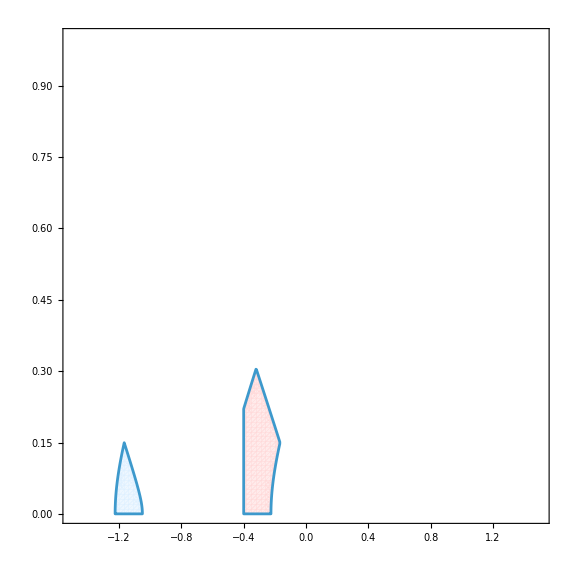

```mathematica
GrF1Q
```

## Initial positions

```mathematica
FullSimplify[Rays[{r,dF,dB,ch2},0,0,m]/.{Re[m]->m,Im[m]->0}]
```

(dB+2 dF-m r-√(dB^2-16 ch2 r+2 dB (2 dF-9 m r)+(2 dF+3 m r)^2))/(8 r)

```mathematica
Flatten@Table[Rays[s Ch[p,q]/.repCh,0,0,1/10], {p,-20,20},{q,-20,20},{s,{-1,1}}];
Sort@DeleteDuplicates@Mod[%,1]
```

{1/40,11/40,9/20,21/40,31/40,19/20}

```mathematica
With[{m=Mod[-1-17812/98598,1]},
{m/4,(m+1)/4,(1-m)/2,(m+2)/4,(m+3)/4,1-m/2}
]
```

{40393/197196,22423/49299,4453/49299,138991/197196,94145/98598,58205/98598}

```mathematica
Reduce[0<=m/4<(m+1)/4<(1-m)/2<(m+2)/4<(m+3)/4<1-m/2<=1,m]
```

0<m<1/3

```mathematica
Reduce[{0<m/4<1,0<(m+1)/4<1,0<(1-m)/2<1,0<(m+2)/4<1,0<(m+3)/4<1,0<1-m/2<1},m]
```

0<m<1

```mathematica
0<=#<=1&/@{m/4,(m+1)/4,(1-m)/2,(m+2)/4,(m+3)/4,1-m/2}
Reduce[%,m]
```

{0≤m/4≤1,0≤(1+m)/4≤1,0≤(1-m)/2≤1,0≤(2+m)/4≤1,0≤(3+m)/4≤1,0≤1-m/2≤1}

0≤m≤1

```mathematica
1-(m+1)/2//Simplify
```

(1-m)/2

```mathematica
Simplify[{Mod[m,1]/4,(Mod[m,1]+1)/4,(1-Mod[m,1])/2,(Mod[m,1]+2)/4,(Mod[m,1]+3)/4,1-Mod[m,1]/2}, {-1/3<m<0}]
N[%/.{m->-1/10}]
```

{1/4 Mod[m,1],(2+m)/4,-m/2,(3+m)/4,(4+m)/4,1-1/2 Mod[m,1]}

{0.225,0.475,0.05,0.725,0.975,0.55}

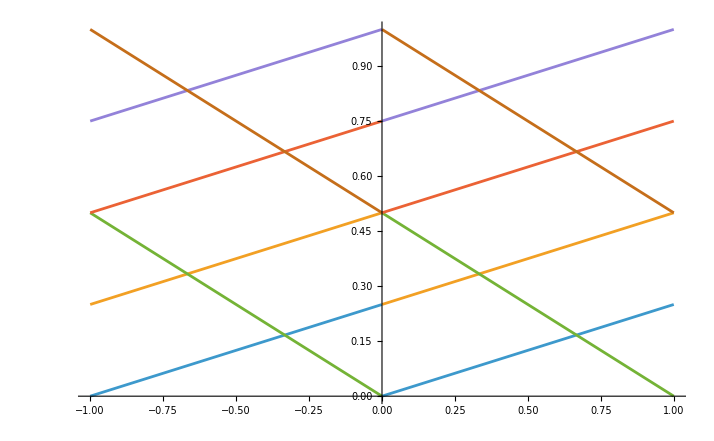

```mathematica
Plot[{Mod[m,1]/4,(Mod[m,1]+1)/4,(1-Mod[m,1])/2,(Mod[m,1]+2)/4,(Mod[m,1]+3)/4,1-Mod[m,1]/2}, {m,-1,1}]
```

```mathematica
charges = Flatten@Table[s Ch[p,q],{p,-10,10},{q,-10,10},{s,{-1,1}}];
A = GroupBy[charges,Mod[Rays[#/.repCh,0,0,1/10],1]&];
```

```mathematica
A = FullSimplify@ComplexExpand[Im[ZLV[{r,dF,dB,ch2},s+I t,m]**ZLV[{rr,ddF,ddB,cch2},s+I t,m]]]
```

1/2 t (-6 dB ddF m+6 ddB dF m-ddB m^2 r+4 ddF m^2 r+dB m^2 rr-4 dF m^2 rr-16 ddB m r s+16 ddF m r s+16 dB m rr s-16 dF m rr s+8 ddB r s^2+16 ddF r s^2-8 dB rr s^2-16 dF rr s^2+2 cch2 (dB+2 dF-r (m+8 s))-2 ch2 (ddB+2 ddF-rr (m+8 s))+8 ((ddB+2 ddF) r-(dB+2 dF) rr) t^2)

```mathematica
FullSimplify@Series[1/t A/.{s->s l,t->t l}, {l,0,11}]
A1=(Normal[%]/.{l->1})/4/DSZ[{r,dF,dB,ch2},{rr,ddF,ddB,cch2}]
```

(cch2 (dB+2 dF-m r)-ch2 (ddB+2 ddF-m rr)+1/2 m (-6 dB ddF+6 ddB dF-ddB m r+4 ddF m r+(dB-4 dF) m rr))+8 (-((cch2+(ddB-ddF) m) r)+(ch2+(dB-dF) m) rr) s l+4 (ddB r+2 ddF r-(dB+2 dF) rr) (s^2+t^2) l^2+O[l]^12

(cch2 (dB+2 dF-m r)-ch2 (ddB+2 ddF-m rr)+1/2 m (-6 dB ddF+6 ddB dF-ddB m r+4 ddF m r+(dB-4 dF) m rr)+8 (-((cch2+(ddB-ddF) m) r)+(ch2+(dB-dF) m) rr) s+4 (ddB r+2 ddF r-(dB+2 dF) rr) (s^2+t^2))/(4 (ddB r+2 ddF r-dB rr-2 dF rr))

```mathematica
Simplify[1/2D[A1,{{s,t},2}]]
```

{{1,0},{0,1}}

```mathematica
b=Together[1/2D[A1,{{s,t}}]/.{s->0,t->0}]
{s0,t0}=Simplify[Inverse[Q].(-b)]
```

{(-cch2 r-ddB m r+ddF m r+ch2 rr+dB m rr-dF m rr)/(ddB r+2 ddF r-dB rr-2 dF rr),0}

{(cch2 r+ddB m r-ddF m r-ch2 rr-dB m rr+dF m rr)/(ddB r+2 ddF r-dB rr-2 dF rr),0}

```mathematica
FullSimplify[(s-s0)^2+(t-t0)^2/.First@Solve[A1==0,t]]
```

(r (2 (ddB+2 ddF) (ch2 ddB+2 ch2 ddF-cch2 (dB+2 dF)+3 dB ddF m-3 ddB dF m)+(2 cch2+3 ddB m) (4 cch2+3 (ddB-2 ddF) m) r)+2 ((dB+2 dF) (-ch2 (ddB+2 ddF)+cch2 (dB+2 dF)-3 dB ddF m+3 ddB dF m)+(-8 cch2 ch2+3 (-3 cch2 dB-3 ch2 ddB+2 ch2 ddF+2 cch2 dF) m+9 (dB (-ddB+ddF)+ddB dF) m^2) r) rr+(2 ch2+3 dB m) (4 ch2+3 (dB-2 dF) m) rr^2)/(8 (ddB r+2 ddF r-(dB+2 dF) rr)^2)

```mathematica
A1
```

(cch2 (dB+2 dF-m r)-ch2 (ddB+2 ddF-m rr)+1/2 m (-6 dB ddF+6 ddB dF-ddB m r+4 ddF m r+(dB-4 dF) m rr)+8 (-((cch2+(ddB-ddF) m) r)+(ch2+(dB-dF) m) rr) s+4 (ddB r+2 ddF r-(dB+2 dF) rr) (s^2+t^2))/(4 (ddB r+2 ddF r-dB rr-2 dF rr))

1/8 (-m+3 √(m^2))

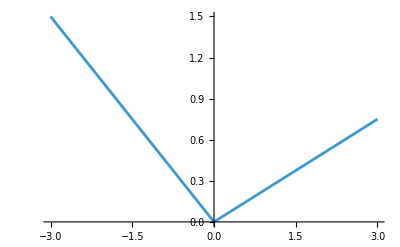

```mathematica
Rays[Ch[0,0]/.repCh,0,0,m]/.{Im[m]->0,Re[m]->m}//Simplify
Plot[%, {m,-3,3}]
```

```mathematica
ZLV[Ch[p,q]/.repCh,T,m]
Solve[%==0,T]
```

m^2/2+m p-p q+q^2/2-m T+2 p T-4 T^2+q (-m+T)

{{T→1/4 (m+2 p-q)},{T→1/2 (-m+q)}}

```mathematica
ToFB[{1,1,-1,0}]
```

{1,1,0,0}

```mathematica
ToFB[{1,2,-1,3/2}]
```

{1,2,1,3/2}

## initial rays as a function of m

```mathematica
With[{m=2/3+1/10},Module[{charges,casc},
charges = Flatten@Table[s Ch[p,q],{p,-20,20},{q,-20,20},{s,{-1,1}}];
charges = Select[charges,0<=Rays[#/.repCh,0,0,m]<=1&];
casc = KeySort[GroupBy[charges,Rays[#/.repCh,0,0,m]&]];
Function[s, SortBy[N@Rays[#/.repCh,1,0,m]&][s][[{1,-1}]]]/@casc
]]
```

<|7/60→{Ch[1,1],-Ch[0,1]},23/120→{Ch[1,2],-Ch[0,0]},53/120→{Ch[2,3],-Ch[1,1]},37/60→{Ch[2,2],-Ch[1,2]},83/120→{Ch[3,4],-Ch[2,2]},113/120→{Ch[3,3],-Ch[2,1]}|>

## LV: checking for other symmetries of the LV diagram

```mathematica
Manipulate[Show[plt/.{l_Line:>{Opacity[.1],l}}, plt/.{l_Line:>Translate[l,{L,0}]}], {{L,1},-2.5,2.5,.001}]
```

Show::gcomb: Could not combine the graphics objects in Show[plt,plt].

## XY scattering diagram

```mathematica
ZLV[{-1,0,0,0},T,m]
```

-m^2/2+m T+4 T^2

```mathematica
{Re[Exp[-I psi]T]/Cos[psi], -Re[Exp[-I psi]TD]/Cos[psi]}/.{TD->ZLV[{-1,0,0,0},T,m]}/.{T->s+I t,psi->0}//ComplexExpand//FullSimplify//Expand
```

{s,m^2/2-m s-4 s^2+4 t^2}

```mathematica
Solve[Thread[{s,m^2/2-m s-4 s^2+4 t^2}=={x,y}],{s,t}]//Simplify
```

{{s→x,t→-1/2 √(-m^2/2+m x+4 x^2+y)},{s→x,t→1/2 √(-m^2/2+m x+4 x^2+y)}}

```mathematica
Solve[-m^2/2+m x+4 x^2+y==0,y]//Expand
```

{{y→m^2/2-m x-4 x^2}}

```mathematica
charges = Flatten@Table[s Ch[p,q],{p,-3,3},{q,-3,3},{s,{-1,1}}];
A = GroupBy[charges,Mod[Rays[#/.repCh,0,0,0],1]&];
```

```mathematica
XYRay[#/.repCh,{x,y},mu]&/@charges;
XYrays = Flatten@(y/.Solve[#==0,y]&/@%);
```

```mathematica
XYrays=Tooltip[y/.First@Solve[XYRay[#/.repCh,{x,y},mu]==0, y], #]&/@charges;
```

```mathematica
XYrays[[10]]
```

1/2 (-7+8 mu+10 x)

```mathematica
helixCharges = {Ch[0,0],Ch[1,0],Ch[1,1],Ch[2,1]};
helixCharges = Flatten@Table[s c/.{Ch[p_,q_]:>Ch[p+3k,q+2k]}, {k,-1,1},{c,helixCharges}, {s,{-1,1}}]
```

{-Ch[-3,-2],Ch[-3,-2],-Ch[-2,-2],Ch[-2,-2],-Ch[-2,-1],Ch[-2,-1],-Ch[-1,-1],Ch[-1,-1],-Ch[0,0],Ch[0,0],-Ch[1,0],Ch[1,0],-Ch[1,1],Ch[1,1],-Ch[2,1],Ch[2,1],-Ch[3,2],Ch[3,2],-Ch[4,2],Ch[4,2],-Ch[4,3],Ch[4,3],-Ch[5,3],Ch[5,3]}

```mathematica
helixRays=Tooltip[y/.First@Solve[XYRay[#/.repCh,{x,y},mu]==0, y], #]&/@helixCharges;
```

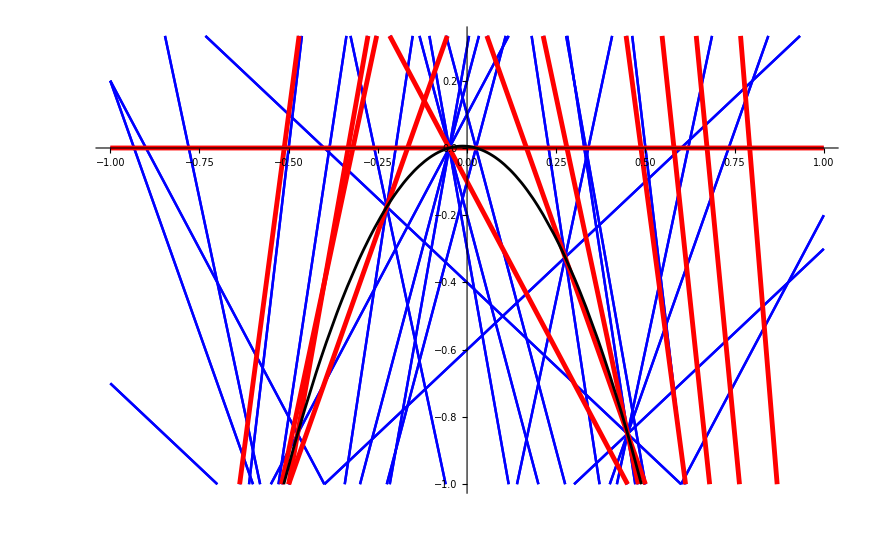

```mathematica
With[{m=1/10},Block[{mu=1/10},
Show[{
Plot[XYrays, {x,-1,1},
PlotStyle->Directive[Thickness[.002], Blue]
],
Plot[helixRays, {x,-1,1},
PlotRange->{{-1,1},{-1,1/3}},
PlotStyle->Directive[Thickness[.004], Red]
],
Plot[m^2/2-m x-4 x^2,{x,-3,3},
PlotRange->{{-1,1},{-1,1}},
PlotStyle->Directive[Black]
]
}]
]]
```

## Checking Massless objects at conifold points

```mathematica
A = Numerator@Together[MirrorCurveJ[m,u]-j]
```

1-24 m u^2-72 u^3+240 m^2 u^4+1152 m u^5+1728 u^6-1280 m^3 u^6-6912 m^2 u^7-13824 m u^8-j m u^8+3840 m^4 u^8-13824 u^9-j u^9+18432 m^3 u^9+27648 m^2 u^10+8 j m^2 u^10-6144 m^5 u^10+36 j m u^11-18432 m^4 u^11+27 j u^12-16 j m^3 u^12+4096 m^6 u^12

```mathematica
Simplify[Discriminant[A,u]]
Simplify[Solve[%==0,j]]
```

(-1728+j)^6 j^8 (27+256 m^3)^3 (-387420489-4897760256 m^3-12899450880 m^6+16777216 (-756+j) m^9-4294967296 m^12)

{{j→0},{j→0},{j→0},{j→0},{j→0},{j→0},{j→0},{j→0},{j→1728},{j→1728},{j→1728},{j→1728},{j→1728},{j→1728},{j→((27+256 m^3) (243+256 m^3)^3)/(16777216 m^9)}}

```mathematica
mVals = m/.Simplify@Solve[ (243+256 m^3)==0,m]
```

{-3/4 (-3/2)^(2/3),-3/4 (3/2)^(2/3),3/4 (-1)^(1/3) (3/2)^(2/3)}

```mathematica
Simplify@Solve[((27+256 m^3) (243+256 m^3)^3)/(16777216 m^9)==1728,m]
```

{{m→-(3 (-9-6 √3)^(1/3))/(4 2^(2/3))},{m→-(3 (-9-6 √3)^(1/3))/(4 2^(2/3))},{m→(3 (9+6 √3)^(1/3))/(4 2^(2/3))},{m→(3 (9+6 √3)^(1/3))/(4 2^(2/3))},{m→3/4 (-1/2)^(2/3) (9+6 √3)^(1/3)},{m→3/4 (-1/2)^(2/3) (9+6 √3)^(1/3)},{m→(3 (9-6 √3)^(1/3))/(4 2^(2/3))},{m→(3 (9-6 √3)^(1/3))/(4 2^(2/3))},{m→-(3 (-9+6 √3)^(1/3))/(4 2^(2/3))},{m→-(3 (-9+6 √3)^(1/3))/(4 2^(2/3))},{m→-3/4 (-1/2)^(2/3) (-9+6 √3)^(1/3)},{m→-3/4 (-1/2)^(2/3) (-9+6 √3)^(1/3)}}

```mathematica
MirrorCurveDelta[m,u]
```

m+u-8 m^2 u^2-36 m u^3-27 u^4+16 m^3 u^4

```mathematica
Simplify[A/.{j->0}]
```

(1-8 m u^2-24 u^3+16 m^2 u^4)^3

```mathematica
Simplify[A/.{j->1728}]
```

(1-36 u^3+48 m^2 u^4+216 u^6-64 m^3 u^6+12 m u^2 (-1+12 u^3))^2

```mathematica
Simplify[A/.{j->((27+256 m^3) (243+256 m^3)^3)/(16777216 m^9)}]
```

-1/(16777216 m^9)(8 m+9 u)^2 (-939524096 m^11 u^8+1073741824 m^12 u^10-1417176 m^2 u^5 (-2+27 u^3)-4782969 u^7 (-1+27 u^3)-33554432 m^10 u^6 (-10+79 u^3)+531441 m u^6 (-7+108 u^3)-6291456 m^9 u^4 (10-168 u^3+267 u^6)+3145728 m^8 u^2 (2-51 u^3+324 u^6)-248832 m^5 u^2 (4-144 u^3+1215 u^6)+186624 m^4 u^3 (8-306 u^3+3159 u^6)-104976 m^3 u^4 (20-792 u^3+14823 u^6)+65536 m^7 (-4+72 u^3-189 u^6+2916 u^9)-147456 m^6 u (-4+126 u^3-1566 u^6+22599 u^9))

```mathematica
A2=(-939524096 m^11 u^8+1073741824 m^12 u^10-1417176 m^2 u^5 (-2+27 u^3)-4782969 u^7 (-1+27 u^3)-33554432 m^10 u^6 (-10+79 u^3)+531441 m u^6 (-7+108 u^3)-6291456 m^9 u^4 (10-168 u^3+267 u^6)+3145728 m^8 u^2 (2-51 u^3+324 u^6)-248832 m^5 u^2 (4-144 u^3+1215 u^6)+186624 m^4 u^3 (8-306 u^3+3159 u^6)-104976 m^3 u^4 (20-792 u^3+14823 u^6)+65536 m^7 (-4+72 u^3-189 u^6+2916 u^9)-147456 m^6 u (-4+126 u^3-1566 u^6+22599 u^9));
```

```mathematica
A2=Numerator[A]/-(8 m+9 u)^2
```

-939524096 m^11 u^8+1073741824 m^12 u^10-1417176 m^2 u^5 (-2+27 u^3)-4782969 u^7 (-1+27 u^3)-33554432 m^10 u^6 (-10+79 u^3)+531441 m u^6 (-7+108 u^3)-6291456 m^9 u^4 (10-168 u^3+267 u^6)+3145728 m^8 u^2 (2-51 u^3+324 u^6)-248832 m^5 u^2 (4-144 u^3+1215 u^6)+186624 m^4 u^3 (8-306 u^3+3159 u^6)-104976 m^3 u^4 (20-792 u^3+14823 u^6)+65536 m^7 (-4+9 u^3 (8-21 u^3+324 u^6))-147456 m^6 u (-4+9 u^3 (14-174 u^3+2511 u^6))

```mathematica
A
```

1-24 m u^2-72 u^3+240 m^2 u^4+1152 m u^5+1728 u^6-1280 m^3 u^6-6912 m^2 u^7-13824 m u^8-j m u^8+3840 m^4 u^8-13824 u^9-j u^9+18432 m^3 u^9+27648 m^2 u^10+8 j m^2 u^10-6144 m^5 u^10+36 j m u^11-18432 m^4 u^11+27 j u^12-16 j m^3 u^12+4096 m^6 u^12

```mathematica
bpoints = ReIm[u]/.NSolve[A2==0/.{m->-3/(4 2^(2/3))}, u, WorkingPrecision->50];
```

```mathematica
bpoints
```

{{-0.1287951912842354913855845317195475058365567177998,-0.29168695234459654162488955859600299724677633650489},{-0.1287951912842354913855845317195475058365567177998,-0.29168695234459654162488955859600299724677633650489},{-0.1287951912842354913855845317195475058365567177998,-0.29168695234459654162488955859600299724677633650489},{-0.1287951912842354913855845317195475058365567177998,0.29168695234459654162488955859600299724677633650489},{-0.1287951912842354913855845317195475058365567177998,0.29168695234459654162488955859600299724677633650489},{-0.1287951912842354913855845317195475058365567177998,0.29168695234459654162488955859600299724677633650489},{0.41997368329829105492240353575940945019008382156717,0},{6.5571956320428368066072220998302367645243707591072,0},{6.5571956320428368066072220998302367645243707591072,0},{6.5571956320428368066072220998302367645243707591072,0}}

```mathematica
Length[bpoints]
```

10

```mathematica
Simplify@Discriminant[A2,u]
```

-81129638414606681695789005144064 m^42 (27+256 m^3)^6 (243+256 m^3)^18 (-19683-124416 m^3+65536 m^6)^9

```mathematica
Complex@@#&/@bpoints
```

{-0.1287951912842354913855845317195475058365567177998-0.29168695234459654162488955859600299724677633650489 ⅈ,-0.1287951912842354913855845317195475058365567177998-0.29168695234459654162488955859600299724677633650489 ⅈ,-0.1287951912842354913855845317195475058365567177998-0.29168695234459654162488955859600299724677633650489 ⅈ,-0.1287951912842354913855845317195475058365567177998+0.29168695234459654162488955859600299724677633650489 ⅈ,-0.1287951912842354913855845317195475058365567177998+0.29168695234459654162488955859600299724677633650489 ⅈ,-0.1287951912842354913855845317195475058365567177998+0.29168695234459654162488955859600299724677633650489 ⅈ,0.41997368329829105492240353575940945019008382156717,6.5571956320428368066072220998302367645243707591072,6.5571956320428368066072220998302367645243707591072,6.5571956320428368066072220998302367645243707591072}

```mathematica
Solve[8 m+9 u==0/.m->N[-3/(4 2^(2/3)),50],u]
```

{{u→0.4199736832982910549224035357594094501900838215672}}

```mathematica
URoots[N[-3/(4 2^(2/3)),50]]
```

{-0.123521671558320898506589275223355720644142300461-0.2794976370636358603106592017538862770155961147853 ⅈ,-0.123521671558320898506589275223355720644142300461+0.2794976370636358603106592017538862770155961147853 ⅈ,0.419973683298291054922404,0.419973683298291054922404}

```mathematica
A2
```

-939524096 m^11 u^8+1073741824 m^12 u^10-1417176 m^2 u^5 (-2+27 u^3)-4782969 u^7 (-1+27 u^3)-33554432 m^10 u^6 (-10+79 u^3)+531441 m u^6 (-7+108 u^3)-6291456 m^9 u^4 (10-168 u^3+267 u^6)+3145728 m^8 u^2 (2-51 u^3+324 u^6)-248832 m^5 u^2 (4-144 u^3+1215 u^6)+186624 m^4 u^3 (8-306 u^3+3159 u^6)-104976 m^3 u^4 (20-792 u^3+14823 u^6)+65536 m^7 (-4+9 u^3 (8-21 u^3+324 u^6))-147456 m^6 u (-4+9 u^3 (14-174 u^3+2511 u^6))

```mathematica
MirrorCurveDelta[m,u]
```

m+u-8 m^2 u^2-36 m u^3-27 u^4+16 m^3 u^4

```mathematica
D[m+u-8 m^2 u^2-36 m u^3-27 u^4+16 m^3 u^4,m]
```

1-16 m u^2-36 u^3+48 m^2 u^4

```mathematica
m^3/.Solve[{m+u-8 m^2 u^2-36 m u^3-27 u^4+16 m^3 u^4==0,1-16 m u^2-36 u^3+48 m^2 u^4==0},{m,u}]
```

{-27/256,-27/256,-27/256}

```mathematica
Simplify@Resultant[A2,MirrorCurveDelta[m,u],u]
```

79228162514264337593543950336 m^34 (27+256 m^3)^2

```mathematica
Complex@@#&/@bpoints
```

```mathematica
{-0.12879519128423549138558453171954750583655671779980751367407438564316886909428`49.756819346260436-0.29168695234459654162488955859600299724677633650488549307231498178281026129866`50.111836700637646 ⅈ,-0.12879519128423549138558453171954750583655671779980751367407438564316886909428`49.756819346260436-0.29168695234459654162488955859600299724677633650488549307231498178281026129866`50.111836700637646 ⅈ,-0.12879519128423549138558453171954750583655671779980751367407438564316886909428`49.756819346260436-0.29168695234459654162488955859600299724677633650488549307231498178281026129866`50.111836700637646 ⅈ,-0.12879519128423549138558453171954750583655671779980751367407438564316886909428`49.756819346260436+0.29168695234459654162488955859600299724677633650488549307231498178281026129866`50.111836700637646 ⅈ,-0.12879519128423549138558453171954750583655671779980751367407438564316886909428`49.756819346260436+0.29168695234459654162488955859600299724677633650488549307231498178281026129866`50.111836700637646 ⅈ,-0.12879519128423549138558453171954750583655671779980751367407438564316886909428`49.756819346260436+0.29168695234459654162488955859600299724677633650488549307231498178281026129866`50.111836700637646 ⅈ,0.41997368329829105492240353575940945019008382156717,6.55719563204283680660722209983023676452437075910715492775802433206283612075826`50.,6.55719563204283680660722209983023676452437075910715492775802433206283612075826`50.,6.55719563204283680660722209983023676452437075910715492775802433206283612075826`50.}
```

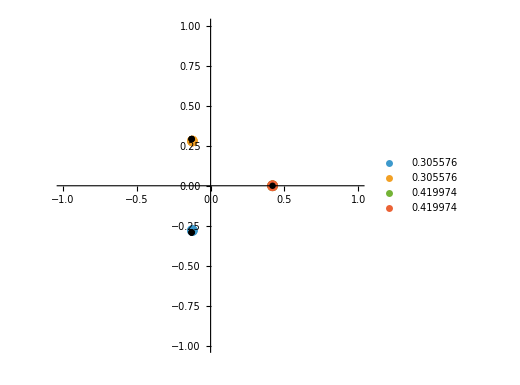

```mathematica
Show[PlotURoots[N[-3/(4 2^(2/3)),50]], Graphics[{PointSize[.012], Point[bpoints]}]]
```

```mathematica
MirrorCurveJ[m,u]
```

((1-8 m u^2-24 u^3+16 m^2 u^4)^3)/(u^8 (m+u-8 m^2 u^2-36 m u^3-27 u^4+16 m^3 u^4))

```mathematica
Simplify@Series[MirrorCurveJ[m,u],{u,Infinity,2}]
```

(4096 m^6)/(-27+16 m^3)-(18432 (m^4 (-27+8 m^3)))/((27-16 m^3)^2 u)-(1024 (m^2 (-19683+10206 m^3-6048 m^6+1024 m^9)))/((-27+16 m^3)^3 u^2)+O[1/u]^3

```mathematica
Limit[MirrorCurveJ[m,u],u->Infinity]
```

(4096 m^6)/(-27+16 m^3)

```mathematica
(4096 m3^2)/(-27+16 m3)/.{m3->-27/256}
```

-27/17

```mathematica
1728KleinInvariantJ[I]
```

1728

```mathematica
1728KleinInvariantJ[Exp[2Pi I/3]]
```

0

```mathematica
D[KleinInvariantJ[tau],{tau,2}]/.{tau->I}//N
```

-28.7356

```mathematica
D[KleinInvariantJ[tau],{tau,3}]/.{tau->Exp[2Pi I/3]}//N
```

-2.19688×10^-14-158.837 ⅈ

WolframAlphaQueryResults

```mathematica
m0Vals = m/.Solve[{m+u-8 m^2 u^2-36 m u^3-27 u^4+16 m^3 u^4==0,1-16 m u^2-36 u^3+48 m^2 u^4==0},{m,u}]
```

{(3 (-1)^(1/3))/(4 2^(2/3)),-3/(4 2^(2/3)),-3/4 (-1/2)^(2/3)}

```mathematica
NSolve[A==0/.{m->mVals[[1]],j->0},u]
```

{{u→-0.43947+0.758778 ⅈ},{u→-0.439215+0.755762 ⅈ},{u→-0.43722+0.753761 ⅈ},{u→-0.435901+0.759081 ⅈ},{u→-0.43437+0.754648 ⅈ},{u→-0.433648+0.757768 ⅈ},{u→-0.189226-0.22133 ⅈ},{u→-0.189226-0.22133 ⅈ},{u→-0.189226-0.22133 ⅈ},{u→0.286291+0.0532096 ⅈ},{u→0.286291+0.0532096 ⅈ},{u→0.286291+0.0532096 ⅈ}}

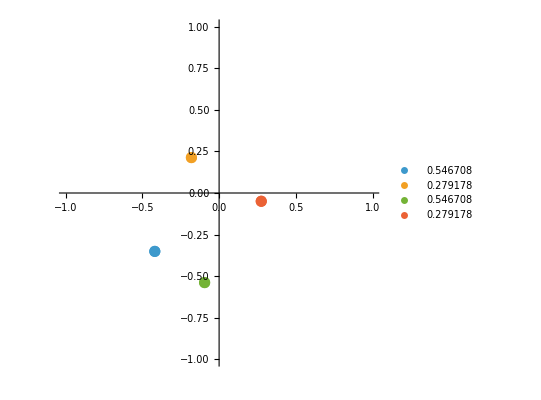

```mathematica
Show[PlotURoots[N[mVals[[3]],50]], Graphics[{PointSize[.012]}]]
```

```mathematica
m^3/.Simplify@Solve[{MirrorCurveDelta[m,u]==0, D[MirrorCurveDelta[m,u],m]==0},{m,u}]
```

{-27/256,-27/256,-27/256}

## Wall radius in terms of DSZ and Wall center

```mathematica
cch2 r+ddB m r-ddF m r-ch2 rr-dB m rr+dF m rr/.{
dF->Subscript[d,F],
dB->Subscript[d,F],
ddB->Subscript[d,F],
}
```

ReplaceAll::reps: {dF→d_F,dB→d_F,ddB→d'_F,Null} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

cch2 r+ddB m r-ddF m r-ch2 rr-dB m rr+dF m rr/.{dF→d_F,dB→d_F,ddB→d'_F,Null}

```mathematica
DSZ[{r,dF,dB,ch2},{rr,ddF,ddB,cch2}]
```

ddB r+2 ddF r-dB rr-2 dF rr

```mathematica
FullSimplify[Sqrt[(r (2 (ddB+2 ddF) (ch2 ddB+2 ch2 ddF-cch2 (dB+2 dF)+3 dB ddF m-3 ddB dF m)+(2 cch2+3 ddB m) (4 cch2+3 (ddB-2 ddF) m) r)+2 ((dB+2 dF) (-ch2 (ddB+2 ddF)+cch2 (dB+2 dF)-3 dB ddF m+3 ddB dF m)+(-8 cch2 ch2+3 (-3 cch2 dB-3 ch2 ddB+2 ch2 ddF+2 cch2 dF) m+9 (dB (-ddB+ddF)+ddB dF) m^2) r) rr+(2 ch2+3 dB m) (4 ch2+3 (dB-2 dF) m) rr^2)/(8 (ddB r+2 ddF r-(dB+2 dF) rr)^2)]]
```

1/(2 √2)(√((r (2 (ddB+2 ddF) (ch2 ddB+2 ch2 ddF-cch2 (dB+2 dF)+3 dB ddF m-3 ddB dF m)+(2 cch2+3 ddB m) (4 cch2+3 (ddB-2 ddF) m) r)+2 ((dB+2 dF) (-ch2 (ddB+2 ddF)+cch2 (dB+2 dF)-3 dB ddF m+3 ddB dF m)+(-8 cch2 ch2+3 (-3 cch2 dB-3 ch2 ddB+2 ch2 ddF+2 cch2 dF) m+9 (dB (-ddB+ddF)+ddB dF) m^2) r) rr+(2 ch2+3 dB m) (4 ch2+3 (dB-2 dF) m) rr^2)/(ddB r+2 ddF r-(dB+2 dF) rr)^2))

```mathematica
tmp = ExpandAll[(r (2 (ddB+2 ddF) (ch2 ddB+2 ch2 ddF-cch2 (dB+2 dF)+3 dB ddF m-3 ddB dF m)+(2 cch2+3 ddB m) (4 cch2+3 (ddB-2 ddF) m) r)+2 ((dB+2 dF) (-ch2 (ddB+2 ddF)+cch2 (dB+2 dF)-3 dB ddF m+3 ddB dF m)+(-8 cch2 ch2+3 (-3 cch2 dB-3 ch2 ddB+2 ch2 ddF+2 cch2 dF) m+9 (dB (-ddB+ddF)+ddB dF) m^2) r) rr+(2 ch2+3 dB m) (4 ch2+3 (dB-2 dF) m) rr^2)/(8 (ddB r+2 ddF r-(dB+2 dF) rr)^2)];
```

```mathematica
FullSimplify[Sqrt[tmp], {(r|dF|dB|ch2|rr|ddF|ddB|cch2)∈Integers,0<m<1}]
```

1/(2 √2)(√((r (2 (ddB+2 ddF) (ch2 ddB+2 ch2 ddF-cch2 (dB+2 dF)+3 dB ddF m-3 ddB dF m)+(2 cch2+3 ddB m) (4 cch2+3 (ddB-2 ddF) m) r)+2 ((dB+2 dF) (-ch2 (ddB+2 ddF)+cch2 (dB+2 dF)-3 dB ddF m+3 ddB dF m)+(-8 cch2 ch2+3 (-3 cch2 dB-3 ch2 ddB+2 ch2 ddF+2 cch2 dF) m+9 (dB (-ddB+ddF)+ddB dF) m^2) r) rr+(2 ch2+3 dB m) (4 ch2+3 (dB-2 dF) m) rr^2)/(ddB r+2 ddF r-(dB+2 dF) rr)^2))

```mathematica
tmp = ExpandAll[(r (2 (ddB+2 ddF) (ch2 ddB+2 ch2 ddF-cch2 (dB+2 dF)+3 dB ddF m-3 ddB dF m)+(2 cch2+3 ddB m) (4 cch2+3 (ddB-2 ddF) m) r)+2 ((dB+2 dF) (-ch2 (ddB+2 ddF)+cch2 (dB+2 dF)-3 dB ddF m+3 ddB dF m)+(-8 cch2 ch2+3 (-3 cch2 dB-3 ch2 ddB+2 ch2 ddF+2 cch2 dF) m+9 (dB (-ddB+ddF)+ddB dF) m^2) r) rr+(2 ch2+3 dB m) (4 ch2+3 (dB-2 dF) m) rr^2)]
FullSimplify[Sqrt[%], {(r|dF|dB|ch2|rr|ddF|ddB|cch2)∈Integers,0<m<1}]
```

-2 cch2 dB ddB r+2 ch2 ddB^2 r-4 cch2 dB ddF r+8 ch2 ddB ddF r+8 ch2 ddF^2 r-4 cch2 ddB dF r-8 cch2 ddF dF r+6 dB ddB ddF m r+12 dB ddF^2 m r-6 ddB^2 dF m r-12 ddB ddF dF m r+8 cch2^2 r^2+18 cch2 ddB m r^2-12 cch2 ddF m r^2+9 ddB^2 m^2 r^2-18 ddB ddF m^2 r^2+2 cch2 dB^2 rr-2 ch2 dB ddB rr-4 ch2 dB ddF rr+8 cch2 dB dF rr-4 ch2 ddB dF rr-8 ch2 ddF dF rr+8 cch2 dF^2 rr-6 dB^2 ddF m rr+6 dB ddB dF m rr-12 dB ddF dF m rr+12 ddB dF^2 m rr-16 cch2 ch2 r rr-18 cch2 dB m r rr-18 ch2 ddB m r rr+12 ch2 ddF m r rr+12 cch2 dF m r rr-18 dB ddB m^2 r rr+18 dB ddF m^2 r rr+18 ddB dF m^2 r rr+8 ch2^2 rr^2+18 ch2 dB m rr^2-12 ch2 dF m rr^2+9 dB^2 m^2 rr^2-18 dB dF m^2 rr^2

√(8 cch2^2 r^2+r (2 (ddB+2 ddF) (ch2 ddB+2 ch2 ddF+3 dB ddF m-3 ddB dF m)+9 ddB (ddB-2 ddF) m^2 r)-2 ((dB+2 dF) (ch2 ddB+2 ch2 ddF+3 dB ddF m-3 ddB dF m)+3 m (3 ch2 ddB-2 ch2 ddF+3 dB ddB m-3 dB ddF m-3 ddB dF m) r) rr+(2 ch2+3 dB m) (4 ch2+3 (dB-2 dF) m) rr^2+2 cch2 (r (-((ddB+2 ddF) (dB+2 dF))+3 (3 ddB-2 ddF) m r)+((dB+2 dF)^2+(-8 ch2-9 dB m+6 dF m) r) rr))

```mathematica
sol=Solve[{ddB r+2 ddF r-dB rr-2 dF rr==d, cch2 r+ddB m r-ddF m r-ch2 rr-dB m rr+dF m rr==c},{dB,ch2}]
```

{{dB→-(d-ddB r-2 ddF r+2 dF rr)/rr,ch2→-(c-d m-cch2 r+3 ddF m r-3 dF m rr)/rr}}

```mathematica
FullSimplify[tmp/.First[sol]]//ExpandAll
```

8 c^2+2 c d m-d^2 m^2+(2 cch2 d^2)/rr-(2 c d ddB)/rr-(4 c d ddF)/rr+(2 d^2 ddB m)/rr-(2 d^2 ddF m)/rr

```mathematica
FullSimplify[(2 cch2 d^2)/rr-(2 c d ddB)/rr-(4 c d ddF)/rr+(2 d^2 ddB m)/rr-(2 d^2 ddF m)/rr]
```

(2 d (cch2 d-c (ddB+2 ddF)+d (ddB-ddF) m))/rr

```mathematica
d = DSZ[{r,dF,dB,ch2},{rr,ddF,ddB,cch2}]
```

ddB r+2 ddF r-dB rr-2 dF rr

```mathematica
A = ComplexExpand[1/t Im[ZLV[{r,dF,dB,ch2},s+I t,m]**ZLV[{rr,ddF,ddB,cch2},s+I t,m]]]
```

cch2 dB-ch2 ddB-2 ch2 ddF+2 cch2 dF-3 dB ddF m+3 ddB dF m-cch2 m r-1/2 ddB m^2 r+2 ddF m^2 r+ch2 m rr+1/2 dB m^2 rr-2 dF m^2 rr-8 cch2 r s-8 ddB m r s+8 ddF m r s+8 ch2 rr s+8 dB m rr s-8 dF m rr s+4 ddB r s^2+8 ddF r s^2-4 dB rr s^2-8 dF rr s^2+4 ddB r t^2+8 ddF r t^2-4 dB rr t^2-8 dF rr t^2

```mathematica
Simplify[D[A,{{s,t}, 2}]/8/d]
```

{{1,0},{0,1}}

```mathematica
Q=8d/2 IdentityMatrix[2];
```

```mathematica
b = Simplify[1/2D[A,{{s,t}}]/.{s->0,t->0}]
```

{-4 (cch2 r+ddB m r-ddF m r-ch2 rr-dB m rr+dF m rr),0}

```mathematica
T0 = First@Simplify[Inverse[Q].(-b)]
```

(cch2 r+ddB m r-ddF m r-ch2 rr-dB m rr+dF m rr)/(ddB r+2 ddF r-dB rr-2 dF rr)

```mathematica
Rsq=FullSimplify[(s-T0)^2+t^2/.First@Solve[A==0,t]]
```

1/(8 (ddB r+2 ddF r-(dB+2 dF) rr)^2)(r (2 (ddB+2 ddF) (ch2 ddB+2 ch2 ddF-cch2 (dB+2 dF)+3 dB ddF m-3 ddB dF m)+(2 cch2+3 ddB m) (4 cch2+3 (ddB-2 ddF) m) r)+2 ((dB+2 dF) (-ch2 (ddB+2 ddF)+cch2 (dB+2 dF)-3 dB ddF m+3 ddB dF m)+(-8 cch2 ch2+3 (-3 cch2 dB-3 ch2 ddB+2 ch2 ddF+2 cch2 dF) m+9 (dB (-ddB+ddF)+ddB dF) m^2) r) rr+(2 ch2+3 dB m) (4 ch2+3 (dB-2 dF) m) rr^2)

```mathematica
{d,T0}
```

{ddB r+2 ddF r-dB rr-2 dF rr,(cch2 r+ddB m r-ddF m r-ch2 rr-dB m rr+dF m rr)/(ddB r+2 ddF r-dB rr-2 dF rr)}

```mathematica
Solve[{d==d1,T0==T1},{dB,ch2}]
FullSimplify[Rsq/.First@%]
Series[%,{T1,0,6}]
```

{{dB→-(d1-ddB r-2 ddF r+2 dF rr)/rr,ch2→-(-d1 m-cch2 r+3 ddF m r-3 dF m rr+d1 T1)/rr}}

(2 cch2+2 ddB (m-T1)-(m+2 T1) (2 ddF+m rr-4 rr T1))/(8 rr)

(2 cch2+2 ddB m-m (2 ddF+m rr))/(8 rr)+((-ddB-2 ddF+m rr) T1)/(4 rr)+T1^2+O[T1]^7

```mathematica
Solve[{T0==t0},{dB}]
FullSimplify[Rsq/.First@%]
Series[%,{t0,0,6}]
```

{{dB→(cch2 r+ddB m r-ddF m r-ch2 rr+dF m rr-ddB r t0-2 ddF r t0+2 dF rr t0)/(rr (m-t0))}}

(2 cch2+2 ddB (m-t0)-(m+2 t0) (2 ddF+m rr-4 rr t0))/(8 rr)

(2 cch2+2 ddB m-m (2 ddF+m rr))/(8 rr)+((-ddB-2 ddF+m rr) t0)/(4 rr)+t0^2+O[t0]^7

```mathematica
FullSimplify[(2 cch2+2 ddB m-m (2 ddF+m rr))/(8 rr)]
```

(2 cch2-m (-2 ddB+2 ddF+m rr))/(8 rr)

```mathematica
gptC/gptD==T0
```

True

```mathematica
gptC = cch2 r + ddB m r - ddF m r - ch2 rr - dB m rr + dF m rr;
gptD = ddB r+2 ddF r-dB rr-2 dF rr;
```

```mathematica
gptF = (1/(2 Sqrt[2])*Sqrt[(8 C^2+2 m C D-m^2 D^2+2 D T)/D^2])^2
Expand[%]/.{C->t0 D, T->f D}//Simplify//Expand
```

(8 C^2+2 C D m-D^2 m^2+2 D T)/(8 D^2)

f/4-m^2/8+(m t0)/4+t0^2

```mathematica
gptT = ch2 (ddB+2 ddF)-cch2 (dB+2 dF)+3 m (dB ddF-dF ddB);
```

```mathematica
FullSimplify[gptT/gptD/.First@Solve[T0==t0,ch2]]
```

(cch2+ddB (m-t0)-ddF (m+2 t0))/rr

```mathematica
gptF/.{C->gptC,D->gptD,T->gptT}
Rsq-%//Simplify
```

1/(8 (ddB r+2 ddF r-dB rr-2 dF rr)^2)(2 (ch2 (ddB+2 ddF)-cch2 (dB+2 dF)+3 (dB ddF-ddB dF) m) (ddB r+2 ddF r-dB rr-2 dF rr)-m^2 (ddB r+2 ddF r-dB rr-2 dF rr)^2+2 m (ddB r+2 ddF r-dB rr-2 dF rr) (cch2 r+ddB m r-ddF m r-ch2 rr-dB m rr+dF m rr)+8 (cch2 r+ddB m r-ddF m r-ch2 rr-dB m rr+dF m rr)^2)

0

## Monodromies

```mathematica
MonodromyOnTau[Array[m,{4,4}],tau]
```

(m[4,3]+8 tau m[4,4])/(8 m[3,3]+64 tau m[3,4])

```mathematica
Solve[MonodromyOnTau[M2p,tau]==tau,tau]
```

{{tau→-1/4},{tau→-1/4}}

```mathematica
Inverse[MonodromyFromSphericalTwist[1,1]]
Solve[MonodromyOnTau[%,tau]==tau,tau]
```

{{1,0,0,0},{0,1,0,0},{1/2,0,-2,1},{3/2,0,-9,4}}

{{tau→3/8},{tau→3/8}}

```mathematica
MonodromyOnCharge[]
```

```mathematica
M1 = {{1,0,0,0},{0,1,0,0},{0,0,1,1},{0,0,0,1}};
M2={{1,0,0,0},{0,1,0,0},{0,-1,-1,1},{0,-2,-4,3}};
M3={{1,0,0,0},{0,1,0,0},{1/2,0,-2,1},{3/2,0,-9,4}};
M4={{1,0,0,0},{0,1,0,0},{1/2,0,4,1},{-3/2,0,-9,-2}};
```

```mathematica
MatrixForm/@{M1,M2,M3,M4}
```

{(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 1
0 | 0 | 0 | 1),(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | -1 | -1 | 1
0 | -2 | -4 | 3),(1 | 0 | 0 | 0
0 | 1 | 0 | 0
1/2 | 0 | -2 | 1
3/2 | 0 | -9 | 4),(1 | 0 | 0 | 0
0 | 1 | 0 | 0
1/2 | 0 | 4 | 1
-3/2 | 0 | -9 | -2)}

```mathematica
M3.M2.M1.M4//MatrixForm
```

(1 | 0 | 0 | 0
0 | 1 | 0 | 0
1 | 0 | 1 | 0
4 | 1 | 8 | 1)

```mathematica
A = FullSimplify[{r,dF,dB,ch2}-DSZ[{rr,ddF,ddB,cch2},{r,dF,dB,ch2}]{rr,ddF,ddB,cch2}]
```

{r+(ddB+2 ddF) r rr-(dB+2 dF) rr^2,dF+ddB ddF r+2 ddF^2 r-ddF (dB+2 dF) rr,dB+ddB (ddB+2 ddF) r-ddB (dB+2 dF) rr,ch2+cch2 (ddB+2 ddF) r-cch2 (dB+2 dF) rr}

```mathematica
STwist[{r_,dF_,dB_,ch2_},{rr_,ddF_,ddB_,cch2_}]:={r+(ddB+2 ddF) r rr-(dB+2 dF) rr^2,dF+ddB ddF r+2 ddF^2 r-ddF (dB+2 dF) rr,dB+ddB (ddB+2 ddF) r-ddB (dB+2 dF) rr,ch2+cch2 (ddB+2 ddF) r-cch2 (dB+2 dF) rr};
```

```mathematica
STwist[{r,dF,dB,ch2},Ch[mF,mB]/.repCh]//FullSimplify
```

{-dB-2 dF+(1+mB+2 mF) r,dF-dB mF-2 dF mF+mF (mB+2 mF) r,dB-(dB+2 dF) mB+mB (mB+2 mF) r,ch2-1/2 mB (mB-2 mF) (-dB-2 dF+mB r+2 mF r)}

```mathematica
{r,dF,dB,ch2}.Sigma.{1,m,T,TD}ᵀ
```

-ch2+(-dB+dF) m+(dB+2 dF) T-r TD

```mathematica
tmp=IdentityMatrix[4]-Simplify@Outer[Times,D[DSZ[{rr,ddF,ddB,cch2},{r,dF,dB,ch2}],{{r,dF,dB,ch2}}],{rr,ddF,ddB,cch2}]
```

{{1+(ddB+2 ddF) rr,ddF (ddB+2 ddF),ddB (ddB+2 ddF),cch2 (ddB+2 ddF)},{-2 rr^2,1-2 ddF rr,-2 ddB rr,-2 cch2 rr},{-rr^2,-ddF rr,1-ddB rr,-cch2 rr},{0,0,0,1}}

```mathematica
g = Simplify[tmp/.{rr->1,ddF->mF,ddB->mB,cch2->-mB^2/2+mB mF}]
```

{{1+mB+2 mF,mF (mB+2 mF),mB (mB+2 mF),-mB^3/2+2 mB mF^2},{-2,1-2 mF,-2 mB,mB (mB-2 mF)},{-1,-mF,1-mB,1/2 mB (mB-2 mF)},{0,0,0,1}}

```mathematica
MST[mF_,mB_]=Inverse[Sigma].Inverse[g].Sigma//Simplify
```

{{1,0,0,0},{0,1,0,0},{1/2 mB (mB-2 mF),-mB+mF,1+mB+2 mF,-1},{1/2 mB (mB^2-4 mF^2),-mB^2-mB mF+2 mF^2,(mB+2 mF)^2,1-mB-2 mF}}

```mathematica
Inverse[MonodromyFromSphericalTwist[0,0]]==M1
```

True

```mathematica
Inverse[MonodromyFromSphericalTwist[1,0]]==M2
```

True

```mathematica
Inverse[MonodromyFromSphericalTwist[1,1]]==M3
```

True

```mathematica
Inverse[MonodromyFromSphericalTwist[-1,-1]]==M4
```

True

```mathematica
MST[mF,mB].{1,m,T,TD}
1/8D[%[[4]]/.{T->T[z],TD->TD[z]},z]/D[%[[3]]/.{T->T[z],TD->TD[z]},z]/.{TD'[z]->8tau T'[z]}//Simplify
Solve[%==tau, tau]
```

{1,m,1/2 mB (mB-2 mF)+m (-mB+mF)+(1+mB+2 mF) T-TD,1/2 mB (mB^2-4 mF^2)+m (-mB^2-mB mF+2 mF^2)+(mB+2 mF)^2 T+(1-mB-2 mF) TD}

(mB^2+4 mB (mF-2 tau)+4 (mF^2+2 tau-4 mF tau))/(8 (1+mB+2 mF-8 tau))

{{tau→1/8 (mB+2 mF)},{tau→1/8 (mB+2 mF)}}

```mathematica
A = SpectralFlow[{r,dF,dB,ch2},{3,2}];
tmp =D[A,{{r,dF,dB,ch2}}]ᵀ
A-{r,dF,dB,ch2}.tmp//Simplify
```

{{1,3,2,4},{0,1,0,2},{0,0,1,1},{0,0,0,1}}

{0,0,0,0}

```mathematica
Inverse[Sigma].Inverse[tmp].Sigma
```

{{1,0,0,0},{0,1,0,0},{1,0,1,0},{4,1,8,1}}

```mathematica
M1p={{1,0,0,0},{0,1,0,0},{-1/2,1,0,1},{-1/2,1,-1,1}};
M2p={{1,0,0,0},{0,1,0,0},{0,1,3,1},{0,-2,-4,-1}};
M4p={{1,0,0,0},{0,1,0,0},{1/2,0,-2,1},{3/2,0,-9,4}};
```

```mathematica
MST[mF,mB]
```

{{1,0,0,0},{0,1,0,0},{1/2 mB (mB-2 mF),-mB+mF,1+mB+2 mF,-1},{1/2 mB (mB^2-4 mF^2),-mB^2-mB mF+2 mF^2,(mB+2 mF)^2,1-mB-2 mF}}

```mathematica
Reduce[Thread[Flatten[M4p-Inverse[MST[mF,mB]]]==0],{mF,mB}]
```

mF==1&&mB==1

```mathematica
Reduce[Thread[Flatten[M2p-Inverse[MST[mF,mB]]]==0],{mF,mB}]
```

False

{{1,0,0,0},{0,1,0,0},{1/2 (mB^2-2 mB mF) p,-((mB-mF) p),1+mB p+2 mF p,-p},{1/2 (mB^3-4 mB mF^2) p,-((mB^2+mB mF-2 mF^2) p),(mB+2 mF)^2 p,1-mB p-2 mF p}}

```mathematica
M2p-MatrixPower[MLVMST[mF,mB],p]
```

{{0,0,0,0},{0,0,0,0},{-1/2 (mB^2-2 mB mF) p,-1+(mB-mF) p,2-mB p-2 mF p,1+p},{-1/2 (mB^3-4 mB mF^2) p,-2+(mB^2+mB mF-2 mF^2) p,-4-(mB+2 mF)^2 p,-2+mB p+2 mF p}}

```mathematica
Solve[{-1-mB+mF==0,-2-mB-2 mF==0},{mF,mB}]
```

{{mF→-1/3,mB→-4/3}}

```mathematica
MatrixPower[M1p,p]
```

{{1,0,0,0},{0,1,0,0},{-1/2-(ⅈ (2^(-1-p) (1-ⅈ √3)^p+ⅈ 2^(-1-p) √3 (1-ⅈ √3)^p))/(2 √3)+(ⅈ (2^(-1-p) (1+ⅈ √3)^p-ⅈ 2^(-1-p) √3 (1+ⅈ √3)^p))/(2 √3),1+(ⅈ (2^(-1-p) (1-ⅈ √3)^p+ⅈ 2^(-1-p) √3 (1-ⅈ √3)^p))/(√3)-(ⅈ (2^(-1-p) (1+ⅈ √3)^p-ⅈ 2^(-1-p) √3 (1+ⅈ √3)^p))/(√3),-(ⅈ (2^(-1-p) (1-ⅈ √3)^p+ⅈ 2^(-1-p) √3 (1-ⅈ √3)^p))/(√3)+(ⅈ (2^(-1-p) (1+ⅈ √3)^p-ⅈ 2^(-1-p) √3 (1+ⅈ √3)^p))/(√3),1/2 (1+ⅈ/(√3)) (2^(-1-p) (1-ⅈ √3)^p+ⅈ 2^(-1-p) √3 (1-ⅈ √3)^p)+1/2 (1-ⅈ/(√3)) (2^(-1-p) (1+ⅈ √3)^p-ⅈ 2^(-1-p) √3 (1+ⅈ √3)^p)},{-(ⅈ 2^(-1-p) (1-ⅈ √3)^p)/(√3)+(ⅈ 2^(-1-p) (1+ⅈ √3)^p)/(√3),(ⅈ (1/2 (1-ⅈ √3))^p)/(√3)-(ⅈ (1/2 (1+ⅈ √3))^p)/(√3),-(ⅈ (1/2 (1-ⅈ √3))^p)/(√3)+(ⅈ (1/2 (1+ⅈ √3))^p)/(√3),2^(-1-p) (1+ⅈ/(√3)) (1-ⅈ √3)^p+2^(-1-p) (1-ⅈ/(√3)) (1+ⅈ √3)^p}}

```mathematica
MatrixPower[MLV.MST[0,0],p]
```

{{1,0,0,0},{0,1,0,0},{1/2+1/8 (-3-2 √2)^p (-2+√2)-1/8 (2+√2) (-3+2 √2)^p,-1/8+((-3-2 √2)^p (-2+√2))/(16 √2)+((2+√2) (-3+2 √2)^p)/(16 √2),((-3-2 √2)^p (-2+√2))/(2 √2)+((2+√2) (-3+2 √2)^p)/(2 √2),-((-3-2 √2)^p (-2+√2) (2+√2))/(8 √2)+((-2+√2) (2+√2) (-3+2 √2)^p)/(8 √2)},{1-1/2 (-3-2 √2)^p-1/2 (-3+2 √2)^p,-(-3-2 √2)^p/(4 √2)+(-3+2 √2)^p/(4 √2),-√2 (-3-2 √2)^p+√2 (-3+2 √2)^p,((-3-2 √2)^p (2+√2))/(2 √2)+((-2+√2) (-3+2 √2)^p)/(2 √2)}}

```mathematica
D[SpectralFlow[{r,dF,dB,ch2},{mF,mB}],{{r,dF,dB,ch2}}]ᵀ
Simplify[Inverse[Sigma].Inverse[%].Sigma]//Expand//MatrixForm
```

{{1,mF,mB,-mB^2/2+mB mF},{0,1,0,mB},{0,0,1,-mB+mF},{0,0,0,1}}

(1 | 0 | 0 | 0
mB-(2 mF)/3 | 1 | 0 | 0
mF/3 | 0 | 1 | 0
-mB^2/2+mB mF | -mB+mF | mB+2 mF | 1)

## Picard Fuchs redo

```mathematica
pf1[f_,z1_,z2_]:=z1 D[z1 D[f, z1]-z2 D[f, z2], z1]-z1 (2z1 D[f+2z1 D[f, z1]+z2 D[f, z2],z1]+z2 D[f+2z1 D[f, z1]+z2 D[f, z2],z2]);
pf2[f_,z1_,z2_]:=z2 D[z2 D[f, z2], z2]-z2(z2 D[2z1 D[f,z1]+z2 D[f,z2],z2]-z1 D[2z1 D[f,z1]+z2 D[f,z2],z1]);
```

```mathematica
trial = Series[-Log[u]-m u^2-2u^3-3/2m^2u^4-12m u^5-(15+10m^3/3)u^6, {u,0,6}]
```

-Log[u]-m u^2-2 u^3-(3 m^2 u^4)/2-12 m u^5-5/3 (9+2 m^3) u^6+O[u]^7

```mathematica
Solve[{z1==m u^2,z2==-u/m},{m,u}]//Simplify
```

{{m→z1^(1/3)/z2^(2/3),u→-z1^(1/3) z2^(1/3)},{m→-((-1)^(1/3) z1^(1/3))/z2^(2/3),u→(-1)^(1/3) z1^(1/3) z2^(1/3)},{m→((-1)^(2/3) z1^(1/3))/z2^(2/3),u→-(-1)^(2/3) z1^(1/3) z2^(1/3)}}

```mathematica
Expand[pf1[f[m,u]/.{m->((-1)^(2/3) z1^(1/3))/z2^(2/3),u->-(-1)^(2/3) z1^(1/3) z2^(1/3)},z1,z2]]/.{z1->m u^2,z2->-u/m}//PowerExpand
```

-2 m u^3 f^(0,1)[m,u]-m u^4 f^(0,2)[m,u]+1/3 m f^(1,0)[m,u]+1/3 m u f^(1,1)[m,u]+1/3 m^2 f^(2,0)[m,u]

```mathematica
Expand[pf2[f[m,u]/.{m->((-1)^(2/3) z1^(1/3))/z2^(2/3),u->-(-1)^(2/3) z1^(1/3) z2^(1/3)},z1,z2]]/.{z1->m u^2,z2->-u/m}//PowerExpand
```

1/9 u f^(0,1)[m,u]+1/9 u^2 f^(0,2)[m,u]+4/9 m f^(1,0)[m,u]-4/9 m u f^(1,1)[m,u]-u^2 f^(1,1)[m,u]+4/9 m^2 f^(2,0)[m,u]

```mathematica
-2 m u^3 Derivative[0,1][f][m,u]-m u^4 Derivative[0,2][f][m,u]+1/3 m Derivative[1,0][f][m,u]+1/3 m u Derivative[1,1][f][m,u]+1/3 m^2 Derivative[2,0][f][m,u]/.{Derivative[i_,j_][f][m,u]:>D1[f, {m,i},{u,j}]}
```

-2 m u^3 D1[f,{m,0},{u,1}]-m u^4 D1[f,{m,0},{u,2}]+1/3 m D1[f,{m,1},{u,0}]+1/3 m u D1[f,{m,1},{u,1}]+1/3 m^2 D1[f,{m,2},{u,0}]

```mathematica
1/9 u Derivative[0,1][f][m,u]+1/9 u^2 Derivative[0,2][f][m,u]+4/9 m Derivative[1,0][f][m,u]-4/9 m u Derivative[1,1][f][m,u]-u^2 Derivative[1,1][f][m,u]+4/9 m^2 Derivative[2,0][f][m,u]/.{Derivative[i_,j_][f][m,u]:>D1[f, {m,i},{u,j}]}
```

1/9 u D1[f,{m,0},{u,1}]+1/9 u^2 D1[f,{m,0},{u,2}]+4/9 m D1[f,{m,1},{u,0}]-4/9 m u D1[f,{m,1},{u,1}]-u^2 D1[f,{m,1},{u,1}]+4/9 m^2 D1[f,{m,2},{u,0}]

```mathematica
ClearAll[A1,A2];
A1[f_]:=-2 m u^3 D[f,{m,0},{u,1}]-m u^4 D[f,{m,0},{u,2}]+1/3 m D[f,{m,1},{u,0}]+1/3 m u D[f,{m,1},{u,1}]+1/3 m^2 D[f,{m,2},{u,0}];
A2[f_]:=1/9 u D[f,{m,0},{u,1}]+1/9 u^2 D[f,{m,0},{u,2}]+4/9 m D[f,{m,1},{u,0}]-4/9 m u D[f,{m,1},{u,1}]-u^2 D[f,{m,1},{u,1}]+4/9 m^2 D[f,{m,2},{u,0}];
```

```mathematica
A1[f[m,u]]
```

-2 m u^3 f^(0,1)[m,u]-m u^4 f^(0,2)[m,u]+1/3 m f^(1,0)[m,u]+1/3 m u f^(1,1)[m,u]+1/3 m^2 f^(2,0)[m,u]

```mathematica
A2[f[m,u]]
```

1/9 u f^(0,1)[m,u]+1/9 u^2 f^(0,2)[m,u]+4/9 m f^(1,0)[m,u]-4/9 m u f^(1,1)[m,u]-u^2 f^(1,1)[m,u]+4/9 m^2 f^(2,0)[m,u]

```mathematica
Through[{A1,A2}[trial]]
```

{O[u]^7,O[u]^7}

```mathematica
Expand[FullSimplify[3A1[f[m,-1/u]]]]/.{u->-1/ut,m->λ}//Expand
```

-3 λ f^(0,2)[λ,ut]+λ f^(1,0)[λ,ut]-ut λ f^(1,1)[λ,ut]+λ^2 f^(2,0)[λ,ut]

```mathematica
Expand[FullSimplify[9A2[f[m,-1/u]]]]/.{u->-1/ut,m->λ}//Expand
```

ut f^(0,1)[λ,ut]+ut^2 f^(0,2)[λ,ut]+4 λ f^(1,0)[λ,ut]-9 f^(1,1)[λ,ut]+4 ut λ f^(1,1)[λ,ut]+4 λ^2 f^(2,0)[λ,ut]

```mathematica
Expand[3A1[f[m,u]]]
sol = First@Solve[%==0,Derivative[2,0][f][m,u]]
```

-6 m u^3 f^(0,1)[m,u]-3 m u^4 f^(0,2)[m,u]+m f^(1,0)[m,u]+m u f^(1,1)[m,u]+m^2 f^(2,0)[m,u]

{f^(2,0)[m,u]→(6 u^3 f^(0,1)[m,u]+3 u^4 f^(0,2)[m,u]-f^(1,0)[m,u]-u f^(1,1)[m,u])/m}

```mathematica
Expand[D[9/4A2[f[m,u]],u]]
```

1/4 f^(0,1)[m,u]+3/4 u f^(0,2)[m,u]+1/4 u^2 f^(0,3)[m,u]-9/2 u f^(1,1)[m,u]-m u f^(1,2)[m,u]-9/4 u^2 f^(1,2)[m,u]+m^2 f^(2,1)[m,u]

```mathematica
A3[f_]:=(8m ut-9)(-27+16m^3+36m ut-8m^2ut^2-ut^3+m ut^4)D[f,{ut,3}]+(-108m-128m^4+144m^2ut+27ut^2-64m^3ut^2-52m ut^3+24m^2ut^4)D[f,{ut,2}]+(-12m^2+9ut-18m ut^2+8m^2ut^3)D[f,ut];
```

```mathematica
Simplify[A3[f[m,-1/ut]]/.{ut->-1/u}]/.{f->Function[{m,u},Evaluate[trial]]}
```

O[u]^5

```mathematica
Simplify[A3[f[m,-1/ut]]/.{ut->-1/u}]
```

1/u(-((18 m u+9 u^2+4 m^2 (2+3 u^3)) f^(0,1)[m,u])+(27 u^2-64 m^3 u^2-128 m^4 u^4-24 m^2 (-1+6 u^3)+m (52 u-108 u^4)) (2 f^(0,1)[m,u]+u f^(0,2)[m,u])-(8 m+9 u) (m+u-8 m^2 u^2-36 m u^3-27 u^4+16 m^3 u^4) (6 f^(0,1)[m,u]+u (6 f^(0,2)[m,u]+u f^(0,3)[m,u])))

```mathematica
FullSimplify[A3[F[-1/ut]]/.{ut->-1/u}]
{B3,B2,B1}=Simplify[Coefficient[%,{Derivative[3][F][u],Derivative[2][F][u],Derivative[1][F][u]}]]
```

1/u(-((18 m u+9 u^2+4 m^2 (2+3 u^3)) F'[u])+(24 m^2+52 m u+(27-64 m^3) u^2-144 m^2 u^3-4 m (27+32 m^3) u^4) (2 F'[u]+u F''[u])-(8 m+9 u) (m+u-8 m^2 u^2-36 m u^3+(-27+16 m^3) u^4) (6 F'[u]+u (6 F''[u]+u F^(3)[u])))

{u (-128 m^4 u^4-16 m^3 u^2 (-4+9 u^3)+9 u^2 (-1+27 u^3)+8 m^2 (-1+45 u^3)+m u (-17+540 u^3)),-896 m^4 u^4+27 u^2 (-1+54 u^3)+24 m^2 (-1+84 u^3)+m (-50 u+3132 u^4)+m^3 (320 u^2-864 u^5),-1024 m^4 u^3-32 m^3 u (-8+27 u^3)+9 u (-1+162 u^3)+16 m (-1+189 u^3)+(4 m^2 (-2+465 u^3))/u}

```mathematica
Series[B2/B3/.{m->1},{u,0,2}]
```

3/u-1/8-(1007 u)/64-(43225 u^2)/512+O[u]^3

```mathematica
Series[u B1/B3/.{m->1},{u,0,2}]
```

1/u-1/8-(1519 u)/64-(70617 u^2)/512+O[u]^3

```mathematica
matA = Simplify[{{0,1,0},{0,0,1},{0,-B1/B3,-B2/B3}}/.{m->1}]
```

{{0,1,0},{0,0,1},{0,(8+16 u-247 u^2-1860 u^3-2000 u^4-594 u^5)/(u^2 (-8-17 u+55 u^2+360 u^3+412 u^4+99 u^5)),(24+50 u-293 u^2-2016 u^3-2236 u^4-594 u^5)/(u (-8-17 u+55 u^2+360 u^3+412 u^4+99 u^5))}}

```mathematica
{{0,1,0},{0,0,1},{0,-b1,-b2}}.{y,u y',y''}
```

{u y',y'',-b1 u y'-b2 y''}

```mathematica
D[{F[u],F'[u],u F''[u]}, u]/.{Derivative[3][F][u]->-b2 Derivative[2][F][u]-b1 Derivative[1][F][u]-b0 F[u]}
D[Simplify[%/.{F[u]->u1,F'[u]->u2,F''[u]->u3/u}], {{u1,u2,u3}}]
```

{F'[u],F''[u],F''[u]+u (-b0 F[u]-b1 F'[u]-b2 F''[u])}

{{0,1,0},{0,0,1/u},{-b0 u,-b1 u,-b2+1/u}}

```mathematica
matA = Simplify[{{0,1,0},{0,0,1/u},{-b0 u,-b1 u,-b2+1/u}}/.{b0->0,b1->B1/B3,b2->B2/B3}/.{m->1}]
```

{{0,1,0},{0,0,1/u},{0,(8+16 u-247 u^2-1860 u^3-2000 u^4-594 u^5)/(u (-8-17 u+55 u^2+360 u^3+412 u^4+99 u^5)),(16+33 u-238 u^2-1656 u^3-1824 u^4-495 u^5)/(u (-8-17 u+55 u^2+360 u^3+412 u^4+99 u^5))}}

```mathematica
Am1=Limit[u matA,u->0]
```

{{0,0,0},{0,0,1},{0,-1,-2}}

```mathematica
MatrixExp[2Pi I Am1].{om1,2Pi I T,-(2Pi I)^2(TD-1/6)/4}
Expand[{%[[1]],%[[2]]/(2Pi I),-4%[[3]]/(2Pi I)^2+1/6}]
```

{om1,2 ⅈ (1+2 ⅈ π) π T+2 ⅈ π^3 (-1/6+TD),4 π^2 T+(1-2 ⅈ π) π^2 (-1/6+TD)}

{om1,-π^2/6+T+2 ⅈ π T+π^2 TD,(ⅈ π)/3+4 T+TD-2 ⅈ π TD}

```mathematica
MatrixForm/@JordanDecomposition[Am1]
```

{(0 | 0 | 1
-1 | -1 | 0
1 | 0 | 0),(-1 | 1 | 0
0 | -1 | 0
0 | 0 | 0)}

```mathematica
Series[F1dPeriodsN[λ,u,4,0],{u,0,100}]
```

{-1-2 λ u^2-6 u^3-6 λ^2 u^4+O[u]^101,1/4 (8 Log[u]+Log[λ])+u/(4 λ)+((-1+32 λ^3+32 λ^3 Log[u]+4 λ^3 Log[λ]) u^2)/(8 λ^2)+((1+138 λ^3+144 λ^3 Log[u]+18 λ^3 Log[λ]) u^3)/(12 λ^3)+((-1+24 λ^3+256 λ^6+192 λ^6 Log[u]+24 λ^6 Log[λ]) u^4)/(16 λ^4)+O[u]^101}

```mathematica
(* now with Richardson sum *)
F1dPeriodsN[λ_,u_,Nn_,Nr_]:=Module[{om1tab,om2tab,om1resum, om2resum,k,l},
om1tab=Table[u^n  Sum[k=n-2l;-(k+2l)!/((l)!(k!)^2(l-k)!)λ^(l-k) ,{l,0,Floor[n/2]}],{n,0,Nn}];
om2tab=Table[u^n Sum[k=n-2l; λ^(-k+l)(- If[k>l,((-1)^(k+l) Gamma[k-l] Gamma[1+k+2 l])/(4 l! Gamma[1+k]^2),0]+- If[k<=l&&k+2l>0,( (k+2 l)! (4 HarmonicNumber[k]+3 HarmonicNumber[l]+HarmonicNumber[-k+l]-8 HarmonicNumber[k+2 l]))/(4 (k!)^2 l! Gamma[1-k+l]),0]),{l,0,Floor[n/2]}],{n,0,Nn}];
om1resum=RichardsonResum[Accumulate[om1tab],Nr];
om2resum=RichardsonResum[Accumulate[om2tab],Nr];
(*{(om2resum-1/4 (8 Log[1/ut]+Log[λ]) om1resum)/om1resum/(2Pi I)}*)
{om1resum,om2resum-1/4 (8 Log[u]+Log[λ]) om1resum}
];
F1PeriodsN[λ_,u_,Nn_,Nr_]:=Module[{varpi2tab,varpi3tab,varpi2resum,varpi3resum,varpi2,varpi3,k,l},
varpi2tab=Table[u^n Sum[k=n-2l; 
(k+2l)!/((l)!(k!)^2(l-k)!)λ^(l-k) /(k+2l),
{l,0,Floor[n/2]}],{n,1,Nn}];
varpi3tab=Table[u^n Sum[k=n-2l; 
λ^(l-k)(If[k>l,((-1)^(k+l) Gamma[k-l] Gamma[1+k+2 l])/(4 (k+2 l) l! Gamma[1+k]^2),
0 (-2 Log[u]-1/4 Log[λ])(k+2l)!/((l)!(k!)^2(l-k)!)/(k+2l)
+(( (k+2 l)! (4 HarmonicNumber[k]+3 HarmonicNumber[l]+HarmonicNumber[-k+l]-8 HarmonicNumber[k+2 l]))/(4 (k+2 l) (k!)^2 l! Gamma[1-k+l]))]+ (2  (k+2 l)!)/((k+2 l)^2 (k!)^2 l! (-k+l)!)),
{l,0,Floor[n/2]}],{n,1,Nn}];
varpi2resum=RichardsonResum[Accumulate[varpi2tab],Nr];
varpi3resum=RichardsonResum[Accumulate[varpi3tab],Nr];
(* replace ut by -ut in argument of Log !! *)
varpi2=Log[u]+varpi2resum;
varpi3=Log[u] ^2+(Log[u]+varpi2resum)(-2Log[u]-1/4 Log[λ])+Log[λ]^2/8+varpi3resum;
(*{varpi2,-4(varpi3)/(2Pi I)^2+1/6}*)
{varpi2,varpi3}
 ];
```

```mathematica
F1dPeriodsN[m,u,10,0]
```

{-1-2 m u^2-6 u^3-6 m^2 u^4-60 m u^5+(-90-20 m^3) u^6-420 m^2 u^7+(-1680 m-70 m^4) u^8+(-1680-2520 m^3) u^9+(-18900 m^2-252 m^5) u^10,u/(4 m)+(-1/(8 m^2)+4 m) u^2+(23/2+1/(12 m^3)) u^3+(-1/(16 m^4)+3/(2 m)+16 m^2) u^4+(1/(20 m^5)-5/(6 m^2)+(263 m)/2) u^5+(819/4-1/(24 m^6)+5/(8 m^3)+(184 m^3)/3) u^6+(1/(28 m^7)-21/(40 m^4)+35/(2 m)+1023 m^2) u^7+(-1/(32 m^8)+7/(15 m^5)-35/(4 m^2)+3882 m+(704 m^4)/3) u^8+(12346/3+1/(36 m^9)-3/(7 m^6)+63/(10 m^3)+(13291 m^3)/2) u^9+(-1/(40 m^10)+45/(112 m^7)-21/(4 m^4)+525/(2 m)+(182985 m^2)/4+(4504 m^5)/5) u^10-1/4 (-1-2 m u^2-6 u^3-6 m^2 u^4-60 m u^5+(-90-20 m^3) u^6-420 m^2 u^7+(-1680 m-70 m^4) u^8+(-1680-2520 m^3) u^9+(-18900 m^2-252 m^5) u^10) (Log[m]+8 Log[u])}

```mathematica
(* check -- Marcos *)
Clear[u0,target];
u0=Last@URoots[N[1,300]];
target=1.1573221007466653124323507573331906;
F1PeriodsN[N[1,300],u0,590,15]
Clear[u0,target];
```

{-1.157322100746665312432350757333190624805727601656037143826664096593082481226138882638981985903695159289400914355764441961805490588913903589799385092824543255139532183503398321903815157847126259376972087368915989168169906083135883148498627624288707032596347127317855,-1.644934066848226436472415166646025189387598494411293297124339465024722098832891525021791186040678601214410796635285186807477571771539818189153963870863155500817528299549228758372327871662745830377509999340868718883239496922741210004279173267240416193053761524816}

```mathematica
A1=Series[First@F1PeriodsN[m,u,20,0],{u,0,20}]
```

Log[u]+m u^2+2 u^3+(3 m^2 u^4)/2+12 m u^5+5/3 (9+2 m^3) u^6+60 m^2 u^7+35/4 m (24+m^3) u^8+280/3 (2+3 m^3) u^9+126/5 m^2 (75+m^3) u^10+420 (10 m+3 m^4) u^11+77/2 (75+360 m^3+2 m^6) u^12+5544 m^2 (10+m^3) u^13+858/7 (735 m+735 m^4+2 m^7) u^14+4004/5 (63+700 m^3+30 m^6) u^15+6435/8 m^2 (1960+672 m^3+m^6) u^16+6864 (294 m+700 m^4+15 m^7) u^17+4862/9 (1764+37800 m^3+5670 m^6+5 m^9) u^18+87516 (504 m^2+420 m^5+5 m^8) u^19+46189/5 m (5040+23625 m^3+1800 m^6+m^9) u^20+O[u]^21

```mathematica
M1=Solve[{z1==m u^2,z2==-u/m},{m,u}]
```

{{m→z1^(1/3)/z2^(2/3),u→-z1^(1/3) z2^(1/3)},{m→-((-1)^(1/3) z1^(1/3))/z2^(2/3),u→(-1)^(1/3) z1^(1/3) z2^(1/3)},{m→((-1)^(2/3) z1^(1/3))/z2^(2/3),u→-(-1)^(2/3) z1^(1/3) z2^(1/3)}}

```mathematica
Expand@PowerExpand@Simplify[pf1[F[m,u]/.{m->(z1/z2^2)^(1/3),u->(-z1 z2)^(1/3)},z1,z2]/.{z1->m u^2,z2->-u/m}]
%/.{F->Function[{m,u},Evaluate[A1]]}
```

-2 m u^3 F^(0,1)[m,u]-m u^4 F^(0,2)[m,u]+1/3 m F^(1,0)[m,u]+1/3 m u F^(1,1)[m,u]+1/3 m^2 F^(2,0)[m,u]

O[u]^21

```mathematica
Expand@PowerExpand@Simplify[pf2[F[m,u]/.{m->(z1/z2^2)^(1/3),u->(-z1 z2)^(1/3)},z1,z2]/.{z1->m u^2,z2->-u/m}]
%/.{F->Function[{m,u},Evaluate[A1]]}
```

1/9 u F^(0,1)[m,u]+1/9 u^2 F^(0,2)[m,u]+4/9 m F^(1,0)[m,u]-4/9 m u F^(1,1)[m,u]-u^2 F^(1,1)[m,u]+4/9 m^2 F^(2,0)[m,u]

O[u]^21

```mathematica
A2=Simplify@Series[Last@F1PeriodsN[m,u,20,0],{u,0,20}];
```

```mathematica
Expand@PowerExpand@Simplify[pf1[F[m,u]/.{m->(z1/z2^2)^(1/3),u->(-z1 z2)^(1/3)},z1,z2]/.{z1->m u^2,z2->-u/m}]
%/.{F->Function[{m,u},Evaluate[A2]]}
```

-2 m u^3 F^(0,1)[m,u]-m u^4 F^(0,2)[m,u]+1/3 m F^(1,0)[m,u]+1/3 m u F^(1,1)[m,u]+1/3 m^2 F^(2,0)[m,u]

O[u]^21

```mathematica
Expand@PowerExpand@Simplify[pf2[F[m,u]/.{m->(z1/z2^2)^(1/3),u->(-z1 z2)^(1/3)},z1,z2]/.{z1->m u^2,z2->-u/m}]
%/.{F->Function[{m,u},Evaluate[A2]]}
```

1/9 u F^(0,1)[m,u]+1/9 u^2 F^(0,2)[m,u]+4/9 m F^(1,0)[m,u]-4/9 m u F^(1,1)[m,u]-u^2 F^(1,1)[m,u]+4/9 m^2 F^(2,0)[m,u]

O[u]^21

```mathematica
Expand[u D[First@Series[F1PeriodsN[m,u,20,0],{u,0,20}],u]]
%+First@Series[F1dPeriodsN[m,u,20,0],{u,0,20}]
```

1+2 m u^2+6 u^3+6 m^2 u^4+60 m u^5+10 (9+2 m^3) u^6+420 m^2 u^7+70 m (24+m^3) u^8+840 (2+3 m^3) u^9+252 m^2 (75+m^3) u^10+4620 m (10+3 m^3) u^11+462 (75+360 m^3+2 m^6) u^12+72072 m^2 (10+m^3) u^13+1716 m (735+735 m^3+2 m^6) u^14+12012 (63+700 m^3+30 m^6) u^15+12870 m^2 (1960+672 m^3+m^6) u^16+116688 m (294+700 m^3+15 m^6) u^17+9724 (1764+37800 m^3+5670 m^6+5 m^9) u^18+1662804 m^2 (504+420 m^3+5 m^6) u^19+184756 m (5040+23625 m^3+1800 m^6+m^9) u^20+O[u]^21

O[u]^21

```mathematica
Expand[u D[Last@Series[F1PeriodsN[m,u,20,0],{u,0,20}],u]];
%+ Last@Series[F1dPeriodsN[m,u,20,0],{u,0,20}]
```

O[u]^21

```mathematica
ZLV[{-1,0,0,0},vpi2/(2Pi I),Log[m]/(2Pi I)]+1/6-(-4vpi3/(2Pi I)^2+1/6)
Series[Simplify[%/.{vpi2->A1,vpi3->A2}],{u,0,2}]
```

-vpi2^2/π^2-vpi3/π^2-(vpi2 Log[m])/(4 π^2)+Log[m]^2/(8 π^2)

u/(4 m π^2)+(-1/(16 m^2 π^2)+m/π^2) u^2+O[u]^3

```mathematica
tau0 =Simplify[(u D[(-4vpi3/(2Pi I)^2)/.{vpi3->A2},u])/(u D[vpi2/(2Pi I)/.{vpi2->A1},u])];
```

```mathematica
Expand[2Pi I tau0/8]
```

1/8 (Log[m]+8 Log[u])+u/(8 m)+((-1+32 m^3) u^2)/(16 m^2)+((1+132 m^3) u^3)/(24 m^3)+((-1+4 m^3+128 m^6) u^4)/(32 m^4)+((1-5 m^3+1680 m^6) u^5)/(40 m^5)+((-1+6 m^3+2976 m^6+512 m^9) u^6)/(48 m^6)+((1-7 m^3+28 m^6+13888 m^9) u^7)/(56 m^7)+((-1+8 m^3-36 m^6+64192 m^9+2048 m^12) u^8)/(64 m^8)+((1-9 m^3+45 m^6+71880 m^9+94464 m^12) u^9)/(72 m^9)+((-1+10 m^3-55 m^6+240 m^9+811520 m^12+8192 m^15) u^10)/(80 m^10)+((1-11 m^3+66 m^6-308 m^9+2193312 m^12+574464 m^15) u^11)/(88 m^11)+((-1+12 m^3-78 m^6+388 m^9+1791648 m^12+7858176 m^15+32768 m^18) u^12)/(96 m^12)+((1-13 m^3+91 m^6-481 m^9+2288 m^12+37435008 m^15+3248128 m^18) u^13)/(104 m^13)+((-1+14 m^3-105 m^6+588 m^9-2912 m^12+70777728 m^15+64598016 m^18+131072 m^21) u^14)/(112 m^14)+((1-15 m^3+120 m^6-710 m^9+3660 m^12+45472512 m^15+471851520 m^18+17448960 m^21) u^15)/(120 m^15)+((-1+16 m^3-136 m^6+848 m^9-4548 m^12+23296 m^15+1523217216 m^18+474906624 m^21+524288 m^24) u^16)/(128 m^16)+((1-17 m^3+153 m^6-1003 m^9+5593 m^12-29376 m^15+2206126312 m^18+4903415808 m^21+90243072 m^24) u^17)/(136 m^17)+((-1+18 m^3-171 m^6+1176 m^9-6813 m^12+36720 m^15+1167669672 m^18+23684707584 m^21+3218669568 m^24+2097152 m^27) u^18)/(144 m^18)+((1-19 m^3+190 m^6-1368 m^9+8227 m^12-45524 m^15+248064 m^18+57339122336 m^21+44500697088 m^24+453246976 m^27) u^19)/(152 m^19)+((-1+20 m^3-210 m^6+1580 m^9-9855 m^12+56004 m^15-310080 m^18+67182062880 m^21+298033505280 m^24+20503592960 m^27+8388608 m^30) u^20)/(160 m^20)+O[u]^21

```mathematica
Simplify[Exp[2Pi I tau0]]
```

m u^8+u^9+16 m^2 u^10+60 m u^11+5 (9+32 m^3) u^12+1200 m^2 u^13+40 m (63+32 m^3) u^14+56 (27+280 m^3) u^15+8 m^2 (7599+1120 m^3) u^16+48 m (1903+3360 m^3) u^17+8 (5709+122208 m^3+7168 m^6) u^18+192 m^2 (13477+7392 m^3) u^19+48 m (63735+255744 m^3+7168 m^6) u^20+240 (5463+205616 m^3+46592 m^6) u^21+7680 m^2 (12981+16944 m^3+256 m^6) u^22+10560 m (9243+69232 m^3+7680 m^6) u^23+12 (3050190+183157127 m^3+101544960 m^6+901120 m^9) u^24+12 m^2 (300033621+755442688 m^3+45957120 m^6) u^25+4 m (753691743+9377165808 m^3+2593603584 m^6+14417920 m^9) u^26+4 (251230581+22515903396 m^3+24595304448 m^6+890306560 m^9) u^27+4 m^2 (31064797323+133127440992 m^3+20474707968 m^6+74973184 m^9) u^28+O[u]^29

```mathematica
Simplify[Exp[2Pi I tau0]];
u0=Simplify[InverseSeries[Series[%,{u,0,20}],q]]/.{m->λ}
```

q^(1/8)/λ^(1/8)-q^(1/4)/(8 λ^(5/4))+(11/(128 λ^(19/8))-2 λ^(5/8)) q^(3/8)+((-5-288 λ^3) √q)/(64 λ^(7/2))+((2639+75264 λ^3+196608 λ^6) q^(5/8))/(32768 λ^(37/8))+((-1463-35840 λ^3+294912 λ^6) q^(3/4))/(16384 λ^(23/4))+((435643+10333440 λ^3+97320960 λ^6-83886080 λ^9) q^(7/8))/(4194304 λ^(55/8))+(-1/(8 λ^8)-3/λ^5-24/λ^2-72 λ) q+((331406075+8204303360 λ^3+66840035328 λ^6-261254807552 λ^9+150323855360 λ^12) q^(9/8))/(2147483648 λ^(73/8))+((-13042315-336061440 λ^3-2898395136 λ^6-6794772480 λ^9+19327352832 λ^12) q^(5/4))/(67108864 λ^(41/4))+(3 (22784835055+613604908800 λ^3+5662431903744 λ^6+17725699129344 λ^9+54919746813952 λ^12-23089744183296 λ^15) q^(11/8))/(274877906944 λ^(91/8))+((-676039-19059040 λ^3-188559360 λ^6-703856640 λ^9+1472200704 λ^12-2415919104 λ^15) q^(3/2))/(2097152 λ^(25/2))+1/(70368744177664 λ^(109/8))(29727835668923+877603106806272 λ^3+9297131079794688 λ^6+39880220290842624 λ^9+24032906116595712 λ^12-196071510534782976 λ^15+65020719620161536 λ^18) q^(13/8)+O[q]^(7/4)

```mathematica
Simplify[Exp[2Pi I tau0/8]];
u1=Simplify[InverseSeries[Series[%,{u,0,12}],q]]/.{m->λ}
(*u1=Simplify[Series[Normal[%]/m/.{q->q m^(9/8)},{q,0,6}]]*)
```

q/λ^(1/8)-q^2/(8 λ^(5/4))+(11/(128 λ^(19/8))-2 λ^(5/8)) q^3+((-5-288 λ^3) q^4)/(64 λ^(7/2))+((2639+75264 λ^3+196608 λ^6) q^5)/(32768 λ^(37/8))+((-1463-35840 λ^3+294912 λ^6) q^6)/(16384 λ^(23/4))+((435643+10333440 λ^3+97320960 λ^6-83886080 λ^9) q^7)/(4194304 λ^(55/8))+(-1/(8 λ^8)-3/λ^5-24/λ^2-72 λ) q^8+((331406075+8204303360 λ^3+66840035328 λ^6-261254807552 λ^9+150323855360 λ^12) q^9)/(2147483648 λ^(73/8))+((-13042315-336061440 λ^3-2898395136 λ^6-6794772480 λ^9+19327352832 λ^12) q^10)/(67108864 λ^(41/4))+(3 (22784835055+613604908800 λ^3+5662431903744 λ^6+17725699129344 λ^9+54919746813952 λ^12-23089744183296 λ^15) q^11)/(274877906944 λ^(91/8))+((-676039-19059040 λ^3-188559360 λ^6-703856640 λ^9+1472200704 λ^12-2415919104 λ^15) q^12)/(2097152 λ^(25/2))+O[q]^13

```mathematica
uinv = Map[Factor@Together,Simplify[1/u0],Infinity]
```

λ^(1/8)/q^(1/8)+1/(8 λ)+((-9+256 λ^3) q^(1/8))/(128 λ^(17/8))+(5 (3+256 λ^3) q^(1/4))/(256 λ^(13/4))+((-1881-46592 λ^3-65536 λ^6) q^(3/8))/(32768 λ^(35/8))+((63+1280 λ^3) √q)/(1024 λ^(11/2))+((-292929-5754112 λ^3-41091072 λ^6+16777216 λ^9) q^(5/8))/(4194304 λ^(53/8))+(11 (3933+78848 λ^3+458752 λ^6) q^(3/4))/(524288 λ^(31/4))+((-215643285-4508441600 λ^3-27574272000 λ^6-29997662208 λ^9-21474836480 λ^12) q^(7/8))/(2147483648 λ^(71/8))+((1+22 λ^3+147 λ^6+256 λ^9) q)/(8 λ^10)+((-43546758255-1011553312000 λ^3-7427283353600 λ^6-16457140273152 λ^9+3663607103488 λ^12+7696581394432 λ^15) q^(9/8))/(274877906944 λ^(89/8))+((437510385+10738407680 λ^3+86422781952 λ^6+234948132864 λ^9+115964116992 λ^12) q^(5/4))/(2147483648 λ^(49/4))-1/(70368744177664 λ^(107/8))3 (6220259970015+161213414141440 λ^3+1415203897540608 λ^6+4572501170454528 λ^9+3396808030027776 λ^12+648711860387840 λ^15+1970324836974592 λ^18) q^(11/8)+O[q]^(3/2)

```mathematica
uinv1 = Map[Factor@Together,Simplify[1/u1],Infinity]
```

λ^(1/8)/q+1/(8 λ)+((-9+256 λ^3) q)/(128 λ^(17/8))+(5 (3+256 λ^3) q^2)/(256 λ^(13/4))+((-1881-46592 λ^3-65536 λ^6) q^3)/(32768 λ^(35/8))+((63+1280 λ^3) q^4)/(1024 λ^(11/2))+((-292929-5754112 λ^3-41091072 λ^6+16777216 λ^9) q^5)/(4194304 λ^(53/8))+(11 (3933+78848 λ^3+458752 λ^6) q^6)/(524288 λ^(31/4))+((-215643285-4508441600 λ^3-27574272000 λ^6-29997662208 λ^9-21474836480 λ^12) q^7)/(2147483648 λ^(71/8))+((1+22 λ^3+147 λ^6+256 λ^9) q^8)/(8 λ^10)+((-43546758255-1011553312000 λ^3-7427283353600 λ^6-16457140273152 λ^9+3663607103488 λ^12+7696581394432 λ^15) q^9)/(274877906944 λ^(89/8))+((437510385+10738407680 λ^3+86422781952 λ^6+234948132864 λ^9+115964116992 λ^12) q^10)/(2147483648 λ^(49/4))+O[q]^11

```mathematica
Simplify[MirrorCurveJ[λ,1/uinv]]
```

1/q+744+O[q]^(5/8)

```mathematica
MirrorCurveJ[λ,u]
```

((1-24 u^3-8 u^2 λ+16 u^4 λ^2)^3)/(u^8 (u-27 u^4+λ-36 u^3 λ-8 u^2 λ^2+16 u^4 λ^3))

```mathematica
Series[1728KleinInvariantJ[tau],{tau,0,15}]
Series[Simplify[Normal[%]/.{tau->Log[q]/(2Pi I)}],{q,0,10}]
```

744+196884 ⅇ^(-(2 ⅈ π)/tau+O[tau]^16)+ⅇ^((2 ⅈ π)/tau+O[tau]^16)+21493760 ⅇ^(-(4 ⅈ π)/tau+O[tau]^16)+864299970 ⅇ^(-(6 ⅈ π)/tau+O[tau]^16)+20245856256 ⅇ^(-(8 ⅈ π)/tau+O[tau]^16)+333202640600 ⅇ^(-(10 ⅈ π)/tau+O[tau]^16)+4252023300096 ⅇ^(-(12 ⅈ π)/tau+O[tau]^16)+44656994071935 ⅇ^(-(14 ⅈ π)/tau+O[tau]^16)+401490886656000 ⅇ^(-(16 ⅈ π)/tau+O[tau]^16)

744+ⅇ^(-(4 π^2)/Log[q]+O[q]^11)+196884 ⅇ^((4 π^2)/Log[q]+O[q]^11)+21493760 ⅇ^((8 π^2)/Log[q]+O[q]^11)+864299970 ⅇ^((12 π^2)/Log[q]+O[q]^11)+20245856256 ⅇ^((16 π^2)/Log[q]+O[q]^11)+333202640600 ⅇ^((20 π^2)/Log[q]+O[q]^11)+4252023300096 ⅇ^((24 π^2)/Log[q]+O[q]^11)+44656994071935 ⅇ^((28 π^2)/Log[q]+O[q]^11)+401490886656000 ⅇ^((32 π^2)/Log[q]+O[q]^11)

```mathematica
1
```

```mathematica
Series[1728KleinInvariantJ[Log[q]/(2Pi I)],{q,0,4}]
```

1/q+744+196884 q+21493760 q^2+864299970 q^3+20245856256 q^4+O[q]^5

```mathematica
MirrorCurveJ[m,u]
```

((1-8 m u^2-24 u^3+16 m^2 u^4)^3)/(u^8 (m+u-8 m^2 u^2-36 m u^3-27 u^4+16 m^3 u^4))

```mathematica
1728KleinInvariantJ[tau0]-MirrorCurveJ[m,u]
```

O[u]^13

```mathematica
First@F1PeriodsN[m,u,700,0];
Coefficient[%,u^700]^(1/700)/.{m->1}
N[%,100]
```

2^(1/175) 1797^(1/350) (2670038215419405971476855203486806265428219137356172334291957096090559229649406033699137786989176811318383604798789069769134003546418763010940793477441219584833588741387019340573105543502019850809677397758700446649934538158265205101029671619789283336583242701884698189087549935105293965782202434686813730660636705174670504864731678584473444519171690897699302173547384616361330152989262329758947/35)^(1/700)

3.722639239328853231019531021969285577530728639106873664362761770333157822780184728717996925704898265

```mathematica
-First@F1dPeriodsN[m,u,700,0];
Coefficient[%,u^700]^(1/700)/.{m->1}
N[%,100]
```

2^(3/350) 1797^(1/350) 13350191077097029857384276017434031327141095686780861671459785480452796148247030168495688934945884056591918023993945348845670017732093815054703967387206097924167943706935096702865527717510099254048386988793502233249672690791326025505148358098946416682916213509423490945437749675526469828911012173434068653303183525873352524323658392922367222595858454488496510867736923081806650764946311648794735^(1/700)

3.757641785226202376394582041110072963650304910252486284102942806115412050909900024384468678624562281

```mathematica
N[With[{n=20000},Sum[k=n-2l;(k+2l)!/((l)!(k!)^2(l-k)!) ,{l,0,Floor[n/2]}]^(1/n)],100]
```

3.797491724446227458561683907140609633563640164094715254217837933386649443568883834704468215833805969

```mathematica
Abs/@URoots[N[1,100]]
```

{3.0257152044933862039609872681714893592182467575245447943272705040151759633606702694193652760580265,0.3378771675272770844727836844301970982316937495299464215912167791870071801436065843146839052166345,0.3378771675272770844727836844301970982316937495299464215912167791870071801436065843146839052166345,0.263185269218743579065357060278145251896767028025740392847233274382509943322046211929710968647568384}

```mathematica
Simplify[vpi2/(2Pi I)/.{vpi2->A1}/.{u->u0}]
```

(ⅈ (Log[m]-Log[q]))/(16 π)+(ⅈ q^(1/8))/(16 m^(9/8) π)+(ⅈ (-5+64 m^3) q^(1/4))/(128 m^(9/4) π)+(ⅈ (209+9216 m^3) q^(3/8))/(6144 m^(27/8) π)-(ⅈ (35+672 m^3+768 m^6) √q)/(1024 m^(9/2) π)+(13 ⅈ (7511+128000 m^3) q^(5/8))/(2621440 m^(45/8) π)+(ⅈ (-33649-576576 m^3-2764800 m^6+1310720 m^9) q^(3/4))/(786432 m^(27/4) π)+(ⅈ (23960365+429305856 m^3+2003828736 m^6) q^(7/8))/(469762048 m^(63/8) π)+O[q]^(9/8)

```mathematica
Series[(ⅈ (Log[m]-Log[q]))/(16 π)/.{q->Exp[2Pi I tau],m->Exp[2Pi I m]}, {tau,0,14},{m,0,14}]//Normal
```

-m/8+tau/8

```mathematica
Simplify[(-4vpi3/(2Pi I)^2+1/6)/.{vpi3->A2}/.{u->u0}]
```

(32 π^2+27 Log[m]^2-3 Log[q]^2)/(192 π^2)+((-8+Log[q]) q^(1/8))/(32 m^(9/8) π^2)+((-5+64 m^3) (-4+Log[q]) q^(1/4))/(256 m^(9/4) π^2)+((209+9216 m^3) (-8+3 Log[q]) q^(3/8))/(36864 m^(27/8) π^2)-(((35+672 m^3+768 m^6) (-2+Log[q])) √q)/(2048 (m^(9/2) π^2))+(13 (7511+128000 m^3) (-8+5 Log[q]) q^(5/8))/(26214400 m^(45/8) π^2)+((-33649-576576 m^3-2764800 m^6+1310720 m^9) (-4+3 Log[q]) q^(3/4))/(4718592 m^(27/4) π^2)+((23960365+429305856 m^3+2003828736 m^6) (-8+7 Log[q]) q^(7/8))/(6576668672 m^(63/8) π^2)+O[q]^(9/8)

```mathematica
Series[(32 π^2+27 Log[m]^2-3 Log[q]^2)/(192 π^2)/.{q->Exp[2Pi I tau],m->Exp[2Pi I m]}, {tau,0,14},{m,0,14}]//Normal
```

1/6-(9 m^2)/16+tau^2/16

```mathematica
ZLV[{-1,0,0,0},-m/8+tau/8,m]//Expand
```

-(9 m^2)/16+tau^2/16

```mathematica
Numerator@Together[MirrorCurveJ[m,u]-j]
Simplify[Discriminant[%,u]]
Simplify@Solve[%==0,j]
```

1-24 m u^2-72 u^3+240 m^2 u^4+1152 m u^5+1728 u^6-1280 m^3 u^6-6912 m^2 u^7-13824 m u^8-j m u^8+3840 m^4 u^8-13824 u^9-j u^9+18432 m^3 u^9+27648 m^2 u^10+8 j m^2 u^10-6144 m^5 u^10+36 j m u^11-18432 m^4 u^11+27 j u^12-16 j m^3 u^12+4096 m^6 u^12

(-1728+j)^6 j^8 (27+256 m^3)^3 (-387420489-4897760256 m^3-12899450880 m^6+16777216 (-756+j) m^9-4294967296 m^12)

{{j→0},{j→0},{j→0},{j→0},{j→0},{j→0},{j→0},{j→0},{j→1728},{j→1728},{j→1728},{j→1728},{j→1728},{j→1728},{j→((27+256 m^3) (243+256 m^3)^3)/(16777216 m^9)}}

```mathematica
m^3/.Solve[27+256 m^3==0,m]
```

{-27/256,-27/256,-27/256}

```mathematica
Cancel[MirrorCurveJ[m,u]/.{m->-3/8 2^(1/3)},Extension->Automatic]-1728//Together//Factor[#,Extension->Automatic]&
Numerator@Together[%-j]
Simplify@Discriminant[%,u]
```

-((-2 2^(2/3)-6 2^(1/3) u-36 u^2+18 2^(2/3) u^3+27 2^(1/3) u^4+297 u^5)^2)/(u^8 (3 2^(2/3)+10 2^(1/3) u+51 u^2))

-8 2^(1/3)-48 u-180 2^(2/3) u^2-288 2^(1/3) u^3-648 u^4+2808 2^(2/3) u^5+4860 2^(1/3) u^6+19440 u^7-11421 2^(2/3) u^8-3 2^(2/3) j u^8-16038 2^(1/3) u^9-10 2^(1/3) j u^9-88209 u^10-51 j u^10

-181543631801412552228864 j^5 (1728+j)^6

```mathematica
FullSimplify[Log[m]/(2Pi I)/.Solve[27+256 m^3==0,m]]
N[First[Im[%]],200]
```

{-(ⅈ Log[-3/4 (-1/2)^(2/3)])/(2 π),1/2+(ⅈ Log[256/27])/(6 π),(π+ⅈ Log[256/27])/(6 π)}

0.11933122392050556886320626843129754213040022169231395671417799355821064012927033684742819510095117387412566408407386693476757771921182258835317422599777739501749897186172952027010187537417619160935732

```mathematica
u1/.{m->-3/8 2^(1/3)}
```

q-q^2/8+(19 q^3)/64+(203 q^4)/512-(389 q^5)/4096+(11195 q^6)/32768+O[q]^7

```mathematica
Normal[1/u0]/.{q->-I q8}/.{λ->-3/8 2^(1/3)}
Series[%,{q8,0,10}]/.{3->1/((-(-1)^(7/8) u)^(8/9)),-3->-1/((-(-1)^(7/8) u)^(8/9))}//PowerExpand//Simplify
```

-1/(3 2^(1/3))+(ⅈ (-3)^(1/8))/(2^(1/3) q8)-(ⅈ (-3)^(1/8) (1/2 (-3)^(3/4)+(-1)^(3/4)/(2 3^(1/4))) q8)/2^(1/3)+(40 (-1)^(3/4) 2^(2/3) q8^2)/(9 3^(1/4))+(ⅈ (-3)^(1/8) (-(337 ⅈ)/(72 √3)+(3 ⅈ √3)/8) q8^3)/2^(1/3)-(128 ⅈ 2^(2/3) q8^4)/(27 √3)

(-1)^(5/12)/(2^(1/3) u^(1/9) q8)-1/(3 2^(1/3))+(-1)^(7/12) 2^(2/3) u^(1/9) q8+(-40/9+(40 ⅈ)/9) (-1)^(5/12) 2^(1/6) u^(2/9) q8^2+(-16/9+(16 ⅈ)/9) 2^(1/6) u^(1/3) q8^3+128/27 (-1)^(1/3) 2^(2/3) u^(4/9) q8^4+O[q8]^11

```mathematica
Solve[(-1)^(1/8)/a^(9/8)==u,a]
```

{{a→1/((-(-1)^(7/8) u)^(8/9))}}

```mathematica
Normal[1/u0]/.{λ->-3/8 2^(1/3)}//Simplify
Series[%,{q,0,10}]
```

(81 (-3)^(1/8)-27 q+54 (-3)^(7/8) q^2-240 (-3)^(3/4) q^3-96 (-3)^(5/8) q^4-256 ⅈ √3 q^5)/(81 2^(1/3) q)

(-3)^(1/8)/(2^(1/3) q)-1/(3 2^(1/3))+((-1)^(7/8) 2^(2/3) q)/3^(1/8)+((40/9-(40 ⅈ)/9) 2^(1/6) q^2)/3^(1/4)-(16 ((-1)^(5/8) 2^(2/3)) q^3)/(9 3^(3/8))-(128 ⅈ 2^(2/3) q^4)/(27 √3)+O[q]^11

```mathematica
1/q8+u-18q8 u^2-240q8^2 u^3/.{q8->I q,λ->-3/8 2^(1/3)}//Simplify
```

-ⅈ/q+u-18 ⅈ q u^2+240 q^2 u^3

```mathematica
uinv
```

λ^(1/8)/q^(1/8)+1/(8 λ)+((-9+256 λ^3) q^(1/8))/(128 λ^(17/8))+(5 (3+256 λ^3) q^(1/4))/(256 λ^(13/4))+((-1881-46592 λ^3-65536 λ^6) q^(3/8))/(32768 λ^(35/8))+((63+1280 λ^3) √q)/(1024 λ^(11/2))+((-292929-5754112 λ^3-41091072 λ^6+16777216 λ^9) q^(5/8))/(4194304 λ^(53/8))+(11 (3933+78848 λ^3+458752 λ^6) q^(3/4))/(524288 λ^(31/4))+((-215643285-4508441600 λ^3-27574272000 λ^6-29997662208 λ^9-21474836480 λ^12) q^(7/8))/(2147483648 λ^(71/8))+((1+22 λ^3+147 λ^6+256 λ^9) q)/(8 λ^10)+((-43546758255-1011553312000 λ^3-7427283353600 λ^6-16457140273152 λ^9+3663607103488 λ^12+7696581394432 λ^15) q^(9/8))/(274877906944 λ^(89/8))+((437510385+10738407680 λ^3+86422781952 λ^6+234948132864 λ^9+115964116992 λ^12) q^(5/4))/(2147483648 λ^(49/4))-1/(70368744177664 λ^(107/8))3 (6220259970015+161213414141440 λ^3+1415203897540608 λ^6+4572501170454528 λ^9+3396808030027776 λ^12+648711860387840 λ^15+1970324836974592 λ^18) q^(11/8)+O[q]^(3/2)

```mathematica
1/q8+u-18q8 u^2-240q8^2 u^3+288q8^3 u^4/.{q8->I q,λ->(-27/256)^(1/3),u->(-1/3^9)^(1/8)}//Simplify
s1 = Series[%,{q, 0, 5}]
```

1/3 (-1/3)^(1/8)-ⅈ/q-(2 (-1)^(3/4) q)/3^(1/4)+80/9 (-1/3)^(3/8) q^2+(32 q^3)/(9 √3)

-ⅈ/q+1/3 (-1/3)^(1/8)-(2 (-1)^(3/4) q)/3^(1/4)+80/9 (-1/3)^(3/8) q^2+(32 q^3)/(9 √3)+O[q]^6

```mathematica
uinv1/.{λ->(-27/256)^(1/3)}
s2=Series[%,{q,0,5}]
```

((-1)^(1/24) 3^(1/8))/(2^(1/3) q)-(-1)^(2/3)/(3 2^(1/3))+((-1)^(7/24) 2^(2/3) q)/3^(1/8)-(40 ((-1)^(11/12) 2^(2/3)) q^2)/(9 3^(1/4))+(16 (-1)^(13/24) 2^(2/3) q^3)/(9 3^(3/8))-(128 ((-1)^(1/6) 2^(2/3)) q^4)/(27 √3)+(1696 (-1)^(19/24) 2^(2/3) q^5)/(243 3^(5/8))-(1760 ((-1)^(5/12) 2^(2/3)) q^6)/(243 3^(3/4))+(12443 (-1)^(1/24) q^7)/(729 2^(1/3) 3^(7/8))+(121856 (-2)^(2/3) q^8)/59049+(39565 (-1)^(7/24) 2^(2/3) q^9)/(19683 3^(1/8))-(1108784 ((-1)^(11/12) 2^(2/3)) q^10)/(59049 3^(1/4))+O[q]^11

((-1)^(1/24) 3^(1/8))/(2^(1/3) q)-(-1)^(2/3)/(3 2^(1/3))+((-1)^(7/24) 2^(2/3) q)/3^(1/8)-(40 ((-1)^(11/12) 2^(2/3)) q^2)/(9 3^(1/4))+(16 (-1)^(13/24) 2^(2/3) q^3)/(9 3^(3/8))-(128 ((-1)^(1/6) 2^(2/3)) q^4)/(27 √3)+(1696 (-1)^(19/24) 2^(2/3) q^5)/(243 3^(5/8))+O[q]^6

```mathematica
Series[Normal[s2]/.{q->(-1)^(1/8)q},{q,0,5}]-s1//Simplify
```

(ⅈ-((-1)^(11/12) 3^(1/8))/2^(1/3))/q+1/18 (-3 (-2)^(2/3)-2 (-1)^(1/8) 3^(7/8))+1/3 (2 (-3)^(3/4)+(-1)^(5/12) 2^(2/3) 3^(7/8)) q+(-80/9 (-1/3)^(3/8)+(40 (-1)^(1/6) 2^(2/3))/(9 3^(1/4))) q^2+(16 (-2+(-1)^(11/12) 2^(2/3) 3^(1/8)) q^3)/(9 √3)-(128 (-2)^(2/3) q^4)/(27 √3)-(1696 ((-1)^(5/12) 2^(2/3)) q^5)/(243 3^(5/8))+O[q]^6

## J of Gamma(10,0,...)

```mathematica
JGamma=SeriesData[q8,0,{1,u,-18 u^2,-240 u^3,288 u^4,-2304 u^5,-10176 u^6,31680 u^7,-111987 u^8},-1,8,1];
```

```mathematica
Normal[JGamma]/.{u->(-1/3^9)^(1/8),q8->I q}
```

1/3 (-1/3)^(1/8)-ⅈ/q-(2 (-1)^(3/4) q)/3^(1/4)+80/9 (-1/3)^(3/8) q^2+(32 q^3)/(9 √3)-256/27 (-1/3)^(5/8) q^4+(3392 (-1)^(1/4) q^5)/(243 3^(3/4))-3520/243 (-1/3)^(7/8) q^6-(12443 ⅈ q^7)/2187

```mathematica
ComposeSeries[JGamma/(-ⅈ),Series[I q,{q,0,20}]]/.{u->(-1/3^9)^(1/8)}//Simplify
Coefficient[%,1/q]
```

1/q+(-1)^(5/8)/(3 3^(1/8))+2 (-1/3)^(1/4) q+(80 (-1)^(7/8) q^2)/(9 3^(3/8))+(32 ⅈ q^3)/(9 √3)+(256 (-1)^(1/8) q^4)/(27 3^(5/8))+3392/243 (-1/3)^(3/4) q^5+(3520 (-1)^(3/8) q^6)/(243 3^(7/8))+(12443 q^7)/2187+O[q]^8

1

```mathematica
uinv1/(((-1)^(1/24) 3^(1/8))/2^(1/3))/.{λ->(-27/256)^(1/3)}//Simplify
Coefficient[%,1/q]
```

1/q-(-1)^(5/8)/(3 3^(1/8))+2 (-1/3)^(1/4) q-(80 (-1)^(7/8) q^2)/(9 3^(3/8))+(32 ⅈ q^3)/(9 √3)-(256 (-1)^(1/8) q^4)/(27 3^(5/8))+3392/243 (-1/3)^(3/4) q^5-(3520 (-1)^(3/8) q^6)/(243 3^(7/8))+(12443 q^7)/2187+(243712 (-1)^(5/8) q^8)/(59049 3^(1/8))+(79130 (-1/3)^(1/4) q^9)/19683-(2217568 (-1)^(7/8) q^10)/(59049 3^(3/8))+O[q]^11

1

```mathematica
(x^10-8*w*x^9+288*w^2*x^8+768*w^3*x^7+9552*w^4*x^6+399744*w^5*x^5+89472*w^6*x^4+17799168*w^7*x^3-10849280/2187*x^2-164749312/19683*w*x-89989120/19683*w^2)/.{w->u}
%-((10 u+x) (208 u^3+120 u^2 x-6 u x^2+x^3)^3)//Expand
```

-(89989120 u^2)/19683-(164749312 u x)/19683-(10849280 x^2)/2187+17799168 u^7 x^3+89472 u^6 x^4+399744 u^5 x^5+9552 u^4 x^6+768 u^3 x^7+288 u^2 x^8-8 u x^9+x^10

-(89989120 u^2)/19683-89989120 u^10-(164749312 u x)/19683-164749312 u^9 x-(10849280 x^2)/2187-97643520 u^8 x^2

```mathematica
((x+10*u)*(x^3-6*u*x^2+120*u^2*x+208*u^3)^3)/((x^2-8*u*x+144*u^2))/.{u->w,x->JG}
```

((JG+10 w) (JG^3-6 JG^2 w+120 JG w^2+208 w^3)^3)/(JG^2-8 JG w+144 w^2)

```mathematica
((x+10*u)*(x^3-6*u*x^2+120*u^2*x+208*u^3)^3)/((x^2-8*u*x+144*u^2))-((x^10-8*w*x^9+288*w^2*x^8+768*w^3*x^7+9552*w^4*x^6+399744*w^5*x^5+89472*w^6*x^4+17799168*w^7*x^3-10849280/2187*x^2-164749312/19683*w*x-89989120/19683*w^2)/(x^2-8*w*x+144*w^2))/.{w->u}
Simplify[%]
```

((10 u+x) (208 u^3+120 u^2 x-6 u x^2+x^3)^3)/(144 u^2-8 u x+x^2)-(-(89989120 u^2)/19683-(164749312 u x)/19683-(10849280 x^2)/2187+17799168 u^7 x^3+89472 u^6 x^4+399744 u^5 x^5+9552 u^4 x^6+768 u^3 x^7+288 u^2 x^8-8 u x^9+x^10)/(144 u^2-8 u x+x^2)

(13312 (1+19683 u^8) (6760 u^2+12376 u x+7335 x^2))/(19683 (144 u^2-8 u x+x^2))

```mathematica
((JG+10 w) (JG^3-6 JG^2 w+120 JG w^2+208 w^3)^3)/(JG^2-8 JG w+144 w^2)
```

```mathematica
MirrorCurveJ[m,u]
```

((1-8 m u^2-24 u^3+16 m^2 u^4)^3)/(u^8 (m+u-8 m^2 u^2-36 m u^3-27 u^4+16 m^3 u^4))

```mathematica
Discriminant[Numerator@Together[((JG+10 w) (JG^3-6 JG^2 w+120 JG w^2+208 w^3)^3)/(JG^2-8 JG w+144 w^2)-j],JG]/.{w->-(-1/3^9)^(1/8)}//Simplify
```

8589934592/9 (-1/3)^(1/4) (-1728+j)^5 j^6

```mathematica
((JG+10 w) (JG^3-6 JG^2 w+120 JG w^2+208 w^3)^3)/(JG^2-8 JG w+144 w^2)/.{JG->(a[m] u+b[m])/(c[m] u + d[m])}//Together//Simplify
```

((u a[m]+b[m]+10 w (u c[m]+d[m])) (u^3 a[m]^3+b[m]^3-6 w b[m]^2 (u c[m]+d[m])+120 w^2 b[m] (u c[m]+d[m])^2+208 w^3 (u c[m]+d[m])^3+3 u^2 a[m]^2 (b[m]-2 w (u c[m]+d[m]))+3 u a[m] (b[m]^2-4 w b[m] (u c[m]+d[m])+40 w^2 (u c[m]+d[m])^2))^3)/((u c[m]+d[m])^8 (u^2 a[m]^2+b[m]^2-8 w b[m] (u c[m]+d[m])+144 w^2 (u c[m]+d[m])^2+2 u a[m] (b[m]-4 w (u c[m]+d[m]))))

```mathematica
Simplify@Series[((1-8 m u^2-24 u^3+16 m^2 u^4)^3)/(u^8 (m+u-8 m^2 u^2-36 m u^3-27 u^4+16 m^3 u^4)), {u,0,1}]
```

1/(m u^8)-1/(m^2 u^7)+(-16+1/m^3)/u^6-(1+28 m^3)/(m^4 u^5)+(1/m^5+27/m^2+96 m)/u^4+(272-1/m^6-26/m^3)/u^3+(1+25 m^3+216 m^6-256 m^9)/(m^7 u^2)-(1+24 m^3+192 m^6+576 m^9)/(m^8 u)+(432+1/m^9+23/m^6+169/m^3+256 m^3)-((1+22 m^3+147 m^6+256 m^9) u)/m^10+O[u]^2

```mathematica
Solve[{
((a+10 c w) (a^3-6 a^2 c w+120 a c^2 w^2+208 c^3 w^3)^3)/(c^8 (a^2-8 a c w+144 c^2 w^2))==(4096 m^6)/(-27+16 m^3),

}]
```

```mathematica
Series[(u^2 a[m]^2+b[m]^2-8 w b[m] (u c[m]+d[m])+144 w^2 (u c[m]+d[m])^2+2 u a[m] (b[m]-4 w (u c[m]+d[m]))), {u,0,100}]
```

(b[m]^2-8 w b[m] d[m]+144 w^2 d[m]^2)+(-8 w b[m] c[m]+288 w^2 c[m] d[m]+2 a[m] (b[m]-4 w d[m])) u+(a[m]^2-8 w a[m] c[m]+144 w^2 c[m]^2) u^2+O[u]^101

```mathematica
w0=-(-1/3^9)^(1/8);
```

```mathematica
((JG+10 w) (JG^3-6 JG^2 w+120 JG w^2+208 w^3)^3)/(JG^2-8 JG w+144 w^2)
```

((JG+10 w) (JG^3-6 JG^2 w+120 JG w^2+208 w^3)^3)/(JG^2-8 JG w+144 w^2)

```mathematica
Haupt272=q8^-1-18*w^2*q8-240*w^3*q8^2+288*w^4*q8^3-2304*w^5*q8^4-10176*w^6*q8^5+31680*w^7*q8^6-111987*w^8*q8^7+243712*w^9*q8^8+712170*w^10*q8^9+19958112*w^11*q8^10-28207584*w^12*q8^11+276046848*w^13*q8^12+887569344*w^14*q8^13-2305816704*w^15*q8^14+7054569063*w^16*q8^15-14852800512*w^17*q8^16-80275282596*w^18*q8^17-1523315678256*w^19*q8^18+1795538668320*w^20*q8^19-17645886549504*w^21*q8^20-59612160068352*w^22*q8^21+150606169190208*w^23*q8^22-449633754879408*w^24*q8^23+987768025030656*w^25*q8^24+3744478650972366*w^26*q8^25+85308983685181920*w^27*q8^26-109133967809741760*w^28*q8^27+991792005122598912*w^29*q8^28+3191924989212280512*w^30*q8^29-8215329366207897984*w^31*q8^30+24639316155653301009*w^32*q8^31-50317494582870933504*w^33*q8^32-221502407257449884520*w^34*q8^33-4425249769979601636576*w^35*q8^34+5331508577832015189504*w^36*q8^35-49411801117741809966336*w^37*q8^36-160047645434924554689984*w^38*q8^37+399784297622274491822784*w^39*q8^38-1163502239121306423100080*w^40*q8^39+2447488377844339949899776*w^41*q8^40+9785228983580052235217340*w^42*q8^41+205952062811404353097959936*w^43*q8^42-250818317288390414840493024*w^44*q8^43+2278205909680390934127971328*w^45*q8^44+7236259365382139335580445888*w^46*q8^45-17985199678768956492170877312*w^47*q8^46+52516553619483381707815999239*w^48*q8^47-107056796726759397244867510272*w^49*q8^48-449940702624670414732699993554*w^50*q8^49-9065871403057340283111534398736*w^51*q8^50+10838379421244693060413335738432*w^52*q8^51-98123445149873576547225070536192*w^53*q8^52-311456659184251129083742731296448*w^54*q8^53+768991663800614357960841208298880*w^55*q8^54-2218815238577926809497804866805157*w^56*q8^55+4552285844847044188460781882458112*w^57*q8^56+18324519475239735460391784681931032*w^58*q8^57+375137813580582396261825330088854240*w^59*q8^58-449546992048495843249358387708487648*w^60*q8^59+4037726457685624836671688901387106304*w^61*q8^60+12693390638887775133154864787039103168*w^62*q8^61-31182632556438262641346534403515654656*w^63*q8^62+89745928975578626930571836559168438162*w^64*q8^63-181891671587270831657587035025437622272*w^65*q8^64-745521295826296615960424079603340467552*w^66*q8^65-14959990913084806494490890345696594790656*w^67*q8^66+17724385385983786202964906457556449562400*w^68*q8^67-158836380475874596469468502656704906904064*w^69*q8^68-498421253837539225632456379401435237447936*w^70*q8^69+1217765117876979399779904806558529595747584*w^71*q8^70-3484049166761094769733291162444958107708499*w^72*q8^71+7060944090452552096110088894910579920246784*w^73*q8^72+28369156047166504888603487508643037932871484*w^74*q8^73+573017902540690678261117503628611214863840096*w^75*q8^74-679363992654990990332337775846774676473101792*w^76*q8^75+6048013844146298228932028890304489321749902336*w^77*q8^76+18865346977198273327934876580670341241193821440*w^78*q8^77-45957860388405684128101218176405250249740807040*w^79*q8^78+131116447236032973880489823566669263257966675982*w^80*q8^79-263834351518436094044778688403679025640423849984*w^81*q8^80-1067779082546631727158619912376628533820599434170*w^82*q8^81-21328436184472118307214758757039184452353854912352*w^83*q8^82+25119145643148584169153869191477767906596978580768*w^84*q8^83-223221683125401556977069211591572821299787790655488*w^85*q8^84-694851911074270822858929256952947770775181145525120*w^86*q8^85+1685742167615449798867508899019261760009828162325824*w^87*q8^86-4788035481755398380459495518631763171876566860529237*w^88*q8^87+9629587588698328499119110980378677867805086553530368*w^89*q8^88+38548051479278924164829031434775544279551717944964540*w^90*q8^89+771493059842879731105009402544076656420481648039822816*w^91*q8^90-907452643177005863836483856263629286806241817318229504*w^92*q8^91+8031925965855080740131553469720622603846175588319852544*w^93*q8^92+24902183554516275302786038940305022857246245536901780480*w^94*q8^93-60254149321789991854272725373483942229085229948537004800*w^95*q8^94+170798307509011858258260237936515250109183710002701850130*w^96*q8^95-341822721168099056854856176278480530108001925554513641472*w^97*q8^96-1372064069591979284178261483963936026300870759199843447204*w^98*q8^97-27284138679969666901404236930140631098733963459644641194352*w^99*q8^98+31961887822219661201613700719552506758882350123637068600672*w^100*q8^99-282274869865009550635365750851943633539944941407582458101504*w^101*q8^100-873414460972609076877296228457134278102355703201543932635584*w^102*q8^101+2107489678259491817286237122872908000594001907483946730541952*w^103*q8^102-5954902370483808270508993894726840723401619055182992164164611*w^104*q8^103+11903017975087236828699713402493691870445844995468786035544064*w^105*q8^104+47463495137078001559785808551819086303239273727763472530232704*w^106*q8^105+943913382487648551852666611622039042268073352681027384405802080*w^107*q8^106-1104161130563419212245268953693470826471029762963992040668306912*w^108*q8^107+9723912159985629920592972777551852627285947640899801042412218368*w^109*q8^108+30000147130761086031711141283422166547217054669069713101025386944*w^110*q8^109-72224202974647312499940306588999704485470475743433700501239057536*w^111*q8^110+203663591546485686057026911400843462642771815788562396062963164421*w^112*q8^111-405781223390652888432739995600189369068303592712514310407808221184*w^113*q8^112-1619190905523610007537216031581618059180280745975393717313250389284*w^114*q8^113-32067087398140960118118189307870144173617277568832707641046712454912*w^115*q8^114+37397095240023110389211655440937303090876143949689073112366225445376*w^116*q8^115-328731935708442180125483638281189321014200289299930216384668589635072*w^117*q8^116-1012382899479488146745603440938088568871860887827523501542729251285184*w^118*q8^117+2431713633062330742043238500374812245918802133132283882432858229445696*w^119*q8^118-6841094647744037100345019032637318645188671325845779115946418985046549*w^120*q8^119+13611066230866915891422732133031809684423444749589529179126778572357632*w^121*q8^120+54080118619441528826952675680394280281415753179613171966908486328184490*w^122*q8^121+1070408286605382550114858796984311645303809538119689487943815386345688288*w^123*q8^122-1246583014464015959264498987115199651221082034736465873676461259030283712*w^124*q8^123+10932627500495805083762431234518005807600818087238591144620945329225965568*w^125*q8^124+33592938465628409659148038273139307372597969697915419658622577286959121536*w^126*q8^125-80543105590878883222960636774680546924349074189038627471858950293956523648*w^127*q8^126+226200993174982064398909789524257275563260303783629499854624859657840212356*w^128*q8^127-448946048115453697188765849929612487982238415844965975918967056859523973120*w^129*q8^128-1783371950194094949462508003183723749325250994663702378736963057529273760360*w^130*q8^129-35193083531306240026037804854898122604300109971849614605654891359982233446080*w^131*q8^130+40891057167688834382046714893043799058663953194460575546531141793847499803424*w^132*q8^131-358051426894876934709561915139393463987278326099200386691113197160111083859968*w^133*q8^132-1098447756478554943777646370218500428769747362701446660791496306417717996063488*w^134*q8^133+2628702933527387719504155228148272354640368683114858269023769474290686870259648*w^135*q8^134-7368230407844883329593510835581628293143516168073759042912394207666013010529382*w^136*q8^135+14604807225824552421681854494581974137651796384752096592080552709652496157503488*w^137*q8^136+57842770497807691072376669022957979201395698491826407715869981380389300459322300*w^138*q8^137+1140474055284780139460711183730743198293654120457447553863183167363154704379911680*w^139*q8^138-1323321357017056679274661034700794753550818728734263971079192879640520515216235488*w^140*q8^139+11566087101576991433128084558164994536130531765620630553109194663987203769934524416*w^141*q8^140+35418538188722538891267856244581038357534764995427689463309066023189841898607449600*w^142*q8^141-84626397650890759747843997233732013739049358591698953178981070750052221361818770560*w^143*q8^142+236854153748182306964749502747671974891477161843208967329070049638836349438589469603*w^144*q8^143-468567906803055348410229052808731245059721208598310202608449289274818281945817071616*w^145*q8^144-1854612946602233503425427531484357282742117839658922332375212569655899166833795199712*w^146*q8^145-36486734339836892303130740171999241274420521661337207813705122138506496232131526844768*w^147*q8^146+42260393440768820889397566101583516936623051240289214082309059954294213354259462318880*w^148*q8^147-368831860110094957123939036681866973001399746069958474877507122120003222815310344293888*w^149*q8^148-1127878577248093642758202150798457416004974910246864749645038357651272507388354497704128*w^150*q8^149+2690707972509338811957387771381297138887154321868995009689528666796732234802045162477632*w^151*q8^150-7518825640824952158333490344954464294510408034030536931786768685644281728281824375710650*w^152*q8^151+14855992937491609643348926490235877842153616618210284716542655103209645787982468468776960*w^153*q8^152+58670752817551236953391350173809451224935469771106551171836525145868019299564619897906004*w^154*q8^153+1153130171008551830463826355290449547453485066079470595230214762041181086797940384666607104*w^155*q8^154-1333930459972931166748017737501263574622958562209242672356060810216534806870668475043506176*w^156*q8^155+11624486179184700383970208414278802854156474671998015255776818190187560696833872025282844672*w^157*q8^156+35493704974139407300414630317912512125885871904703901895422250336992553224394392510441052864*w^158*q8^157-84558534775706601668043283933521878813585010211883476058174141871760065545385067605334590720*w^159*q8^158+235975228393517074140651320875846516174945229402310872302247557823677858947461909112789220677*w^160*q8^159-465523710440007891605134549943354015263130171802371164374214773142312445067540764063404130304*w^161*q8^160-1837039767562525064824433384424770044941398527273125177031170947392372885732677198213164728704*w^162*q8^161-36043291268757759955067169612931807205449987664750301006779387796894598598696939251429929238896*w^163*q8^162+41632126891059830849506856596578776166209108178944864364065073966020699200655955478128471567648*w^164*q8^163-362344738236362676182807644333085593643490990117186095979892162147730660313002581368130739341824*w^165*q8^164-1104994267131732494402020846950114531983148626612105412514129573934289978390690554272205053591296*w^166*q8^165+2628981690060221967176977046644026432345992611773179585728581224238450383860076211189888648175296*w^167*q8^166-7326765908181840870076006996789951082432426236638880963151564575411336299681684019566811424955126*w^168*q8^167+14437479931130307339428584947362941275699373153852013838826778168450744832574045058851856548823040*w^169*q8^168+56874880299835712599820886095532574118033832646427470151304486854964214436862090712432260075127950*w^170*q8^169+1114829332070380075176982455454858428238408178783537627856903237854647635343635145187552782305915072*w^171*q8^170-1286246418070830025243358044659033058094155418547913508467210191996867275023572292367991993651517344*w^172*q8^171+11180282425915144788103431677241823914334740765126265437124315639989894829353634997758132038899248128*w^173*q8^172+34051106026141039076644240293452347411827939811261771796196317107913054363100354339745195495363512768*w^174*q8^173-80917015023888175642678437352099085355056779085250106182629605198747897609111438141345451562307174272*w^175*q8^174+225246316344857302861352192049779923784023282198716772590757176730596184040332873391440508106685297626*w^176*q8^175-443268008087413205374532629402068618692763302360445886649279886154026244043831570976065333855784468480*w^177*q8^176-1744745850091271334445934139896341346080166014949247975257913761960450407321178746928776934012805303528*w^178*q8^177-34151168941047324201946865722494800831975215745726712305901146270990932976306663909956414152393956026464*w^179*q8^178+39352405646258675558853833852988076909268279252269827348123955569672355862930136986646446595110956081440*w^180*q8^179-341677706267623948130001997431755590703191351888201988028451840292937891233222486845114050215122891310592*w^181*q8^180-1039477907002476300674390638029629177077737862979370326374302829657437699802555863905484572745787095599808*w^182*q8^181+2467287107766372873555420042818112284738467725559323336820574796771281004670793978313339955224327577991424*w^183*q8^182-6860085742905068669436656446107339008533000242058730245748959863146642078436539239015957178325735717331887*w^184*q8^183+13486237516378018929892678011907208757836888845410217718575638562981955908574445443537859428239662181957632*w^185*q8^184+53009226981730706070203046977429737063745896859233714172717304019079784456541103693828857158432850173324384*w^186*q8^185+1036631039079150208394959227114244512452574936906038327143955362531754662439686692294434150161201385479907328*w^187*q8^186-1193287197614783658839033134284699616824401212396518830734522182347916091604704731852862571709460078343110080*w^188*q8^187+10349090835316716334081016700579581057784783751206135652893981762402325111967821791254033375905611906950000640*w^189*q8^188+31449629045739822415423163494311373256074126197718602513848284219669148861363380627287358336178385555516787200*w^190*q8^189-74569230034742556996375026650320126520742778545012780166681641655236981754111943583181189384024972607299934080*w^191*q8^190+207119259417193464184487321455791042061780168170482616876679181332597396387575717556174532756672784838481484552*w^192*q8^191-406715203283619891661926536201542609729862922053631102851529357743858593938789774536730652903017311007387156480*w^193*q8^192-1597319243441347517791746333668249190661709506314760885292971785998535136251331670791038452920428568960599735972*w^194*q8^193-31199655153837754868542474215290964504490429047112696281008502075162696472860356930417236975764860113928288473056*w^195*q8^194+35875427398794206668620967802643645063181807151293980400161161895002695035702854833728867339197069590839615054336*w^196*q8^195-310827909681517753946551394346187469922888771150842866001878374512569976639948963715785061778920364136480681013504*w^197*q8^196-943634824200339528171521248266351170499462349908262486765678620869071631643941697819287675170674323474638717852608*w^198*q8^197+2235145132255926855644221481120896110373917825672063608883566297171060117399635335041089213528008306279543464528448*w^199*q8^198-6201848810458508079684775514800218571896706551647551773027813794533334463745932147679676339774422459383960087590172*w^200*q8^199+12167011202491303430153115962536609304314171148533911195025258995621056501654609757030117779360824225911761107519488*w^201*q8^200+47728679120864416423365366795352580521785750960013227320417818149636778380126308692634277182660085376662801936300696*w^202*q8^201+931453732693546767581967364264778640217083827585415319540097875572442997890398166036819042776386937933245176705091424*w^203*q8^202-1070054517019676460890458928024113220953650597960898260002100100282897262716199635516709345202484086135791920343490048*w^204*q8^203+9261900738973263310300015392072796700208812862270594816390657855188651896925679617708238477145220499885755853222512640*w^205*q8^204+28090341873156170317882622610047469026333199348598512680035428108137115513550741536882630628832550341913101698171663488*w^206*q8^205-66473370634762397613245028410594536515685251394202108603394486595514091082123173291584957570534820130194811188875058816*w^207*q8^206+184271929649370852466416215219863702064136339335939982772596958991302835746573443988069282272498816249202740784798843263*w^208*q8^207-361155467874272011716257350479796621557372360964342695444766907024899360147900375186790495032743501303758255629785268224*w^209*q8^208-1415616661315395321055139673087056786983301263667876654057507867946621415133744673609970089313203132778507944514544055528*w^210*q8^209-27598456492062001836182730108548831200490185680133941206838477837477820324456552978612855000282678906543391604098637407232*w^211*q8^210+31674718554901948638580988666140594809407139455296472300727382858021666290107164390599963041577978579828644924053313046816*w^212*q8^211-273915999374301260832997017861728813935255603135582583959620703892081241738137572775584160348186322361547739438213592727040*w^213*q8^212-830018934996832014241595842162409816541046114418638182601114559238311947414785904658686466444252460212628647946369887834880*w^214*q8^213+1962384538381904714626825625350042324109287124723088975141429361472055714515575557907283318645062324221858407806986888018240*w^215*q8^214-5435016308022572937724532083331330155796991962515011854512710189318850484404665190571796036017348322290643086614269539629668*w^216*q8^215+10643025853756706596979575313912250194644420325140327030832660777096072096709255390906408569075220741221670478354914503049216*w^217*q8^216+41675749532099135930393761565791772028244533650884508076342151478202953799637828230142192100748460640306014485344945447843328*w^218*q8^217+811846411148672192323093478220502715210701273216711408956615689609229039969003931786714743607763939723819361145433467328319456*w^219*q8^218-930972375942108102496035169787128227932688225510577500606872905197909841047902090351927163754387736337944803452895551169954752*w^220*q8^219+8043753491189182308575933828007437155461405779851936416595320616085969000148966818073408323627141707859100581014742435396806656*w^221*q8^220+24352809725315812989309120666925073525750611690027506570364452534626662228187192278069457220817333058512461992771627530035073920*w^222*q8^221-57527635195010326883057124409910283852340169680831275092570718379960307151384283442355846194981126161110415436627087628729575808*w^223*q8^222+159194952098199194269765378383035743443306866631822355051804854860957272966688784122612346171399435540028770825115327912143497898*w^224*q8^223-311468495378666163731697130461454572888473366998399174686989856394608075087816007579235392569540265668204743403309506258059395072*w^225*q8^224-1218731831292926501423993809735555057236227065654530295157669479183128186214361726161222480051372260258866018282325893425877129910*w^226*q8^225-23719765519733724958071282942309019545232600759448426415194768387529812997347725737071071461831339869586999745356284307112707424992*w^227*q8^226+27177091555970528840516945878218729053969878482437813583495960779043923145398177990852257611789263785015542256381128232911458451744*w^228*q8^227-234624341333001166202932192717280403515771127782867376132490418224427017654704033760116651122512507982707531533863011154130252877824*w^229*q8^228-709763797011140517570570778778122140471384901021386218989691240826555050503538064960239908206264828167158552356802814148196116958656*w^230*q8^229+1675276970443231883526350385763838983908218557026814821636420156447323649152395133299338334877136091291850046144620668801522862466816*w^231*q8^230-4632173625002437055627166171842344725578239817182751412077022145108615592777063288033825755763252707084134859917461275424412958722444*w^232*q8^231+9055912245448809357444392384761237663543343498553408549870996720489652930661868550992870877528641384862276786338917420215188780994560*w^233*q8^232+35403642178427350801759546665044691957271389319715457306357512515863170478459051876683843273101102683738052069393726682714715128699196*w^234*q8^233+688537666589108835963067299989140719062319296410035007851120940982592758719135677288735868868594448926282122538889278724681074187033696*w^235*q8^234-788292195310409408775106537034906073333440122700325836808666851836891875876060243322847427110906008214133306851102340661858613572635648*w^236*q8^235+6800074638700648723575018082013793769144414663362831444291504236509896937994122817283101697187832527488261913917436016178959534353480704*w^237*q8^236+20554771291295725755571056369882220145432501477106113202829606331409874594832079831697075047576429961911627626918999511849487689090476544*w^238*q8^237-48478755562321160977854698651682402235484849267914085849968289351633095259617725181795854308950155671657701211810475911955422027681331456*w^239*q8^238+133942899432855381975801758554052972933457215312524393513659397591652141825052723539715002884499693259292591849848871366617442921036191732*w^240*q8^239-261653759423415194602389566211510284424124984402159301348128032919190188524167072011932744983505003024825253550917164550655064485250072576*w^241*q8^240-1022208941226322435911783871056490584005551809284521272238569426069290191325488471486537126393607682154173243304357385631526851691782230436*w^242*q8^241-19864371079251198648861699687721498734913854440014882634191888118353189317071205792184322581535494714782111794371178222385543925327806767280*w^243*q8^242+22724899570677539354303609702750070636231255034617409453840521038993053159544984095340998515732458828258061298424286413863324841534781050208*w^244*q8^243-195888091137713751322021844160147772819408667635601965348924626472169540752676371790600529721140436105785415399732803876174796458779464472064*w^245*q8^244-591682794908776872561183282864768503209115937480103992674972594488946971796370318551115912024698845166391432221233851006106341627555038156736*w^246*q8^245+1394463090919593436638535399458598841623118528560018817077295579998741789492744295161483891596002710642458624038095154514849669797442920408448*w^247*q8^246-3849947456591929100772078855172505310343055340496448039763736423427835639465047167501034249944483500104130284906294707558025980551522676467822*w^248*q8^247+7515418842160974321808643822449998431539872294772524070857709646332140079746624443372169059017194098936367865943500475296073764644812396494848*w^249*q8^248+29337988257055546690783065872371979130320328591443411516466209599512634831190347536164299816166274480648221250080588125285301685697504835439384*w^250*q8^249+569727659195634695949452888828546214605551004858627947395929743717919424234343192824981726663171968025640497719099809490811657782446935199132608*w^251*q8^250-651313094528205786224243119193444538277638436912116337902536935717531095124207705513572533712519951558618343401539300951716217076663628241285088*w^252*q8^251+5610282971951332033732570431154900162335587747364709083688931177991657733894102267030130803863465347306017581923800914891585298705982230833580032*w^253*q8^252+16933861547395476497082907230522159913109006581743372139782457855585146292432696029083802684544933258647263976500435451794470390621535396962354944*w^254*q8^253-39881357833391953601793837832140317738739928089020907385658222830620040214944372837732927967194745864549091320898196599913307402508267764774430720*w^255*q8^254+110031371307157523149939547834070240438838595885796368917572519228507674473575328305239190616711838548081913197540317695698350676978645178618005359*w^256*q8^255-214638538312873503301695874314381258990476914509355245289669951480099589825491602104413446147431163546564076845773092030503345831214420240870932480*w^257*q8^256-837341456555334737473057036213913572783571247539429251556489046015137698572860009731230854230296050870501645886845628912011918416853229039683435556*w^258*q8^257-16249119231312469759878598229738741036727721369012730517640336006841978052807021347192256060788287148345378789157870734458621367540980919999247835392*w^259*q8^258+18563121636632298505975217978119754203271902281748106602965555010992435152683097313523008954738259346529679917561537082232235313969197151384005576192*w^260*q8^259-159791364964923774220147408419850507161227750809156777519465296611073509656743019928228046157568013401239148865087923201144312552951392107932509271040*w^261*q8^260-481985205305936817854849792207520457563580747550838799986169690332162639630243870598155529592860291949972315651752351436822166211190148271189356292032*w^262*q8^261+1134371375680247754574167103327118716575591500368269791311784497806035107133589754769336356409690554301713204841944775417293745569464802272227762652096*w^263*q8^262-3127592712747291456978054968416287920786020971061722884490545592995592201802333384027431563498335131620451552960726180957161246272963292232275914077381*w^264*q8^263+6097020560037755934071992009180964153856677828613144899985541207904942421125549353653730545376454600868030644767802954243498799795595378437734789185536*w^265*q8^264+23769022442097148365840039827692803755391448961909231207329154160256878991210603291182924846516405940824978167788324851541365915139965973573443170100960*w^266*q8^265+460959691929866805210065968222885428328414368990237744572233851240505182434175761159662139422729557071671009636647222629984876471360270406824977556746752*w^267*q8^266-526265050883779679832360599573358867835820788409730636705956948811585428072704173982828653660939292000234482043058441706408099647815626638097863738066880*w^268*q8^267+4527129073308983335172793711086637555376946748389859273527227160344378077101196165816239196401930015343822861378824910328887317035038380496445287324017664*w^269*q8^268+13646484794065269784284070798448357805246521504734435456902289126638301243478299486763846266846511823978519947081078155432996970645454674185773349812072384*w^270*q8^269-32096971827869563827507198095846600105459161071582648759188610168844374854921551074745964003396210501831214848258770586363481878933041434789766877703995136*w^271*q8^270+88438817151547187806236925128767868567271245750706364933271692172271960738703319661011283202309061600674078193104810179593342736836478983590257475653627527*w^272*q8^271-172294131230632820971964753844395406939827452626257710796861996255564672135296380957784770850670929295710396654533030392028752094657138251568658266696941568*w^273*q8^272;
```

```mathematica
Series[((JG+10 w) (JG^3-6 JG^2 w+120 JG w^2+208 w^3)^3)/(JG^2-8 JG w+144 w^2)/.{JG->Haupt272},{q8,0,272}]/.{w->w0}//Simplify
```

1/q8^8+744+196884 q8^8+21493760 q8^16+864299970 q8^24+20245856256 q8^32+333202640600 q8^40+4252023300096 q8^48+44656994071935 q8^56+401490886656000 q8^64+3176440229784420 q8^72+22567393309593600 q8^80+146211911499519294 q8^88+874313719685775360 q8^96+4872010111798142520 q8^104+25497827389410525184 q8^112+126142916465781843075 q8^120+593121772421445058560 q8^128+2662842413150775245160 q8^136+11459912788444786513920 q8^144+47438786801234168813250 q8^152+189449976248893390028800 q8^160+731811377318137519245696 q8^168+2740630712513624654929920 q8^176+9971041659937182693533820 q8^184+35307453186561427099877376 q8^192+121883284330422510433351500 q8^200+410789960190307909157638144 q8^208+1353563541518646878675077500 q8^216+4365689224858876634610401280 q8^224+13798375834642999925542288376 q8^232+42780782244213262567058227200 q8^240+130233693825770295128044873221 q8^248+389608006170995911894300098560 q8^256+1146329398900810637779611090240 q8^264+(198896779112342583991333156693506201632206504638580437531496900268010558566782538200270184420497964005468548857666005790705559088063033233557887838685660160 (-1/3)^(1/4) q8^266)/33264629411236975365892224653847460779850678036956997062569686189043666314132275612293450095832412757344867719065312552403683594062064073219538243-(3854769206008608971994869932965034858208408141589309477413013638255008418064379443990466879061071212176888384514294373649440042583301288249516054026355724544 (-1/3)^(3/8) q8^267)/99793888233710926097676673961542382339552034110870991187709058567130998942396826836880350287497238272034603157195937657211050782186192219658614729-(7978241461100834068250179034718960683466023142575728149918560226576232457012683216580168316628956278558314851529015922455384422754498267112206008378843554560 ⅈ q8^268)/(299381664701132778293030021884627147018656102332612973563127175701392996827190480510641050862491714816103809471587812971633152346558576658975844187 √3)+(127045598670735259775271149024433652498916600022650633845137678860458101712435381052167145171903031522073776362568111910414518301439497554674098841620781150720 (-1/3)^(5/8) q8^269)/898144994103398334879090065653881441055968306997838920689381527104178990481571441531923152587475144448311428414763438914899457039675729976927532561-(1420928353831951964095178610592447765753023926611853073488268025371771387821204340492540995122535873484330762463461559604554182044114645018220102061020995540992 (-1/3)^(3/4) q8^270)/2694434982310195004637270196961644323167904920993516762068144581312536971444714324595769457762425433344934285244290316744698371119027189930782597683-(22038359812885335892512021505759851644554297432137881009211322609684091013104121124775858276176872441728114146779659704497606433733286099352588159322068362535424 (-1/3)^(7/8) q8^271)/24249914840791755041735431772654798908511144288941650858613301231812832743002428921361925119861828900104408567198612850702285340071244709377043379147+(724506203247838654229659535172048606574926223538338981663046239564212001986054301616696415870565880471362639054249887394154494939659785608973452910919598558115605240405169744358824 q8^272)/218249233567125795375618885953893190176600298600474857727519711086315494687021860292257326078756460100939677104787515656320568060641202384393390412323+O[q8]^273

```mathematica
Simplify@Solve[((JG+10 w) (JG^3-6 JG^2 w+120 JG w^2+208 w^3)^3)/(JG^2-8 JG w+144 w^2)==1728/.{w->w0},JG]
```

{{JG→},{JG→},{JG→},{JG→},{JG→},{JG→},{JG→},{JG→},{JG→},{JG→}}

## Cost function

```mathematica
Simplify[ComplexExpand[Im[ZLV[{r,dF,dB,ch2},T,m]]/Im[T]/.{T->s+I t}]]
Solve[%==0,s]
```

dB+2 dF-r (m+8 s)

{{s→(dB+2 dF-m r)/(8 r)}}

```mathematica
(* only for real m! *)
InitialPositionXY[{r_,dF_,dB_,ch2_},m_]:={(dB+2 dF-m r)/(8 r),-(dB^2+4 dB dF+4 dF^2-8 ch2 r-9 dB m r+6 dF m r)/(8 r^2)};
```

```mathematica
CostPhi[{r_,dF_,dB_,ch2_},s_,m_]:=dB+2 dF-r (m+8 s);
```

```mathematica
KroneckerDims[kappa_,Nn_]:=KroneckerDims[kappa,Nn]=Module[{Ta={}},Do[If[kappa n1 n2-n1^2-n2^2+1>=0&&GCD[n1,n2]==1,AppendTo[Ta,{n1,n2}]],{n1,0,Nn},{n2,0,Nn-n1}];Drop[Ta,2]];
```

```mathematica
IntersectRaysNoTest[{r_,dF_,dB_,ch2_},{rr_,ddF_,ddB_,cch2_},z_,zz_,mu_:0]:=(*returns (x,y) coordinate of intersection point of two rays,or {} if they don't intersect*)(*here do not test if DSZ<>0,and require strictly in future of z and zz*)Module[{zi},zi={(cch2 r+ddB mu r-ddF mu r-ch2 rr-dB mu rr+dF mu rr)/(ddB r+2 ddF r-dB rr-2 dF rr),(ch2 ddB+2 ch2 ddF-cch2 (dB+2 dF)+3 dB ddF mu-3 ddB dF mu)/(ddB r+2 ddF r-(dB+2 dF) rr)};
If[CostPhi[{r,dF,dB,ch2},zi[[1]],mu]>CostPhi[{r,dF,dB,ch2},z[[1]],mu]&&CostPhi[{rr,ddF,ddB,cch2},zi[[1]],mu]>CostPhi[{rr,ddF,ddB,cch2},zz[[1]],mu],zi,{}]];
```

```mathematica
ClearAll[ConstructLVDiagram];
ConstructLVDiagram[smin_,smax_,phimax_,Nm_,m_,ListRays0_]:=Module[{eps=.001,mi,mf,Inter,ListInter,ListRays,ListNewRays,kappa,KTab},mi=Floor[m];mf=m-mi;
(*initial rays {charge,{x,y},parent1,parent2,n1,n2}*)
If[ListRays0=={},ListRays=Flatten[{
Table[{Ch[3k,2k],{k-m/8,-4 k^2},0,0,0,0,0},{k,Ceiling[(smin+m/8)],Floor[(smin+m/8)]}],
Table[{Ch[3k,2k][1],{k-m/8,-4 k^2},0,0,0,0,0},{k,Ceiling[(smin+m/8)],Floor[(smin+m/8)]}],
Table[{Ch[3k+1,2k],{1/4+k-m/8,-1/2-2 k-4 k^2-(3 m)/4},0,0,0,0,0},{k,Ceiling[-1/4+m/8+smin],Floor[-1/4+m/8+smax]}],
Table[{Ch[3k+1,2k][1],{1/4+k-m/8,-1/2-2 k-4 k^2-(3 m)/4},0,0,0,0,0},{k,Ceiling[-1/4+m/8+smin],Floor[-1/4+m/8+smax]}],
Table[{Ch[3k+1,2k+1],{3/8+k-m/8,-5/8-3 k-4 k^2+(3 m)/8},0,0,0,0,0},{k,Ceiling[-3/8+m/8+smin],Floor[-3/8+m/8+smax]}],Table[{Ch[3k+1,2k+1][1],{3/8+k-m/8,-5/8-3 k-4 k^2+(3 m)/8},0,0,0,0,0},{k,Ceiling[-3/8+m/8+smin],Floor[-3/8+m/8+smax]}],Table[{Ch[3k+2,2k+1],{5/8+k-m/8,-13/8-5 k-4 k^2-(3 m)/8},0,0,0,0,0},{k,Ceiling[-5/8+m/8+smin],Floor[-5/8+m/8+smax]}],Table[{Ch[3k+2,2k+1][1],{5/8+k-m/8,-13/8-5 k-4 k^2-(3 m)/8},0,0,0,0,0},{k,Ceiling[-5/8+m/8+smin],Floor[-5/8+m/8+smax]}]},1]/.repCh;
ListInter={};,
(*If list of rays is already provided*)
ListRays=ListRays0;
ListInter=Select[Table[{ListRays[[i,3]],ListRays[[i,4]]},{i,Length[ListRays]}],First[#]>0&]];
Print[ListRays];
While[True,ListNewRays={};
Monitor[Do[If[!MemberQ[ListInter,{i,j}],AppendTo[ListInter,{i,j}];
kappa=DSZ[ListRays[[i,1]],ListRays[[j,1]]];
If[kappa!=0,Inter=IntersectRaysNoTest[ListRays[[i,1]],ListRays[[j,1]],ListRays[[i,2]],ListRays[[j,2]],m];
If[Inter!={},KTab=KroneckerDims[Abs[kappa],Nm];
Do[If[CostPhi[KTab[[k,1]] ListRays[[i,1]]+KTab[[k,2]]ListRays[[j,1]],Inter[[1]],m]<=phimax,AppendTo[ListNewRays,{KTab[[k,1]]ListRays[[i,1]]+KTab[[k,2]]ListRays[[j,1]],Inter,i,j,KTab[[k,1]],KTab[[k,2]]}]],{k,Length[KTab]}]]]],{i,Length[ListRays]},{j,i+1,Length[ListRays]}],{i,j}];
If[ListNewRays=={},Break[],Print["Adding ",Length[ListNewRays]," rays, "];
ListRays=Flatten[{ListRays,ListNewRays},1];]];
Print[Length[ListRays]," in total."];
ListRays];
```

{{-z,0},{z,1/10-2 z}}

{1/20,0}

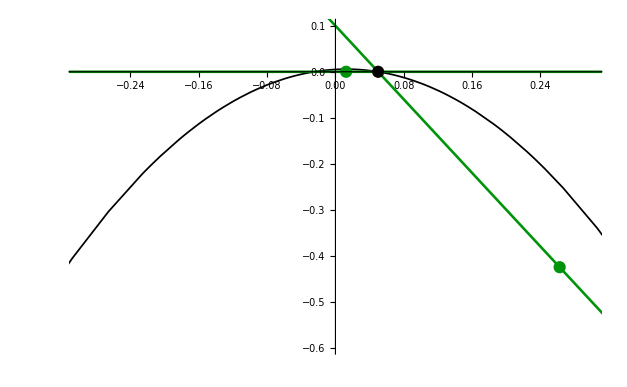

```mathematica
(* tests *)
With[{mu=-1/10,m2=0,psi=0},Module[{helixGam,labeledHelixRays,initialPositions, inter},
helixGam={-Ch[0,0],Ch[1,0]};

labeledHelixRays = Echo@Table[Tooltip[XYRay[c/.repCh, mu,z], c], {c,helixGam}];
initialPositions=Table[InitialPositionXY[c/.repCh, mu],{c,helixGam}];
inter = Echo@IntersectRaysNoTest[First@helixGam/.repCh,Last@helixGam/.repCh, First@initialPositions,Last@initialPositions,mu];

Show[
Plot[XYParabolaY[x,mu,m2,psi], {x,-1,1},
PlotStyle->Directive[Thickness[.002],Black],
PlotRange->{{-.3,.3},{-.6,.1}},
GridLines->{{-1/2,1/2},None},
GridLinesStyle->Directive[Thickness[.002],Black, Dashed]
],
ParametricPlot[labeledHelixRays, {z,-1,1},
PlotStyle->Directive[Thickness[.003],RGBColor[0, 0.582, 0.041]]
],
Graphics[{RGBColor[0, 0.582, 0.041],PointSize[.014],Point[initialPositions],Black,Point[inter]}]
]
]]
```

```mathematica
(* smin_,smax_,phimax_,Nm_,m_,ListRays0_ *)
```

```mathematica
ClearAll[Rayxy];
(* redefine Rayxy such that second argument is z={x,y} *)
Rayxy[{r_,dF_,dB_,ch2_},{x0_,y0_},L_,m_]:=
{Hue[1-(CostPhi[{r,dF,dB,ch2},x0,m])/4.6],Point[{x0,y0}],Line[{{x0,y0},{x0-r L,y0+L(2dF+dB)}}]};
With[{m=-1/10},
ListRays = ConstructLVDiagram[-2-.001,2+.001,16,6,m,{}];
Show[Plot[1/4 (2 m^2-4 m s-16 s^2),{s,-2,2},PlotRange->{{-2,2},{-2,2}}],Graphics[Table[Rayxy[ListRays[[i,1]],ListRays[[i,2]],1,m],{i,Length[ListRays]}]]]]
```

Adding 205 rays,

Adding 473 rays,

Adding 505 rays,

$Aborted

```mathematica
Length[ListRays]
```

263

```mathematica
XYParabolaY[]
```

```mathematica
r y+(2dF+dB)x+(dF-dB)mu-ch2
```

#### X Y range of coordinates

```mathematica
(* y = -Re[Exp[-I psi] TD]/Cos[psi] *)
1/2 (m1^2-m2^2-2 m1 s-8 s^2+2 m2 t+8 t^2)+(m1 (m2-t)-s (m2+8 t)) Tan[psi]/.{psi->0}
Solve[y==%,t]
t/.Last[%]
```

1/2 (m1^2-m2^2-2 m1 s-8 s^2+2 m2 t+8 t^2)

{{t→1/8 (-m2-√(-8 m1^2+9 m2^2+16 m1 s+64 s^2+16 y))},{t→1/8 (-m2+√(-8 m1^2+9 m2^2+16 m1 s+64 s^2+16 y))}}

1/8 (-m2+√(-8 m1^2+9 m2^2+16 m1 s+64 s^2+16 y))

```mathematica
Simplify@Solve[y==1/2 (m1^2-m2^2-2 m1 s-8 s^2+2 m2 t+8 t^2),t]
```

{{t→1/8 (-m2-√(-8 m1^2+9 m2^2+16 m1 s+64 s^2+16 y))},{t→1/8 (-m2+√(-8 m1^2+9 m2^2+16 m1 s+64 s^2+16 y))}}

```mathematica
-8 m1^2+9 m2^2+16 m1 s+64 s^2+16 y/.{m2->0}
```

```mathematica
1/8 (-m2+√(-8 m1^2+9 m2^2+16 m1 s+64 s^2+16 y))
```

```mathematica
ZLV[{r,dF,dB,ch2},T,m]
Coefficient[%,{r,dF,dB,ch2}]
```

-ch2+dF m+(m^2 r)/2+2 dF T-m r T-4 r T^2+dB (-m+T)

{m^2/2-m T-4 T^2,m+2 T,-m+T,-1}

```mathematica
FullSimplify[1/2 (m1^2-m2^2-2 m1 s-8 s^2+2 m2 t+8 t^2)+(m1 (m2-t)-s (m2+8 t)) Tan[psi]/.{s->x-t Tan[psi],m1->mu-m2 Tan[psi]}]
```

1/2 ((mu-4 x) (mu+2 x)-(m2-4 t) (m2+2 t) Sec[psi]^2)

```mathematica
CostPhi[{r,dF,dB,ch2},x,mu]
```

dB+2 dF-r (mu+8 x)

```mathematica
Simplify[ComplexExpand[Im[Exp[-I psi]ZLV[{r,dF,dB,ch2},T,m]]/Im[T]/.{T->s+I t,m->m1+I m2}]]
Simplify[%/.{s->x-t Tan[psi],m1->mu-m2 Tan[psi]}]
```

1/(2 t)(2 (m1 r (m2-t)+dB (-m2+t)+dF (m2+2 t)-r s (m2+8 t)) Cos[psi]+(2 ch2-2 dF m1-m1^2 r+m2^2 r+2 dB (m1-s)-4 dF s+2 m1 r s+8 r s^2-2 m2 r t-8 r t^2) Sin[psi])

1/(8 t)Sec[psi] (8 (dB (-m2+t)+dF (m2+2 t)+m2 r (mu-x)-r t (mu+8 x))+(2 ch2+2 dB (mu-x)-(mu+2 x) (2 dF+mu r-4 r x)) Sec[psi] Sin[3 psi]+(2 ch2-2 dF mu-4 m2^2 r-mu^2 r+8 m2 r t+32 r t^2+2 dB (mu-x)-4 dF x+2 mu r x+8 r x^2) Tan[psi])

```mathematica
Solve[r y+(2dF+dB)x+(dF-dB)mu-ch2==0,y]
```

{{y→(ch2+dB mu-dF mu-dB x-2 dF x)/r}}

## F0 orbits under GL(2,R)

```mathematica
2Im[td t1*]/Im[t2]/.{td->1/2t1 t2}/.{t1->t,t2->t+m}/.{t->s+I t,m->m1+I m2}
Simplify@ComplexExpand[%]
```

Im[(s+ⅈ t) (m1+ⅈ m2+s+ⅈ t) (Conjugate[s]-ⅈ Conjugate[t])]/(Im[m1+s]+Re[m2]+Re[t])

s^2+t^2

```mathematica
Im[td+1/2t1*t2]/Im[t2]/.{td->1/2t1 t2}/.{t1->t,t2->t+m}/.{t->s+I t,m->m1+I m2}
Simplify@ComplexExpand[%]
```

Im[1/2 (s+ⅈ t) (m1+ⅈ m2+s+ⅈ t)+1/2 (m1+ⅈ m2+s+ⅈ t) (Conjugate[s]-ⅈ Conjugate[t])]/(Im[m1+s]+Re[m2]+Re[t])

s

```mathematica
(* for local F0 *)
```

```mathematica
ComplexExpand[ReIm[-2r tdp+d1 t1p+d2 t2p-ch2],{tdp,t1p,t2p}]
A1 = {Coefficient[%,ch2],Coefficient[%,d1],Coefficient[%,d2],Coefficient[%,r]}
```

{-ch2+d1 Re[t1p]+d2 Re[t2p]-2 r Re[tdp],d1 Im[t1p]+d2 Im[t2p]-2 r Im[tdp]}

{{-1,0},{Re[t1p],Im[t1p]},{Re[t2p],Im[t2p]},{-2 Re[tdp],-2 Im[tdp]}}

```mathematica
sol={a[1,1]->1,a[2,1]->0};
g = (Array[a,{2,2}]/.sol);MatrixForm[g]
A = g.ComplexExpand[ReIm[-2r td+d1 t1+d2 t2-ch2], {td,t1,t2}]
A2 = {Coefficient[%,ch2],Coefficient[%,d1],Coefficient[%,d2],Coefficient[%,r]}
```

(1 | a[1,2]
0 | a[2,2])

{-ch2+a[1,2] (d1 Im[t1]+d2 Im[t2]-2 r Im[td])+d1 Re[t1]+d2 Re[t2]-2 r Re[td],a[2,2] (d1 Im[t1]+d2 Im[t2]-2 r Im[td])}

{{-1,0},{a[1,2] Im[t1]+Re[t1],a[2,2] Im[t1]},{a[1,2] Im[t2]+Re[t2],a[2,2] Im[t2]},{-2 a[1,2] Im[td]-2 Re[td],-2 a[2,2] Im[td]}}

```mathematica
A3=First@Solve[Thread[Flatten[A1-A2]==0][[3;;6]],{Re[t1p],Im[t1p],Re[t2p],Im[t2p]}]
Simplify@ComplexExpand[Thread[Flatten[A1-A2]][[7;;8]]/.{tdp->1/2 t1p t2p},{t1p,t2p,td}]
Simplify[%/.A3]/.{a[1,2]->x,a[2,2]->y}/.{x->-(-2 Im[td]+Im[t2] Re[t1]+Im[t1] Re[t2])/(2 Im[t1] Im[t2])}//Simplify
Simplify@Solve[%[[1]]==0,y]
```

{Re[t1p]→a[1,2] Im[t1]+Re[t1],Im[t1p]→a[2,2] Im[t1],Re[t2p]→a[1,2] Im[t2]+Re[t2],Im[t2p]→a[2,2] Im[t2]}

{Im[t1p] Im[t2p]+2 a[1,2] Im[td]-Re[t1p] Re[t2p]+2 Re[td],2 a[2,2] Im[td]-Im[t2p] Re[t1p]-Im[t1p] Re[t2p]}

{((-2 Im[td]+Im[t2] Re[t1])^2+Im[t1]^2 (4 y^2 Im[t2]^2+Re[t2]^2)-2 Im[t1] (2 Im[td] Re[t2]+Im[t2] (Re[t1] Re[t2]-4 Re[td])))/(4 Im[t1] Im[t2]),0}

{{y→-(√(-4 Im[td]^2-Im[t2]^2 Re[t1]^2-Im[t1]^2 Re[t2]^2+4 Im[td] (Im[t2] Re[t1]+Im[t1] Re[t2])+2 Im[t1] Im[t2] (Re[t1] Re[t2]-4 Re[td])))/(2 Im[t1] Im[t2])},{y→(√(-4 Im[td]^2-Im[t2]^2 Re[t1]^2-Im[t1]^2 Re[t2]^2+4 Im[td] (Im[t2] Re[t1]+Im[t1] Re[t2])+2 Im[t1] Im[t2] (Re[t1] Re[t2]-4 Re[td])))/(2 Im[t1] Im[t2])}}

```mathematica
sol={a[1,1]->1,a[2,1]->0,a[1,2]->-(-2 Im[td]+Im[t2] Re[t1]+Im[t1] Re[t2])/(2 Im[t1] Im[t2]),a[2,2]->(√(-4 Im[td]^2-Im[t2]^2 Re[t1]^2-Im[t1]^2 Re[t2]^2+4 Im[td] (Im[t2] Re[t1]+Im[t1] Re[t2])+2 Im[t1] Im[t2] (Re[t1] Re[t2]-4 Re[td])))/(2 Im[t1] Im[t2])};
```

```mathematica
4 ComplexExpand[2Im[td t1*]Im[t2]-Im[td+1/2t1*t2]^2,{td,t1,t2}]//Simplify
```

-4 Im[td]^2-Im[t2]^2 Re[t1]^2-Im[t1]^2 Re[t2]^2+4 Im[td] (Im[t2] Re[t1]+Im[t1] Re[t2])+2 Im[t1] Im[t2] (Re[t1] Re[t2]-4 Re[td])

```mathematica
(* |T1_LV^2|^2 *)
```

```mathematica
Simplify[Re[t1p]^2+Im[t1p]^2/.A3/.sol]
```

(2 Im[td] Re[t1]-2 Im[t1] Re[td])/Im[t2]

```mathematica
Simplify[ComplexExpand[2Im[td t1*]/Im[t2],{t1,t2,td}]]
```

(2 Im[td] Re[t1]-2 Im[t1] Re[td])/Im[t2]

```mathematica
(* Re(T1_LV^2) *)
```

```mathematica
Simplify[Re[t1p]/.A3/.sol]
```

(2 Im[td]+Im[t2] Re[t1]-Im[t1] Re[t2])/(2 Im[t2])

```mathematica
Simplify[ComplexExpand[2Im[td+1/2 t1*t2]/Im[t2],{t1,t2,td}]]
```

(2 Im[td]+Im[t2] Re[t1]-Im[t1] Re[t2])/Im[t2]

```mathematica
(* for local F1 *)
```

```mathematica
ComplexExpand[ReIm[-r TDp+dF TFp+dB TBp-ch2],{TFp,TBp,TDp}]
A1 = {Coefficient[%,ch2],Coefficient[%,dF],Coefficient[%,dB],Coefficient[%,r]}
```

{-ch2+dB Re[TBp]-r Re[TDp]+dF Re[TFp],dB Im[TBp]-r Im[TDp]+dF Im[TFp]}

{{-1,0},{Re[TFp],Im[TFp]},{Re[TBp],Im[TBp]},{-Re[TDp],-Im[TDp]}}

```mathematica
sol={a[1,1]->1,a[2,1]->0};
g = (Array[a,{2,2}]/.sol);MatrixForm[g]
A = g.ComplexExpand[ReIm[-r TD+dF TF+dB TB-ch2], {TD,TF,TB}]
A2 = {Coefficient[%,ch2],Coefficient[%,dF],Coefficient[%,dB],Coefficient[%,r]}
```

(1 | a[1,2]
0 | a[2,2])

{-ch2+a[1,2] (dB Im[TB]-r Im[TD]+dF Im[TF])+dB Re[TB]-r Re[TD]+dF Re[TF],a[2,2] (dB Im[TB]-r Im[TD]+dF Im[TF])}

{{-1,0},{a[1,2] Im[TF]+Re[TF],a[2,2] Im[TF]},{a[1,2] Im[TB]+Re[TB],a[2,2] Im[TB]},{-a[1,2] Im[TD]-Re[TD],-a[2,2] Im[TD]}}

```mathematica
A3=First@Solve[Thread[Flatten[A1-A2]==0][[3;;6]],{Re[TFp],Im[TFp],Re[TBp],Im[TBp]}]
Simplify@ComplexExpand[Thread[Flatten[A1-A2]][[7;;8]]/.{TDp->1/2 TFp^2+TBp TFp},{TFp,TBp,TD}]
Simplify[%/.A3/.{a[1,2]->x,a[2,2]->y}/.{x->(Im[TD]-Im[TB] Re[TF]-Im[TF] (Re[TB]+Re[TF]))/(Im[TF] (2 Im[TB]+Im[TF]))}]
y/.Last@Simplify@Solve[%[[1]]==0,y]
```

{Re[TFp]→a[1,2] Im[TF]+Re[TF],Im[TFp]→a[2,2] Im[TF],Re[TBp]→a[1,2] Im[TB]+Re[TB],Im[TBp]→a[2,2] Im[TB]}

{a[1,2] Im[TD]+Im[TBp] Im[TFp]+Im[TFp]^2/2+Re[TD]-Re[TBp] Re[TFp]-Re[TFp]^2/2,a[2,2] Im[TD]-Im[TBp] Re[TFp]-Im[TFp] (Re[TBp]+Re[TFp])}

{1/(2 Im[TF] (2 Im[TB]+Im[TF]))(Im[TD]^2+Im[TF]^2 (y^2 Im[TF]^2+Re[TB]^2+2 Re[TD])+2 Im[TB] Im[TF] (2 y^2 Im[TF]^2+2 Re[TD]-Re[TB] Re[TF])+Im[TB]^2 (4 y^2 Im[TF]^2+Re[TF]^2)-2 Im[TD] (Im[TB] Re[TF]+Im[TF] (Re[TB]+Re[TF]))),0}

√(-1/(Im[TF]^2 (2 Im[TB]+Im[TF])^2)(Im[TD]^2+Im[TF]^2 (Re[TB]^2+2 Re[TD])+Im[TB]^2 Re[TF]^2+2 Im[TB] Im[TF] (2 Re[TD]-Re[TB] Re[TF])-2 Im[TD] (Im[TB] Re[TF]+Im[TF] (Re[TB]+Re[TF]))))

```mathematica
sol={a[1,1]->1,a[2,1]->0,a[1,2]->(Im[TD]-Im[TB] Re[TF]-Im[TF] (Re[TB]+Re[TF]))/(Im[TF] (2 Im[TB]+Im[TF])),a[2,2]->√(-1/(Im[TF]^2 (2 Im[TB]+Im[TF])^2)(Im[TD]^2+Im[TF]^2 (Re[TB]^2+2 Re[TD])+Im[TB]^2 Re[TF]^2+2 Im[TB] Im[TF] (2 Re[TD]-Re[TB] Re[TF])-2 Im[TD] (Im[TB] Re[TF]+Im[TF] (Re[TB]+Re[TF]))))};
```

```mathematica
A5=ComplexExpand[2Im[TD TF*]/Im[2TB+TF]-Im[TD+b/2TF*TB]^2,{TD,TF,TB}]//Expand
```

-Im[TD]^2+b Im[TD] Im[TF] Re[TB]-1/4 b^2 Im[TF]^2 Re[TB]^2-a Im[TB] Im[TF] Re[TD]+a Im[TB] Im[TD] Re[TF]-b Im[TB] Im[TD] Re[TF]+1/2 b^2 Im[TB] Im[TF] Re[TB] Re[TF]-1/4 b^2 Im[TB]^2 Re[TF]^2

```mathematica
Simplify[A4-A5]
```

1/4 (Im[TF]^2 ((-4+b^2) Re[TB]^2-8 Re[TD])+(-4+b^2) Im[TB]^2 Re[TF]^2+2 Im[TB] Im[TF] (2 (-4+a) Re[TD]-(-4+b^2) Re[TB] Re[TF])+Im[TD] (4 (2-a+b) Im[TB] Re[TF]+Im[TF] (-4 (-2+b) Re[TB]+8 Re[TF])))

```mathematica
Simplify[Re[TFp]^2+Im[TFp]^2/.A3/.sol]
```

(2 (-Im[TF] Re[TD]+Im[TD] Re[TF]))/(2 Im[TB]+Im[TF])

```mathematica
Simplify[ComplexExpand[2Im[TD TF*]/Im[2TB+TF],{}]]
```

```mathematica
Simplify[Re[TFp]/.A3/.sol]
```

(Im[TD]-Im[TF] Re[TB]+Im[TB] Re[TF])/(2 Im[TB]+Im[TF])

```mathematica
(2 Im[td] Re[t1]-2 Im[t1] Re[td])/Im[t2],(2 Im[td]+Im[t2] Re[t1]-Im[t1] Re[t2])/(2 Im[t2])
```

```mathematica
2Im[TD TF*]/Im[2TB+TF]/.{TF->2T+m,TB->T-m}/.{TD->ZLV[{-1,0,0,0},T,m]}/.{T->s+I t,m->m1+I m2}
FullSimplify[ComplexExpand[%]]
```

(2 Im[(-1/2 (m1+ⅈ m2)^2+(m1+ⅈ m2) (s+ⅈ t)+4 (s+ⅈ t)^2) (Conjugate[m1]-ⅈ Conjugate[m2]+2 (Conjugate[s]-ⅈ Conjugate[t]))])/(Im[m1]+Re[m2]+2 (Im[s]+Re[t])+2 (Im[-m1+s]-Re[m2]+Re[t]))

(m1+2 s)^2+(m2+2 t)^2

## O(p,q) production from the initial rays

```mathematica
KroneckerDims[3,10]
```

{{1,1},{1,2},{1,3},{2,1},{2,3},{2,5},{3,1},{3,2},{3,4},{3,5},{3,7},{4,3},{4,5},{5,2},{5,3},{5,4},{7,3}}

```mathematica
(#.{-Ch[0,0],Ch[1,1]}/.repCh)&/@KroneckerDims[3,10]
Select[%, #[[1]]==1&]
BogomolovDiscriminant/@%
```

{{0,1,1,1/2},{1,2,2,1},{2,3,3,3/2},{-1,1,1,1/2},{1,3,3,3/2},{3,5,5,5/2},{-2,1,1,1/2},{-1,2,2,1},{1,4,4,2},{2,5,5,5/2},{4,7,7,7/2},{-1,3,3,3/2},{1,5,5,5/2},{-3,2,2,1},{-2,3,3,3/2},{-1,4,4,2},{-4,3,3,3/2}}

{{1,2,2,1},{1,3,3,3/2},{1,4,4,2},{1,5,5,5/2}}

{1,3,6,10}

```mathematica
Simplify@BogomolovDiscriminant[{k,k+1}.{-Ch[0,0],Ch[1,1]}/.repCh]
```

1/2 k (1+k)

```mathematica
Simplify@BogomolovDiscriminant[{k,k+1}.{Ch[3,2],-Ch[2,1]}/.repCh]
```

1/2 k (1+k)

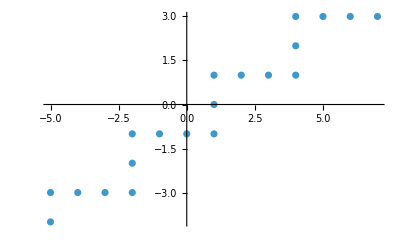

```mathematica
Select[ListRays, First[#][[1]]==1&&BogomolovDiscriminant[First[#]]==0&];
ListPlot[%[[All,1,2;;3]]]
```

```mathematica
{#,InitialPositionXY[#],0,0,0,0,0}&/@{Ch[]}
```

```mathematica
ConstructLVDiagram[-2-.001,2+.001,10,6,-1/10,{}]
```

```mathematica
InitRays={{{1,-5,-4,12},{-139/80,-497/40},0,0,0,0,0},{{1,-2,-2,2},{-59/80,-97/40},0,0,0,0,0},{{1,1,0,0},{21/80,-17/40},0,0,0,0,0},{{1,4,2,6},{101/80,-257/40},0,0,0,0,0},{{-1,5,4,-12},{-139/80,-497/40},0,0,0,0,0},{{-1,2,2,-2},{-59/80,-97/40},0,0,0,0,0},{{-1,-1,0,0},{21/80,-17/40},0,0,0,0,0},{{-1,-4,-2,-6},{101/80,-257/40},0,0,0,0,0},{{1,-5,-3,21/2},{-129/80,-853/80},0,0,0,0,0},{{1,-2,-1,3/2},{-49/80,-133/80},0,0,0,0,0},{{1,1,1,1/2},{31/80,-53/80},0,0,0,0,0},{{1,4,3,15/2},{111/80,-613/80},0,0,0,0,0},{{-1,5,3,-21/2},{-129/80,-853/80},0,0,0,0,0},{{-1,2,1,-3/2},{-49/80,-133/80},0,0,0,0,0},{{-1,-1,-1,-1/2},{31/80,-53/80},0,0,0,0,0},{{-1,-4,-3,-15/2},{111/80,-613/80},0,0,0,0,0},{{1,-4,-3,15/2},{-109/80,-607/80},0,0,0,0,0},{{1,-1,-1,1/2},{-29/80,-47/80},0,0,0,0,0},{{1,2,1,3/2},{51/80,-127/80},0,0,0,0,0},{{1,5,3,21/2},{131/80,-847/80},0,0,0,0,0},{{-1,4,3,-15/2},{-109/80,-607/80},0,0,0,0,0},{{-1,1,1,-1/2},{-29/80,-47/80},0,0,0,0,0},{{-1,-2,-1,-3/2},{51/80,-127/80},0,0,0,0,0},{{-1,-5,-3,-21/2},{131/80,-847/80},0,0,0,0,0}};
```

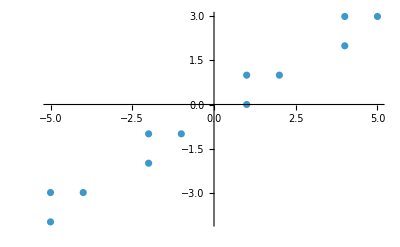

```mathematica
Select[InitRays, First[#][[1]]==1&&BogomolovDiscriminant[First[#]]==0&];
ListPlot[%[[All,1,2;;3]]]
```

#### Redo

```mathematica
temp=With[{smin=-2,smax=2,m=-1/10},Flatten[{
Table[{Ch[3k,2k],{k-m/8,-4 k^2},0,0,0,0,0},{k,Ceiling[(smin+m/8)],Floor[(smax+m/8)]}],
Table[{Ch[3k,2k][1],{k-m/8,-4 k^2},0,0,0,0,0},{k,Ceiling[(smin+m/8)],Floor[(smax+m/8)]}],
Table[{Ch[3k+1,2k],{1/4+k-m/8,-1/2-2 k-4 k^2-(3 m)/4},0,0,0,0,0},{k,Ceiling[-1/4+m/8+smin],Floor[-1/4+m/8+smax]}],
Table[{Ch[3k+1,2k][1],{1/4+k-m/8,-1/2-2 k-4 k^2-(3 m)/4},0,0,0,0,0},{k,Ceiling[-1/4+m/8+smin],Floor[-1/4+m/8+smax]}],
Table[{Ch[3k+1,2k+1],{3/8+k-m/8,-5/8-3 k-4 k^2+(3 m)/8},0,0,0,0,0},{k,Ceiling[-3/8+m/8+smin],Floor[-3/8+m/8+smax]}],Table[{Ch[3k+1,2k+1][1],{3/8+k-m/8,-5/8-3 k-4 k^2+(3 m)/8},0,0,0,0,0},{k,Ceiling[-3/8+m/8+smin],Floor[-3/8+m/8+smax]}],Table[{Ch[3k+2,2k+1],{5/8+k-m/8,-13/8-5 k-4 k^2-(3 m)/8},0,0,0,0,0},{k,Ceiling[-5/8+m/8+smin],Floor[-5/8+m/8+smax]}],Table[{Ch[3k+2,2k+1][1],{5/8+k-m/8,-13/8-5 k-4 k^2-(3 m)/8},0,0,0,0,0},{k,Ceiling[-5/8+m/8+smin],Floor[-5/8+m/8+smax]}]},1]/.repCh];
```

```mathematica
CollDBridgeland
Sort[{Ch[0,0],Ch[1,0],Ch[1,1],Ch[2,1]}/.repCh]==Sort[%]
```

{{1,0,0,0},{1,1,0,0},{1,1,1,1/2},{1,2,1,3/2}}

True

```mathematica
initRays = InitialRaysFromColl[CollDBridgeland/.repCh, -2,2,-1/10];
First[InitialPositionXY[#,-1/10]]&/@initRays[[All,1]]//DeleteDuplicates//Sort//N
```

{-1.9875,-1.7375,-1.6125,-1.3625,-0.9875,-0.7375,-0.6125,-0.3625,0.0125,0.2625,0.3875,0.6375,1.0125,1.2625,1.3875,1.6375}

```mathematica
Sort[initRays]==Sort[temp]
```

True

```mathematica
ListRays=ConstructLVDiagram[15,6,-1/10,initRays];
```

Adding 356 rays,

Adding 1310 rays,

Aborted — returning partial ListRays (1698).

```mathematica
ListRays=ConstructLVDiagram[15,6,-1/10,initRays];
```

Adding 356 rays,

Aborted — returning partial ListRays (388).

```mathematica
ListRays=ConstructLVDiagramOpt[15,6,-1/10,initRays];
```

Adding 356 rays,

Adding 1310 rays,

Adding 708 rays,

Aborted -- returning partial ListRays (2406).

```mathematica
Lookup
```

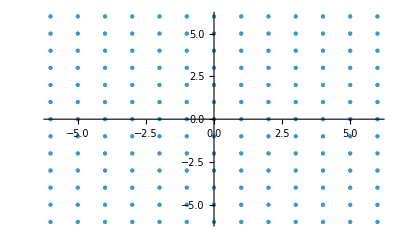

```mathematica
charges=Flatten[Table[s Ch[p,q],{p,-6,6},{q,-6,6},{s,{-1,1}}]];
Select[charges,FreeQ[InitialPosition[#,-1/10],Complex]&];
ListPlot[charges/.{Ch[p_,q_]:>{p,q}}]
```

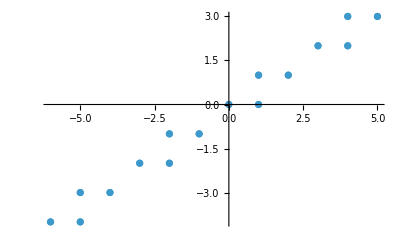

```mathematica
Select[initRays[[All,1]], Abs[#[[1]]]==1&&BogomolovDiscriminant[#]==0&];
ListPlot[%/.{r_,dF_,dB_,ch2_}:>{dF/r,dB/r}]
```

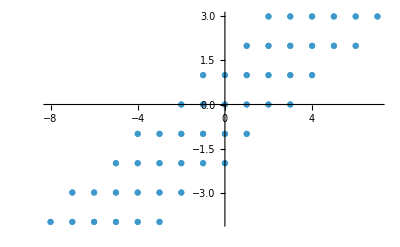

```mathematica
Select[ListRays[[All,1]], Abs[#[[1]]]==1&&BogomolovDiscriminant[#]==0&];
ListPlot[%/.{r_,dF_,dB_,ch2_}:>{dF/r,dB/r}]
```

```mathematica
SimpleRays=Select[ListRays, Abs[#[[1,1]]]==1&&BogomolovDiscriminant[#[[1]]]==0&];
```

```mathematica
XYRay[{r,dF,dB,ch2},{x,y},mu]
```

-ch2+(-dB+dF) mu+(dB+2 dF) x+r y

```mathematica
raySeg[{{0,dF,dB,ch2},{x0,y0},p1,p2,n1,n2,d},mu,L]
```

{Directive[GrayLevel[0],Thickness[0.002]],Line[{{x0,y0},{x0,y0+((dB+2 dF) L)/Abs[dB+2 dF]}}]}

```mathematica
Lighter[DarkGreen]
```

RGBColor[Rational[1, 3], 0.5666666666666667, Rational[1, 3]]

```mathematica
ClearAll[raySeg];
raySeg[{c:{r_,dF_,dB_,ch2_},z:{x0_,y0_},___,depth_},mu_,L_:10,styleMap_:<||>,defaultStyle_:Directive[Black,Thickness[.002]]]:=Module[{v,sty},
v={-r,dB+2 dF};
sty=Lookup[styleMap,depth,defaultStyle];
{sty,Line[{z,z+L Normalize[v]}]}];

styleMap=<|
0->Directive[Black,Thickness[.003]],
1->Directive[Opacity[.6, Lighter[DarkRed]],Thickness[.0025]],
2->Directive[Opacity[.3,Lighter[DarkGreen]],Thickness[.002]],
3->Directive[Opacity[.1,Lighter[Green]],Thickness[.0015]]
|>;
plt = With[{mu=-1/10, rays=Select[ListRays, Last[#]<=1&]},
Show[
Plot[XYParabolaY[x,mu,0,0],{x,-2,2},
PlotRange->{{-1,1},{-3,2}},
PlotStyle->Directive[Dashed,Thick,Black]
],
Graphics[{
Tooltip[raySeg[#,mu,20,styleMap], #[[1]]]&/@rays,    (*rays*)
PointSize[.01],
Point[#[[2]]&/@rays]                   (*initial positions*)
}],
Axes->True
]];
```

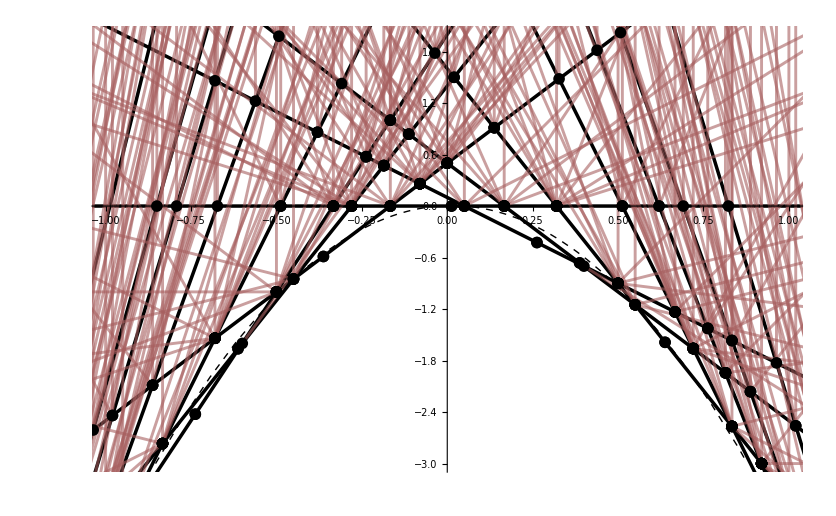

```mathematica
plt
```

```mathematica
ClearAll[raySeg];
raySeg[{c:{r_,dF_,dB_,ch2_},z:{x0_,y0_},___,depth_},mu_,L_:10,styleMap_:<||>,defaultStyle_:Directive[Black,Thickness[.002]]]:=Module[{v,sty},
v={-r,dB+2 dF};
sty=Lookup[styleMap,depth,defaultStyle];
{sty,Line[{z,z+L Normalize[v]}]}];

styleMap=<|
0->Directive[Black,Thickness[.003]],
1->Directive[Opacity[.6, Lighter[DarkRed]],Thickness[.0025]],
2->Directive[Opacity[.3,Lighter[DarkGreen]],Thickness[.002]],
3->Directive[Opacity[.1,Lighter[Green]],Thickness[.0015]]
|>;
plt = Manipulate[
initRays = InitialRaysFromColl[CollDBridgeland/.repCh, -2,2,mu];
Show[
Plot[XYParabolaY[x,mu,0,0],{x,-2,2},
PlotRange->{{-1,1},{-3,2}},
PlotStyle->Directive[Dashed,Thick,Black]
],
Graphics[{
Tooltip[raySeg[#,mu,20,styleMap], #[[1]]]&/@initRays,    (*rays*)
PointSize[.01],
Point[#[[2]]&/@initRays]                   (*initial positions*)
}],
Axes->True
], {{mu,-1/10}, -2, 2, .001}]
```

```mathematica
Show[plt,PlotRange->]
```

```mathematica
Cases[ListRays,-Ch[0,1]/.repCh,Infinity]
```

{{-1,0,-1,1/2}}

```mathematica
LVTreesFromListRays[ListRays, -Ch[0, 1]/.repCh,-1/10]
ChernToCh[%]
```

{{{-2,-2,-2,-1},{1,2,1,3/2}}}

{{2 Ch[1,1][1],Ch[2,1]}}

```mathematica
LVTreesFromListRays[ListRays, Ch[2,0]/.repCh,-1/10]
ChernToCh[%]
```

{{{-1,0,0,0},{2,2,0,0}}}

{{Ch[0,0][1],2 Ch[1,0]}}

```mathematica
DSZ[Ch[0,0][1],Ch[1,0]]/.repCh
```

-2

```mathematica
ComplexExpand[Im[ZLV[{r,dF,dB,ch2},T,m]]/Im[T],{T}]//Simplify
D[%/.{Re[T]->x,m->mu},{{x,y}}].{-r,(dB+2dF)}//Simplify
```

dB+2 dF-m r-8 r Re[T]

8 r^2

```mathematica
Simplify@ComplexExpand[Re[Exp[-I psi] (s+I t)]/Cos[psi]]
```

s+t Tan[psi]

## m = 1/10

```mathematica
ClearAll[gamToString];
gamToString = {
-Ch[p_,q_]:>"("<>ToString[p]<>", "<>ToString[q]<>")[1]",
Ch[p_,q_]:>"("<>ToString[p]<>", "<>ToString[q]<>")"
};
```

```mathematica
ClearAll[GamCaption];
GamCaption[gam_,t_,psi_,m_] := Module[{s, tt,pos, dir, normal},
s = Sign[gam[[1]]];
pos[tt_]={Rays[gam/.repCh,tt,psi, m],tt};
dir = Normalize[D[pos[tt],tt]/.{tt->t}];
normal={dir[[2]],-dir[[1]]};
Text[gam/.gamToString, pos[t], -s*1.5*normal, -s*dir]
]
```

#### Rays in the T plane

```mathematica
(* ChatGPT *)
ClearAll[QuiverDomain];
Options[QuiverDomain]={PlotStyle->LightBlue,PlotRange->{{-1.5,1.5},{0,1}},PlotPoints->100};
QuiverDomain[coll_,psi_,m_,OptionsPattern[]]:=Module[{sty=OptionValue[PlotStyle],pr=OptionValue[PlotRange],pp=OptionValue[PlotPoints],z=ZLV[#,{s,t},m]&/@coll},RegionPlot[t>0&&AllTrue[z,Re[Exp[-I psi] #]<0&],{s,pr[[1,1]],pr[[1,2]]},{t,pr[[2,1]],pr[[2,2]]},
PlotPoints->pp,
AspectRatio->1,
PlotStyle->{sty,Opacity[.5]},
BoundaryStyle->None
]];
```

```mathematica
With[{L=6},Flatten[Table[{mF,mB},{mF,-L,L},{mB,-L,L}],1]];
specII = Select[%, With[{z=ZLV[#,{s,t},1/10]&/@SpectralFlow[CollArcaraII, #]}, FullSimplify@ComplexExpand[AllTrue[z,Re[#]<0&]&&(-0.2<=s<=1.2&&0<=t<=0.5)]]=!=False&]
domsII = Table[QuiverDomain[SpectralFlow[CollArcaraII, spec],0,1/10,PlotStyle->LightRed,PlotRange->{{-0.2,1.2},{0,.5}}], {spec,specII}];
```

{{-6,4},{-6,5},{-6,6},{-5,4},{-5,5},{-5,6},{-4,4},{-4,5},{-4,6},{-3,4},{-3,5},{-3,6},{-2,4},{-2,5},{-2,6},{-1,4},{-1,5},{-1,6},{0,0},{0,4},{0,5},{0,6},{1,1},{1,4},{1,5},{1,6},{2,2},{2,5},{2,6},{3,2},{4,3}}

```mathematica
With[{L=6},Flatten[Table[{mF,mB},{mF,-L,L},{mB,-L,L}],1]];
specI = Select[%, With[{z=ZLV[#,{s,t},1/10]&/@SpectralFlow[CollArcaraI, #]}, FullSimplify@ComplexExpand[AllTrue[z,Re[#]<0&]&&(-0.2<=s<=1.2&&0<=t<=0.5)]]=!=False&]
domsI = Table[QuiverDomain[SpectralFlow[CollArcaraI, spec],0,1/10,PlotStyle->LightGreen,PlotRange->{{-0.2,1.2},{0,.5}}], {spec,specI}];
```

{{1,-6},{1,0},{2,-6},{2,-5},{2,-4},{2,1},{3,-6},{3,-5},{3,-4},{3,-3},{3,-2},{3,2},{4,-6},{4,-5},{4,-4},{4,-3},{4,-2},{4,-1},{4,2},{5,-6},{5,-5},{5,-4},{5,-3},{5,-2},{5,-1},{5,3},{6,-6},{6,-5},{6,-4},{6,-3},{6,-2},{6,-1}}

```mathematica
With[{L=6},Flatten[Table[{mF,mB},{mF,-L,L},{mB,-L,L}],1]];
specBr = Select[%, With[{z=ZLV[#,{s,t},1/10]&/@SpectralFlow[CollBridgeland, #]}, FullSimplify@ComplexExpand[AllTrue[z,Re[#]<0&]&&(-0.2<=s<=1.2&&0<=t<=0.5)]]=!=False&]
domsBr = Table[QuiverDomain[SpectralFlow[CollBridgeland, spec],0,1/10,PlotStyle->LightBlue,PlotRange->{{-0.2,1.2},{0,.5}}], {spec,specBr}];
```

{{-6,-6},{-6,-5},{-6,-3},{-6,-2},{-6,-1},{-6,0},{-6,4},{-6,5},{-6,6},{-5,-6},{-5,-5},{-5,-4},{-5,-2},{-5,-1},{-5,0},{-5,4},{-5,5},{-5,6},{-4,-5},{-4,-4},{-4,-3},{-4,-1},{-4,0},{-4,4},{-4,5},{-4,6},{-3,-3},{-3,-1},{-3,0},{-3,4},{-3,5},{-3,6},{-2,4},{-2,5},{-2,6},{-1,4},{-1,5},{-1,6},{0,-6},{0,-5},{0,0},{0,4},{0,5},{0,6},{1,-6},{1,-5},{1,-4},{1,-3},{1,1},{1,4},{1,5},{1,6},{2,-6},{2,-5},{2,-4},{2,-3},{2,-2},{2,-1},{2,2},{2,4},{2,5},{2,6},{3,-6},{3,-5},{3,-4},{3,-3},{3,-2},{3,-1},{3,2},{3,6},{4,-6},{4,-5},{4,-4},{4,-3},{4,-2},{4,-1},{4,3},{5,-6},{5,-5},{5,-4},{5,-3},{5,-2},{5,-1},{6,-6},{6,-5},{6,-4},{6,-3},{6,-2},{6,-1}}

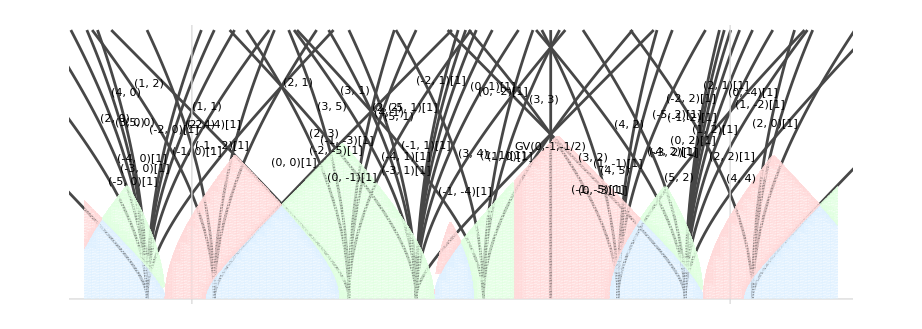

```mathematica
charges=With[{L=5},Flatten[Table[s Ch[p,q],{p,-L,L},{q,-L,L},{s,{-1,1}}]]];
With[{m=1/6, psi=0},
charges=Select[charges, -0.2<=Rays[#/.repCh,0,psi,m]<=1.2&];
AppendTo[charges,GV[0,-1,-1/2]];
rays = Table[{Rays[g/.repCh, t,psi,m], t}, {g, charges}];
captions = Table[GamCaption[g, RandomReal[{.2,.4}],psi,m], {g, charges}];
Show[
ParametricPlot[rays, {t,0,0.5},
PlotStyle->RGBColor[0.28, 0.28, 0.28],
PlotRange->{{-0.2,1.2},Automatic},
Frame->False,
Axes->False,
GridLines->{{-1,0,1}, {0}},
GridLinesStyle->Directive[Thickness[.001]]
],
domsBr,
domsI,
domsII,
Graphics[captions]
]
]
```

```mathematica
RayY[{r_,dF_,dB_,ch2_}, x_, mu_]:=(ch2+dB (mu-x)-dF (mu+2 x))/r;
chargesBr=With[{L=3},Flatten[Table[ChernToCh[CollDBridgeland]/.{Ch[p_,q_]:>Ch[p+3k,q+2k]}, {k, -3, 3}]]];
chargesI=With[{L=3},Flatten[Table[ChernToCh[CollDArcaraI]/.{Ch[p_,q_]:>Ch[p+3k,q+2k]}, {k, -3, 3}]]];
chargesII=With[{L=3},Flatten[Table[ChernToCh[CollDArcaraII]/.{Ch[p_,q_]:>Ch[p+3k,q+2k]}, {k, -3, 3}]]];
Manipulate[
raysBr=Table[RayY[gam/.repCh, x, mu], {gam, chargesBr}];
raysI=Table[RayY[gam/.repCh, x, mu], {gam, chargesI}];
raysII=Table[RayY[gam/.repCh, x, mu], {gam, chargesII}];
Show[
Plot[XYParabolaY[x, mu, 0, 0], {x, -1,1.2},
PlotStyle->Directive[Thickness[.0035], RGBColor[0.263, 0.263, 0.263], Dashed],
PlotRange->{{-0.5,1.2},{-3,2}}
],
Plot[raysBr, {x,-1, 1.2},
PlotStyle->Directive[Thickness[.002], RGBColor[0, 0.55, 0.773]]
],
Plot[raysI, {x,-1, 1.2},
PlotStyle->Directive[Thickness[.002], RGBColor[0.197, 0.6900000000000001, 0]]
],
Plot[raysII, {x,-1, 1.2},
PlotStyle->Directive[Thickness[.002], RGBColor[0.6900000000000001, 0.192, 0]]
]
]
,{{mu,-.1},-.2,.2,.001}]
```

Table::iterb: Iterator {gam,chargesBr} does not have appropriate bounds.

Table::iterb: Iterator {gam,chargesI} does not have appropriate bounds.

Table::iterb: Iterator {gam,chargesII} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

Table::iterb: Iterator {gam,chargesBr} does not have appropriate bounds.

Table::iterb: Iterator {gam,chargesI} does not have appropriate bounds.

Table::iterb: Iterator {gam,chargesII} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

Table::iterb: Iterator {gam,chargesBr} does not have appropriate bounds.

Table::iterb: Iterator {gam,chargesI} does not have appropriate bounds.

Table::iterb: Iterator {gam,chargesII} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

## lam^3 = -2^8/3^3

```mathematica
Denominator[Together[MirrorCurveJ[m,u]-j]]
```

u^8 (m+u-8 m^2 u^2-36 m u^3-27 u^4+16 m^3 u^4)

```mathematica
Simplify[Discriminant[Numerator[Together[MirrorCurveJ[m,u]-j]], u]]
```

(-1728+j)^6 j^8 (27+256 m^3)^3 (-387420489-4897760256 m^3-12899450880 m^6+16777216 (-756+j) m^9-4294967296 m^12)

```mathematica
FullSimplify[j/.First@Solve[(-387420489-4897760256 m^3-12899450880 m^6+16777216 (-756+j) m^9-4294967296 m^12)==0,j]]
```

((27+256 m^3) (243+256 m^3)^3)/(16777216 m^9)

```mathematica
Solve[λ^3==-3^3/2^8,λ]
j1=FullSimplify[MirrorCurveJ[λ,u]/.%]
```

{{λ→-3/4 (-1/2)^(2/3)},{λ→-3/(4 2^(2/3))},{λ→(3 (-1)^(1/3))/(4 2^(2/3))}}

{((1-24 u^3-9/2 (-1/2)^(1/3) u^4+u^2 )^3)/(u^8 (-3/4 (-1/2)^(2/3)+u+9/4 (-1/2)^(1/3) u^2+27 (-1/2)^(2/3) u^3-(459 u^4)/16)),-((4+3 u^2 (4 2^(1/3)+u (-32+3 2^(2/3) u)))^3)/(4 u^8 (6 2^(1/3)+u (-16+9 u (2 2^(2/3)-24 2^(1/3) u+51 u^2)))),-((4+3 u^2 (-4 (-2)^(1/3)+u (-32+3 (-2)^(2/3) u)))^3)/(4 u^8 (-6 (-2)^(1/3)+u (-16+9 u (2 (-2)^(2/3)+24 (-2)^(1/3) u+51 u^2))))}

```mathematica
Solve[13293084533736765625+7599824371187712 jj==0,jj]//Simplify
```

{{jj→-13293084533736765625/7599824371187712}}

```mathematica
N[{{jj->-13293084533736765625/7599824371187712}}]
```

{{jj→-1749.13}}

```mathematica
Solve[(tau-1)/tau==tau,tau]//N
```

{{tau→0.5+0.866025 ⅈ},{tau→0.5-0.866025 ⅈ}}

```mathematica
Exp[I Pi/3]//N
```

0.5+0.866025 ⅈ

```mathematica
KleinInvariantJ[Exp[I Pi/3]]
```

0

```mathematica
MirrorCurveJ[λ,u]
```

((1-24 u^3-8 u^2 λ+16 u^4 λ^2)^3)/(u^8 (u-27 u^4+λ-36 u^3 λ-8 u^2 λ^2+16 u^4 λ^3))

```mathematica
Simplify@Solve[1-24 u^3-8 u^2 λ+16 u^4 λ^2==0/.{λ->(-3^3/2^8)^(1/3)},u]//N
j0points=u/.%
```

{{u→-3.2786-5.6787 ⅈ},{u→-0.209987-0.363708 ⅈ},{u→-0.188211+0.257383 ⅈ},{u→0.317006-0.0343036 ⅈ}}

{-3.2786-5.6787 ⅈ,-0.209987-0.363708 ⅈ,-0.188211+0.257383 ⅈ,0.317006-0.0343036 ⅈ}

```mathematica
(-3^3/2^8)^(1/3)//N
```

0.236235+0.409171 ⅈ

```mathematica
-8/9 (-3^3/2^8)^(1/3)//N
```

-0.209987-0.363708 ⅈ

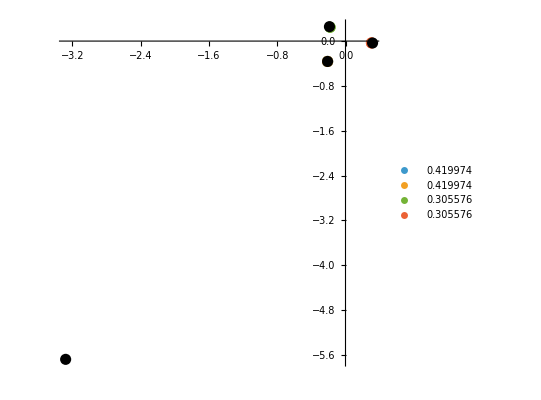

```mathematica
Show[
PlotURoots[(-3^3/2^8)^(1/3)],
Graphics[{PointSize[.02],Point[ReIm[j0points]]}],
PlotRange->All
]
```

```mathematica
MirrorCurveJ[m,u]
```

((1-8 m u^2-24 u^3+16 m^2 u^4)^3)/(u^8 (m+u-8 m^2 u^2-36 m u^3-27 u^4+16 m^3 u^4))

```mathematica
ExpandAll[u^8 (m+u-8 m^2 u^2-36 m u^3-27 u^4+16 m^3 u^4)/.{u->-(z1 z2)^(1/3),m->(z1/z2^2)^(1/3)}]//PowerExpand//Simplify
```

z1^3 z2^2 (1+16 z1^2-z2+z1 (-8+36 z2-27 z2^2))

```mathematica
z1^3 z2^2 (1+16 z1^2-z2+z1 (-8+36 z2-27 z2^2))/.{z1->Exp[2Pi I (TF1+I TF2)], z2->Exp[2Pi I (TB1+I TB2)]}
```

ⅇ^(4 ⅈ π (TB1+ⅈ TB2)+6 ⅈ π (TF1+ⅈ TF2)) (1-ⅇ^(2 ⅈ π (TB1+ⅈ TB2))+16 ⅇ^(4 ⅈ π (TF1+ⅈ TF2))+ⅇ^(2 ⅈ π (TF1+ⅈ TF2)) (-8+36 ⅇ^(2 ⅈ π (TB1+ⅈ TB2))-27 ⅇ^(4 ⅈ π (TB1+ⅈ TB2))))

```mathematica
Inverse[MonodromyFromSphericalTwist[0,0].MonodromyFromSphericalTwist[0,1]]
%.{1,m,t,td}
```

{{1,0,0,0},{0,1,0,0},{-1/2,1,0,1},{-1/2,1,-1,1}}

{1,m,-1/2+m+td,-1/2+m-t+td}

```mathematica
Solve[{-1/2+m+td,-1/2+m-t+td}=={t,td},{t,td}]//Expand
```

{{t→-1/2+m,td→0}}

## Converting XY scattering to ST plane

```mathematica
initRays = InitialRaysFromColl[{Ch[0,0],Ch[1,0],Ch[1,1],Ch[2,1]}/.repCh, -2,2,-1/10];
```

```mathematica
ListRays=ConstructLVDiagramOpt[15,6,-1/10,initRays];
```

Adding 356 rays,

Adding 1310 rays,

Adding 708 rays,

Adding 117 rays,

2523 in total.

```mathematica
SimpleRays=Select[ListRays, Abs[#[[1,1]]]==1&&BogomolovDiscriminant[#[[1]]]==0&];
```

```mathematica
Length/@{ListRays, SimpleRays}
```

{2523,64}

```mathematica
XYTost[{-39/20,-77/5},0,-1/10]
```

{-39/20,0}

```mathematica
With[{ray=ListRays[[100]],psi=0,m=-1/10},
t+If[FreeQ[#, Complex], #, 0]&@XYTost[ray[[2]], psi, m][[2]]
]
```

(3 √(187/2))/100+t

```mathematica
styleMap=<|
0->Directive[Black,Thickness[.003]],
1->Directive[Opacity[.6, Lighter[DarkRed]],Thickness[.0025]],
2->Directive[Opacity[.3,Lighter[DarkGreen]],Thickness[.002]],
3->Directive[Opacity[.1,Lighter[Green]],Thickness[.0015]]
|>;
defaultStyle=Directive[Black,Thickness[.002]];
```

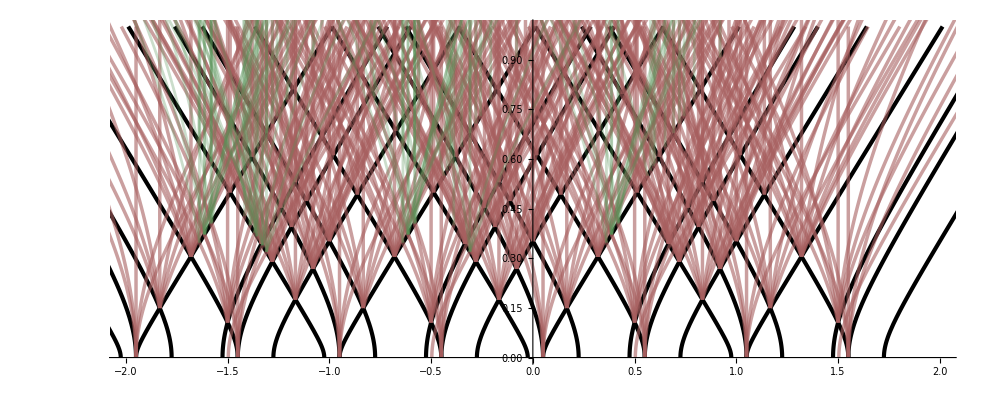

```mathematica
temp=With[{psi=0, m=-1/10},
rays=Table[
t0=If[FreeQ[#, Complex], #, 0]&@XYTost[ray[[2]], psi, m][[2]];
Tooltip[Style[{Rays[ray[[1]], t+t0, psi, m], t+t0}, Lookup[styleMap,ray[[7]],defaultStyle]], ChernToCh[ray[[1]]]],
{ray,ListRays[[1;;500]]}];

ParametricPlot[rays, {t, 0, 1},
PlotRange->{{-2, 2}, {0,1}},
AspectRatio->Automatic
]]
```

```mathematica
BogomolovDiscriminant[{-2,-2,-1,-1/2}]
```

1/8

```mathematica
ToHC[SpectralFlow[{-2,-2,-1,-1/2},-{3,2}]]
```

{-2,4,-1,-7/2}

```mathematica
{-2,-2,-1,-1/2}
Select[ListRays, #[[1]]==%&]
```

{-2,-2,-1,-1/2}

{{{-2,-2,-1,-1/2},{2/5,-7/10},13,21,1,1,1}}

```mathematica
XYTost[{2/5,-7/10},0,-1/10]
```

{2/5,1/20 ⅈ √(21/2)}

```mathematica
LVTreesFromListRays[ListRays,{-2,-2,-1,-1/2},-1/10]
ChernToCh[%]
```

{{{-1,-1,0,0},{-1,-1,-1,-1/2}}}

{{Ch[1,0][1],Ch[1,1][1]}}

```mathematica
DSZ@@{Ch[1,0][1],Ch[1,1][1]}/.repCh
```

1

```mathematica
{ListRays[[13]],ListRays[[21]]}
```

{{{-1,-1,0,0},{21/80,-17/40},0,0,0,0,0},{{-1,-1,-1,-1/2},{31/80,-53/80},0,0,0,0,0}}

```mathematica
CostPhi[{-1,-1,-1,-1/2},31/80,-1/10]
```

0

```mathematica
XYRay[{-1,-1,0,0},{x,y},-1/10]
```

1/10-2 x-y

```mathematica
XYRay[{-1,-1,0,0},{x,y},-1/10]/.{x->21/80+t, y->-17/40-2t}//Simplify
```

0

```mathematica
XYRay[{-1,-1,-1,-1/2},{x,y},-1/10]/.{x->31/80+tp, y->-53/80-3tp}//Simplify
```

0

```mathematica
Solve[{21/80+t==31/80+tp, -17/40-2t==-53/80-3tp},{t,tp}]
{21/80+t,-17/40-2t}/.First[%]
```

{{t→11/80,tp→1/80}}

{2/5,-7/10}

```mathematica
CostPhi[Ch[1,0][1]/.repCh,2/5,-1/10]
```

11/10

```mathematica
CostPhi[Ch[1,1][1]/.repCh,2/5,-1/10]
```

1/10

```mathematica
XYParabolaY[x,-1/10,0,0]
```

1/4 (1/50+(2 x)/5-16 x^2)

```mathematica
{x,y}/.Solve[{1/2-3 x-y==0,y==1/4 (1/50+(2 x)/5-16 x^2)},{x,y}]
(%[[1]]+%[[2]])/2
```

{{9/40,-7/40},{11/20,-23/20}}

{31/80,-53/80}

```mathematica
CostPhi[{-1,-1,-1,-1/2},x,-1/10]
```

-31/10+8 x

```mathematica
DSZ[Ch[1,0][1],Ch[1,1][1]]/.repCh
```

1

```mathematica
IntersectRaysNoTest[{-1,-1,0,0}, {-1,-1,-1,-1/2}, {21/80,-17/40}, {31/80,-53/80}, -1/10]
```

{2/5,-7/10}

```mathematica
XYTost[{2/5,-7/10},0,-1/10]
```

{2/5,1/20 ⅈ √(21/2)}

## Scratch

```mathematica
Solve[Uu==(9u+8m)^2,u]
```

{{u→1/9 (-8 m-√Uu)},{u→1/9 (-8 m+√Uu)}}

```mathematica
MirrorCurveJ[m,u]/.{u->1/9 (-8 m+√Uu)}
```

((6561+8 (m (135+2 m (-8 m+√Uu)^2)-27 √Uu) (-8 m+√Uu)^2)^3)/((-8 m+√Uu)^8 (m (27+256 m^3)^2+(729+3456 m^3-32768 m^6) √Uu+24 m^2 (-135+256 m^3) Uu+4 m (135-128 m^3) Uu^(3/2)+(-27+16 m^3) Uu^2))

```mathematica
ExpandAll[Numerator[Together[MirrorCurveJ[m,u]-j]]/.{u->1/9 (-8 m+√Uu)}];
temp = Simplify@Series[%,{Uu,0,100}];
Simplify@Series[PowerExpand[Normal[%]/.{Uu->U^2}], {U,0,100}]
FullSimplify[Normal[%]]
```

((27+256 m^3)^2 (387420489+4897760256 m^3+12899450880 m^6-16777216 (-756+j) m^9+4294967296 m^12))/282429536481-(128 (m^2 (27+256 m^3) (387420489+4897760256 m^3+12899450880 m^6-16777216 (-756+j) m^9+4294967296 m^12)) U)/94143178827+(8 m (24407490807+1340761870080 m^3+286654464 (48573+j) m^6+452984832 (79218+j) m^9-4294967296 (-8235+11 j) m^12+12094627905536 m^15) U^2)/94143178827-(8 (3486784401+775988890560 m^3+71663616 (186678+7 j) m^6+226492416 (173259+35 j) m^9-5368709120 (-7776+11 j) m^12+15118284881920 m^15) U^3)/282429536481+(16 m^2 (4663394775+1119744 (138078+7 j) m^3+24772608 (21033+10 j) m^6-83886080 (-7236+11 j) m^9+236223201280 m^12) U^4)/31381059609-(128 (m (33480783+23328 (115965+7 j) m^3+221184 (48195+43 j) m^6-2097152 (-6615+11 j) m^9+5905580032 m^12)) U^5)/31381059609-(64 (-4782969-2916 (523449+35 j) m^3-193536 (37503+59 j) m^6+1835008 (-5913+11 j) m^9-5167382528 m^12) U^6)/94143178827-(64 (m^2 (j (2187+525312 m^3-720896 m^6)+4 (7735419+46982592 m^3+84049920 m^6+46137344 m^9))) U^7)/31381059609+(m (j (5103+3248640 m^3-3604480 m^6)+256 (275562+2390391 m^3+5460480 m^6+3604480 m^9)) U^8)/31381059609+((j (-729-1952640 m^3+1802240 m^6)-512 (19683+323676 m^3+1062720 m^6+901120 m^9)) U^9)/282429536481+(8 m^2 (j (3591-2816 m^3)+128 (729+4590 m^3+5632 m^6)) U^10)/94143178827-(4 (512 m^4 (27+64 m^3)+j (189 m-128 m^4)) U^11)/94143178827+((4096 m^6+j (27-16 m^3)) U^12)/282429536481+O[U]^101

1+1/282429536481(-8 m+U)^2 (4398046511104 m^16-5497558138880 m^15 U+3092376453120 m^14 U^2-2415919104 m^11 U^2 (-3672+5 j+14 U^3)-17179869184 m^13 (-810+j+60 U^3)+2147483648 m^12 U (-7776+10 j+105 U^3)+2359296 m^8 U^2 (36 (102897+8 j)+56 (-540+j) U^3+5 U^6)+100663296 m^10 (158922-36 j+8 (-3402+5 j) U^3+35 U^6)-9216 m^5 U^2 (-972 (356184+11 j)+36 (142749+224 j) U^3+(-1242+5 j) U^6)+648 m^2 U^2 (356065470-54 (274320+19 j) U^3+(3456+85 j) U^6)+4096 m^6 U (-11664 (159624+j)+2916 (35625+28 j) U^3+48 (-1782+5 j) U^6+U^9)-65536 m^7 (2916 (-41580+j)+648 (57483+20 j) U^3+42 (-2268+5 j) U^6+5 U^9)+27 U (-1033121304+34012224 U^3-27 (13824+j) U^6+j U^9)-16 m^3 U (61757695728-14580 (467964+29 j) U^3+2592 (3132+23 j) U^6+j U^9)-27 m (-5165606520+884317824 U^3-1269 (13824+j) U^6+68 j U^9)+256 m^4 (6256123452-29160 (101196+5 j) U^3+729 (17607+56 j) U^6+(-648+5 j) U^9)-25165824 m^9 U (710046-21546 U^3+10 U^6+j (-72+35 U^3)))

```mathematica
MirrorCurveJ[m,u]/.{u->up m, m->m3^(1/3)}//ExpandAll//PowerExpand//Simplify
```

((1-8 m^2 m3^(1/3) up^2-24 m^3 up^3+16 m^4 m3^(2/3) up^4)^3)/(m^8 up^8 (m up-8 m^2 m3^(2/3) up^2-27 m^4 up^4+16 m^4 m3 up^4+m3^(1/3) (1-36 m^3 up^3)))

```mathematica
m+u-8 m^2 u^2-36 m u^3-27 u^4+16 m^3 u^4/.{m->}
```

```mathematica
MirrorCurveJ[m,u]-j
```

-j+((1-8 m u^2-24 u^3+16 m^2 u^4)^3)/(u^8 (m+u-8 m^2 u^2-36 m u^3-27 u^4+16 m^3 u^4))

```mathematica
Simplify[D[MirrorCurveJ[m,u]-j,u]]
```

((1-8 m u^2-24 u^3+16 m^2 u^4)^2 (512 m^4 u^6+192 m^3 u^4 (-2+3 u^3)-48 m^2 u^2 (-2+33 u^3)-4 m (2-99 u^3+756 u^6)-9 (u-36 u^4+216 u^7)))/(u^9 (m+u-8 m^2 u^2-36 m u^3-27 u^4+16 m^3 u^4)^2)

```mathematica
temp =Simplify@Solve[{-j+((1-8 m u^2-24 u^3+16 m^2 u^4)^3)/(u^8 (m+u-8 m^2 u^2-36 m u^3-27 u^4+16 m^3 u^4))==0,((1-8 m u^2-24 u^3+16 m^2 u^4)^2 (512 m^4 u^6+192 m^3 u^4 (-2+3 u^3)-48 m^2 u^2 (-2+33 u^3)-4 m (2-99 u^3+756 u^6)-9 (u-36 u^4+216 u^7)))/(u^9 (m+u-8 m^2 u^2-36 m u^3-27 u^4+16 m^3 u^4)^2)==0},{u,j}];
```

```mathematica
j/.temp
```

{((27+256 m^3) (243+256 m^3)^3)/(16777216 m^9),0,0,0,0,1728,1728,1728,1728,1728,1728}

```mathematica
Simplify[Discriminant[Numerator[Together[MirrorCurveJ[m,u]-j]], u]]
Simplify@Solve[%==0,j]
```

(-1728+j)^6 j^8 (27+256 m^3)^3 (-387420489-4897760256 m^3-12899450880 m^6+16777216 (-756+j) m^9-4294967296 m^12)

{{j→0},{j→0},{j→0},{j→0},{j→0},{j→0},{j→0},{j→0},{j→1728},{j→1728},{j→1728},{j→1728},{j→1728},{j→1728},{j→((27+256 m^3) (243+256 m^3)^3)/(16777216 m^9)}}

```mathematica
Log[3,19683]
```

9

```mathematica
-(-1/3^9)^(1/8)//N
```

-0.268444-0.111193 ⅈ

```mathematica
M1p = Inverse[MonodromyFromSphericalTwist[0,0].MonodromyFromSphericalTwist[0,1]]
```

{{1,0,0,0},{0,1,0,0},{-1/2,1,0,1},{-1/2,1,-1,1}}

```mathematica
M1p//MatrixForm
```

(1 | 0 | 0 | 0
0 | 1 | 0 | 0
-1/2 | 1 | 0 | 1
-1/2 | 1 | -1 | 1)

```mathematica
Mz2=MatrixPower[M1p,3]
```

{{1,0,0,0},{0,1,0,0},{-1,2,-1,0},{0,0,0,-1}}

```mathematica
M1=Inverse[MonodromyFromSphericalTwist[Ch[0,0]/.repCh]];
M2=Inverse[MonodromyFromSphericalTwist[Ch[1,0]/.repCh]];
M3=Inverse[MonodromyFromSphericalTwist[Ch[1,1]/.repCh]];
M4=Inverse[MonodromyFromSphericalTwist[Ch[-1,-1]/.repCh]];
```

```mathematica
M2p=Inverse[MonodromyFromSphericalTwist[-1,0]]
MatrixForm[M2p]
```

{{1,0,0,0},{0,1,0,0},{0,1,3,1},{0,-2,-4,-1}}

(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 1 | 3 | 1
0 | -2 | -4 | -1)

```mathematica
MatrixForm/@{M1,M2,M3,M4}
```

{(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 1
0 | 0 | 0 | 1),(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | -1 | -1 | 1
0 | -2 | -4 | 3),(1 | 0 | 0 | 0
0 | 1 | 0 | 0
1/2 | 0 | -2 | 1
3/2 | 0 | -9 | 4),(1 | 0 | 0 | 0
0 | 1 | 0 | 0
1/2 | 0 | 4 | 1
-3/2 | 0 | -9 | -2)}

```mathematica
Mz2.M2.Mz2//MatrixForm
```

(1 | 0 | 0 | 0
0 | 1 | 0 | 0
-2 | 5 | -1 | 1
-4 | 10 | -4 | 3)

```mathematica
MonodromyOnCharge[Mz2,Ch[p,q]/.repCh]//BogomolovDiscriminant//Simplify
```

2 p-12 p^2+q-4 p q-q^2

```mathematica
FindInstance[2 p-12 p^2+q-4 p q-q^2==0,{p,q},Integers,4]
```

{{p→0,q→0},{p→0,q→1}}

```mathematica
MonodromyOnCharge[Mz2,Ch[0,0]/.repCh]
```

{-1,0,0,0}

```mathematica
MonodromyOnCharge[Mz2,Ch[0,1]/.repCh]
```

{-1,0,-1,1/2}

```mathematica
MatrixForm[Mz2]
```

(1 | 0 | 0 | 0
0 | 1 | 0 | 0
-1 | 2 | -1 | 0
0 | 0 | 0 | -1)

```mathematica
Inverse[MonodromyFromSphericalTwist[-1,0]]//MatrixForm
```

(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 1 | 3 | 1
0 | -2 | -4 | -1)

```mathematica
Inverse[MonodromyFromSphericalTwist[0,0]]//MatrixForm
```

(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 1
0 | 0 | 0 | 1)

```mathematica
Inverse[MonodromyFromSphericalTwist[0,0]]//MatrixForm
```

```mathematica
Simplify@Thread[MonodromyFromSphericalTwist[mF,mB].{1,m,t,td}=={1,m,t,td}]/.{td->mB^2/2+m (-mB+mF)+2 mF t+mB (-mF+t)}//Simplify
```

{True,True,True,True}

```mathematica
Solve[{mB^2+2 mB t+2 mF (m+2 t)==2 (m mB+mB mF+td),(mB+2 mF) (-2 m mB+mB^2+2 m mF-2 mB mF+2 mB t+4 mF t-2 td)==0}, {t,td}]//Simplify
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{td→mB^2/2+m (-mB+mF)+2 mF t+mB (-mF+t)}}

```mathematica
Collect[mB^2/2+m (-mB+mF)+2 mF t+mB (-mF+t),t]
```

mB^2/2-mB mF+m (-mB+mF)+(mB+2 mF) t

```mathematica
{r,dF,dB,ch2}.Sigma.{1,m,t,td}
```

-ch2+(-dB+dF) m+(dB+2 dF) t-r td

```mathematica
{1,mF,mB,-mB^2/2+mB mF}.Sigma.{1,m,t,mB^2/2+m (-mB+mF)+2 mF t+mB (-mF+t)}//Expand
```

0

```mathematica
Ch[mF,mB]/.repCh
```

{1,mF,mB,-mB^2/2+mB mF}

```mathematica
Solve[MonodromyOnTau[MonodromyFromSphericalTwist[mF,mB],t]==t, t]
```

{{t→1/8 (mB+2 mF)},{t→1/8 (mB+2 mF)}}

```mathematica
Array[M,{4,4}].{1,m,t[z],td[z]}
D[%[[4]],z]/D[%[[3]],z]/.{td'[z]-> tau t'[z]}//Simplify
```

{M[1,1]+m M[1,2]+M[1,3] t[z]+M[1,4] td[z],M[2,1]+m M[2,2]+M[2,3] t[z]+M[2,4] td[z],M[3,1]+m M[3,2]+M[3,3] t[z]+M[3,4] td[z],M[4,1]+m M[4,2]+M[4,3] t[z]+M[4,4] td[z]}

(M[4,3]+tau M[4,4])/(M[3,3]+tau M[3,4])

```mathematica
λb=-3/(4*2^(2/3))
```

-3/(4 2^(2/3))

```mathematica
lPath[t_]:=
```

```mathematica
Manipulate[Show[
PlotURoots[N[λ,50]],
Graphics[{Black, PointSize[.02],Point[ReIm[-8λ/9]]}],
 PlotRange->{{-4,4},{-4,4}}
], {{λ,1},-1, 2,.001}]
```

```mathematica
MirrorCurveDelta[λ,u]/.{u->u μ^(1/3), λ->μ^(1/3)}//Simplify
```

μ^(1/3) (1+u-8 u^2 μ-36 u^3 μ+u^4 μ (-27+16 μ))

```mathematica
μ0=1;μ1=-27/256;
```

```mathematica
uRoots[μ_]:=u/.NSolve[1+u-8 u^2 μ-36 u^3 μ+u^4 μ (-27+16 μ)==0,u];
```

```mathematica
μ1//N
```

-0.105469

```mathematica
μPath1[t_]:=I t + (1-t)μ0;
μPath2[t_]:=μ1 t + (1-t)I;
μPath[t_]:=Piecewise[{{μPath1[t], 0<=t<1}, {μPath2[t-1], 1<=t<2}}];
```

```mathematica
Manipulate[
Show[{
Graphics[{PointSize[.015],Point[ReIm/@uRoots[μPath[t]]], Red,Point[ReIm[-8/9]]}]
}, 
PlotRange->{{-4,4},{-4,4}}, 
AspectRatio->Automatic,
Axes->True
], {{t, 0}, 0, 2, 0.001}]
```

```mathematica
λPath1[t_]:=I t + (1-t)1;
λPath2[t_]:=-3/(4*2^(2/3)) t + (1-t)I;
λPath[t_]:=Piecewise[{{λPath1[t], 0<=t<1}, {λPath2[t-1], 1<=t<=2}}];
```

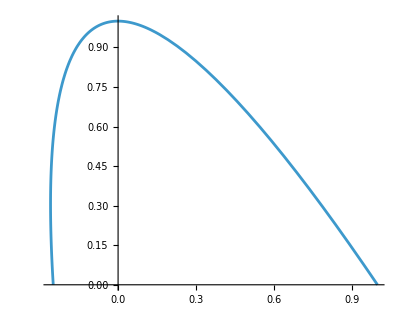

```mathematica
ParametricPlot[ReIm[λPath[t]],{t,0,1}]
```

```mathematica
Manipulate[Show[
PlotURoots[λPath[t]],
Graphics[{Black, PointSize[.02],Point[ReIm[-8λPath[t]/9]]}],
 PlotRange->{{-4,4},{-4,4}}
], {{t,0},0, 1,.001}]
```

```mathematica
ClearAll[MirrorCurveDelta,λb,λPath,rhs,u0,sol,us];
MirrorCurveDelta[m_,u_]:=m+u-8 m^2 u^2-36 m u^3-27 u^4+16 m^3 u^4;

λb=-3/(4*2^(2/3));
λPath=Interpolation[{{0,1},{1/2,I}, {1,-1/4}}];

rhs[t_,uu_]:=Evaluate@Simplify[-(D[MirrorCurveDelta[λ,u],λ]/. {λ->λPath[t],u->uu})/(D[MirrorCurveDelta[λ,u],u]/. {λ->λPath[t],u->uu})*(λPath'[t])];

u0=u/. Solve[MirrorCurveDelta[λPath[0],u]==0,u];
labels={2,1,4,3};

sol=First@NDSolve[Join[Table[Subscript[u,k]'[t]==rhs[t,Subscript[u,k][t]],{k,4}],Table[Subscript[u,k][0]==u0[[k]],{k,4}]],Table[Subscript[u,k],{k,4}],{t,0,1}];

us[t_]:=Table[Subscript[u,k][t]/. sol,{k,4}];

Manipulate[Show[{Graphics[{Black,PointSize[.012],Point[ReIm/@us[t]],Red,Point[ReIm[-8 λPath[t]/9]], Line[{ReIm[0],ReIm[us[t][[1]]]}], Line[{ReIm[0],ReIm[us[t][[3]]]}]}],
Graphics[
MapThread[
Text[Subscript["u",#1],ReIm[#2],#3]&,
{
labels,
us[t],
{{2,0},{-2,0},{-2,0},{-2,0}} 
}
]~Join~{Text[Subscript["u","B"],ReIm[-8 λPath[t]/9],{-2,0}]}
]},PlotRange->{{-4,4},{-4,4}},AspectRatio->Automatic,Axes->True],{{t,0},0,1,.001}]
```

Interpolation::inhr: Requested order is too high; order has been reduced to {2}.

Part::partw: Part 3 of us[0.84] does not exist.

MapThread::mptd: Object labels at position {2, 1} in MapThread[Text[u_#1,ReIm[#2],#3]&,{labels,us[0.84],{{2,0},{-2,0},{-2,0},{-2,0}}}] has only 0 of required 1 dimensions.

Join::heads: Heads MapThread and List at positions 1 and 2 are expected to be the same.

Part::partw: Part 3 of us[0.84] does not exist.

MapThread::mptd: Object labels at position {2, 1} in MapThread[Text[u_#1,ReIm[#2],#3]&,{labels,us[0.84],{{2,0},{-2,0},{-2,0},{-2,0}}}] has only 0 of required 1 dimensions.

Join::heads: Heads MapThread and List at positions 1 and 2 are expected to be the same.

```mathematica
M2.M4
```

{{1,0,0,0},{0,1,0,0},{-2,-1,-13,-3},{-13/2,-2,-43,-10}}

```mathematica
M4.M2
```

{{1,0,0,0},{0,1,0,0},{1/2,-6,-8,7},{-3/2,13,17,-15}}

```mathematica
M2.M4.Inverse[M2]
```

{{1,0,0,0},{0,1,0,0},{-2,-20,-51,16},{-13/2,-65,-169,53}}

```mathematica
us[.23][[2]]
```

0.281495-0.0443288 ⅈ

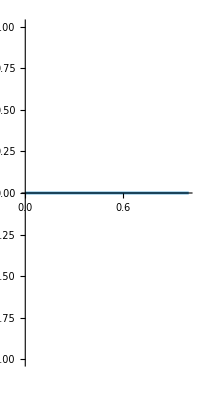

```mathematica
ParametricPlot[ReIm[λPath[t]],{t,0,1}]
```

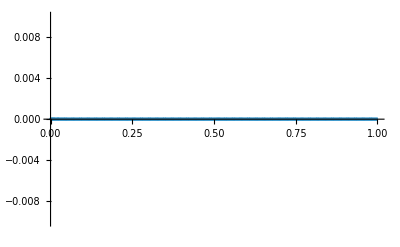

```mathematica
ReImPlot[MirrorCurveDelta[λPath[t],#]&/@us[t],{t,0,1},
PlotRange->{Automatic,{-0.01,0.01}}
]
```

```mathematica
M4
```

{{1,0,0,0},{0,1,0,0},{1/2,0,4,1},{-3/2,0,-9,-2}}

```mathematica
Solve[(-5tau+4)/(tau-1)==tau,tau]//Simplify
```

{{tau→-2 (1+√2)},{tau→2 (-1+√2)}}

## Scratch Ju = J

```mathematica
MirrorCurveJ[λ,u]/.{λ->l3^(1/3),u->u l3^(1/3)}//PowerExpand//Simplify
```

((1+16 l3^2 u^4-8 l3 u^2 (1+3 u))^3)/(l3^3 u^8 (1+u-8 l3 u^2-36 l3 u^3+l3 (-27+16 l3) u^4))

```mathematica
8/1766*5000//N
```

22.6501

```mathematica
MirrorCurveJ[λ,u]/.{u->u l3^(1/3),λ->(l3)^(1/3)}
PowerExpand[%]//Simplify
```

((1-8 l3 u^2-24 l3 u^3+16 l3^2 u^4)^3)/(l3^(8/3) u^8 (l3^(1/3)+l3^(1/3) u-8 l3^(4/3) u^2-36 l3^(4/3) u^3-27 l3^(4/3) u^4+16 l3^(7/3) u^4))

((1-8 l3 u^2-24 l3 u^3+16 l3^2 u^4)^3)/(l3^(8/3) u^8 (l3^(1/3)+l3^(1/3) u-8 l3^(4/3) u^2-36 l3^(4/3) u^3-27 l3^(4/3) u^4+16 l3^(7/3) u^4))

```mathematica
InitialPositionXY[Ch[p,q]/.repCh,mu]//Simplify//Expand
```

{-mu/8+p/4+q/8,-(3 mu p)/4-p^2/2+(9 mu q)/8+(p q)/2-(5 q^2)/8}

```mathematica
?CostPhi
```

```mathematica
CostPhi[{r,dF,dB,ch2},x,mu]
```

dB+2 dF-r (mu+8 x)

{{1,0,0,0},{-1,1,0,0},{-1,0,1,1/2},{1,-1,-1,1/2}}

```mathematica
CollBridgeland
#.Sigma.{1,m,t,td}&/@CollBridgeland
```

{{1,0,0,0},{-1,1,0,0},{-1,0,1,1/2},{1,-1,-1,1/2}}

{-td,m+2 t+td,-1/2-m+t+td,-1/2-3 t-td}

```mathematica
Ch[0,1].Sigma.{1,m,t,td}/.repCh/.{}
```

1/2-m+t-td

```mathematica
M1p
```

{{1,0,0,0},{0,1,0,0},{-1/2,1,0,1},{-1/2,1,-1,1}}

```mathematica
Table[{k,MonodromyOnCharge[MatrixPower[M1p,k],Ch[-1,1]/.repCh]}, {k,0,5}]
(*BogomolovDiscriminant[#[[2]]]&/@%*)#[[2]].Sigma.{1,m,t,td}&/@%/.{t->m-1/2,td->0}//Simplify
```

{{0,{1,-1,1,-3/2}},{1,{-1,-1,0,-1}},{2,{-2,-1,1,-3/2}},{3,{-1,-1,3,-5/2}},{4,{1,-1,4,-3}},{5,{2,-1,3,-5/2}}}

{2-3 m,2-3 m,2-3 m,2-3 m,2-3 m,2-3 m}

```mathematica
ChernToCh[{-1,-1,3,-5/2}]
```

{-1,-1,3,-5/2}

```mathematica
Table[{k,MonodromyOnCharge[MatrixPower[M1p,k],Ch[-1,0]/.repCh]}, {k,0,5}]
(*BogomolovDiscriminant[#[[2]]]&/@%*)
#[[2]].Sigma.{1,m,t,td}&/@%/.{t->m-1/2,td->0}//Simplify
```

{{0,{1,-1,0,0}},{1,{-2,-1,-1,1/2}},{2,{-3,-1,1,-1/2}},{3,{-1,-1,4,-2}},{4,{2,-1,5,-5/2}},{5,{3,-1,3,-3/2}}}

{1-3 m,1-3 m,1-3 m,1-3 m,1-3 m,1-3 m}

```mathematica
{2-3 m,1-3 m}/.{m->Echo[N@Log[(-27/256)^(1/3)Exp[2Pi I/3*2]]/(2Pi I)]}
```

-0.166667+0.119331 ⅈ

{2.5-0.357994 ⅈ,1.5-0.357994 ⅈ}

```mathematica
A1=Table[{k,MonodromyOnCharge[MatrixPower[M1p,k],Ch[0,0]/.repCh]}, {k,0,5}]
```

{{0,{1,0,0,0}},{1,{0,0,-1,1/2}},{2,{-1,0,-1,1/2}},{3,{-1,0,0,0}},{4,{0,0,1,-1/2}},{5,{1,0,1,-1/2}}}

```mathematica
A2=Table[{k,MonodromyOnCharge[MatrixPower[M1p,k],Ch[0,1]/.repCh]}, {k,0,5}]
```

{{0,{1,0,1,-1/2}},{1,{1,0,0,0}},{2,{0,0,-1,1/2}},{3,{-1,0,-1,1/2}},{4,{-1,0,0,0}},{5,{0,0,1,-1/2}}}

```mathematica
Ch[0,1]/.repCh
```

{1,0,1,-1/2}

```mathematica
Eigenvalues[M1p]
```

{(-1)^(1/3),1,1,-(-1)^(2/3)}

```mathematica
Eigenvectors[M1p]
```

{{0,0,-1/2 ⅈ (ⅈ+√3),1},{-2,0,1,0},{2,1,0,0},{0,0,1/2 ⅈ (-ⅈ+√3),1}}

```mathematica
D[MonodromyOnCharge[M1p,{r,dF,dB,ch2}],{{r,dF,dB,ch2}}]
Eigenvectors[%]
```

{{0,2,1,0},{0,1,0,0},{-1,0,1,0},{1/2,0,0,1}}

{{-1+ⅈ √3,0,-2,1},{0,0,0,1},{0,-1/2,1,0},{-1-ⅈ √3,0,-2,1}}

```mathematica
MonodromyOnCharge[M1p,{0,dF,dB,ch2}]//Simplify
```

{dB+2 dF,dF,dB,ch2}

```mathematica
D[MonodromyOnCharge[MatrixPower[M1p,2],{r,dF,dB,ch2}],{{r,dF,dB,ch2}}]
Eigenvalues[%]
```

{{-1,2,1,0},{0,1,0,0},{-1,-2,0,0},{1/2,1,1/2,1}}

{-(-1)^(1/3),1,1,(-1)^(2/3)}

```mathematica
D[MonodromyOnCharge[MatrixPower[M1p,3],{r,dF,dB,ch2}],{{r,dF,dB,ch2}}]
Eigenvectors[%]
```

{{-1,0,0,0},{0,1,0,0},{0,-4,-1,0},{0,2,1,1}}

{{0,0,-2,1},{1,0,0,0},{0,0,0,1},{0,-1,2,0}}

```mathematica
MonodromyOnCharge[MonodromyFromSphericalTwist[p,q],{0,x,-2x,y}]
```

{0,x,-2 x,y}

```mathematica
A1
```

{{0,{1,0,0,0}},{1,{0,0,-1,1/2}},{2,{-1,0,-1,1/2}},{3,{-1,0,0,0}},{4,{0,0,1,-1/2}},{5,{1,0,1,-1/2}}}

```mathematica
Table[DSZ[A1[[i,2]],A1[[j,2]]], {i,1,6},{j,1,6}]//MatrixForm
```

(0 | -1 | -1 | 0 | 1 | 1
1 | 0 | -1 | -1 | 0 | 1
1 | 1 | 0 | -1 | -1 | 0
0 | 1 | 1 | 0 | -1 | -1
-1 | 0 | 1 | 1 | 0 | -1
-1 | -1 | 0 | 1 | 1 | 0)

```mathematica
D[MonodromyOnCharge[MatrixPower[M1p,1],{r,dF,dB,ch2}],{{r,dF,dB,ch2}}]
Eigensystem[%]
```

{{0,2,1,0},{0,1,0,0},{-1,0,1,0},{1/2,0,0,1}}

{{1/2 (1+ⅈ √3),1,1,1/2 (1-ⅈ √3)},{{-1+ⅈ √3,0,-2,1},{0,0,0,1},{0,-1/2,1,0},{-1-ⅈ √3,0,-2,1}}}

```mathematica
D[MonodromyOnCharge[MatrixPower[M1p,3],{r,dF,dB,ch2}],{{r,dF,dB,ch2}}]
Eigensystem[%]
```

{{-1,0,0,0},{0,1,0,0},{0,-4,-1,0},{0,2,1,1}}

{{-1,-1,1,1},{{0,0,-2,1},{1,0,0,0},{0,0,0,1},{0,-1,2,0}}}

```mathematica
CollArcaraI
MonodromyOnCharge[MatrixPower[M1p,3],#]&/@%
```

{{1,0,0,0},{0,0,1,-1/2},{1,-2,-1,3/2},{-1,1,0,0}}

{{-1,0,0,0},{0,0,-1,1/2},{-1,-2,9,-7/2},{1,1,-4,2}}

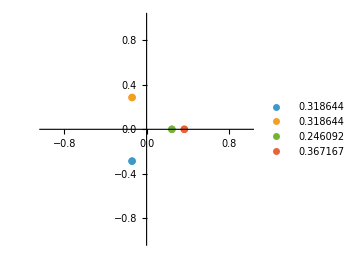
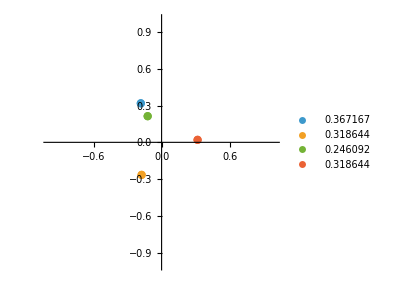
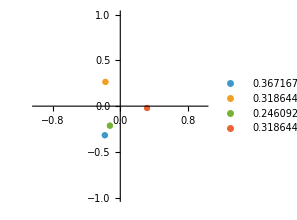

```mathematica
With[{lam=-1/4},
{
PlotURoots[lam],
PlotURoots[lam Exp[2Pi I/3]],
PlotURoots[lam Exp[2Pi I/3*2]]}]
```

```mathematica
SpectralFlow[{0,dF,dB,ch2},{1,1}]//Simplify
```

{0,dF,dB,ch2+dF}

```mathematica
CollArcaraI
#.Sigma.{1,m,t,td}&/@%
%/.{td->0,t->m-1/2}//Simplify
```

{{1,0,0,0},{0,0,1,-1/2},{1,-2,-1,3/2},{-1,1,0,0}}

{-td,1/2-m+t,-3/2-m-5 t-td,m+2 t+td}

{0,0,1-6 m,-1+3 m}

```mathematica
{Ch[-1,0],Ch[1,1]}/.repCh
#.Sigma.{1,m,t,td}&/@%
%/.{td->0,t->m-1/2}//Simplify
```

{{1,-1,0,0},{1,1,1,1/2}}

{-m-2 t-td,-1/2+3 t-td}

{1-3 m,-2+3 m}

```mathematica
CollArcaraI
```

{{1,0,0,0},{0,0,1,-1/2},{1,-2,-1,3/2},{-1,1,0,0}}

```mathematica
Ch[0,0]/.repCh
```

{1,0,0,0}

```mathematica
{{0,0,1,-1/2}, {1,-1,0,0}, {1,1,1,1/2}, {1,0,0,0}}
Table[DSZ[%[[i]],%[[j]]], {i,1,4},{j,4}]//MatrixForm
```

{{0,0,1,-1/2},{1,-1,0,0},{1,1,1,1/2},{1,0,0,0}}

(0 | -1 | -1 | -1
1 | 0 | 5 | 2
1 | -5 | 0 | -3
1 | -2 | 3 | 0)

```mathematica
ClearAll[MutateCollection];
MutateCollection[Coll_,klist_]:=Module[{Coll0,k,eps},
  (* Coll is a list of Chern vectors, klist a list of {node,\pm 1} *)
  Coll0=If[Length[klist]>1, MutateCollection[Coll,Drop[klist,-1]], Coll];
  k=Last[klist][[1]]; eps=Last[klist][[2]];
  Table[If[i==k,-Coll0[[k]],Coll0[[i]]+Max[0,eps DSZ[Coll0[[i]],Coll0[[k]]]]Coll0[[k]]],{i,Length[Coll0]}]]
```

```mathematica
MutateCollection[CollBridgeland,{{4,1}}]
```

{{1,0,0,0},{0,0,-1,1/2},{1,-2,-1,3/2},{-1,1,1,-1/2}}

```mathematica
CollArcaraII
```

{{1,0,0,0},{0,0,-1,1/2},{1,-2,-1,3/2},{-1,1,1,-1/2}}

```mathematica
MutateCollection[CollArcaraII,{{2,-1}}]
```

{{1,0,-1,1/2},{0,0,1,-1/2},{1,-2,-2,2},{-1,1,1,-1/2}}

```mathematica
MutateCollection[CollArcaraII,{{2,1}}]
```

{{1,0,0,0},{0,0,1,-1/2},{1,-2,-1,3/2},{-1,1,0,0}}

```mathematica
CollArcaraI
```

{{1,0,0,0},{0,0,1,-1/2},{1,-2,-1,3/2},{-1,1,0,0}}

{{1,0,0,0},{0,0,1,-1/2},{1,-2,-1,3/2},{-1,1,0,0}}

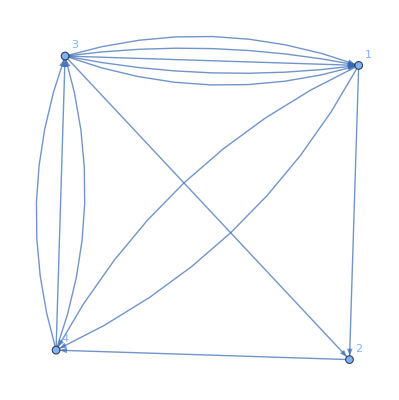

```mathematica
CollArcaraI
QuiverPlot[Table[DSZ[%[[i]],%[[j]]], {i,1,4},{j,4}]]
```

{{-1,2,0,0},{-1,1,1,-1/2},{1,-2,-1,3/2},{1,-1,0,0}}

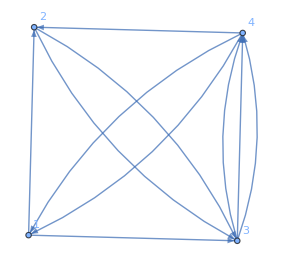

```mathematica
MutateCollection[CollArcaraI,{{4,1}}]
QuiverPlot[Table[DSZ[%[[i]],%[[j]]], {i,1,4},{j,4}]]
```

```mathematica
MutateCollection[CollArcaraI,{{4,1}}]
Table[DSZ[%[[i]],%[[j]]], {i,1,4},{j,4}]//MatrixForm
```

```mathematica
CollArcaraI
Table[DSZ[%[[i]],%[[j]]], {i,1,4},{j,4}]//MatrixForm
```

{{1,0,0,0},{0,0,1,-1/2},{1,-2,-1,3/2},{-1,1,0,0}}

(0 | 1 | -5 | 2
-1 | 0 | -1 | 1
5 | 1 | 0 | -3
-2 | -1 | 3 | 0)

```mathematica
1/2(z zp*+zp z*)/.{z->x+I y,zp->xp+I yp}//ComplexExpand
```

x xp+y yp

```mathematica
?MutateCollection
```

```mathematica
Q
```

```mathematica
Simplify[MirrorCurveDelta[l^(1/3),uu l^(1/3)]]
```

l^(1/3) (1+uu-8 l uu^2-36 l uu^3+l (-27+16 l) uu^4)

```mathematica
Delt=(1+uu-8 l uu^2-36 l uu^3+l (-27+16 l) uu^4)
```

1+uu-8 l uu^2-36 l uu^3+l (-27+16 l) uu^4

```mathematica
J=Simplify[MirrorCurveJ[l^(1/3),uu l^(1/3)]]
```

((1+16 l^2 uu^4-8 l uu^2 (1+3 uu))^3)/(l^3 uu^8 (1+uu-8 l uu^2-36 l uu^3+l (-27+16 l) uu^4))

```mathematica
PolyJ[uu_,j_,l_]=Numerator[J]-j Denominator[J]
```

-j l^3 uu^8 (1+uu-8 l uu^2-36 l uu^3+l (-27+16 l) uu^4)+(1+16 l^2 uu^4-8 l uu^2 (1+3 uu))^3

```mathematica
Together@Series[PolyJ[uu,j,l], {j,((27+256 l) (243+256 l)^3)/(16777216 l^3),4}]
```

(-((27+256 l) (243+256 l)^3 uu^8 (1+uu-8 l uu^2-36 l uu^3+l (-27+16 l) uu^4))/16777216+(1+16 l^2 uu^4-8 l uu^2 (1+3 uu))^3)-l^3 uu^8 (1+uu-8 l uu^2-36 l uu^3+l (-27+16 l) uu^4) (j-((27+256 l) (243+256 l)^3)/(16777216 l^3))+O[j-((27+256 l) (243+256 l)^3)/(16777216 l^3)]^5

```mathematica
Simplify@Together[-((27+256 l) (243+256 l)^3 uu^8 (1+uu-8 l uu^2-36 l uu^3+l (-27+16 l) uu^4))/16777216+(1+16 l^2 uu^4-8 l uu^2 (1+3 uu))^3]
```

-1/16777216(8+9 uu)^2 (-262144+589824 uu+12288 (-81+512 l) uu^2+18432 (81+256 l) uu^3-192 (10935+96768 l+327680 l^2) uu^4-144 (-19683-248832 l+1114112 l^2) uu^5+(-3720087-57106944 l-12386304 l^2+335544320 l^3) uu^6+9 (531441+9237888 l+25657344 l^2+117440512 l^3) uu^7-8 l (4782969+37791360 l-127401984 l^2+117440512 l^3) uu^8+4 l (14348907+147386304 l+47775744 l^2-662700032 l^3) uu^9+l (-129140163-1556059248 l-3332358144 l^2-1679818752 l^3+1073741824 l^4) uu^10)

```mathematica
Simplify@Discriminant[(-262144+589824 uu+12288 (-81+512 l) uu^2+18432 (81+256 l) uu^3-192 (10935+96768 l+327680 l^2) uu^4-144 (-19683-248832 l+1114112 l^2) uu^5+(-3720087-57106944 l-12386304 l^2+335544320 l^3) uu^6+9 (531441+9237888 l+25657344 l^2+117440512 l^3) uu^7-8 l (4782969+37791360 l-127401984 l^2+117440512 l^3) uu^8+4 l (14348907+147386304 l+47775744 l^2-662700032 l^3) uu^9+l (-129140163-1556059248 l-3332358144 l^2-1679818752 l^3+1073741824 l^4) uu^10),uu]
```

-81129638414606681695789005144064 l^2 (27+256 l)^6 (243+256 l)^18 (-19683-124416 l+65536 l^2)^9

```mathematica
Simplify@Discriminant[PolyJ[uu,j,l],uu]
```

(-1728+j)^6 j^8 l^44 (27+256 l)^3 (-387420489-4897760256 l-12899450880 l^2+16777216 (-756+j) l^3-4294967296 l^4)

```mathematica
Simplify[j/.First@Solve[(-387420489-4897760256 l-12899450880 l^2+16777216 (-756+j) l^3-4294967296 l^4)==0,j]]
```

((27+256 l) (243+256 l)^3)/(16777216 l^3)

```mathematica
Solve[1+16 l^2 uu^4-8 l uu^2 (1+3 uu)==0/.{uu^4->U4},U4]
```

{{U4→(-1+8 l uu^2+24 l uu^3)/(16 l^2)}}

```mathematica
Simplify[-l^3 uu^8 (1+uu-8 l uu^2-36 l uu^3+l (-27+16 l) uu^4) /.{uu^4->(-1+8 l uu^2+24 l uu^3)/(16 l^2)}]
```

1/16 l^2 uu^8 (-27+192 l^2 uu^3+8 l uu (-2+27 uu+81 uu^2))

```mathematica
Simplify[PolyJ[uu,0,-27/256]]
```

(1+(729 uu^4)/4096+27/32 uu^2 (1+3 uu))^3

```mathematica
Simplify[Denominator[J]*D[Numerator[J],uu]-Numerator[J]*D[Denominator[J],uu]]
```

l^3 uu^7 (8+9 uu) (1+16 l^2 uu^4-8 l uu^2 (1+3 uu))^2 (-1+64 l^3 uu^6+12 l uu^2 (1+3 uu)-24 l^2 uu^4 (2+6 uu+9 uu^2))

```mathematica
Simplify[{Numerator[J]-j Denominator[J], Simplify[Denominator[J]*D[Numerator[J],uu]-Numerator[J]*D[Denominator[J],uu]]}]
Simplify@Resultant[%[[1]],%[[2]], uu]
```

{-j l^3 uu^8 (1+uu-8 l uu^2-36 l uu^3+l (-27+16 l) uu^4)+(1+16 l^2 uu^4-8 l uu^2 (1+3 uu))^3,l^3 uu^7 (8+9 uu) (1+16 l^2 uu^4-8 l uu^2 (1+3 uu))^2 (-1+64 l^3 uu^6+12 l uu^2 (1+3 uu)-24 l^2 uu^4 (2+6 uu+9 uu^2))}

-(-1728+j)^6 j^8 l^92 (27+256 l)^9 (387420489+4897760256 l+12899450880 l^2-16777216 (-756+j) l^3+4294967296 l^4)

```mathematica
Simplify[Solve[387420489+4897760256 l+12899450880 l^2-16777216 (-756+j) l^3+4294967296 l^4==0,j]]
```

{{j→((27+256 l) (243+256 l)^3)/(16777216 l^3)}}

j = 0

```mathematica
PolyJ[uu, 0, l]
```

(1+16 l^2 uu^4-8 l uu^2 (1+3 uu))^3

```mathematica
Q4=1+16 l^2 uu^4-8 l uu^2 (1+3 uu);
```

```mathematica
Simplify[Discriminant[Q4,uu]]
```

-36864 l^4 (243+256 l)

j = 1728

```mathematica
Simplify@PolyJ[uu, 1728, l]
```

(1-64 l^3 uu^6-12 l uu^2 (1+3 uu)+24 l^2 uu^4 (2+6 uu+9 uu^2))^2

```mathematica
Q6=1-64 l^3 uu^6-12 l uu^2 (1+3 uu)+24 l^2 uu^4 (2+6 uu+9 uu^2);
```

```mathematica
Simplify[Discriminant[Q6,uu]]
```

-139314069504 l^10 (-19683-124416 l+65536 l^2)

```mathematica
Simplify[Resultant[Q4, Q6, uu]]
```

-2985984 l^8 (27+256 l)

j = ((27+256 l) (243+256 l)^3)/(16777216 l^3)

```mathematica
Simplify[Together[PolyJ[uu, ((27+256 l) (243+256 l)^3)/(16777216 l^3), l]]]
```

-1/16777216(8+9 uu)^2 (-262144+589824 uu+12288 (-81+512 l) uu^2+18432 (81+256 l) uu^3-192 (10935+96768 l+327680 l^2) uu^4-144 (-19683-248832 l+1114112 l^2) uu^5+(-3720087-57106944 l-12386304 l^2+335544320 l^3) uu^6+9 (531441+9237888 l+25657344 l^2+117440512 l^3) uu^7-8 l (4782969+37791360 l-127401984 l^2+117440512 l^3) uu^8+4 l (14348907+147386304 l+47775744 l^2-662700032 l^3) uu^9+l (-129140163-1556059248 l-3332358144 l^2-1679818752 l^3+1073741824 l^4) uu^10)

```mathematica
Q10=-262144+589824 uu+12288 (-81+512 l) uu^2+18432 (81+256 l) uu^3-192 (10935+96768 l+327680 l^2) uu^4-144 (-19683-248832 l+1114112 l^2) uu^5+(-3720087-57106944 l-12386304 l^2+335544320 l^3) uu^6+9 (531441+9237888 l+25657344 l^2+117440512 l^3) uu^7-8 l (4782969+37791360 l-127401984 l^2+117440512 l^3) uu^8+4 l (14348907+147386304 l+47775744 l^2-662700032 l^3) uu^9+l (-129140163-1556059248 l-3332358144 l^2-1679818752 l^3+1073741824 l^4) uu^10;
```

```mathematica
Simplify@Discriminant[Q10,uu]
```

-81129638414606681695789005144064 l^2 (27+256 l)^6 (243+256 l)^18 (-19683-124416 l+65536 l^2)^9

```mathematica
Simplify[Resultant[Q4, Q10, uu]]
```

l^4 (27+256 l)^4 (243+256 l)^10

```mathematica
Simplify[Resultant[Q6, Q10, uu]]
```

-l^6 (27+256 l) (19683+124416 l-65536 l^2)^10

```mathematica
Simplify[Resultant[Q4, Delt, uu]]
```

l^4 (27+256 l)^2

```mathematica
Simplify[Resultant[Q6, Delt, uu]]
```

-l^6 (27+256 l)^3

```mathematica
Simplify[Resultant[Q10, Delt, uu]]
```

79228162514264337593543950336 l^12 (27+256 l)^2

j = \infty

```mathematica
Series[J, {uu,Infinity,2}]
```

(4096 l^2)/(-27+16 l)-(18432 (l (-27+8 l)))/((-27+16 l)^2 uu)-(1024 (-19683+10206 l-6048 l^2+1024 l^3))/((-27+16 l)^3 uu^2)+O[1/uu]^3

```mathematica
Simplify[Series[J, {uu,0,-6}]]
```

1/(l^3 uu^8)-1/(l^3 uu^7)+(1-16 l)/(l^3 uu^6)+1/O[uu]^5

```mathematica
J
```

((1+16 l^2 uu^4-8 l uu^2 (1+3 uu))^3)/(l^3 uu^8 (1+uu-8 l uu^2-36 l uu^3+l (-27+16 l) uu^4))

#### l = -27/256

```mathematica
J1=Simplify[J/.{l->-27/256}]
```

-((8+9 uu) (512-576 uu+1080 uu^2+81 uu^3)^3)/(19683 uu^8 (64-80 uu+153 uu^2))

```mathematica
Delt1=64-80 uu+153 uu^2;
```

```mathematica
Series[J1, {uu,Infinity,2}]
```

-27/17-19008/(289 uu)-4438272/(4913 uu^2)+O[1/uu]^3

```mathematica
Simplify[Series[J1, {uu,0,-6}]]
```

-16777216/(19683 uu^8)+16777216/(19683 uu^7)-45088768/(19683 uu^6)+1/O[uu]^5

```mathematica
PolyJ1[uu_,j_]=Simplify[Numerator[J1]-j Denominator[J1]]
```

-19683 j uu^8 (64-80 uu+153 uu^2)-(8+9 uu) (512-576 uu+1080 uu^2+81 uu^3)^3

```mathematica
Simplify[{Numerator[J1]-j Denominator[J1], Simplify[Denominator[J1]*D[Numerator[J1],uu]-Numerator[J1]*D[Denominator[J1],uu]]}]
Simplify@Resultant[%[[1]],%[[2]], uu]
```

{-19683 j uu^8 (64-80 uu+153 uu^2)-(8+9 uu) (512-576 uu+1080 uu^2+81 uu^3)^3,1259712 uu^7 (512-576 uu+1080 uu^2+81 uu^3)^2 (32768-36864 uu+82944 uu^2+31104 uu^3-17496 uu^4+72171 uu^5)}

143788611574117996298558791552977581373539698541924223946344031136850776777463826056566706485967343645005597039624109884730816609436469593262642703995932552737846993499194574792376562066811857467978286319378497405837714285740191852988392507588166842327930748058325356181079669650925551616 (-1728+j)^5 j^6

```mathematica
Series[PolyJ1[uu,j],{uu,0,100}]
```

-1073741824+2415919104 uu-6794772480 uu^2+4076863488 uu^3-3439853568 uu^4-11179524096 uu^5+7255941120 uu^6-10883911680 uu^7+(-2618941248-1259712 j) uu^8+(-195570288+1574640 j) uu^9+(-4782969-3011499 j) uu^10+O[uu]^101

j = 0

```mathematica
Simplify[PolyJ1[uu,0]]
```

-((8+9 uu) (512-576 uu+1080 uu^2+81 uu^3)^3)

```mathematica
R3=512-576 uu+1080 uu^2+81 uu^3;
```

```mathematica
Discriminant[R3,uu]
```

-2641807540224

j = 1728

```mathematica
Simplify[PolyJ1[uu,1728]]
```

-(32768-36864 uu+82944 uu^2+31104 uu^3-17496 uu^4+72171 uu^5)^2

```mathematica
R5=32768-36864 uu+82944 uu^2+31104 uu^3-17496 uu^4+72171 uu^5;
```

```mathematica
Resultant[R3,R5,uu]
```

-1004997179460150918427705344

```mathematica
Resultant[R3, Delt1,uu]
```

5435817984

```mathematica
Resultant[R5, Delt1,uu]
```

57711166318706688

```mathematica
J0points=Append[uu/.Solve[R3==0,uu],-8/9]
```

{,,,-8/9}

```mathematica
J1points=uu/.Solve[R5==0,uu]
```

{,,,,}

```mathematica
JIpoints=Append[uu/.Solve[Delt1==0,uu],0]
```

{8/153 (5-8 ⅈ √2),8/153 (5+8 ⅈ √2),0}

```mathematica
Graphics[{PointSize[.006],Red, Point[ReIm/@J0points], Green, Point[ReIm/@J1points], Black, Point[ReIm/@JIpoints],
Directive[Thickness[.001],Dashed,Black],HalfLine[{{0,0},ReIm[J1points[[3]]]}]
},
PlotRange->{{-2,1},{-1,1}},
Frame->True,
GridLines->{{0},{0}}
]
```

-Graphics-

```mathematica
MinMax[N[ReIm/@Join[J1points,J0points,JIpoints]][[All,1]]]
```

{-13.8785,0.404731}

```mathematica
MinMax[N[ReIm/@Join[J1points,J0points,JIpoints]][[All,2]]]
```

{-0.93691,0.93691}

```mathematica
KleinInvariantJ[Exp[I Pi/3]]
```

0

```mathematica
KleinInvariantJ[I]
```

1

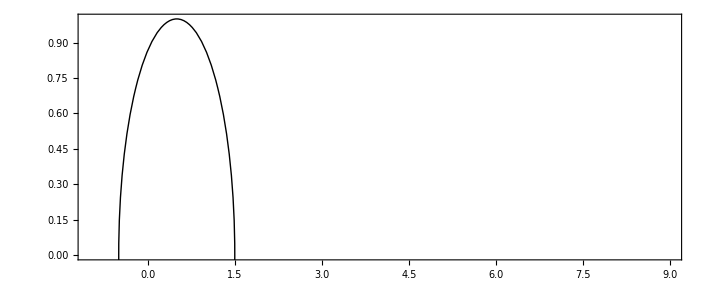

```mathematica
Graphics[{Circle[{1/2,0}, 1]},
PlotRange->{{-1,9},{0,1}},
Frame->True,
Margins
]
```

```mathematica
Simplify@ComplexExpand[ReIm[(a tau+b)/(c tau+d)/.tau->t1+I t2]]
Simplify[Together[(t1-t10)^2+(t2-t20)^2-r^2/.Thread[{t1,t2}->%]]]
```

{(a d t1+b (d+c t1)+a c (t1^2+t2^2))/(d^2+2 c d t1+c^2 (t1^2+t2^2)),(-b c t2+a d t2)/(d^2+2 c d t1+c^2 (t1^2+t2^2))}

1/(d^2+2 c d t1+c^2 (t1^2+t2^2))(b^2+2 b (a t1-d t10-c t1 t10+c t2 t20)+d^2 (-r^2+t10^2+t20^2)-2 d (a (t1 t10+t2 t20)+c t1 (r^2-t10^2-t20^2))+(t1^2+t2^2) (a^2-2 a c t10+c^2 (-r^2+t10^2+t20^2)))

```mathematica
F=Simplify[(b^2+2 b (a t1-d t10-c t1 t10+c t2 t20)+d^2 (-r^2+t10^2+t20^2)-2 d (a (t1 t10+t2 t20)+c t1 (r^2-t10^2-t20^2))+(t1^2+t2^2) (a^2-2 a c t10+c^2 (-r^2+t10^2+t20^2)))/.{t1->0,t2->0}]
```

b^2-2 b d t10+d^2 (-r^2+t10^2+t20^2)

```mathematica
b1=1/2Simplify[D[b^2+2 b (a t1-d t10-c t1 t10+c t2 t20)+d^2 (-r^2+t10^2+t20^2)-2 d (a (t1 t10+t2 t20)+c t1 (r^2-t10^2-t20^2))+(t1^2+t2^2) (a^2-2 a c t10+c^2 (-r^2+t10^2+t20^2)),{{t1,t2}}]/.{t1->0,t2->0}]
```

{1/2 (-2 b c t10+2 a (b-d t10)+2 c d (-r^2+t10^2+t20^2)),(b c-a d) t20}

```mathematica
Q1=1/2Simplify@D[b^2+2 b (a t1-d t10-c t1 t10+c t2 t20)+d^2 (-r^2+t10^2+t20^2)-2 d (a (t1 t10+t2 t20)+c t1 (r^2-t10^2-t20^2))+(t1^2+t2^2) (a^2-2 a c t10+c^2 (-r^2+t10^2+t20^2)),{{t1,t2},2}]
```

{{a^2-2 a c t10+c^2 (-r^2+t10^2+t20^2),0},{0,a^2-2 a c t10+c^2 (-r^2+t10^2+t20^2)}}

```mathematica
Simplify[-Inverse[Q1].b1]
Simplify[Simplify[%[[1]]+I %[[2]]]/.{t10->(t0+t0c)/2,t20->(t0-t0c)/2/I}]
FullSimplify[%]
```

{(b c t10+a (-b+d t10)+c d (r^2-t10^2-t20^2))/(a^2-2 a c t10+c^2 (-r^2+t10^2+t20^2)),(-b c t20+a d t20)/(a^2-2 a c t10+c^2 (-r^2+t10^2+t20^2))}

(-a b+c d r^2+a d t0+b c t0c-c d t0 t0c)/(a^2-a c (t0+t0c)+c^2 (-r^2+t0 t0c))

(c d r^2-(b-d t0) (a-c t0c))/(-c^2 r^2+(a-c t0) (a-c t0c))

```mathematica
Simplify[Simplify[2(b1ᵀ.Inverse[Q1].b1-F)/Tr[Q1]]/.{t10->(t0+t0c)/2,t20->(t0-t0c)/2/I}]
```

((b c-a d)^2 r^2)/((a^2-a c (t0+t0c)+c^2 (-r^2+t0 t0c))^2)

```mathematica
Simplify@ComplexExpand[ReIm[(a tau+b)/(c tau+d)/.tau->t1+I t2]]
Simplify[Together[(t1-n)/.Thread[{t1,t2}->%]]]
A1=Numerator[%]
```

{(a d t1+b (d+c t1)+a c (t1^2+t2^2))/(d^2+2 c d t1+c^2 (t1^2+t2^2)),(-b c t2+a d t2)/(d^2+2 c d t1+c^2 (t1^2+t2^2))}

(-d^2 n+d (a-2 c n) t1+b (d+c t1)+c (a-c n) (t1^2+t2^2))/(d^2+2 c d t1+c^2 (t1^2+t2^2))

-d^2 n+d (a-2 c n) t1+b (d+c t1)+c (a-c n) (t1^2+t2^2)

```mathematica
F=Simplify[A1/.{t1->0,t2->0}]
```

d (b-d n)

```mathematica
b1=1/2Simplify[D[A1,{{t1,t2}}]/.{t1->0,t2->0}]
```

{1/2 (b c+d (a-2 c n)),0}

```mathematica
Q1=1/2Simplify@D[A1,{{t1,t2},2}]
```

{{c (a-c n),0},{0,c (a-c n)}}

```mathematica
Simplify[-Inverse[Q1].b1]
Together[%/.{d->(1+b c)/a}]
```

{-(b c+a d-2 c d n)/(2 a c-2 c^2 n),0}

{(-a-2 a b c+2 c n+2 b c^2 n)/(2 a c (a-c n)),0}

```mathematica
Simplify[2(b1ᵀ.Inverse[Q1].b1-F)/Tr[Q1]]
Simplify[%/.{d->(1+b c)/a}]
```

(b c-a d)^2/(4 c^2 (a-c n)^2)

1/(4 c^2 (a-c n)^2)

```mathematica
Solve[a d-b c==1,d]
```

{{d→(1+b c)/a}}

```mathematica
(-a-2 a b c+2 c n+2 b c^2 n)/(2 a c (a-c n))/.{a->a1,b->bb1,c->c1,n->n1}
```

(-a1-2 a1 bb1 c1+2 c1 n1+2 bb1 c1^2 n1)/(2 a1 c1 (a1-c1 n1))

```mathematica
1/(c^2 (a-c n)^2)/.{a->a1,b->bb1,c->c1,n->n1}
```

1/(c1^2 (a1-c1 n1)^2)

```mathematica
circles=With[{L=3,Lp=3},Flatten[Table[
cen=Limit[(-a1-2 a1 bb1 c1+2 c1 n1+2 bb1 c1^2 n1)/(2 a1 c1 (a1-c1 n1)),{a1->a,bb1->b,c1->c,n1->n}];
rad=Limit[1/(c1^2 (a1-c1 n1)^2),{a1->a,bb1->b,c1->c,n1->n}];
If[cen=!=Indeterminate&&rad=!=Indeterminate, Circle[{cen,0}, 1/2Sqrt[rad]], Nothing], {a,-L,L},{b,-L,L},{c,-L,L},{n,-Lp,Lp}]]]
```

```mathematica
lines=With[{Lp=3},Table[Line[{{n,0},{n,1}}], {n,-Lp,Lp}]]
```

{Line[{{-3,0},{-3,1}}],Line[{{-2,0},{-2,1}}],Line[{{-1,0},{-1,1}}],Line[{{0,0},{0,1}}],Line[{{1,0},{1,1}}],Line[{{2,0},{2,1}}],Line[{{3,0},{3,1}}]}

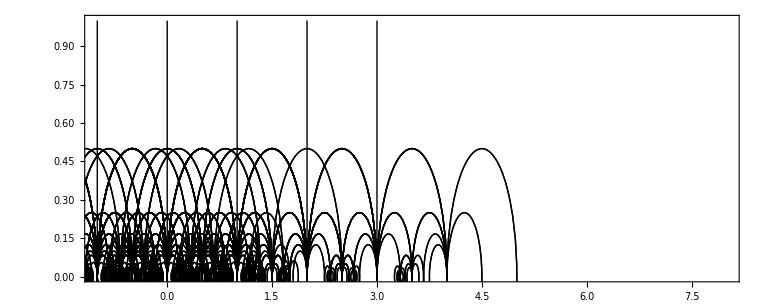

```mathematica
Graphics[{circles, lines},
PlotRange->{{-1,8},{0,1}},
PlotRangeClipping->True,
Frame->True
]
```

```mathematica
Simplify[ComplexExpand[ReIm[(a t+b)/(c t+d)],t]/.{Re[t]->n,Im[t]->t}]
Simplify[D[%, t]]
norm={%[[2]],-%[[1]]}
```

{(a d n+b (d+c n)+a c (n^2+t^2))/(d^2+2 c d n+c^2 (n^2+t^2)),(-b c t+a d t)/(d^2+2 c d n+c^2 (n^2+t^2))}

{-(2 c (b c-a d) (d+c n) t)/((d^2+2 c d n+c^2 (n^2+t^2))^2),-((b c-a d) (d^2+2 c d n+c^2 (n^2-t^2)))/((d^2+2 c d n+c^2 (n^2+t^2))^2)}

{-((b c-a d) (d^2+2 c d n+c^2 (n^2-t^2)))/((d^2+2 c d n+c^2 (n^2+t^2))^2),(2 c (b c-a d) (d+c n) t)/((d^2+2 c d n+c^2 (n^2+t^2))^2)}

```mathematica
Simplify[{(a d n+b (d+c n)+a c (n^2+t^2))/(d^2+2 c d n+c^2 (n^2+t^2)),(-b c t+a d t)/(d^2+2 c d n+c^2 (n^2+t^2))}-(-((d+c n) (d^2+2 c d n+c^2 (n^2+t^2)))/(c (3 d^2+6 c d n+c^2 (3 n^2-t^2)))) norm]
Simplify[D[%, t]]
```

{(2 b c (d+c n)^3+a (d^4+6 c d^3 n+2 c^2 d^2 (6 n^2+t^2)+2 c^3 d n (5 n^2+2 t^2)+c^4 (3 n^4+2 n^2 t^2-t^4)))/(c (3 d^2+6 c d n+c^2 (3 n^2-t^2)) (d^2+2 c d n+c^2 (n^2+t^2))),-((b c-a d) t (d^2+2 c d n+c^2 (n^2-t^2)))/((3 d^2+6 c d n+c^2 (3 n^2-t^2)) (d^2+2 c d n+c^2 (n^2+t^2)))}

{-(8 c (b c-a d) (d+c n)^3 t (d^2+2 c d n+c^2 (n^2-t^2)))/((3 d^2+6 c d n+c^2 (3 n^2-t^2))^2 (d^2+2 c d n+c^2 (n^2+t^2))^2),-(((b c-a d) (3 d^6+18 c d^5 n+4 c^3 d^3 n (15 n^2-11 t^2)+c^2 d^4 (45 n^2-11 t^2)+c^4 d^2 (45 n^4-66 n^2 t^2+t^4)+2 c^5 d n (9 n^4-22 n^2 t^2+t^4)+c^6 (3 n^6-11 n^4 t^2+n^2 t^4-t^6)))/((3 d^2+6 c d n+c^2 (3 n^2-t^2))^2 (d^2+2 c d n+c^2 (n^2+t^2))^2))}

```mathematica
Simplify[L/.First@Solve[d^3+3 c d^2 (L+n)+c^2 d (6 L n+3 n^2+t^2)+c^3 (3 L n^2+n^3-L t^2+n t^2)==0,L]]
```

-((d+c n) (d^2+2 c d n+c^2 (n^2+t^2)))/(c (3 d^2+6 c d n+c^2 (3 n^2-t^2)))

```mathematica
PolyJ1[u,j]
```

-19683 j u^8 (64-80 u+153 u^2)-(8+9 u) (512-576 u+1080 u^2+81 u^3)^3

```mathematica
a1=Together[J-(J1/.{uu->ub})];
```

```mathematica
a2=Simplify[Numerator[a1]];
```

```mathematica
F1Series[λ,u,5,0]
```

{{2 u^3+u^2 λ+12 u^5 λ+(3 u^4 λ^2)/2,u^3 (-5/2-1/(36 λ^3))+u^5 (-1/(100 λ^5)+1/(6 λ^2)-(43 λ)/2)+u^2 (1/(16 λ^2)-λ)-u/(4 λ)+u^4 (1/(64 λ^4)-3/(8 λ)-(13 λ^2)/4)},{6 u^2+2 u λ+60 u^4 λ+6 u^3 λ^2,3 u^2 (-5/2-1/(36 λ^3))+5 u^4 (-1/(100 λ^5)+1/(6 λ^2)-(43 λ)/2)+2 u (1/(16 λ^2)-λ)-1/(4 λ)+4 u^3 (1/(64 λ^4)-3/(8 λ)-(13 λ^2)/4)},{12 u+2 λ+240 u^3 λ+18 u^2 λ^2,6 u (-5/2-1/(36 λ^3))+20 u^3 (-1/(100 λ^5)+1/(6 λ^2)-(43 λ)/2)+2 (1/(16 λ^2)-λ)+12 u^2 (1/(64 λ^4)-3/(8 λ)-(13 λ^2)/4)}}

```mathematica
SystemMatrix[{{s1[u],s2[u]},{s1'[u],s2'[u]},{s1''[u],s2''[u]}},λ,u]
Simplify[%[[2,3]]/%[[2,2]]]
Simplify@Series[%, {u,0,2}]
```

{{1,-(ⅈ (Log[u]+s1[u]))/(2 π),1/6+(Log[u]^2+Log[λ]^2/8-1/4 (8 Log[u]+Log[λ]) (Log[u]+s1[u])+s2[u])/π^2},{0,-(ⅈ (1/u+s1'[u]))/(2 π),-(Log[λ]+8 s1[u]+u Log[λ] s1'[u]+8 Log[u] (1+u s1'[u])-4 u s2'[u])/(4 π^2 u)},{0,-(ⅈ (-1/u^2+s1''[u]))/(2 π),(-8+Log[λ]+8 s1[u]-16 u s1'[u]-u^2 Log[λ] s1''[u]+Log[u] (8-8 u^2 s1''[u])+4 u^2 s2''[u])/(4 π^2 u^2)}}

-(ⅈ (8 Log[u]+Log[λ]+8 s1[u]+u (8 Log[u]+Log[λ]) s1'[u]-4 u s2'[u]))/(2 (π+π u s1'[u]))

-(ⅈ (8 Log[u]+Log[λ]+8 s1[0]))/(2 π)+(2 ⅈ (-2 s1'[0]+2 s1[0] s1'[0]+s2'[0]) u)/π-(2 ⅈ (-2 s1'[0]^2+2 s1[0] s1'[0]^2+s1'[0] s2'[0]+s1''[0]-2 s1[0] s1''[0]-s2''[0]) u^2)/π+O[u]^3

```mathematica
SystemMatrix[F1Series[λ,u,20,0],λ,u];
Simplify[%[[2,3]]/%[[2,2]]];
tauu=Simplify@Series[2Pi I %, {u,0,20}];
Simplify@Series[Exp[%/8], {u,0,15}];
uq=Simplify@InverseSeries[%, q8];
```

```mathematica
Simplify[MirrorCurveJ[λ,uq]]
```

1/q8^8+744+O[q8]^7

```mathematica
SystemMatrix[F1Series[λ,u,20,0],λ,u];
TDq=Simplify[Simplify[%[[1,3]]]/.{u->uq}];
```

```mathematica
SystemMatrix[F1Series[λ,u,20,0],λ,u];
Tq=Simplify[Simplify[%[[1,2]]]/.{u->uq}];
```

```mathematica
λb=-(27/256)^(1/3);
mb=Log[λb]/(2Pi I);
```

```mathematica
TSeries[tau_,m_]=Simplify[Normal[Tq/.{λ->Exp[2Pi I m]}]/.{q8->Exp[2Pi I tau/8]}];
```

```mathematica
TDSeries[tau_,m_]=Simplify[Normal[TDq/.{λ->Exp[2Pi I m]}]/.{q8->Exp[2Pi I tau/8]}];
```

```mathematica
ZSeries[{r_,dF_,dB_,ch2_},tau_,m_]:=-ch2+(-dB+dF) m-r TDSeries[tau,m]+(dB+2 dF) TSeries[tau,m];
```

```mathematica
Ch[0,0].Sigma.{1,0,t,td}/.repCh
```

-td

```mathematica
(GV[0,1,1/2]).Sigma.{1,0,t,td}/.repCh
```

-1/2+t

```mathematica
Ch[1,1].Sigma.{1,0,t,td}/.repCh
```

-1/2+3 t-td

```mathematica
Ch[2,1].Sigma.{1,0,t,td}/.repCh
```

-3/2+5 t-td

```mathematica
PlotRay[gam_,m_,col_]:=
ContourPlot[Re[ZSeries[gam, t1+I t2, m]]==0, {t1,-2,9},{t2,.01,2},
RegionFunction->Function[{t1,t2,f},Im[ZSeries[gam, t1+I t2, m]]>0],
ContourStyle->col
];
```

```mathematica
plts=With[{m=0},{
PlotRay[Ch[0,0]/.repCh,m,Blue],
PlotRay[-Ch[1,0]/.repCh,m,Red],
PlotRay[Ch[1,1]/.repCh,m,Orange],
PlotRay[Ch[2,1]/.repCh,m,Green]
}];
```

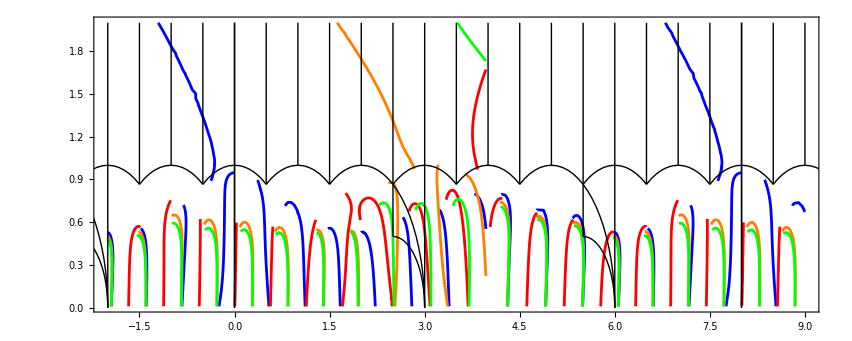

```mathematica
Show[
plts,
G10RepeatDomain[{-1,1}],
AspectRatio->Automatic
]
```

```mathematica
Ch[0,0]-Ch[0,-1]/.repCh
```

{0,0,1,1/2}

```mathematica
GV[0,1,1/2]/.repCh
```

{0,0,1,1/2}

```mathematica
Ch[1,0]+GV[0,1,1/2]/.repCh
Simplify[BogomolovDiscriminant[%]]
```

{1,1,1,1/2}

0

```mathematica
Ch[1,1]-Ch[1,0]/.repCh
```

{0,0,1,1/2}

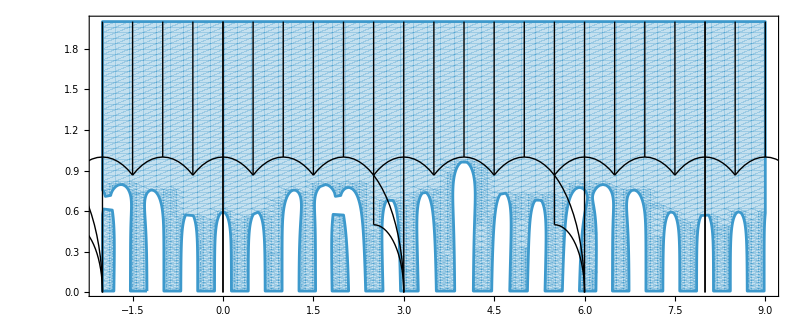

```mathematica
Show[RegionPlot[Im[TSeries[t1+I t2,0]]>0, {t1,-2,9},{t2,.01,2},
AspectRatio->Automatic,
PlotPoints->50
],
G10RepeatDomain[{-1,1}]
]
```

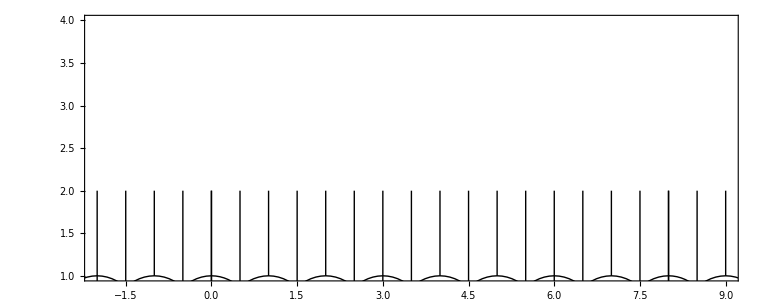

```mathematica
Show[
ContourPlot[Re[ZSeries[GV[0,1,1/2]/.repCh,t1+I t2, 0]]==0, {t1,-2,9},{t2,1,4},
RegionFunction->Function[{t1,t2,f},Im[ZSeries[GV[0,1,1/2]/.repCh,t1+I t2, 0]]>0]
],
G10RepeatDomain[{-1,1}],
AspectRatio->Automatic
]
```

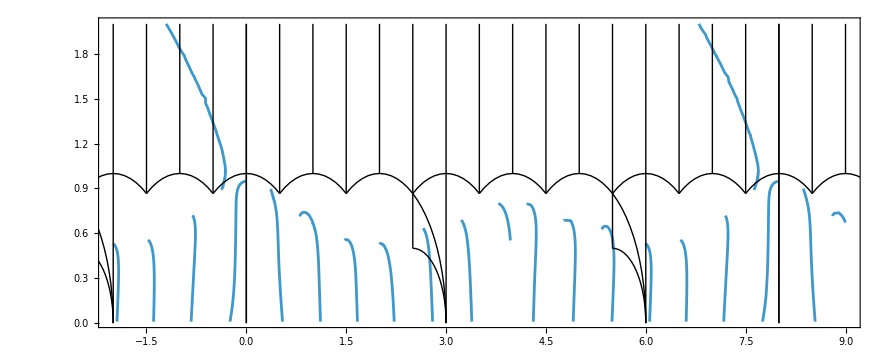

```mathematica
Show[
ContourPlot[Re[TDSeries[t1+I t2, 0]]==0, {t1,-2,9},{t2,.01,2},
RegionFunction->Function[{t1,t2,f},Im[TDSeries[t1+I t2,0]]<0]
],
G10RepeatDomain[{-1,1}],
AspectRatio->Automatic
]
```

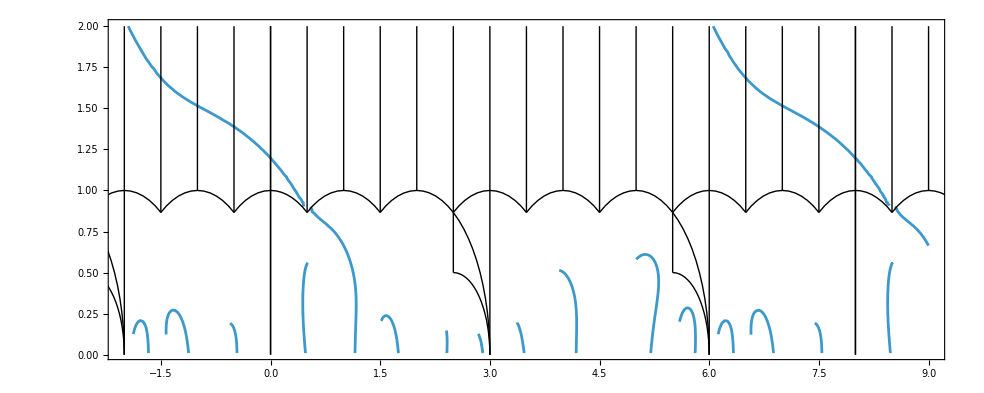

```mathematica
Show[
ContourPlot[Re[TDSeries[t1+I t2,mb]]==0, {t1,-2,9},{t2,.01,2},
PlotPoints->20,
RegionFunction->Function[{t1,t2,f},Im[TDSeries[t1+I t2,mb]]<0]
],
G10RepeatDomain[{-1,1}],
AspectRatio->Automatic
]
```

```mathematica
Series[TSeries[Log[q]/(2Pi I),0],{q,0,2}]
```

-(ⅈ Log[q])/(16 π)+(ⅈ q^(1/8))/(16 π)+(59 ⅈ q^(1/4))/(128 π)+(9425 ⅈ q^(3/8))/(6144 π)-(1475 ⅈ √q)/(1024 π)+(1761643 ⅈ q^(5/8))/(2621440 π)-(2064305 ⅈ q^(3/4))/(786432 π)+(2457094957 ⅈ q^(7/8))/(469762048 π)-(263 ⅈ q)/(16 π)+(7201907378579 ⅈ q^(9/8))/(309237645312 π)-(136322595203 ⅈ q^(5/4))/(5368709120 π)+(4462935075864543 ⅈ q^(11/8))/(48378511622144 π)-(23807579599 ⅈ q^(3/2))/(100663296 π)+(5685327484637161631 ⅈ q^(13/8))/(14636698788954112 π)-(10569104632632785 ⅈ q^(7/4))/(15393162788864 π)+O[q]^(17/8)

```mathematica
ZNewSeries[{r_,dF_,dB_,ch2_},u_]=Simplify[{r,dF,dB,ch2}.Sigma.Join[{1,0},SystemMatrix[F1Series[1,u,200,7],1,u][[1,{2,3}]]]];
```

```mathematica
N[2Pi I ZNewSeries[{0,1/3,1/3,0}, URoot[1,2]],40]
```

-1.157322100747012829570758853400855936535

```mathematica
1.1573221007466653124323507573331906
```

```mathematica
Solve[ComplexExpand[Re[ZLV[Ch[0,0]/.repCh,(t1+4I)/8,0]]]==0,t1]
```

{{t1→-4},{t1→4}}

```mathematica
MirrorCurveJ[1,1]
```

3375/53

```mathematica
ZNewSeries[Ch[0,0]/.repCh, 1/10]//N
```

0.368593

```mathematica
FindRoot[{1728KleinInvariantJ[t1+4I]-MirrorCurveJ[1,u]==0, Re[ZNewSeries[Ch[0,0]/.repCh, u]]==0},{{t1,-4}, {u,8/10}},Reals]
```

FindRoot::fdssnv: Search specification  without variables should be a list with 1 to 4 elements.

FindRoot[{1728 KleinInvariantJ[t1+4 ⅈ]-MirrorCurveJ[1,u]==0,Re[ZNewSeries[Ch[0,0]/.repCh,u]]==0},{{t1,-4},{u,8/10}},ℝ]

```mathematica
USeries[tau_,λ_]=Normal[uq]/.{q8->Exp[2Pi I tau/8]};
```

```mathematica
u/.Solve[1728KleinInvariantJ[t1+2I]-MirrorCurveJ[1,u]==0,u];
Manipulate[Graphics[{Point[ReIm/@(%/.{t1->p})], Red, Point[ReIm[USeries[p+2I,1]]]},
PlotRange->{{-4,1},{-1,1}},
Axes->True,
Frame->True
], {{p,.1},-2,9,.001}]
```

```mathematica
MirrorCurveJ[1,u]
```

((1-8 u^2-24 u^3+16 u^4)^3)/(u^8 (1+u-8 u^2-36 u^3-11 u^4))

```mathematica
usol=FindRoot[{Re[ZNewSeries[Ch[0,0]/.repCh,u]], MirrorCurveJ[1,u]-1728KleinInvariantJ[t1+2I]}, {{u,1/5+I}, {t1,1/10}}, WorkingPrecision->100]
tau0=InverseJ[MirrorCurveJ[1,u]/.usol]
ZSeries[Ch[0,0]/.repCh,tau0,0]
```

FindRoot::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the function value is still greater than the tolerance prescribed by the AccuracyGoal option.

{u→0.1946137167505029811303327713215988354438292656279146529604418737029377773587428971933894524173288713+1. ⅈ,t1→0.1}

0.22293+0.857701 ⅈ

0.00541369-0.009602 ⅈ

```mathematica
InverseJ[j_]:=Module[{so,tau0,a},so=Solve[4a(1-a)==1728/j,a];
tau0=N[I Hypergeometric2F1[1/6,5/6,1,1-a/.Last[so]]/Hypergeometric2F1[1/6,5/6,1,a/.Last[so]]];
Rationalize[Re[tau0]]+I Sqrt[Rationalize[Im[tau0]^2]]];
```

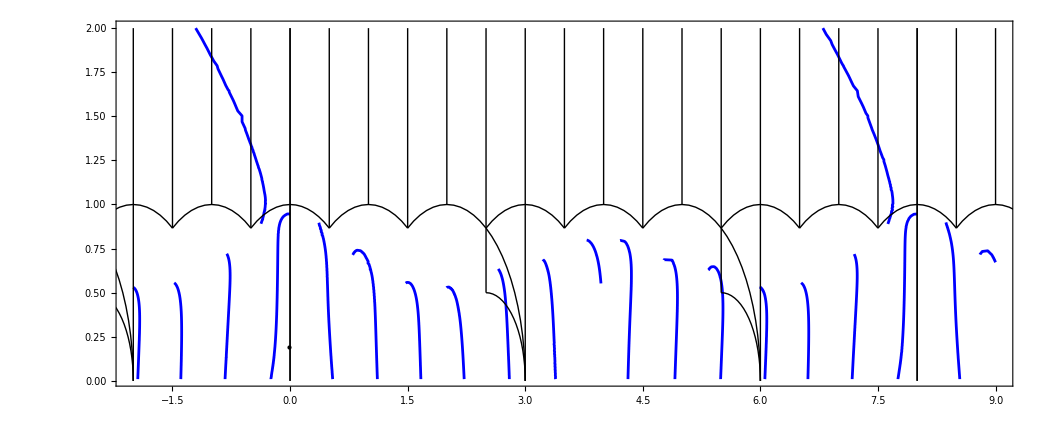

```mathematica
Show[
plts[[1]],
Graphics[{Point[ReIm[tau0]]}],
G10RepeatDomain[{-1,1}],
AspectRatio->Automatic
]
```

```mathematica
ZLV[GV[0,1,1/2]/.repCh, (4+2I)/8,0]
```

ⅈ/4

```mathematica
u/.Solve[MirrorCurveJ[1,u]==1728KleinInvariantJ[4+2I]][[2]]
N[ZNewSeries[GV[0,1,1/2]/.repCh,%],50]
```

Root-0.207Root[1-24 #1^2-72 #1^3+240 #1^4+1152 #1^5+448 #1^6-6912 #1^7+(-9984-1728 KleinInvariantJ[2 ⅈ]) #1^8+(4608-1728 KleinInvariantJ[2 ⅈ]) #1^9+(21504+13824 KleinInvariantJ[2 ⅈ]) #1^10+(-18432+62208 KleinInvariantJ[2 ⅈ]) #1^11+(4096+19008 KleinInvariantJ[2 ⅈ]) #1^12&,2]-0.20705417272722917

```mathematica
UTau[tau_]:=u/.FindRoot[MirrorCurveJ[1,u]==1728KleinInvariantJ[tau], {u, USeries[tau, 1]},WorkingPrecision->40];
UTau[4+2I]
N[ZNewSeries[GV[0,1,1/2]/.repCh,UTau[4+2I]],50]
```

-0.2070541727272291722147146969836964289702

0.+0.2467571125938325279585139295779969673297 ⅈ

```mathematica
ContourPlot[Re[ZNewSeries[GV[0,1,1/2]/.repCh, UTau[t1+I t2]]]==0, {t1,3.5,4.5},{t2,1,2}]
```

FindRoot::srect: Value «22»+10550.24749539993267022364165086401044391 («63»)^((0.+«78» ⅈ) (t1+(«20»+«20» ⅈ) t2)) in search specification {u,USeries[t1+ⅈ t2,1]} is not a number or array of numbers.

ReplaceAll::reps: {FindRoot[MirrorCurveJ[1,u]==1728 KleinInvariantJ[t1+ⅈ t2],{u,USeries[t1+ⅈ t2,1]},WorkingPrecision→40]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::srect: Value «22»+10550.24749539993267022364165086401044391 («63»)^((0.+«78» ⅈ) (t1+(«20»+«20» ⅈ) t2)) in search specification {u,USeries[t1+ⅈ t2,1]} is not a number or array of numbers.

ReplaceAll::reps: {FindRoot[MirrorCurveJ[1,u]==1728 KleinInvariantJ[t1+ⅈ t2],{u,USeries[t1+ⅈ t2,1]},WorkingPrecision→40]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::srect: Value «22»+10550.24749539993267022364165086401044391 («63»)^((0.+«78» ⅈ) (t1+(«20»+«20» ⅈ) t2)) in search specification {u,USeries[t1+ⅈ t2,1]} is not a number or array of numbers.

General::stop: Further output of FindRoot::srect will be suppressed during this calculation.

ReplaceAll::reps: {FindRoot[MirrorCurveJ[1,u]==1728 KleinInvariantJ[t1+ⅈ t2],{u,USeries[t1+ⅈ t2,1]},WorkingPrecision→40]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

FindRoot::precw: The precision of the argument function (((1-8 u^2-24 u^3+16 u^4)^3)/(u^8 (1+u-8 u^2-36 u^3-11 u^4))==-89.7304+0.135577 ⅈ) is less than WorkingPrecision (40.).

$Aborted

```mathematica
FindRoot[ZNewSeries[GV[0,1,1/2]/.repCh,UTau[t1+I .3]], {t1,4,4-.1,4+.1}]
```

FindRoot::srect: Value ⅇ^(1/4 ⅈ π ((0.+0.3 ⅈ)+t1))-1/8 ⅇ^(1/2 ⅈ π ((0.+0.3 ⅈ)+t1))-245/128 ⅇ^(3/4 ⅈ π ((0.+0.3 ⅈ)+t1))-293/64 ⅇ^(ⅈ π ((0.+0.3 ⅈ)+t1))+«15»+(95028181377899290971 ⅇ^(15/4 ⅈ π ((0.+0.3 ⅈ)+t1)))/9007199254740992 in search specification {u,USeries[(0.+0.3 ⅈ)+t1,1]} is not a number or array of numbers.

ReplaceAll::reps: {FindRoot[MirrorCurveJ[1,u]==1728 KleinInvariantJ[(0.+0.3 ⅈ)+t1],{u,USeries[(0.+0.3 ⅈ)+t1,1]},WorkingPrecision→40]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::srect: Value ⅇ^(1/4 ⅈ π ((0.+0.3 ⅈ)+t1))-1/8 ⅇ^(1/2 ⅈ π ((0.+0.3 ⅈ)+t1))-245/128 ⅇ^(3/4 ⅈ π ((0.+0.3 ⅈ)+t1))-293/64 ⅇ^(ⅈ π ((0.+0.3 ⅈ)+t1))+«15»+(95028181377899290971 ⅇ^(15/4 ⅈ π ((0.+0.3 ⅈ)+t1)))/9007199254740992 in search specification {u,USeries[(0.+0.3 ⅈ)+t1,1]} is not a number or array of numbers.

ReplaceAll::reps: {FindRoot[MirrorCurveJ[1,u]==1728 KleinInvariantJ[(0.+0.3 ⅈ)+t1],{u,USeries[(0.+0.3 ⅈ)+t1,1]},WorkingPrecision→40]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::srect: Value ⅇ^(1/4 ⅈ π ((0.+0.3 ⅈ)+t1))-1/8 ⅇ^(1/2 ⅈ π ((0.+0.3 ⅈ)+t1))-245/128 ⅇ^(3/4 ⅈ π ((0.+0.3 ⅈ)+t1))-293/64 ⅇ^(ⅈ π ((0.+0.3 ⅈ)+t1))+«15»+(95028181377899290971 ⅇ^(15/4 ⅈ π ((0.+0.3 ⅈ)+t1)))/9007199254740992 in search specification {u,USeries[(0.+0.3 ⅈ)+t1,1]} is not a number or array of numbers.

General::stop: Further output of FindRoot::srect will be suppressed during this calculation.

ReplaceAll::reps: {FindRoot[MirrorCurveJ[1,u]==1728 KleinInvariantJ[(0.+0.3 ⅈ)+t1],{u,USeries[(0.+0.3 ⅈ)+t1,1]},WorkingPrecision→40]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

FindRoot::precw: The precision of the argument function (((1-8 u^2-24 u^3+16 u^4)^3)/(u^8 (1+u-8 u^2-36 u^3-11 u^4))==1.24693×10^9+0. ⅈ) is less than WorkingPrecision (40.).

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal, but was unable to find a sufficient decrease in the merit function. You may need more than 40. digits of working precision to meet these tolerances.

FindRoot::precw: The precision of the argument function (((1-8 u^2-24 u^3+16 u^4)^3)/(u^8 (1+u-8 u^2-36 u^3-11 u^4))==1.24693×10^9+0. ⅈ) is less than WorkingPrecision (40.).

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal, but was unable to find a sufficient decrease in the merit function. You may need more than 40. digits of working precision to meet these tolerances.

FindRoot::precw: The precision of the argument function (((1-8 u^2-24 u^3+16 u^4)^3)/(u^8 (1+u-8 u^2-36 u^3-11 u^4))==1.24693×10^9+0. ⅈ) is less than WorkingPrecision (40.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal, but was unable to find a sufficient decrease in the merit function. You may need more than 40. digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

FindRoot::reged: The point {4.} is at the edge of the search region {3.9,4.1} in coordinate 1 and the computed search direction points outside the region.

{t1→4.}

```mathematica
FindInstance[{Re[z[[1]]/.{u->5/100Exp[I th]}]==0, 0<=th<2Pi},th, 2]
```

$Aborted

```mathematica
FindInstance[{Re[z[[1]]/.{u->5/100Exp[I th]}]==0, 0<=th<2Pi},th, 2]
```

```mathematica
t=SystemMatrix[F1Series[1, u, 400, 7], 1, u][[All,2]];
td=SystemMatrix[F1Series[1, u, 400, 7], 1, u][[All,3]];
z=Table[(Ch[0, 0] /. repCh). Sigma.{1,0,t[[i]],td[[i]]}, {i, 1, Length[t]}];
```

```mathematica
u0=5/100Exp[I th]/.FindRoot[Re[z[[1]]/.{u->5/100Exp[I th]}], {th,Pi/3,0,2Pi},WorkingPrecision->100]
```

-0.045319217553246285961374370305287311777435454005242170175151174884492214197677117944150978823226362-0.0211227015403222917872863573525093762778927227087367432062243962839553664996042198730070773279868353 ⅈ

```mathematica
z0=z/.{u->u0}
```

{0.+1.640123633742007685465590246766893367225312107373291475467705624293445523339928056857 ⅈ,15.6783347967088607240192540812168988709425301914525545254420092614883227632137368093+4.86640767972972901204474136508343518679318152659355298512106238190273673510572381654 ⅈ,375.829293295545906592620491320963811400519386116774910239171317099404056404462550837-107.74234911682496611734779736100803584142200199895877032568051379739081554909985783 ⅈ}

```mathematica
Z0=SystemMatrix[F1Series[1, u0, 200, 7], 1, u0];
```

```mathematica
(Ch[0,0]/.repCh).Sigma.{1,0,tmp[[1,2]], tmp[[1,3]]}
```

0.+1.64012363374200768546559024676689336722531210737329147546770562429344552333992805685719 ⅈ

```mathematica
ClearAll[t];
```

```mathematica
-I Conjugate[z0[[2]]]
ReIm[%].Normalize[ReIm[u0]]
```

-4.86640767972972901204474136508343518679318152659355298512106238190273673510572381654-15.6783347967088607240192540812168988709425301914525545254420092614883227632137368093 ⅈ

11.0342114980118180624525089281827857541328319333491111768434645612458164398180094416

```mathematica
u0
```

-0.045319217553246285961374370305287311777435454005242170175151174884492214197677117944150978823226362-0.0211227015403222917872863573525093762778927227087367432062243962839553664996042198730070773279868353 ⅈ

```mathematica
Thread[D[{Y1[t], Y2[t], Y3[t]},t]==u'[t] PicardFuchsA[λ,u[t]].{Y1[t], Y2[t], Y3[t]}]
```

{Y1'[t]==Y2[t] u'[t],Y2'[t]==Y3[t] u'[t],Y3'[t]==(-((8 λ^2+16 λ u[t]+(9-256 λ^3) u[t]^2-1860 λ^2 u[t]^3+16 λ (-189+64 λ^3) u[t]^4+54 (-27+16 λ^3) u[t]^5) Y2[t])/(u[t]^2 (8 λ+9 u[t]) (λ+u[t]-8 λ^2 u[t]^2-36 λ u[t]^3+(-27+16 λ^3) u[t]^4))-((24 λ^2+50 λ u[t]+(27-320 λ^3) u[t]^2-2016 λ^2 u[t]^3+4 λ (-783+224 λ^3) u[t]^4+54 (-27+16 λ^3) u[t]^5) Y3[t])/(u[t] (8 λ+9 u[t]) (λ+u[t]-8 λ^2 u[t]^2-36 λ u[t]^3+(-27+16 λ^3) u[t]^4))) u'[t]}

```mathematica
sol=With[{psi=0,λ=1},
NDSolve[{
u'[t]==-I Exp[I psi] Conjugate[Y2[t]],
Y1'[t]==Y2[t] u'[t],
Y2'[t]==Y3[t] u'[t],Y3'[t]==(-((8 λ^2+16 λ u[t]+(9-256 λ^3) u[t]^2-1860 λ^2 u[t]^3+16 λ (-189+64 λ^3) u[t]^4+54 (-27+16 λ^3) u[t]^5) Y2[t])/(u[t]^2 (8 λ+9 u[t]) (λ+u[t]-8 λ^2 u[t]^2-36 λ u[t]^3+(-27+16 λ^3) u[t]^4))-((24 λ^2+50 λ u[t]+(27-320 λ^3) u[t]^2-2016 λ^2 u[t]^3+4 λ (-783+224 λ^3) u[t]^4+54 (-27+16 λ^3) u[t]^5) Y3[t])/(u[t] (8 λ+9 u[t]) (λ+u[t]-8 λ^2 u[t]^2-36 λ u[t]^3+(-27+16 λ^3) u[t]^4))) u'[t],
Y1[0]==z0[[1]],
Y2[0]==z0[[2]],
Y3[0]==z0[[3]],
u[0]==u0
}, {u, Y1,Y2,Y3}, {t,0,3/10}, WorkingPrecision->60]
]
```

NDSolve::mxst: Maximum number of 10000 steps reached at the point t == 0.256604438337712711056134372274877284829723697366763291230213.

{{u→InterpolatingFunction[{{0, 0.256604438337712711056134372274877284829723697366763291230213}}, <>],Y1→InterpolatingFunction[{{0, 0.256604438337712711056134372274877284829723697366763291230213}}, <>],Y2→InterpolatingFunction[{{0, 0.256604438337712711056134372274877284829723697366763291230213}}, <>],Y3→InterpolatingFunction[{{0, 0.256604438337712711056134372274877284829723697366763291230213}}, <>]}}

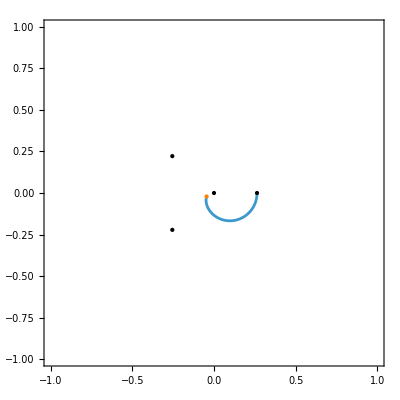

```mathematica
Show[
ParametricPlot[ReIm[u[t]/.First[sol]], {t,0,tStop},
Axes->False,
Frame->True
],
Graphics[{Point[ReIm/@Join[URoots[N[1,100]], {0}]], Orange,Point[ReIm[u0]]}],
PlotRange->{{-1,1},{-1,1}}
]
```

```mathematica
Manipulate[Show[
Graphics[{Green,Point[ReIm[u[t]/.First[sol]]], Black,Point[ReIm/@Join[URoots[N[1,100]], {0}]], Orange,Point[ReIm[u0]]}],
PlotRange->{{-1,1},{-1,1}}
], {{t,0},0,tStop,.0001}]
```

First::normal: Nonatomic expression expected at position 1 in First[sol].

ReplaceAll::reps: {First[sol]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

First::normal: Nonatomic expression expected at position 1 in First[sol].

ReplaceAll::reps: {First[sol]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

```mathematica
InverseJ[MirrorCurveJ[1,u0]]
1728KleinInvariantJ[%]
```

0.0300657+0.258436 ⅈ

-2.457×10^10+8.99485×10^9 ⅈ

```mathematica
Normal[tauu]/.{λ->1,u->u0}
```

-23.98767782925206705813208076828439049103850079888508433507837063607685945501397406329888746116495485-21.64021182895321589842588805794119394903264332691424159967294302487331333926435453040351816734956761 ⅈ

```mathematica
URoots[1]
```

{-3.02572,-0.255099-0.221553 ⅈ,-0.255099+0.221553 ⅈ,0.263185}

```mathematica
4+8Log[u0]/(2Pi I)
1728KleinInvariantJ[%]
```

0.555324843108589977249367852577371011376814854433787718997966962673638133860384570928994528905012137+3.814284796128317337076975439429009470136731283171779270563780963387694912198452633105119460096675664 ⅈ

-2.40687974330395845633718585315548861118638496649757429691446931621436333461889836380577429999619×10^10+8.72083449636193206628657298358310388866058654753885782423580871445397776946411458726639121834371×10^9 ⅈ

```mathematica
Precision[u0]
```

99.4464

```mathematica
ReIm[8Log[u0]/(2Pi I)]
FindRoot[ReIm[1728KleinInvariantJ[t1+I t2]-MirrorCurveJ[1,u0]], {t1,%[[1]]},{t2,%[[2]]}, WorkingPrecision->90]
tau0=t1+I t2/.%
```

{-3.444675156891410022750632147422628988623185145566212281002033037326361866139615429071005471094987863,3.814284796128317337076975439429009470136731283171779270563780963387694912198452633105119460096675664}

{t1→-3.44414668213360935957906257516593909995193901139158033150354721841054014940555564375646713,t2→3.81775749982133216940974243287255908482437000444588511441074629969219516654370387649011607}

-3.44414668213360935957906257516593909995193901139158033150354721841054014940555564375646713+3.81775749982133216940974243287255908482437000444588511441074629969219516654370387649011607 ⅈ

{-0.045319217553246285961374370305287311777435454005242170175151-0.021122701540322291787286357352509376277892722708736743206224 ⅈ}

```mathematica
upath[t_]:=u[t]/.First[sol]
```

```mathematica
upath[1/10]
```

0.16421351192407738523024129072946597477932472893471123831051-0.15287984702034855465226449262000920867257760070907976258282 ⅈ

```mathematica
sol2=NDSolve[{
tau'[t]==(-(((1-8 upath[t]^2-24 upath[t]^3+16 upath[t]^4)^2 (8+9 upath[t]-96 upath[t]^2-396 upath[t]^3+60 upath[t]^4+1584 upath[t]^5+2512 upath[t]^6+1368 upath[t]^7))/(upath[t]^9 (1+upath[t]-8 upath[t]^2-36 upath[t]^3-11 upath[t]^4)^2)))/(1728KleinInvariantJ'[tau[t]]) upath'[t],
tau[0]==tau0
}, tau, {t,0,(u/.First[sol])["Domain"][[1,2]]}, WorkingPrecision->30,MaxSteps->10^7]
```

{{tau→InterpolatingFunction[{{0, 0.256604438337712711056134372275}}, <>]}}

```mathematica
(u/.First[sol])["Domain"][[1,2]]
```

0.256604438337712711056134372274877284829723697366763291230213

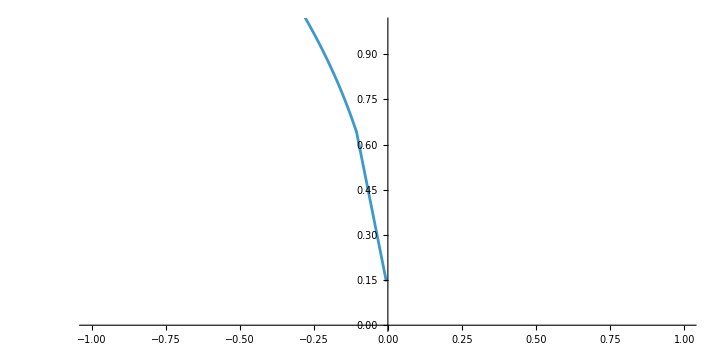

```mathematica
ParametricPlot[ReIm[tau[t]/.First[sol]], {t,0,tStop},
PlotRange->{{-1,1},{0,1}}
]
```

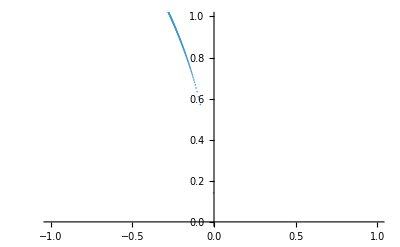

```mathematica
tR=Subdivide[0,tStop,10000];
ListPlot[ReIm[tau[#]/.First[sol]&/@tR],
PlotRange->{{-1,1},{0,1}}
]
```

```mathematica
sol=With[{psi=0,λ=1},
NDSolve[{
u'[t]==-I Exp[I psi] Conjugate[Y2[t]],
Y1'[t]==Y2[t] u'[t],
Y2'[t]==Y3[t] u'[t],Y3'[t]==(-((8 λ^2+16 λ u[t]+(9-256 λ^3) u[t]^2-1860 λ^2 u[t]^3+16 λ (-189+64 λ^3) u[t]^4+54 (-27+16 λ^3) u[t]^5) Y2[t])/(u[t]^2 (8 λ+9 u[t]) (λ+u[t]-8 λ^2 u[t]^2-36 λ u[t]^3+(-27+16 λ^3) u[t]^4))-((24 λ^2+50 λ u[t]+(27-320 λ^3) u[t]^2-2016 λ^2 u[t]^3+4 λ (-783+224 λ^3) u[t]^4+54 (-27+16 λ^3) u[t]^5) Y3[t])/(u[t] (8 λ+9 u[t]) (λ+u[t]-8 λ^2 u[t]^2-36 λ u[t]^3+(-27+16 λ^3) u[t]^4))) u'[t],
Y1[0]==z0[[1]],
Y2[0]==z0[[2]],
Y3[0]==z0[[3]],
u[0]==u0,
tau'[t]==(-((1-8 u[t]^2-24 u[t]^3+16 u[t]^4)^2 (8+9 u[t]-96 u[t]^2-396 u[t]^3+60 u[t]^4+1584 u[t]^5+2512 u[t]^6+1368 u[t]^7))/(u[t]^9 (1+u[t]-8 u[t]^2-36 u[t]^3-11 u[t]^4)^2))/(1728KleinInvariantJ'[tau[t]]) (-I Exp[I psi] Conjugate[Y2[t]]),
tau[0]==tau0,
WhenEvent[Abs[Y1[t]]<10^-20,{tStop=t,"StopIntegration"}]
}, {u, Y1,Y2,Y3, tau}, {t,0,3/10}, WorkingPrecision->40,MaxSteps->10^7,MaxStepSize->10^-4]
]
```

$Aborted

```mathematica
ClearAll[t];
```

```mathematica
sol=With[{psi=0,λ=1},
NDSolve[{
u'[t]==-I Exp[I psi] Normalize[Conjugate[Y2[t]]],
Y1'[t]==Y2[t] u'[t],
Y2'[t]==Y3[t] u'[t],Y3'[t]==(-(((8 λ^2+16 λ u[t]+(9-256 λ^3) u[t]^2-1860 λ^2 u[t]^3+16 λ (-189+64 λ^3) u[t]^4+54 (-27+16 λ^3) u[t]^5) Y2[t])/(u[t]^2 (8 λ+9 u[t]) (λ+u[t]-8 λ^2 u[t]^2-36 λ u[t]^3+(-27+16 λ^3) u[t]^4)))-((24 λ^2+50 λ u[t]+(27-320 λ^3) u[t]^2-2016 λ^2 u[t]^3+4 λ (-783+224 λ^3) u[t]^4+54 (-27+16 λ^3) u[t]^5) Y3[t])/(u[t] (8 λ+9 u[t]) (λ+u[t]-8 λ^2 u[t]^2-36 λ u[t]^3+(-27+16 λ^3) u[t]^4))) u'[t],
Y1[0]==z0[[1]],
Y2[0]==z0[[2]],
Y3[0]==z0[[3]],
u[0]==u0,tau'[t]==(-(((1-8 u[t]^2-24 u[t]^3+16 u[t]^4)^2 (8+9 u[t]-96 u[t]^2-396 u[t]^3+60 u[t]^4+1584 u[t]^5+2512 u[t]^6+1368 u[t]^7))/(u[t]^9 (1+u[t]-8 u[t]^2-36 u[t]^3-11 u[t]^4)^2)))/(1728 KleinInvariantJ'[tau[t]]) u'[t],tau[0]==tau0,WhenEvent[Abs[Y1[t]]<10^-20,{tStop=t,"StopIntegration"}]},{u,Y1,Y2,Y3,tau},{t,0,1},WorkingPrecision->40,MaxSteps->10^7, MaxStepSize->10^-4]]
```

{{u→InterpolatingFunction[{{0, 0.4949645474164293566485136543073268672940}}, <>],Y1→InterpolatingFunction[{{0, 0.4949645474164293566485136543073268672940}}, <>],Y2→InterpolatingFunction[{{0, 0.4949645474164293566485136543073268672940}}, <>],Y3→InterpolatingFunction[{{0, 0.4949645474164293566485136543073268672940}}, <>],tau→InterpolatingFunction[{{0, 0.4949645474164293566485136543073268672940}}, <>]}}

```mathematica
tStop
```

0.494964547416429356648513654307326867294

```mathematica
t
```

```mathematica
tStop
```

0.2566044383377127106721948770246357625128

```mathematica
Abs[Y1[tStop]]/.First[sol]
```

9.5491011927943901063×10^-21

```mathematica
u[tStop]-URoot[1,2]/.First[sol]
```

-8.914366543551619511322×10^-19+4.92922104454411428698×10^-19 ⅈ

```mathematica
tau[tStop]/.First[sol]
1728KleinInvariantJ[%]
```

0.001775623200780826596462+0.148608133260432710587248 ⅈ

2.0022405700083091296×10^18+1.1071438790104542425×10^18 ⅈ

```mathematica
MirrorCurveJ[1,u[tStop]/.First[sol]]
```

2.00224057001459390183×10^18+1.10714387901125971688×10^18 ⅈ

```mathematica
Simplify[MirrorCurveJ[1,u[tStop]/.First[sol]]]
```

745.836326512551384608613003979836648402375-2.609307027591984711977405469879379494601844341815×10^10 ⅈ

```mathematica
?PicardFuchs
```

```mathematica
u+Sum[a[i]u^i, {i,2,nmax}]
```

u+u^2 a[2]

```mathematica
nmax=3;
Simplify[Series[PicardFuchs[u+Sum[a[i]u^i, {i,2,nmax}], λ,u], {u,-8/9λ,2}]]
```

(-2 a[2]+16/3 λ a[3]+((27+512 λ^3) (27-48 λ a[2]+64 λ^2 a[3]))/(24 λ (27+256 λ^3)))/(u+(8 λ)/9)+(3 (-81+640 λ^3) (729+13824 λ^3-2592 λ a[2]-36864 λ^4 a[2]+5184 λ^2 a[3]+65536 λ^5 a[3]))/(32 λ^2 (27+256 λ^3)^2)-1/(512 (λ^3 (27+256 λ^3)^3))243 (-3483891-76702464 λ^3-905969664 λ^9+13856832 λ a[2]+217976832 λ^4 a[2]+56623104 λ^7 a[2]+1342177280 λ^10 a[2]-30233088 λ^2 a[3]-412729344 λ^5 a[3]+12582912 λ^8 a[3]) (u+(8 λ)/9)-1/(1024 (λ^4 (27+256 λ^3)^4))2187 (180158499+4293098496 λ^3-3296526336 λ^6-15627976704 λ^9-83751862272 λ^12-722759760 λ a[2]-12791955456 λ^4 a[2]-5541986304 λ^7 a[2]+33822867456 λ^10 a[2]+85899345920 λ^13 a[2]+1632586752 λ^2 a[3]+26542411776 λ^5 a[3]+36691771392 λ^8 a[3]-37849399296 λ^11 a[3]) (u+(8 λ)/9)^2+O[u+(8 λ)/9]^3